## Common elements

```mathematica
(* Load HEPMath package *)
Needs["HEPMath`"]

(* Declare external momenta. *)
DeclareLorentzVectors[q,k1,p1,p2,k2,l];

(* Declare real parameters + kinematics *)
DeclareReal[gs,e,eH,eL, m2,q2];
DeclareReal[s,sp,s3,s4,s5,t,tp,tpsp,t1,u,up,u1,u5,u6,u7];

norm={s-> sp+q2,s4-> sp+t1+u1,t-> t1+m2,u->u1+m2,u1p->u1-q2};
massSub={Sqr[p1]-> m2,Sqr[-p1]-> m2,Sqr[p2]-> m2,Sqr[-p2]-> m2,Sqr[q]-> q2,Sqr[-q]-> q2,Sqr[k1]-> 0,Sqr[-k1]-> 0,Sqr[k2]-> 0,Sqr[-k2]-> 0};
(* color factors *)
normColor={Kgγ-> 1/(NC^2-1),Kqγ-> 1/NC,CA->NC,CF-> (NC^2-1)/(2NC),NC-> 3};
normColor=(First@#-> (Last@#/.normColor))&/@normColor;

swaptu[e_]:=e//.{t1-> vu1}//.{u1-> t1}//.{vu1->u1};

(* debug tools *)
getAllSymbols=e↦ DeleteDuplicates[Reap[Map[If[Head[#]==Symbol,Sow[#]]&,e,Infinity]][[2]][[1]]];
```

```mathematica
DeclareRealHEPTensor[{gluonTensor,projG,projL},{Lorentz,Lorentz}];
DeclareHEPTensor[{projP,polGluonTensor},{Lorentz,Lorentz}];
projG[μ_,ν_]=-Eta[μ,ν];
projL[μ_,ν_]:=-4q2/sp^2 k1[μ]k1[ν];
projP[μ_,ν_]:=I LorentzContract@HEPMultiply[Eps[μ,ν,ρ,σ] q[ρ] k1[σ]]/sp
gluonTensor[μ_,ν_]=-Eta[μ,ν];
polGluonTensor[μ_,ν_]:=2I LorentzContract@HEPMultiply[Eps[μ,ν,ρ,σ] k1[ρ] q[σ]]/sp;

getGetNLOMe[kinVars_]:=me↦Module[{mxe},
mxe=CalcDiracTraces@me;
mxe=LorentzContract@HEPExpand@mxe;
mxe=RemoveEpsDot@mxe;
(* replace HDots *)
mxe=mxe/.{HDot[k2,k2]-> -k2hat2,HDot[p1,p1]-> -k2hat2,HDot[k2,p1]-> k2hat2,HDot[a_,b_]:> 0};
(* insert masses *)
mxe=Expand[mxe/.massSub];
(* insert all kinematic variables *)
mxe=Expand[mxe/.momentumVectorSDots];
(* remove some kinematic variables *)
mxe=Expand[mxe//.kinVars];
mxe=Expand[mxe/8/.{Dim-> 4+ϵ}/.norm];
mxe
]
```

```mathematica
(* remove EpsDot in favour of SDot and HDot; based on HVBM(Comm.Math.Phys. Volume 52,Number 1,11-38), TRACER and Wikipedia *)
Module[{f,a1,a2,a3,a4,b1,b2,b3,b4,cache,replace,rest},
(* master formula *)
f[ps_,qs_]:=Module[{l,mus,mups,d},
l=Length[ps];
mus=Table[Unique[],{l}];
mups=Table[Unique[],{l}];
d=-Det[Table[Eta[mus[[k]],mups[[n]]]-EtaHat[mus[[k]],mups[[n]]],{k,l},{n,l}]];
(4-l)!HEPMultiply@@Join[{d},(e↦(e[[1]])[(e[[2]])])/@Transpose[{ps,mus}],(e↦(e[[1]])[(e[[2]])])/@Transpose[{qs,mups}]]
];
(* cache elements *)
cache={
EpsDot[p1_][mu_,nu_,rho_]^2:>Evaluate[LorentzContract@HEPExpand@f[{a1},{a1}]/.{a1->p1}],
EpsDot[p1_][mu_,nu_,rho_]EpsDot[k1_][mu_,nu_,rho_]:>Evaluate[LorentzContract@HEPExpand@f[{a1},{b1}]/.{a1->p1,b1->k1}],
EpsDot[p1_,p2_][mu_,nu_]^2:>Evaluate[LorentzContract@HEPExpand@f[{a1,a2},{a1,a2}]/.{a1->p1,a2->p2}],
EpsDot[p1_,p2_][mu_,nu_]EpsDot[k1_,k2_][mu_,nu_]:>Evaluate[LorentzContract@HEPExpand@f[{a1,a2},{b1,b2}]/.{a1->p1,a2->p2,b1->k1,b2->k2}],
EpsDot[p1_,p2_,p3_][mu_]^2:>Evaluate[LorentzContract@HEPExpand@f[{a1,a2,a3},{a1,a2,a3}]/.{a1->p1,a2->p2,a3->p3}],
EpsDot[p1_,p2_,p3_][mu_]EpsDot[k1_,k2_,k3_][mu_]:>Evaluate[LorentzContract@HEPExpand@f[{a1,a2,a3},{b1,b2,b3}]/.{a1->p1,a2->p2,a3->p3,b1->k1,b2->k2,b3->k3}],
EpsDot[p1_,p2_,p3_,p4_]^2:>Evaluate[LorentzContract@HEPExpand@f[{a1,a2,a3,a4},{a1,a2,a3,a4}]/.{a1->p1,a2->p2,a3->p3,a4->p4}],
EpsDot[p1_,p2_,p3_,p4_]EpsDot[k1_,k2_,k3_,k4_]:>Evaluate[LorentzContract@HEPExpand@f[{a1,a2,a3,a4},{b1,b2,b3,b4}]/.{a1->p1,a2->p2,a3->p3,a4->p4,b1->k1,b2->k2,b3->k3,b4->k4}]
};
(* handle uncontracted; suppressed atm *)
rest={
Eps[nus__]Eps[nups__]:> Module[{l,mus,mups,d},
l=4;
mus={nus};
mups={nups};
d=-Det[Table[Eta[mus[[k]],mups[[n]]]-EtaHat[mus[[k]],mups[[n]]],{k,l},{n,l}]];
(4-l)!HEPMultiply[d]
]
};
(* replace all *)
replace[e_]:=e/.{
Sqr[EpsDot[p1_,p2_,p3_]]:>Module[{mu},mu=Unique[];EpsDot[p1,p2,p3][mu]^2],
SDot[EpsDot[p1_,p2_,p3_],EpsDot[k1_,k2_,k3_]]:>Module[{mu},mu=Unique[];EpsDot[p1,p2,p3][mu]EpsDot[k1,k2,k3][mu]]
}/.cache/.rest;
(* function to call *)
RemoveEpsDot[ex_]:=Module[{e},
e=ex;
If[FreeQ[e,EpsDot]&&FreeQ[e,Eps],Return[e]];
e=SortEps@e;
If[Head[e]===Plus,e=Parallelize[Sum[replace[e[[k]]],{k,Length@e}]],e=replace[e]];
LorentzContract@HEPExpand@e
];
]
```

```mathematica
Block[{$ContextPath,S,H,l0,l1,l2,l3,l4,p,k},
<<"~/Physik/PhD/Marco/Eps-out.m";
Module[{m0,m1,m2,m3,m4,n},
n[e_]:=e/.{HEPMath`Lorentz`HDot-> H,HEPMath`Tensors`SDot-> S};
DeclareLorentzVectors[_p,_k];
m0=RemoveEpsDot[Eps[μ,ν,ρ,σ]Eps[μ,ν,ρ,σ]];
m1=LorentzContract@RemoveEpsDot[EpsDot[p@1][ν,ρ,σ]EpsDot[k@1][ν,ρ,σ]];
m2=LorentzContract@RemoveEpsDot[EpsDot[p@1,p@2][ρ,σ]EpsDot[k@1,k@2][ρ,σ]];
m3=LorentzContract@RemoveEpsDot[EpsDot[p@1,p@2,p@3][σ]EpsDot[k@1,k@2,k@3][σ]];
m4=LorentzContract@RemoveEpsDot[EpsDot[p@1,p@2,p@3,p@4]EpsDot[k@1,k@2,k@3,k@4]];
Print@FullSimplify[n@m1-l1];
Print@FullSimplify[n@m2-l2];
Print@FullSimplify[n@m3-l3];
Print@FullSimplify[n@m4-l4];
]
]
```

0

0

0

«1 more identical outputs»

## LO γ*(q)+g(k1) → Q(p1)+Qbar(p2)

### Matrix elements

```mathematica
meLOt1[μ_,ν_]:=Ga[μ].((Gs[k1-p2]+Sqrt[m2] GI)/t1).Ga[ν];
meLOu1[μ_,ν_]:=Ga[ν].((Gs[p1-k1]+Sqrt[m2] GI)/u1).Ga[μ];
meLOt1CC[μ_,ν_]:=Reverse@meLOt1[μ,ν];
meLOu1CC[μ_,ν_]:=Reverse@meLOu1[μ,ν];
meLO[μ1_,ν1_]:=meLOt1[μ1,ν1]+meLOu1[μ1,ν1];
meLOCC[μ1_,ν1_]:=meLOt1CC[μ1,ν1]+meLOu1CC[μ1,ν1];

BornVectorSDots={
SDot[q,k1]->       sp/2,SDot[p1,p2]->(sp+q2-2m2)/2,
SDot[k1,p2]-> -t1/2, SDot[q,p1]->-(t1-q2)/2,
SDot[p1,k1]-> -u1/2,SDot[q,p2]-> -(u1-q2)/2,
HDot[a_,b_]:> 0
};
```

```mathematica
getBQED[ex_]:=Module[{e},
e=ex;
e=LorentzContract@HEPExpand@CalcDiracTraces@e;
e=RemoveEpsDot@e;
e=Simplify[e/(8)/.{Dim-> 4+ϵ}/.norm/.Join[massSub,BornVectorSDots]];
Collect[e/.{sp-> -t1-u1},ϵ,FullSimplify]
]
BQED[G]=getBQED[HEPMultiply[DiracTr[(Gs[p1]+GI Sqrt@m2).meLO[μ,ν].(Gs[p2]-GI Sqrt@m2).meLOCC[μp,νp]],projG[μ,μp],gluonTensor[ν,νp]]]
BQED[L]=getBQED[HEPMultiply[DiracTr[(Gs[p1]+GI Sqrt@m2).meLO[μ,ν].(Gs[p2]-GI Sqrt@m2).meLOCC[μp,νp]],projL[μ,μp],gluonTensor[ν,νp]]]
BQED[P]=getBQED[HEPMultiply[DiracTr[(Gs[p1]+GI Sqrt@m2).meLO[μ,ν].(Gs[p2]-GI Sqrt@m2).meLOCC[μp,νp]],projP[μ,μp],polGluonTensor[ν,νp]]]
```

(-4 m2^2 (t1+u1)^2+t1 u1 (2 q2^2+t1^2+u1^2-2 q2 (t1+u1))-2 m2 (2 t1 u1 (t1+u1)+q2 (t1^2+u1^2)))/(t1^2 u1^2)+((-m2 q2 (t1+u1)^2+t1 u1 (q2^2+t1^2+t1 u1+u1^2-q2 (t1+u1))) ϵ)/(t1^2 u1^2)+((t1+u1)^2 ϵ^2)/(4 t1 u1)

4 q2 (m2/(t1 u1)+(-q2+t1+u1)/(t1+u1)^2)

-((t1^2+u1^2) (2 m2 (t1+u1)^2+t1 u1 (-2 q2+t1+u1)))/(2 t1^2 u1^2 (t1+u1))

### Check to Nucl.Phys.B 392-162

```mathematica
Module[{BGQEDref},
Print@Collect[Expand[BQED[G]/.{sp-> -t1-u1}],{ϵ},FullSimplify];
BGQEDref = t1/u1 + u1/t1 + 4m2 sp/(t1 u1)(1-m2 sp/(t1 u1)) + 2 sp q2/(t1 u1) + 2q2^2/(t1 u1) +2m2 q2/(t1 u1)(2- sp^2/(t1 u1))+ϵ(-1+(sp^2+sp q2 + q2^2)/(t1 u1) - m2 q2 sp^2/(t1^2 u1^2)) + ϵ^2sp^2/(4t1 u1);
Print@Collect[Expand[BGQEDref/.{sp-> -t1-u1}],{ϵ},FullSimplify];
Collect[FullSimplify[(BQED[G]/.{sp-> -t1-u1,Dim-> 4+ϵ})-(BGQEDref/.{sp-> -t1-u1})],ϵ]
]
```

(-4 m2^2 (t1+u1)^2+t1 u1 (2 q2^2+t1^2+u1^2-2 q2 (t1+u1))-2 m2 (2 t1 u1 (t1+u1)+q2 (t1^2+u1^2)))/(t1^2 u1^2)+((-m2 q2 (t1+u1)^2+t1 u1 (q2^2+t1^2+t1 u1+u1^2-q2 (t1+u1))) ϵ)/(t1^2 u1^2)+((t1+u1)^2 ϵ^2)/(4 t1 u1)

(-4 m2^2 (t1+u1)^2+t1 u1 (2 q2^2+t1^2+u1^2-2 q2 (t1+u1))-2 m2 (2 t1 u1 (t1+u1)+q2 (t1^2+u1^2)))/(t1^2 u1^2)+((-m2 q2 (t1+u1)^2+t1 u1 (q2^2+t1^2+t1 u1+u1^2-q2 (t1+u1))) ϵ)/(t1^2 u1^2)+((t1+u1)^2 ϵ^2)/(4 t1 u1)

0

```mathematica
Module[{BLQEDref},
Print@Collect[Expand[BQED[L]/.{sp-> -t1-u1,Dim-> 4+ϵ}],{ϵ},FullSimplify];
BLQEDref = -4q2/sp((sp+q2)/sp-m2 sp/(t1 u1));
Print@Collect[Expand[BLQEDref/.{sp-> -t1-u1}],{ϵ},FullSimplify];
Collect[FullSimplify[(BQED[L]/.{sp-> -t1-u1,Dim-> 4+ϵ})-(BLQEDref/.{sp-> -t1-u1})],ϵ]
]
```

4 q2 (m2/(t1 u1)+(-q2+t1+u1)/(t1+u1)^2)

4 q2 (m2/(t1 u1)+(-q2+t1+u1)/(t1+u1)^2)

0

### check to Marco

```mathematica
Marco`BPQED = << "~/Physik/PhD/Marco/recalc/data/BPQED"
Simplify[((Marco`BPQED/2/.{m^2-> m2})-BQED[P])/.norm/.{sp-> -t1-u1}]
```

q2/sp-(2 m^2)/t1+s/t1-t1/sp-(2 m^2 t1)/u1^2-(2 m^2)/u1+s/u1+t1/u1-(q2 t1)/(sp u1)+t1^2/(sp u1)-(2 m^2 u1)/t1^2+u1/t1-u1p/sp+(u1 u1p)/(sp t1)

0

### old/HEP way

```mathematica
DeclareLorentzVectors[mxBornt1,mxBornu1,mxBorn];
mxBornt1[μ_]=(Bar[USp[p1][r1]].(-I eH e Ga[μ]).(I(Gs[k1-p2]+Sqrt[m2] GI)).(I gs Ga[ν]).VSp[p2][r2])/(t1)Pol[k1][λg,ν]*ColorT[a,j1,j2];
mxBornu1[μ_]=(Bar[USp[p1][r1]].(I gs Ga[ν]).(I(Gs[p1-k1]+Sqrt[m2] GI)).(-I eH e Ga[μ]).VSp[p2][r2])/(u1)Pol[k1][λg,ν]*ColorT[a,j1,j2];
mxBorn[μ_]=mxBornt1[μ]+mxBornu1[μ]
```

1/t1 ColorT[a,j1,j2] Bar[USp[p1]][r1].(-ⅈ e eH Ga[μ]).(ⅈ (GI √m2+Gs[k1-p2])).(ⅈ gs Ga[ν]).VSp[p2][r2] Pol[k1][λg,ν]+1/u1 ColorT[a,j1,j2] Bar[USp[p1]][r1].(ⅈ gs Ga[ν]).(ⅈ (GI √m2+Gs[-k1+p1])).(-ⅈ e eH Ga[μ]).VSp[p2][r2] Pol[k1][λg,ν]

```mathematica
Module[{ng,σG1,σG2,σG3,σG4,σG5,BGQED2},
(* guage vector *)
DeclareLorentzVectors[ng];
σG1=-HEPMultiply[mxBorn[mu],CC@mxBorn[mu]];
(* sum QQbar *)
σG2 = FermionPolarizationSums[σG1, {p1->Sqrt[m2], p2->Sqrt[m2]}];
(* sum g *)
σG3 = VectorPolarizationSums[σG2, {k1->ng}];
σG4 = σG3 // CalcDiracTraces //        (* Compute Dirac traces. *)
             HEPExpand //              (* Expand. *)
             LorentzContract //(* Contract Lorentz indices *)
	ColorReduce;(* eliminate Color *)
σG5=Simplify[σG4/.{Dim-> 4+ϵ}/.Join[massSub,{
Sqr[ng]->0, 
SDot[q,k1]->       sp/2,SDot[p1,p2]->(sp+q2-2m2)/2,
SDot[k1,p2]-> -t1/2, SDot[q,p1]->-(t1-q2)/2,
SDot[p1,k1]-> -u1/2,SDot[q,p2]-> -(u1-q2)/2
}]];
BGQED2=σG5/(8gs^2 e^2 eH^2 (3 *4/3));
Simplify[BGQED-BGQED2]
]
```

0

```mathematica
Module[{ng,σL1,σL2,σL3,σL4,σL5,BLQED2},
(* guage vector *)
DeclareLorentzVectors[ng];
σL1=-4q2/sp^2 HEPMultiply[k1[mu], mxBorn[mu]]HEPMultiply[k1[nu],CC@mxBorn[nu]];
(* sum QQbar *)
σL2 = FermionPolarizationSums[σL1, {p1->Sqrt[m2], p2->Sqrt[m2]}];
(* sum g *)
σL3 = VectorPolarizationSums[σL2, {k1->ng}];
σL4 = σL3 // CalcDiracTraces //        (* Compute Dirac traces. *)
             HEPExpand //              (* Expand. *)
             LorentzContract //(* Contract Lorentz indices *)
	ColorReduce;(* eliminate Color *);
σL5=Simplify[σL4/.Join[massSub,{
Sqr[ng]->0, 
SDot[q,k1]->       sp/2,SDot[p1,p2]->(sp+q2-2m2)/2,
SDot[k1,p2]-> -t1/2, SDot[q,p1]->-(t1-q2)/2,
SDot[p1,k1]-> -u1/2,SDot[q,p2]-> -(u1-q2)/2
}]];
BLQED2=σL5/(8gs^2 e^2 eH^2 (3 *4/3));
Simplify[BLQED-BLQED2]
]
```

0

## NLO γ*(q)+q(k1) → Q(p1)+Qbar(p2)+q(k2)

### 2 → 3 phasespace

```mathematica
momentumVectorSDots={
SDot[q,k1]->sp/2,
SDot[k2,p2]->s3/2,
SDot[k2,p1]->s4/2,
SDot[p1,p2]->(s5-2m2)/2,
SDot[k1,p2]->-t1/2,
SDot[k1,k2]->-tp/2,
SDot[q,p2]->-(u1-q2)/2,
SDot[k1,p1]->-u6/2,
SDot[q,p1]->-(u7-q2)/2,
SDot[q,k2]->-(up-q2)/2
};
kinematicConstraints = {
0==sp+u1+u7+up-q2,
0==sp+t1+tp+u6,
0==s4+s5+u6+u7-q2,
0==s3+s5+t1+u1-q2,
0==s3+s4+tp+up-q2
};
```

### Matrix elements

```mathematica
meNLOγqalQ[μ_,νQ_]=(Ga[μ]).((Gs[p1-q]+Sqrt[m2] GI)/u7).(Ga[νQ]);
meNLOγqblQ[μ_,νQ_]=(Ga[νQ]).((Gs[q-p2]+Sqrt[m2] GI)/u1).(Ga[μ]);
meNLOγqalQCC[μ_,νQ_]=Reverse@meNLOγqalQ[μ,νQ];
meNLOγqblQCC[μ_,νQ_]=Reverse@meNLOγqblQ[μ,νQ];
meNLOγqabg[νQ_,νq_]=gluonTensor[νQ,νq]/tp;
meNLOγqablQ[μ_,νQ_]=meNLOγqalQ[μ,νQ]+meNLOγqblQ[μ,νQ];
meNLOγqablQCC[μ_,νQ_]=meNLOγqalQCC[μ,νQ]+meNLOγqblQCC[μ,νQ];

meNLOγqclq[μ_,νq_]=(Ga[μ]).(Gs[k2-q]/up).(Ga[νq]);
meNLOγqdlq[μ_,νq_]=(Ga[νq]).(Gs[k1+q]/s).(Ga[μ]);
meNLOγqclqCC[μ_,νq_]=Reverse@meNLOγqclq[μ,νq];
meNLOγqdlqCC[μ_,νq_]=Reverse@meNLOγqdlq[μ,νq];
meNLOγqcdg[νQ_,νq_]=gluonTensor[νQ,νq]/s5;
meNLOγqcdlq[μ_,νq_]=meNLOγqclq[μ,νq]+meNLOγqdlq[μ,νq];
meNLOγqcdlqCC[μ_,νq_]=meNLOγqclqCC[μ,νq]+meNLOγqdlqCC[μ,νq];
```

### AGLi

```mathematica
getA1=getGetNLOMe[{
s3->q2-s5-t1-u1,
s5-> q2-s4-u6-u7,
u6-> q2-s-t1-tp,
up-> 2q2-s-u1-u7
}];
getA2=getGetNLOMe[{
s3->q2-s5-t1-u1,
tp-> q2-s3-s4-up,
u6-> q2-s-t1-tp,
u7-> 2q2-s-u1-up
}];
getA3=getGetNLOMe[{
s3->q2-s5-t1-u1,
u6-> q2-s-t1-tp
}];
```

```mathematica
AG1=getA1[HEPMultiply[
DiracTr[(Gs[p1]+GI Sqrt@m2).meNLOγqablQ[μ,νgQ].(Gs[p2]-GI Sqrt@m2).meNLOγqablQCC[μp,νgQp]],
meNLOγqabg[νgQ,νgq],
DiracTr[(Gs[k2]).Ga[νgqp].(Gs[k1]).Ga[νgq]],
meNLOγqabg[νgQp,νgqp],
projG[μ,μp]
]];
AL1=getA1[HEPMultiply[
DiracTr[(Gs[p1]+GI Sqrt@m2).meNLOγqablQ[μ,νgQ].(Gs[p2]-GI Sqrt@m2).meNLOγqablQCC[μp,νgQp]],
meNLOγqabg[νgQ,νgq],
DiracTr[(Gs[k2]).Ga[νgqp].(Gs[k1]).Ga[νgq]],
meNLOγqabg[νgQp,νgqp],
projL[μ,μp]
]];
AP1=getA1[HEPMultiply[
DiracTr[(Gs[p1]+GI Sqrt@m2).meNLOγqablQ[μ,νgQ].(Gs[p2]-GI Sqrt@m2).meNLOγqablQCC[μp,νgQp]],
meNLOγqabg[νgQ,νgq],
DiracTr[(Gs[k2]).Ga[νgq].(Gs[k1].(GI-h G5)).Ga[νgqp]],
meNLOγqabg[νgQp,νgqp],
projP[μ,μp]
]];

CoeffAG1=CoefficientList[Expand[tp^2u7^2AG1],{tp,u7}];
CoeffAL1=CoefficientList[Expand[tp^2u7^2 AL1],{tp,u7}];
CoeffAP1=CoefficientList[Expand[tp^2u7^2 AP1],{tp,u7}];
CoeffAP1k0=Coefficient[CoeffAP1,k2hat2,0];
CoeffAP1k2=Take[Coefficient[CoeffAP1,k2hat2,1],1];

Module[{f},
f[c_]:=Select[Flatten[MapIndexed[{v,path}↦If[Not[0===v],{3,3}-path],c,{2}],1],Not[#===Null]&];
AG1List=f[CoeffAG1];
AL1List=f[CoeffAL1];
AP1k0List=f[CoeffAP1k0];
AP1k2List=f[CoeffAP1k2];
]
```

```mathematica
AG2=getA2[HEPMultiply[
DiracTr[(Gs[p1]+GI Sqrt@m2).Ga[νgQ].(Gs[p2]-GI Sqrt@m2).Ga[νgQp]],
meNLOγqcdg[νgQ,νgq],
DiracTr[(Gs[k2]).meNLOγqcdlq[μ,νgq].(Gs[k1]).meNLOγqcdlqCC[μp,νgqp]],
meNLOγqcdg[νgQp,νgqp],
projG[μ,μp]
]];
AL2=getA2[HEPMultiply[
DiracTr[(Gs[p1]+GI Sqrt@m2).Ga[νgQ].(Gs[p2]-GI Sqrt@m2).Ga[νgQp]],
meNLOγqcdg[νgQ,νgq],
DiracTr[(Gs[k2]).meNLOγqcdlq[μ,νgq].(Gs[k1]).meNLOγqcdlqCC[μp,νgqp]],
meNLOγqcdg[νgQp,νgqp],
projL[μ,μp]
]];
```

```mathematica
Module[{mecc,medd,mecd,medc},
mecc=getA2[HEPMultiply[
DiracTr[(Gs[p1]+GI Sqrt@m2).Ga[νgQ].(Gs[p2]-GI Sqrt@m2).Ga[νgQp]],
meNLOγqcdg[νgQ,νgq],
DiracTr[(Gs[k2]).meNLOγqclq[μ,νgq].(Gs[k1].(GI-h G5)).meNLOγqclqCC[μp,νgqp]],
meNLOγqcdg[νgQp,νgqp],
projP[μ,μp]
]];
medd=getA2[HEPMultiply[
DiracTr[(Gs[p1]+GI Sqrt@m2).Ga[νgQ].(Gs[p2]-GI Sqrt@m2).Ga[νgQp]],
meNLOγqcdg[νgQ,νgq],
DiracTr[(Gs[k2]).meNLOγqdlq[μ,νgq].(Gs[k1].(GI-h G5)).meNLOγqdlqCC[μp,νgqp]],
meNLOγqcdg[νgQp,νgqp],
projP[μ,μp]
]];
mecd=getA2[HEPMultiply[
DiracTr[(Gs[p1]+GI Sqrt@m2).Ga[νgQ].(Gs[p2]-GI Sqrt@m2).Ga[νgQp]],
meNLOγqcdg[νgQ,νgq],
DiracTr[(Gs[k2]).meNLOγqclq[μ,νgq].(Gs[k1].(GI-h G5)).meNLOγqdlqCC[μp,νgqp]],
meNLOγqcdg[νgQp,νgqp],
projP[μ,μp]
]];
(* settings EpsDot to 0, effectivly sets imaginary part to 0 as |c+d|.b2=c.b2+d.b2+2Re[c CC@d] *)
AP2=mecc+medd+Expand[2(mecd/.{EpsDot[__]:> 0})];
]
```

```mathematica
CoeffAG2=CoefficientList[Expand[s5^2up^2AG2],{s5,up}];
CoeffAL2=CoefficientList[Expand[s5^2up^2 AL2],{s5,up}];
CoeffAP2=CoefficientList[Expand[s5^2up^2 Coefficient[AP2,k2hat2,0]],{s5,up}];

Module[{f},
f[c_]:=Select[Flatten[MapIndexed[{v,path}↦If[Not[0===v],{3,3}-path],c,{2}],1],Not[#===Null]&];
AG2List=f[CoeffAG2];
AL2List=f[CoeffAL2];
AP2List=f[CoeffAP2];
]
```

```mathematica
AG3=getA3[HEPMultiply[
DiracTr[(Gs[p1]+GI Sqrt@m2).Ga[νgQ].(Gs[p2]-GI Sqrt@m2).meNLOγqablQCC[μp,νgQp]],
meNLOγqcdg[νgQ,νgq],
DiracTr[(Gs[k2]).meNLOγqcdlq[μ,νgq].(Gs[k1]).Ga[νgqp]],
meNLOγqabg[νgQp,νgqp],
projG[μ,μp]
]+HEPMultiply[
DiracTr[(Gs[p1]+GI Sqrt@m2).meNLOγqablQ[μ,νgQ].(Gs[p2]-GI Sqrt@m2).Ga[νgQp]],
meNLOγqabg[νgQ,νgq],
DiracTr[(Gs[k2]).Ga[νgq].(Gs[k1]).meNLOγqcdlqCC[μp,νgqp]],
meNLOγqcdg[νgQp,νgqp],
projG[μ,μp]
]];
AL3=getA3[HEPMultiply[
DiracTr[(Gs[p1]+GI Sqrt@m2).Ga[νgQ].(Gs[p2]-GI Sqrt@m2).meNLOγqablQCC[μp,νgQp]],
meNLOγqcdg[νgQ,νgq],
DiracTr[(Gs[k2]).meNLOγqcdlq[μ,νgq].(Gs[k1]).Ga[νgqp]],
meNLOγqabg[νgQp,νgqp],
projL[μ,μp]
]+HEPMultiply[
DiracTr[(Gs[p1]+GI Sqrt@m2).meNLOγqablQ[μ,νgQ].(Gs[p2]-GI Sqrt@m2).Ga[νgQp]],
meNLOγqabg[νgQ,νgq],
DiracTr[(Gs[k2]).Ga[νgq].(Gs[k1]).meNLOγqcdlqCC[μp,νgqp]],
meNLOγqcdg[νgQp,νgqp],
projL[μ,μp]
]];
```

```mathematica
Module[{meac,mead,mebc,mebd},
meac=getA3[HEPMultiply[
DiracTr[(Gs[p1]+GI Sqrt@m2).Ga[νgQ].(Gs[p2]-GI Sqrt@m2).meNLOγqalQCC[μp,νgQp]],
meNLOγqcdg[νgQ,νgq],
DiracTr[(Gs[k2]).meNLOγqclq[μ,νgq].(Gs[k1].(GI-h G5)).Ga[νgqp]],
meNLOγqabg[νgQp,νgqp],
projP[μ,μp]
]+HEPMultiply[
DiracTr[(Gs[p1]+GI Sqrt@m2).meNLOγqalQ[μ,νgQ].(Gs[p2]-GI Sqrt@m2).Ga[νgQp]],
meNLOγqabg[νgQ,νgq],
DiracTr[(Gs[k2]).Ga[νgq].(Gs[k1].(GI-h G5)).meNLOγqclqCC[μp,νgqp]],
meNLOγqcdg[νgQp,νgqp],
projP[μ,μp]
]];
mead=getA3[HEPMultiply[
DiracTr[(Gs[p1]+GI Sqrt@m2).Ga[νgQ].(Gs[p2]-GI Sqrt@m2).meNLOγqalQCC[μp,νgQp]],
meNLOγqcdg[νgQ,νgq],
DiracTr[(Gs[k2]).meNLOγqdlq[μ,νgq].(Gs[k1].(GI-h G5)).Ga[νgqp]],
meNLOγqabg[νgQp,νgqp],
projP[μ,μp]
]+HEPMultiply[
DiracTr[(Gs[p1]+GI Sqrt@m2).meNLOγqalQ[μ,νgQ].(Gs[p2]-GI Sqrt@m2).Ga[νgQp]],
meNLOγqabg[νgQ,νgq],
DiracTr[(Gs[k2]).Ga[νgq].(Gs[k1].(GI-h G5)).meNLOγqdlqCC[μp,νgqp]],
meNLOγqcdg[νgQp,νgqp],
projP[μ,μp]
]];
mebc=getA3[HEPMultiply[
DiracTr[(Gs[p1]+GI Sqrt@m2).Ga[νgQ].(Gs[p2]-GI Sqrt@m2).meNLOγqblQCC[μp,νgQp]],
meNLOγqcdg[νgQ,νgq],
DiracTr[(Gs[k2]).meNLOγqclq[μ,νgq].(Gs[k1].(GI-h G5)).Ga[νgqp]],
meNLOγqabg[νgQp,νgqp],
projP[μ,μp]
]+HEPMultiply[
DiracTr[(Gs[p1]+GI Sqrt@m2).meNLOγqblQ[μ,νgQ].(Gs[p2]-GI Sqrt@m2).Ga[νgQp]],
meNLOγqabg[νgQ,νgq],
DiracTr[(Gs[k2]).Ga[νgq].(Gs[k1].(GI-h G5)).meNLOγqclqCC[μp,νgqp]],
meNLOγqcdg[νgQp,νgqp],
projP[μ,μp]
]];
mebd=getA3[HEPMultiply[
DiracTr[(Gs[p1]+GI Sqrt@m2).Ga[νgQ].(Gs[p2]-GI Sqrt@m2).meNLOγqblQCC[μp,νgQp]],
meNLOγqcdg[νgQ,νgq],
DiracTr[(Gs[k2]).meNLOγqdlq[μ,νgq].(Gs[k1].(GI-h G5)).Ga[νgqp]],
meNLOγqabg[νgQp,νgqp],
projP[μ,μp]
]+HEPMultiply[
DiracTr[(Gs[p1]+GI Sqrt@m2).meNLOγqblQ[μ,νgQ].(Gs[p2]-GI Sqrt@m2).Ga[νgQp]],
meNLOγqabg[νgQ,νgq],
DiracTr[(Gs[k2]).Ga[νgq].(Gs[k1].(GI-h G5)).meNLOγqdlqCC[μp,νgqp]],
meNLOγqcdg[νgQp,νgqp],
projP[μ,μp]
]];
AP3=Expand[(meac+mead+mebc+mebd)];
]
```

```mathematica
CoeffAG3=CoefficientList[Expand[tp u7 s5 up AG3],{tp,u7,s5,up}];
CoeffAL3=CoefficientList[Expand[tp u7 s5 up AL3],{tp,u7,s5,up}];
CoeffAP3=CoefficientList[Expand[tp u7 s5 up Coefficient[AP3,k2hat2,0]],{tp,u7,s5,up}];

Module[{f,g},
f[c_]:=MapIndexed[{v,path}↦If[Not[0===v],{2,2,2,2}-path],c,{4}];
g[l_]:=SortBy[Select[Flatten[l,3],Not[#===Null]&],e↦15*Length[Select[e,v↦v===0]]+5-Total[e]];
AG3List=g@f[CoeffAG3];
AL3List=g@f[CoeffAL3];
AP3List=g@f[CoeffAP3];
]
```

### check to Marco

```mathematica
Simplify@CoeffAP1k0
Simplify@CoeffAP1k2
```

{{0,0,0,0},{-(4 h (q2 t1 (sp+2 t1)+m2 sp (2 sp+u1)))/sp,(2 h (-sp u1 (2 m2+2 sp+2 t1+u1)+2 q2 (sp^2+sp u1+t1 u1)))/(sp u1),-(4 h (-sp t1 u1+m2 sp (2 sp+u1)+q2 (sp^2+3 sp t1+t1 (2 t1+u1))))/(sp u1^2),-(2 h (2 m2+u1))/u1^2},{-(2 h q2 (4 m2+sp+6 t1))/sp,(4 h (q2^2+sp^2))/(sp u1),-(2 h (4 m2 q2-2 sp u1+q2 (sp+2 (t1+u1))))/(sp u1^2),0},{-(4 h q2)/sp,(4 h q2)/(sp u1),0,0}}

{{4 h (-2 m2 sp+(t1 (-q2 (sp+2 t1)+sp u1))/sp),(4 h q2 sp)/u1,-(4 h (2 m2 sp^2+q2 (sp^2+3 sp t1+2 t1^2)-sp t1 u1))/(sp u1^2),0}}

```mathematica
Module[{me,marco,dir,m1m1,m1m2,m2m2},
me=CoeffAG1;
(*Print@me;*)
dir="~/Physik/PhD/Marco/recalc/data/";
m1m1 =<< (dir<>"pqm1m1-unp-g");
m1m2 =<< (dir<>"pqm1m2-unp-g");
m2m2 =<< (dir<>"pqm2m2-unp-g");
Marco`AG1 = m1m1+2m1m2+m2m2;
Marco`AG1 = Marco`AG1/(8);
Marco`AG1=Expand[Marco`AG1/.{ts-> tp,us-> up,m^2-> m2,m^4-> m2^2,n-> 4+ϵ}];
Marco`AG1=Expand[Marco`AG1//.{
s3->q2-s5-t1-u1,
s5-> q2-s4-u6-u7,
u6-> q2-s-t1-tp,
up-> 2q2-s-u1-u7
}];
(*Print@Marco`AG1;*)
marco=CoefficientList[Expand[tp^2u7^2Marco`AG1],{tp,u7}]/.norm;
Marco`CoeffAG1=marco;
(*Print@marco;*)
Simplify[(me-marco)]
]
Module[{me,marco,dir,m1m1,m1m2,m2m2},
me=CoeffAL1;
(*Print@me;*)
dir="~/Physik/PhD/Marco/recalc/data/";
m1m1 =<< (dir<>"pqm1m1-unp-l");
m1m2 =<< (dir<>"pqm1m2-unp-l");
m2m2 =<< (dir<>"pqm2m2-unp-l");
Marco`AL1 = m1m1+2m1m2+m2m2;
Marco`AL1 = Marco`AL1/(8);
Marco`AL1=Expand[Marco`AL1/.{ts-> tp,us-> up,m^2-> m2,m^4-> m2^2,n-> 4+ϵ}];
Marco`AL1=Expand[Marco`AL1//.{
s3->q2-s5-t1-u1,
s5-> q2-s4-u6-u7,
u6-> q2-s-t1-tp,
up-> 2q2-s-u1-u7
}];
(*Print@Marco`AG1;*)
marco=CoefficientList[Expand[tp^2u7^2Marco`AL1],{tp,u7}]/.norm;
Marco`CoeffAL1=marco;
(*Print@marco;*)
Simplify[(me-marco)]
]
Module[{me,marco,dir,m1m1,m1m2,m2m2},
me=CoeffAP1;
(*Print@me;*)
dir="~/Physik/PhD/Marco/recalc/data/";
m1m1 =<< (dir<>"pqm1m1-pol");
m1m2 =<< (dir<>"pqm1m2-pol");
m2m2 =<< (dir<>"pqm2m2-pol");
Marco`AP1 = m1m1+2m1m2+m2m2;
Marco`AP1 = Marco`AP1/(8);
Marco`AP1=Expand[Marco`AP1/.{ts-> tp,us-> up,m^2-> m2,m^4-> m2^2,n-> 4+ϵ,H[p1,p1]-> -k2hat2(*,H[k2,k2]-> -y k2hat2*),H[k2,p1]-> k2hat2}];
Marco`AP1=Expand[Marco`AP1//.{
s3->q2-s5-t1-u1,
s5-> q2-s4-u6-u7,
u6-> q2-s-t1-tp,
up-> 2q2-s-u1-u7
}];
(*Print@Marco`AG1;*)
marco=CoefficientList[Expand[tp^2u7^2Marco`AP1],{tp,u7}]/.norm;
Marco`CoeffAP1=marco;
(*Print@marco;*)
Simplify[(me-marco/2)/.norm]
]
```

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

{{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}}

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

```mathematica
FullSimplify@CoeffAP1
```

{{-(4 h k2hat2 (2 m2 sp^2+t1 (q2 (sp+2 t1)-sp u1)))/sp,(4 h k2hat2 q2 sp)/u1,-(4 h k2hat2 (2 m2 sp^2+q2 (sp+t1) (sp+2 t1)-sp t1 u1))/(sp u1^2),0},{-(4 h (k2hat2 sp^2+q2 t1 (sp+2 t1)+m2 sp (2 sp+u1)))/sp,(2 h (2 k2hat2 sp^2-sp u1 (2 (m2+sp+t1)+u1)+2 q2 (sp^2+(sp+t1) u1)))/(sp u1),-(4 h (q2 (sp+t1) (sp+2 t1)+(q2-sp) t1 u1+m2 sp (2 sp+u1)))/(sp u1^2),-(2 h (2 m2+u1))/u1^2},{-(2 h q2 (4 m2+sp+6 t1))/sp,(4 h (q2^2+sp^2))/(sp u1),-(2 h (4 m2 q2-2 sp u1+q2 (sp+2 (t1+u1))))/(sp u1^2),0},{-(4 h q2)/sp,(4 h q2)/(sp u1),0,0}}

```mathematica
FullSimplify@Marco`CoeffAP1
```

{{-(4 h k2hat2 (2 m2 sp^2+t1 (q2 (sp+2 t1)-sp u1)))/sp,(4 h k2hat2 q2 sp)/u1,-(4 h k2hat2 (2 m2 sp^2+q2 (sp+t1) (sp+2 t1)-sp t1 u1))/(sp u1^2),0},{-(4 h (k2hat2 sp^2+q2 t1 (sp+2 t1)+m2 sp (2 sp+u1)))/sp,(2 h (2 k2hat2 sp^2-sp u1 (2 (m2+sp+t1)+u1)+2 q2 (sp^2+(sp+t1) u1)))/(sp u1),-(4 h (q2 (sp+t1) (sp+2 t1)+(q2-sp) t1 u1+m2 sp (2 sp+u1)))/(sp u1^2),-(2 h (2 m2+u1))/u1^2},{-(2 h q2 (4 m2+sp+6 t1))/sp,(4 h (q2^2+sp^2))/(sp u1),-(2 h (4 m2 q2-2 sp u1+q2 (sp+2 (t1+u1))))/(sp u1^2),0},{-(4 h q2)/sp,(4 h q2)/(sp u1),0,0}}

```mathematica
Module[{me,marco,dir,m3m3,m3m4,m4m4},
me=CoeffAG2;
(*Print@me;*)
dir="~/Physik/PhD/Marco/recalc/data/";
m3m3 =<< (dir<>"pqm3m3-unp-g");
m3m4 =<< (dir<>"pqm3m4-unp-g");
m4m4 =<< (dir<>"pqm4m4-unp-g");
Marco`AG2 = m3m3+m4m4+2m3m4;
Marco`AG2 = Marco`AG2/(8);
Marco`AG2=Expand[Marco`AG2/.{ts-> tp,us-> up,m^2-> m2,m^4-> m2^2,n-> 4+ϵ}];
Marco`AG2=Expand[Marco`AG2//.{
s3->q2-s5-t1-u1,
tp-> q2-s3-s4-up,
u6-> -sp-t1-tp,
u7-> q2-sp-u1-up
}];
(*Print@Marco`AG2;*)
marco=CoefficientList[Expand[s5^2up^2Marco`AG2],{s5,up}]/.norm;
Marco`CoeffAG2=marco;
Simplify[(me-marco)]
]
Module[{me,marco,dir,m3m3,m3m4,m4m4},
me=CoeffAL2;
(*Print@me;*)
dir="~/Physik/PhD/Marco/recalc/data/";
m3m3 =<< (dir<>"pqm3m3-unp-l");
m3m4 =<< (dir<>"pqm3m4-unp-l");
m4m4 =<< (dir<>"pqm4m4-unp-l");
Marco`AL2 = m3m3+m4m4+2m3m4;
Marco`AL2 = Marco`AL2/(8);
Marco`AL2=Expand[Marco`AL2/.{ts-> tp,us-> up,m^2-> m2,m^4-> m2^2,n-> 4+ϵ}];
Marco`AL2=Expand[Marco`AL2//.{
s3->q2-s5-t1-u1,
tp-> q2-s3-s4-up,
u6-> -sp-t1-tp,
u7-> q2-sp-u1-up
}];
(*Print@Marco`AL2;*)
marco=CoefficientList[Expand[s5^2up^2Marco`AL2],{s5,up}]/.norm;
Marco`CoeffAL2=marco;
(*Print@marco;*)
Simplify[(me-marco)]
]
Module[{me,marco,dir,m3m3,m3m4,m4m4},
me=CoeffAP2;
(*Print@me;*)
dir="~/Physik/PhD/Marco/recalc/data/";
m3m3 =<< (dir<>"pqm3m3-pol");
m3m4 =<< (dir<>"pqm3m4-pol");
m4m4 =<< (dir<>"pqm4m4-pol");
Marco`AP2 = m3m3+m4m4+2m3m4;
Marco`AP2 = Marco`AP2/(8);
Marco`AP2=Expand[Marco`AP2/.{ts-> tp,us-> up,m^2-> m2,m^4-> m2^2,n-> 4+ϵ,H[a_,b_]:> 0}];
Marco`AP2=Expand[Marco`AP2//.{
s3->q2-s5-t1-u1,
tp-> q2-s3-s4-up,
u6-> -sp-t1-tp,
u7-> q2-sp-u1-up
}];
(*Print@Marco`AL2;*)
marco=CoefficientList[Expand[s5^2up^2Marco`AP2],{s5,up}]/.norm;
Marco`CoeffAP2=marco;
(*Print[marco/.norm];*)
Simplify[(me-marco/2)]
]
```

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

```mathematica
Module[{me,marco,dir,m1m2,m1m3,m1m4,m2m3,m2m4},
me=CoeffAG3;
(*Print@me;*)
dir="~/Physik/PhD/Marco/recalc/data/";
m1m3 =<< (dir<>"pqm1m3-unp-g");
m1m4 =<< (dir<>"pqm1m4-unp-g");
m2m3 =<< (dir<>"pqm2m3-unp-g");
m2m4 =<< (dir<>"pqm2m4-unp-g");
Marco`AG3 = 2*(m1m3 + m1m4 + m2m3 + m2m4);
Marco`AG3 = Marco`AG3/(8);
Marco`AG3=Expand[Marco`AG3/.{ts-> tp,us-> up,m^2-> m2,m^4-> m2^2,n-> 4+ϵ}];
Marco`AG3=Expand[Marco`AG3//.{
s3->q2-s5-t1-u1,
u6-> -sp-t1-tp
}];
marco=Expand[CoefficientList[Expand[tp u7 s5 up Marco`AG3],{tp,u7,s5,up}]/.norm];
Marco`CoeffAG3=marco;
(*Print@marco;*)
Simplify[(me-marco)]
]
Module[{me,marco,dir,m1m2,m1m3,m1m4,m2m3,m2m4},
me=CoeffAL3;
(*Print@me;*)
dir="~/Physik/PhD/Marco/recalc/data/";
m1m3 =<< (dir<>"pqm1m3-unp-l");
m1m4 =<< (dir<>"pqm1m4-unp-l");
m2m3 =<< (dir<>"pqm2m3-unp-l");
m2m4 =<< (dir<>"pqm2m4-unp-l");
Marco`AL3 = 2(m1m3 + m1m4 + m2m3 + m2m4);
Marco`AL3 = Marco`AL3/(8);
Marco`AL3=Expand[Marco`AL3/.{ts-> tp,us-> up,m^2-> m2,m^4-> m2^2,n-> 4+ϵ}];
Marco`AL3=Expand[Marco`AL3//.{
s3->q2-s5-t1-u1,
u6-> -sp-t1-tp
}];
marco=Expand[CoefficientList[Expand[tp u7 s5 up Marco`AL3],{tp,u7,s5,up}]/.norm];
Marco`CoeffAL3=marco;
(*Print@marco;*)
Simplify[(me-marco)]
]
Module[{me,marco,dir,m1m2,m1m3,m1m4,m2m3,m2m4},
me=CoeffAP3;
(*Print@me;*)
dir="~/Physik/PhD/Marco/recalc/data/";
m1m3 =<< (dir<>"pqm1m3-pol");
m1m4 =<< (dir<>"pqm1m4-pol");
m2m3 =<< (dir<>"pqm2m3-pol");
m2m4 =<< (dir<>"pqm2m4-pol");
Marco`AP3 = 2(m1m3 + m1m4 + m2m3 + m2m4);
Marco`AP3 = Marco`AP3/(8);
Marco`AP3=Expand[Marco`AP3/.{ts-> tp,us-> up,m^2-> m2,m^4-> m2^2,n-> 4+ϵ,H[a_,b_]:> 0}];
Marco`AP3=Expand[Marco`AP3//.{
s3->q2-s5-t1-u1,
u6-> -sp-t1-tp
}];
marco=Expand[CoefficientList[Expand[tp u7 s5 up Marco`AP3],{tp,u7,s5,up}]/.norm];
Marco`CoeffAP3=marco;
(*Print@marco;*)
Simplify[(me-marco/2)]
]
```

{{{{0,0,0},{0,0,0},{0,0,0}},{{0,0,0},{0,0,0},{0,0,0}},{{0,0,0},{0,0,0},{0,0,0}}},{{{0,0,0},{0,0,0},{0,0,0}},{{0,0,0},{0,0,0},{0,0,0}},{{0,0,0},{0,0,0},{0,0,0}}},{{{0,0,0},{0,0,0},{0,0,0}},{{0,0,0},{0,0,0},{0,0,0}},{{0,0,0},{0,0,0},{0,0,0}}}}

{{{{0,0},{0,0}},{{0,0},{0,0}},{{0,0},{0,0}}},{{{0,0},{0,0}},{{0,0},{0,0}},{{0,0},{0,0}}},{{{0,0},{0,0}},{{0,0},{0,0}},{{0,0},{0,0}}},{{{0,0},{0,0}},{{0,0},{0,0}},{{0,0},{0,0}}}}

{{{{0,0,0},{0,0,0},{0,0,0}},{{0,0,0},{0,0,0},{0,0,0}},{{0,0,0},{0,0,0},{0,0,0}}},{{{0,0,0},{0,0,0},{0,0,0}},{{0,0,0},{0,0,0},{0,0,0}},{{0,0,0},{0,0,0},{0,0,0}}},{{{0,0,0},{0,0,0},{0,0,0}},{{0,0,0},{0,0,0},{0,0,0}},{{0,0,0},{0,0,0},{0,0,0}}}}

### old/HEP way

```mathematica
DeclareLorentzVectors[mxNLOqa,mxNLOqb,mxNLOqab,mxNLOqc,mxNLOqd,mxNLOqcd,mxNLOq];
mxNLOqa[μ_]=(Bar[USp[p1][r1]].(-I eH e Ga[μ]).(I(Gs[p1-q]+Sqrt[m2] GI)).(I gs Ga[ν1] ColorT[a,j1,j2]).VSp[p2][r2])/(u7)*
(-I GluonDelta[a,b] Eta[ν1,ν2])/tp*
(Bar[USp[k2][r3]].(I gs Ga[ν2] ColorT[b,j3,j4]).USp[k1][r4])
mxNLOqb[μ_]=(Bar[USp[p1][r1]].(I gs Ga[ν1] ColorT[a,j1,j2]).(I(Gs[q-p2]+Sqrt[m2] GI)).(-I eH e Ga[μ]).VSp[p2][r2])/(u1)*
(-I GluonDelta[a,b] Eta[ν1,ν2])/tp*
(Bar[USp[k2][r3]].(I gs Ga[ν2] ColorT[b,j3,j4]).USp[k1][r4])
mxNLOqc[μ_]=(Bar[USp[p1][r1]].(I gs Ga[ν2] ColorT[b,j1,j2]).VSp[p2][r2])*
(-I GluonDelta[a,b] Eta[ν1,ν2])/(s5)*
(Bar[USp[k2][r3]].(-I eL e Ga[μ]).(I(Gs[k2-q])).(I gs Ga[ν1] ColorT[a,j3,j4]).USp[k1][r4])/up
mxNLOqd[μ_]=(Bar[USp[p1][r1]].(I gs Ga[ν2] ColorT[b,j1,j2]).VSp[p2][r2])*
(-I GluonDelta[a,b] Eta[ν1,ν2])/(s5)*
(Bar[USp[k2][r3]].(I gs Ga[ν1] ColorT[a,j3,j4]).(I(Gs[k1+q])).(-I eL e Ga[μ]).USp[k1][r4])/s
mxNLOqab[mu_]=mxNLOqa[mu]+mxNLOqb[mu];
mxNLOqcd[mu_]=mxNLOqc[mu]+mxNLOqd[mu];
mxNLOq[μ_]=mxNLOqab[μ]+mxNLOqcd[μ];
```

-1/(tp u7)ⅈ Bar[USp[k2]][r3].(ⅈ gs ColorT[b,j3,j4] Ga[ν2]).USp[k1][r4] Bar[USp[p1]][r1].(-ⅈ e eH Ga[μ]).(ⅈ (GI √m2+Gs[p1-q])).(ⅈ gs ColorT[a,j1,j2] Ga[ν1]).VSp[p2][r2] Eta[ν1,ν2] GluonDelta[a,b]

-1/(tp u1)ⅈ Bar[USp[k2]][r3].(ⅈ gs ColorT[b,j3,j4] Ga[ν2]).USp[k1][r4] Bar[USp[p1]][r1].(ⅈ gs ColorT[a,j1,j2] Ga[ν1]).(ⅈ (GI √m2+Gs[-p2+q])).(-ⅈ e eH Ga[μ]).VSp[p2][r2] Eta[ν1,ν2] GluonDelta[a,b]

-1/(s5 up)ⅈ Bar[USp[p1]][r1].(ⅈ gs ColorT[b,j1,j2] Ga[ν2]).VSp[p2][r2] Bar[USp[k2]][r3].(-ⅈ e eL Ga[μ]).(ⅈ Gs[k2-q]).(ⅈ gs ColorT[a,j3,j4] Ga[ν1]).USp[k1][r4] Eta[ν1,ν2] GluonDelta[a,b]

-1/(s s5)ⅈ Bar[USp[p1]][r1].(ⅈ gs ColorT[b,j1,j2] Ga[ν2]).VSp[p2][r2] Bar[USp[k2]][r3].(ⅈ gs ColorT[a,j3,j4] Ga[ν1]).(ⅈ Gs[k1+q]).(-ⅈ e eL Ga[μ]).USp[k1][r4] Eta[ν1,ν2] GluonDelta[a,b]

```mathematica
ColorReduce[ColorT[b,j2,j1]ColorT[a,j1,j2]GluonDelta[a,b]]
LorentzContract@FermionPolarizationSums[HEPMultiply[RenameIndices@mxNLOqa[mu],RenameIndices@CC@mxNLOqa[mu]],{p1->Sqrt[m2], p2->Sqrt[m2],k1-> 0,k2-> 0}]
Simplify[LorentzContract@HEPExpand[CalcDiracTraces@LorentzContract@FermionPolarizationSums[HEPMultiply[RenameIndices@mxNLOqa[mu],RenameIndices@CC@mxNLOqa[mu]],{p1->Sqrt[m2], p2->Sqrt[m2],k1-> 0,k2-> 0}]]/.massSub/.momentumVectorSDots]
```

4

1/(tp^2 u7^2)DiracTr[Gs[k1].(-ⅈ gs ColorT[$474,j4,j3] Ga[$475]).Gs[k2].(ⅈ gs ColorT[$470,j3,j4] Ga[$471])] DiracTr[(-GI √m2+Gs[p2]).(-ⅈ gs ColorT[$473,j2,j1] Ga[$475]).(-ⅈ (GI √m2+Gs[p1-q])).(ⅈ e eH Ga[mu]).(GI √m2+Gs[p1]).(-ⅈ e eH Ga[mu]).(ⅈ (GI √m2+Gs[p1-q])).(ⅈ gs ColorT[$469,j1,j2] Ga[$471])] GluonDelta[$469,$470] GluonDelta[$473,$474]

-1/(tp^2 u7^2)4 e^2 eH^2 gs^4 (16 m2^2 tp+4 m2 (2 s s3+2 s4 t1-2 q2 (s3+t1-tp)-4 s5 tp+Dim s5 tp-4 tp u1+Dim tp u1+2 s3 u6-2 tp u7+Dim tp u7+2 t1 up)-(-2+Dim) (q2^2 (2 s3+2 t1+(-4+Dim) tp)+u7 (2 s s3+(-4+Dim) tp u1+2 t1 up)-q2 (2 s s3+2 s4 t1-4 s5 tp+Dim s5 tp-4 tp u1+Dim tp u1+2 s3 u6+2 s3 u7+2 t1 u7-4 tp u7+Dim tp u7+2 t1 up))) ColorT[$485,j1,j2] ColorT[$486,j3,j4] ColorT[$489,j2,j1] ColorT[$490,j4,j3] GluonDelta[$485,$486] GluonDelta[$489,$490]

#### AGLi

```mathematica
Module[{getA1,AG1,AL1,CoeffAG1old,CoeffAL1old,col},
getA1[mxe_]:=Module[{mx},
mx={mxe};
(* sum QQbar+q *)
AppendTo[mx,FermionPolarizationSums[Last@mx, {p1->Sqrt[m2], p2->Sqrt[m2],k1-> 0,k2-> 0}]];
AppendTo[mx,Last@mx // CalcDiracTraces //        (* Compute Dirac traces. *)
             HEPExpand //              (* Expand. *)
             LorentzContract //(* Contract Lorentz indices *)
	ColorReduce];(* eliminate Color *)
col=1/2 NC CF/.normColor;
AppendTo[mx,Simplify[Last@mx/(8gs^4 eH^2 e^2 col)]];
(* insert masses *)
AppendTo[mx,Simplify[Last@mx/.massSub]];
(* insert all kinematic variables *)
AppendTo[mx,Simplify[Last@mx/.momentumVectorSDots]];
(* remove some kinematic variables *)
AppendTo[mx,Simplify[Last@mx//.{
s3->q2-s5-t1-u1,
s5-> q2-s4-u6-u7,
u6-> q2-s-t1-tp,
up-> 2q2-s-u1-u7
}]];
AppendTo[mx,Expand[Last@mx]];
(*Print@Expand@Last@mx;*)
Last@mx
];
AG1=-getA1[HEPMultiply[mxNLOqab[mu],CC@mxNLOqab[mu]]];
AL1=-getA1[4q2/sp^2 HEPMultiply[k1[mu], mxNLOqab[mu]]HEPMultiply[k1[nu],CC@mxNLOqab[nu]]];

CoeffAG1old=CoefficientList[Expand[tp^2u7^2AG1],{tp,u7}]/.norm/.{Dim-> 4+ϵ};
CoeffAL1old=CoefficientList[Expand[tp^2u7^2 AL1],{tp,u7}]/.norm/.{Dim-> 4+ϵ};

Print@Simplify[CoeffAG1old-CoeffAG1];
Print@Simplify[CoeffAL1old-CoeffAL1];
]
```

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

{{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}}

```mathematica
Module[{getA2,AG2,AL2,CoeffAG2old,CoeffAL2old,col},
getA2[mxe_]:=Module[{mx},
mx={mxe};
(* sum QQbar+q *)
AppendTo[mx,FermionPolarizationSums[Last@mx, {p1->Sqrt[m2], p2->Sqrt[m2],k1-> 0,k2-> 0}]];
AppendTo[mx,Last@mx // CalcDiracTraces //        (* Compute Dirac traces. *)
             HEPExpand //              (* Expand. *)
             LorentzContract //(* Contract Lorentz indices *)
	ColorReduce];(* eliminate Color *)
col=1/2 NC CF/.normColor;
AppendTo[mx,Simplify[Last@mx/(8gs^4 eL^2 e^2 col)]];
(* insert masses *)
AppendTo[mx,Simplify[Last@mx/.massSub]];
(* insert all kinematic variables *)
AppendTo[mx,Simplify[Last@mx/.momentumVectorSDots]];
(* remove some kinematic variables *)
AppendTo[mx,Simplify[Last@mx//.{
s3->q2-s5-t1-u1,
tp-> q2-s3-s4-up,
u6-> q2-s-t1-tp,
u7-> 2q2-s-u1-up
}]];
(* set n=4+ϵ *)
AppendTo[mx,Expand@Simplify[Last@mx]];
(*Print@Expand@Last@mx;*)
Last@mx
];
AG2=-getA2[HEPMultiply[mxNLOqcd[mu],CC@mxNLOqcd[mu]]];
AL2=-getA2[4q2/sp^2 HEPMultiply[k1[mu], mxNLOqcd[mu]]HEPMultiply[k1[nu],CC@mxNLOqcd[nu]]];

CoeffAG2old=CoefficientList[Expand[s5^2up^2AG2],{s5,up}]/.norm/.{Dim-> 4+ϵ};
CoeffAL2old=CoefficientList[Expand[s5^2up^2 AL2],{s5,up}]/.norm/.{Dim-> 4+ϵ};

Print@Simplify[CoeffAG2old-CoeffAG2];
Print@Simplify[CoeffAL2old-CoeffAL2];
]
```

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

```mathematica
Module[{getA3,AG3,AL3,CoeffAG3old,CoeffAL3old,col},
getA3[mxe_]:=Module[{mx},
mx={mxe};
(* sum QQbar+q *)
AppendTo[mx,FermionPolarizationSums[Last@mx, {p1->Sqrt[m2], p2->Sqrt[m2],k1-> 0,k2-> 0}]];
AppendTo[mx,Last@mx // CalcDiracTraces //        (* Compute Dirac traces. *)
             HEPExpand //              (* Expand. *)
             LorentzContract //(* Contract Lorentz indices *)
	ColorReduce];(* eliminate Color *)
col=1/2 NC CF/.normColor;
AppendTo[mx,Simplify[Last@mx/(8gs^4 eH eL e^2 col)]];
(* insert masses *)
AppendTo[mx,Simplify[Last@mx/.massSub]];
(* insert all kinematic variables *)
AppendTo[mx,Simplify[Last@mx/.momentumVectorSDots]];
(* remove some kinematic variables *)
AppendTo[mx,Simplify[Last@mx//.{
s3->q2-s5-t1-u1,
u6-> q2-s-t1-tp
(*
tp-> q2-s3-s4-up,
u7-> 2q2-s-u1-up*)
}]];
(* set n=4+ϵ *)
AppendTo[mx,Expand@Simplify[Last@mx]];
(*Print@Expand@Last@mx;*)
Last@mx
];
AG3=-getA3[HEPMultiply[mxNLOqab[mu],CC@mxNLOqcd[mu]]+HEPMultiply[mxNLOqcd[mu],CC@mxNLOqab[mu]]];
AL3=-getA3[4q2/sp^2 (HEPMultiply[k1[mu], mxNLOqab[mu]]HEPMultiply[k1[nu],CC@mxNLOqcd[nu]]+HEPMultiply[k1[mu], mxNLOqcd[mu]]HEPMultiply[k1[nu],CC@mxNLOqab[nu]])];

CoeffAG3old=CoefficientList[Expand[tp u7 s5 up AG3],{tp,u7,s5,up}]/.norm/.{Dim-> 4+ϵ};
CoeffAL3old=CoefficientList[Expand[tp u7 s5 up AL3],{tp,u7,s5,up}]/.norm/.{Dim-> 4+ϵ};

Print@Simplify[CoeffAG3old-CoeffAG3];
Print@Simplify[CoeffAL3old-CoeffAL3];
]
```

{{{{0,0,0},{0,0,0},{0,0,0}},{{0,0,0},{0,0,0},{0,0,0}},{{0,0,0},{0,0,0},{0,0,0}}},{{{0,0,0},{0,0,0},{0,0,0}},{{0,0,0},{0,0,0},{0,0,0}},{{0,0,0},{0,0,0},{0,0,0}}},{{{0,0,0},{0,0,0},{0,0,0}},{{0,0,0},{0,0,0},{0,0,0}},{{0,0,0},{0,0,0},{0,0,0}}}}

{{{{0,0},{0,0}},{{0,0},{0,0}},{{0,0},{0,0}}},{{{0,0},{0,0}},{{0,0},{0,0}},{{0,0},{0,0}}},{{{0,0},{0,0}},{{0,0},{0,0}},{{0,0},{0,0}}},{{{0,0},{0,0}},{{0,0},{0,0}},{{0,0},{0,0}}}}

## NLO γ*(q)+g(k1) → Q(p1)+Qbar(p2)+g(k2)

### 2 → 3 phasespace

```mathematica
momentumVectorSDots={
SDot[q,k1]->sp/2,
SDot[k2,p2]->s3/2,
SDot[k2,p1]->s4/2,
SDot[p1,p2]->(s5-2m2)/2,
SDot[k1,p2]->-t1/2,
SDot[k1,k2]->-tp/2,
SDot[q,p2]->-(u1-q2)/2,
SDot[k1,p1]->-u6/2,
SDot[q,p1]->-(u7-q2)/2,
SDot[q,k2]->-(up-q2)/2
};
kinematicConstraints = {
0==(sp+u1+u7+up-q2),
0==(sp+t1+tp+u6),
0==(s4+s5+u6+u7-q2),
0==(s3+s5+t1+u1-q2),
0==(s3+s4+tp+up-q2)
};
```

```mathematica
Solve[kinematicConstraints,{s4,s5,up,tp,u7}]
Solve[kinematicConstraints,{s4,s5,up,tp,u6}]
Solve[kinematicConstraints,{s4,s5,up,tp,s3}]
```

{{s4→sp+t1+u1,s5→q2-s3-t1-u1,up→q2-s3-u1+u6,tp→-sp-t1-u6,u7→s3-sp-u6}}

{{s4→sp+t1+u1,s5→q2-s3-t1-u1,up→q2-sp-u1-u7,tp→-s3-t1+u7,u6→s3-sp-u7}}

{{s4→sp+t1+u1,s5→q2-sp-t1-u1-u6-u7,up→q2-sp-u1-u7,tp→-sp-t1-u6,s3→sp+u6+u7}}

### Matrix elements

```mathematica
me3g[νi,νo,νg]=(Eta[νi,νo](k1+k2)[νg]+Eta[νo,νg](-2k2+k1)[νi]+Eta[νg,νi](k2-2k1)[νo]);
(*me3gCC[νip,νop,νgp]=(Eta[νop,νip](k2+k1)[νgp]+Eta[νip,νgp](-2k1+k2)[νop]+Eta[νgp,νop](k1-2k2)[νip]);*)
meNLOR={
{μ,νi,νo}↦Ga[νi].((Gs[p1-k1]+Sqrt[m2] GI)/u6).Ga[μ].((Gs[-k2-p2]+Sqrt[m2]GI)/s3).Ga[νo],
{μ,νi,νo}↦Ga[νo].((Gs[p1+k2]+Sqrt[m2]GI)/s4).Ga[μ].((Gs[k1-p2]+Sqrt[m2]GI)/t1).Ga[νi],
{μ,νi,νo}↦Ga[νo].((Gs[p1+k2]+Sqrt[m2]GI)/s4).Ga[νi].((Gs[q-p2]+Sqrt[m2]GI)/u1).Ga[μ],
{μ,νi,νo}↦Ga[μ].((Gs[p1-q]+Sqrt[m2]GI)/u7).Ga[νi].((Gs[-k2-p2]+Sqrt[m2]GI)/s3).Ga[νo],
{μ,νi,νo}↦Ga[νi].((Gs[p1-k1]+Sqrt[m2]GI)/u6).Ga[νo].((Gs[q-p2]+Sqrt[m2]GI)/u1).Ga[μ],
{μ,νi,νo}↦Ga[μ].((Gs[p1-q]+Sqrt[m2]GI)/u7).Ga[νo].((Gs[k1-p2]+Sqrt[m2]GI)/t1).Ga[νi],
{μ,νi,νo}↦Evaluate[Ga[νQ].((Gs[q-p2]+Sqrt[m2]GI)/u1).Ga[μ].(GI(gluonTensor[νQ,νg]/tp me3g[νi,νo,νg]))],
{μ,νi,νo}↦Evaluate[Ga[μ].((Gs[p1-q]+Sqrt[m2]GI)/u7).Ga[νQ].(GI(gluonTensor[νQ,νg]/tp me3g[νi,νo,νg]))]
};
meNLORCC=(f↦({μp,νip,νop}↦Evaluate@Reverse[f[μp,νip,νop]]))/@meNLOR;

meNLORGhost={
{μ,νQ}↦Ga[νQ].((Gs[q-p2]+Sqrt[m2]GI)/u1).Ga[μ],
{μ,νQ}↦Ga[μ].((Gs[p1-q]+Sqrt[m2]GI)/u7).Ga[νQ],
{μ,νQ}↦Ga[νQ].((Gs[q-p2]+Sqrt[m2]GI)/u1).Ga[μ],
{μ,νQ}↦Ga[μ].((Gs[p1-q]+Sqrt[m2]GI)/u7).Ga[νQ]
};
meNLORGhostCC=(f↦({μp,νQp}↦Evaluate@Reverse[f[μp,νQp]]))/@meNLORGhost;
```

### R_QED,R_OK

```mathematica
Do[
Rij[proj]=Table[0,{8},{8}];
RGhost[proj]=Table[0,{4},{4}];
,{proj,{G,L,P}}]
```

```mathematica
(*DistributeDefinitions["HEPMath`Lorentz`"];
DistributeDefinitions["HEPMath`Tensors`"];
Module[{g,l,R,m},
g=getGetNLOMe[{s5->q2-s3-t1-u1,up->q2-s3-u1+u6}];
l=Flatten[Table[Table[{j,k},{k,j,8}],{j,8}],1];

R=Rij[G];
m=ParallelTable[e-> g[LorentzContract@HEPMultiply[
DiracTr[(Gs[p1]+GI Sqrt@m2).(RenameIndices@meNLOR[[First@e]][μ,νi,νo]).(Gs[p2]-GI Sqrt@m2).(RenameIndices@meNLORCC[[Last@e]][μp,νip,νop])],
gluonTensor[νi,νip],gluonTensor[νo,νop],
projG[μ,μp]]],{e,l}];
Rij[G]=ReplacePart[R,m];

R=Rij[L];
m=ParallelTable[e-> g[LorentzContract@HEPMultiply[
DiracTr[(Gs[p1]+GI Sqrt@m2).(RenameIndices@meNLOR[[First@e]][μ,νi,νo]).(Gs[p2]-GI Sqrt@m2).(RenameIndices@meNLORCC[[Last@e]][μp,νip,νop])],
gluonTensor[νi,νip],gluonTensor[νo,νop],
projL[μ,μp]]],{e,l}];
Rij[L]=ReplacePart[R,m];

R=Rij[P];
m=ParallelTable[e-> g[LorentzContract@HEPMultiply[
DiracTr[(Gs[p1]+GI Sqrt@m2).(RenameIndices@meNLOR[[First@e]][μ,νi,νo]).(Gs[p2]-GI Sqrt@m2).(RenameIndices@meNLORCC[[Last@e]][μp,νip,νop])],
polGluonTensor[νi,νip],gluonTensor[νo,νop],
projP[μ,μp]]],{e,l}];
Rij[P]=ReplacePart[R,m];
]*)
```

RuleDelayed::rhs: Pattern HEPMath`Tensors`Private`i_ appears on the right-hand side of rule HoldPattern[HEPMath`Tensors`Private`indexToPattern[HEPMath`Tensors`Private`ex_, HEPMath`Tensors`Private`i_Symbol]] :> {HEPMath`Tensors`Private`ex/. HEPMath`Tensors`Private`i → HEPMath`Tensors`Private`i_, {}}
.

RuleDelayed::rhs: Pattern HEPMath`Tensors`Private`i_ appears on the right-hand side of rule HEPMath`Tensors`Private`indexToPattern[HEPMath`Tensors`Private`ex_, HEPMath`Tensors`Private`i_Symbol] :> {HEPMath`Tensors`Private`ex/. HEPMath`Tensors`Private`i → HEPMath`Tensors`Private`i_, {}}
.

Parallelize::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of Parallelize :: subpar will be suppressed during this calculation.

Parallelize::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of Parallelize :: subpar will be suppressed during this calculation.

Parallelize::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of Parallelize :: subpar will be suppressed during this calculation.

Parallelize::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of Parallelize :: subpar will be suppressed during this calculation.

```mathematica
DistributeDefinitions["HEPMath`Lorentz`"];
DistributeDefinitions["HEPMath`Tensors`"];
Module[{g,l12,l34,R,m},
g=getGetNLOMe[{
s3->q2-s5-t1-u1,
s5-> q2-s4-u6-u7,
u6->-sp-t1-tp,
up-> q2-sp-u1-u7
}];
l12={{1,1},{1,2},{2,2}};

R=RGhost[G];
m=ParallelTable[e-> g[LorentzContract@HEPMultiply[
DiracTr[(Gs[p1]+GI Sqrt@m2).(RenameIndices@meNLORGhost[[First@e]][μ,νQ]).(Gs[p2]-GI Sqrt@m2).(RenameIndices@meNLORGhostCC[[Last@e]][μp,νQp])],
gluonTensor[νQ,νgh]/tp,k2[νgh],gluonTensor[νQp,νghp]/tp,k1[νghp],projG[μ,μp]]],{e,l12}];
RGhost[G]=ReplacePart[R,m];

R=RGhost[L];
m=ParallelTable[e-> g[LorentzContract@HEPMultiply[
DiracTr[(Gs[p1]+GI Sqrt@m2).(RenameIndices@meNLORGhost[[First@e]][μ,νQ]).(Gs[p2]-GI Sqrt@m2).(RenameIndices@meNLORGhostCC[[Last@e]][μp,νQp])],
gluonTensor[νQ,νgh]/tp,k2[νgh],gluonTensor[νQp,νghp]/tp,k1[νghp],projL[μ,μp]]],{e,l12}];
RGhost[L]=ReplacePart[R,m];

l34={{3,3},{3,4},{4,4}};

R=RGhost[G];
m=ParallelTable[e-> g[LorentzContract@HEPMultiply[
DiracTr[(Gs[p1]+GI Sqrt@m2).(RenameIndices@meNLORGhost[[First@e]][μ,νQ]).(Gs[p2]-GI Sqrt@m2).(RenameIndices@meNLORGhostCC[[Last@e]][μp,νQp])],
gluonTensor[νQ,νgh]/tp,-k1[νgh],gluonTensor[νQp,νghp]/tp,-k2[νghp],projG[μ,μp]]],{e,l34}];
RGhost[G]=ReplacePart[R,m];

R=RGhost[L];
m=ParallelTable[e-> g[LorentzContract@HEPMultiply[
DiracTr[(Gs[p1]+GI Sqrt@m2).(RenameIndices@meNLORGhost[[First@e]][μ,νQ]).(Gs[p2]-GI Sqrt@m2).(RenameIndices@meNLORGhostCC[[Last@e]][μp,νQp])],
gluonTensor[νQ,νgh]/tp,-k1[νgh],gluonTensor[νQp,νghp]/tp,-k2[νghp],projL[μ,μp]]],{e,l34}];
RGhost[L]=ReplacePart[R,m];
]
```

RuleDelayed::rhs: Pattern HEPMath`Tensors`Private`i_ appears on the right-hand side of rule HoldPattern[HEPMath`Tensors`Private`indexToPattern[HEPMath`Tensors`Private`ex_, HEPMath`Tensors`Private`i_Symbol]] :> {HEPMath`Tensors`Private`ex/. HEPMath`Tensors`Private`i → HEPMath`Tensors`Private`i_, {}}
.

```mathematica
(*Rij[G]>> "~/Physik/PhD/MMa/data/Hard/RG.m"
Rij[L]>> "~/Physik/PhD/MMa/data/Hard/RL.m"
Rij[P]>> "~/Physik/PhD/MMa/data/Hard/RP.m"
RGhost[G]>> "~/Physik/PhD/MMa/data/Hard/RGhostG.m"
RGhost[L]>> "~/Physik/PhD/MMa/data/Hard/RGhostL.m"*)

Rij[G]=Get["~/Physik/PhD/MMa/data/Hard/RG.m"];
Rij[L]=Get["~/Physik/PhD/MMa/data/Hard/RL.m"];
Rij[P]=Get["~/Physik/PhD/MMa/data/Hard/RP.m"];
RGhost[G]=Get["~/Physik/PhD/MMa/data/Hard/RGhostG.m"];
RGhost[L]=Get["~/Physik/PhD/MMa/data/Hard/RGhostL.m"];
RGhost[P]=Table[0,{4},{4}];
```

```mathematica
colorFactors=Table[0,{8},{8}];
Module[{c,m,r},
c[1]=NC CF^2;(* = tr[Subscript[T, a] Subscript[T, a] Subscript[T, b] Subscript[T, b]] *)
c[2]=NC CF(CF-CA/2); (* = tr[Subscript[T, a] Subscript[T, b] Subscript[T, a] Subscript[T, b]] *)
c[3]=NC CF CA/2; (* = -Subscript[if, bc'a]tr[Subscript[T, a] Subscript[T, b] Subscript[T, c']] *)
c[4]=NC CF CA; (* = Subscript[f, acb] Subscript[f, ac'b] tr[Subscript[T, c] Subscript[T, c']] *)
m={
{{1,1},{2,2},{3,3},{4,4},{5,5},{6,6}}-> c[1],
{{1,4},{1,5},{2,3},{2,6},{3,6},{4,5}}-> c[1],
{{1,2},{1,3},{1,6},{2,4},{2,5},{3,4},{3,5},{4,6},{5,6}}-> c[2],
{{2,7},{2,8},{3,7},{3,8},{6,7},{6,8}}-> c[3],
{{1,7},{1,8},{4,7},{4,8},{5,7},{5,8}}-> -c[3],
{{7,7},{7,8},{8,8}}-> c[4]
};
colorFactors=ReplacePart[colorFactors,m];
colorGhosts=c[4];

(* Test *)
r[1]=ColorReduce[ColorTr[ColorT[a].ColorT[a].ColorT[b].ColorT[b]]];
r[2]=ColorReduce[ColorTr[ColorT[a].ColorT[b].ColorT[a].ColorT[b]]];
r[3]=ColorReduce[-I ColorF[b,cp,a]ColorTr[ColorT[a].ColorT[b].ColorT[cp]]];
r[4]=ColorReduce[ColorF[a,cc,b]ColorF[a,cp,b]ColorTr[ColorT[cc].ColorT[cp]]];
Print@Simplify[Table[(c[j]-r[j])/.normColor,{j,4}]]
]
```

{0,0,0,0}

```mathematica
Module[{insTwo,ghostFactor,R,is78,tot,totROK},
insTwo=Table[If[j==k,1,2],{j,8},{k,8}];
ghostFactor={{1,2,0,0},{0,1,0,0},{0,0,1,2},{0,0,0,1}};
Do[
R=Rij[proj];
R[[7,7]]*=is78;
R[[7,8]]*=is78;
R[[8,8]]*=is78;
tot=Expand@Total[insTwo*colorFactors*R,2]-Expand@Total[ghostFactor*colorGhosts*RGhost[proj]*is78,2];
RQED[proj]=Expand@Coefficient[tot/2,NC CF^2];
totROK=Coefficient[tot,NC CF CA];
ROK1[proj]=totROK/.{is78-> 0};
ROK2[proj]=Coefficient[totROK,is78];
,{proj,{G,L,P}}]
]
```

```mathematica
(* provide trivial partial fractioning *)
Module[{voidVars,vars,varSols,run},
(* compute kinematic dependencies in advance *)
voidVars={s4,s5,up};
vars={{tp,u7},{tp,u6},{tp,s3},{u6,s3},{u6,u7}};
vars=Join[vars,Reverse/@vars];
Do[varSols[First@e,Last@e]=First@Solve[kinematicConstraints,voidVars~Join~e],{e,vars}];
(* check all fractions *)
run={coeff,coeffPath}↦Module[{ptp,pu6,ps3,pu7,frac,rep,ret},
{ptp,pu6,ps3,pu7}={3,3,3,3}-coeffPath;
frac=1/(Times@@({tp,u6,s3,u7}^{ptp,pu6,ps3,pu7}));
(* find replacement *)
rep=Which[
coeff===0,{},
ptp>0&&pu6>0&&ps3>0&&pu7>0,{}, (* can't get rid of any: 1/(abcd) *)
ptp≤0&&pu6>0&&ps3>0&&pu7>0,Drop[varSols[tp,u7],-1], (* get rid of one: a/(bcd) *)
ptp>0&&pu6≤0&&ps3>0&&pu7>0,Drop[varSols[u6,s3],-1],
ptp>0&&pu6>0&&ps3≤0&&pu7>0,Drop[varSols[s3,u6],-1],
ptp>0&&pu6>0&&ps3>0&&pu7≤0,Drop[varSols[u7,tp],-1],
ptp≤0&&pu6≤0&&ps3>0&&pu7>0,varSols[tp,u6], (* get rid of two: ab/(cd) *)
ptp≤0&&pu6>0&&ps3≤0&&pu7>0,varSols[tp,s3],
ptp≤0&&pu6>0&&ps3>0&&pu7≤0,varSols[tp,u7],
ptp>0&&pu6≤0&&ps3≤0&&pu7>0,varSols[u6,s3],
ptp>0&&pu6≤0&&ps3>0&&pu7≤0,varSols[u6,u7],
ptp>0&&pu6>0&&ps3≤0&&pu7≤0,Drop[varSols[tp,u6],-2], (* can't solve system! try to get rid of these *)
ptp≤0&&pu6≤0&&ps3≤0&&pu7>0,varSols[tp,s3],(* reduce to two: abc/d; use (u6,u7) *)
ptp>0&&pu6≤0&&ps3≤0&&pu7≤0,varSols[u6,s3], (* use (tp,u7) *)
ptp≤0&&pu6≤0&&ps3>0&&pu7≤0,varSols[tp,u7], (* reduce to (u6,s3) *)
ptp≤0&&pu6>0&&ps3≤0&&pu7≤0,varSols[tp,u7], 
True,varSols[tp,u7] (* reduce to two: abcd; prefer (u6,s3) *)
];
ret=Expand[(coeff*frac)/.rep];
(*If[Not[ret===0],Print[{ptp,pu6,ps3,pu7},": ",ret]];*)
ret
];
(* actual partial fractioning runner (need to be run mulitple times) *)
runPF=el↦Module[{c1,c2,v2},
(* decompose into CoefficientList *)
c1=CoefficientList[tp^2 u6^2 s3^2 u7^2 el,{tp,u6,s3,u7}];
c2=MapIndexed[run,c1,{4}];
v2=Total[c2,4]
];
(* test *)
Module[{test,result},
test={1/(tp s3 u6 u7),tp/(s3 u6 u7),(tp s3)/(u6 u7),(tp s3 u6)/u7,(tp s3 u7)/u6, 1/tp^2,a s3/u6+b u6 s3/(tp u7)};
result=MapIndexed[e↦runPF@runPF@e,test];
Print[Simplify[(test-result)/.varSols[tp,u7]](*," by ",test," -> ",result*)];
];
]
```

{0,0,0,0,0,0,0}

```mathematica
Module[{toPath,g,d},
toPath=e↦MapIndexed[{v,path}↦If[Not[0===v],{3,3,3,3}-path],e,{4}];
g[l_]:=DeleteDuplicates@Select[Flatten[l,3],Not[#===Null]&];

Do[
RQED[proj]=runPF@runPF@runPF@RQED[proj];
CoeffRQED[proj]=CoefficientList[tp^2u6^2s3^2u7^2 RQED[proj],{tp,u6,s3,u7}];
CoeffListRQED[proj]=g@toPath@CoeffRQED[proj];

ROK1[proj]=runPF@runPF@runPF@ROK1[proj];
CoeffROK1[proj]=CoefficientList[tp^2u6^2s3^2u7^2 ROK1[proj],{tp,u6,s3,u7}];
CoeffListROK1[proj]=g@toPath@CoeffROK1[proj];

ROK2[proj]=runPF@runPF@runPF@ROK2[proj];
CoeffROK2[proj]=CoefficientList[tp^2u6^2s3^2u7^2 ROK2[proj],{tp,u6,s3,u7}];
CoeffListROK2[proj]=g@toPath@CoeffROK2[proj];
,{proj,{G,L,P}}];

CoeffRQED[P]=CoeffRQED[P]/.{k2hat2-> 0};

d=Max/@Transpose[{Dimensions@CoeffROK1[P],Dimensions@CoeffROK2[P]}];
CoeffROK[P]=PadRight[CoeffROK1[P],d]+PadRight[CoeffROK2[P],d];
CoeffRPOKk0=CoeffROK[P]/.{k2hat2->0};
CoeffListRPOKk0=g@toPath@CoeffRPOKk0;
CoeffRPOKk2=Take[Coefficient[CoeffROK[P],k2hat2,1],1];
CoeffListRPOKk2=g@toPath@CoeffRPOKk2;
]
```

```mathematica
RGList=DeleteDuplicates@Join[CoeffListRQED[G],CoeffListROK1[G],CoeffListROK2[G]]
RLList=DeleteDuplicates@Join[CoeffListRQED[L],CoeffListROK1[L],CoeffListROK2[L]]
RPList=DeleteDuplicates@Join[CoeffListRQED[P],CoeffListRPOKk0]
CoeffListRPOKk2
```

{{0,2,2,0},{0,2,1,0},{0,2,0,0},{0,2,-1,0},{0,1,2,1},{0,1,2,0},{0,1,1,1},{0,1,1,0},{0,1,0,1},{0,1,0,0},{0,1,-1,0},{0,1,-2,0},{0,0,2,2},{0,0,2,1},{0,0,2,0},{0,0,1,2},{0,0,1,1},{0,0,1,0},{0,0,0,2},{0,0,0,1},{0,0,0,0},{0,0,-1,0},{0,-1,1,0},{0,-1,0,2},{0,-1,0,1},{0,-1,0,0},{0,-2,0,1},{1,1,1,1},{1,1,1,0},{1,1,0,1},{1,1,0,0},{1,1,0,-1},{1,1,0,-2},{1,1,-1,0},{1,1,-1,-1},{1,1,-2,0},{1,0,1,2},{1,0,1,1},{1,0,1,0},{1,0,0,2},{1,0,0,1},{1,0,0,0},{1,0,0,-1},{1,0,0,-2},{2,0,0,2},{2,0,0,1},{2,0,0,0}}

{{0,2,1,0},{0,2,0,0},{0,1,2,0},{0,1,1,1},{0,1,1,0},{0,1,0,1},{0,1,0,0},{0,1,-1,0},{0,0,2,1},{0,0,2,0},{0,0,1,2},{0,0,1,1},{0,0,1,0},{0,0,0,2},{0,0,0,1},{0,0,0,0},{0,0,-1,0},{0,-1,1,0},{0,-1,0,2},{0,-1,0,1},{0,-1,0,0},{0,-2,0,2},{0,-2,0,1},{0,-3,0,2},{1,1,1,0},{1,1,0,1},{1,1,0,0},{1,1,0,-1},{1,1,-1,0},{1,0,1,2},{1,0,1,1},{1,0,1,0},{1,0,0,2},{1,0,0,1},{1,0,0,0},{1,0,0,-1},{2,0,0,2},{2,0,0,1},{2,0,0,0}}

{{0,2,2,0},{0,2,1,0},{0,2,0,0},{0,2,-1,0},{0,1,2,1},{0,1,2,0},{0,1,1,1},{0,1,1,0},{0,1,0,1},{0,1,0,0},{0,1,-1,0},{0,1,-2,0},{0,0,2,2},{0,0,2,1},{0,0,2,0},{0,0,1,2},{0,0,1,1},{0,0,1,0},{0,0,0,2},{0,0,0,1},{0,0,0,0},{0,0,-1,0},{0,-1,1,0},{0,-1,0,2},{0,-1,0,1},{0,-1,0,0},{0,-2,0,2},{0,-2,0,1},{1,1,1,1},{1,1,1,0},{1,1,0,1},{1,1,0,0},{1,1,0,-1},{1,1,0,-2},{1,1,-1,0},{1,1,-1,-1},{1,1,-2,0},{1,0,1,2},{1,0,1,1},{1,0,1,0},{1,0,0,2},{1,0,0,1},{1,0,0,0},{1,0,0,-1},{1,0,0,-2}}

{{2,0,0,2},{2,0,0,1},{2,0,0,0}}

#### check to Marco

```mathematica
Module[{nn,me,marco},
nn=First@Solve[kinematicConstraints,{s4,s5,up,tp,u7}];
me=Rij[G];
marco=Table[Table[If[j≤ k,If[Xor[j==7||j==8,k==7||k==8],I,1]*Get@ToString@StringForm["~/Physik/PhD/Marco/recalc/data/gluon-me/pgm``m``-unp-g",j,k],0],{k,8}],{j,8}];
marco=Expand[marco/8/.{n-> 4+ϵ,m^2-> m2,m^4-> m2^2,m^6-> m2^3,ts-> tp,us-> up}/.norm];
Print@Simplify[(me-marco)/.nn];

me=Rij[L];
marco=Table[Table[If[j≤ k,If[Xor[j==7||j==8,k==7||k==8],I,1]*Get@ToString@StringForm["~/Physik/PhD/Marco/recalc/data/gluon-me/pgm``m``-unp-l",j,k],0],{k,8}],{j,8}];
marco=Expand[marco/8/.{n-> 4+ϵ,m^2-> m2,m^4-> m2^2,m^6-> m2^3,ts-> tp,us-> up}/.norm];
Print@Simplify[(me-marco)/.nn];
]
```

{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}}

{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}}

```mathematica
Module[{me,marco,nn},
nn=First@Solve[kinematicConstraints,{s4,s5,up,tp,u7}];
me =RQED[G]/.{ϵ-> 0};
marco=<<"~/Physik/PhD/Marco/recalc/data/gluon-me/RQEDG";
marco=Expand[marco/8/.norm];
Print@Simplify[(me-marco)/.nn];

me =RQED[L]/.{ϵ-> 0};
marco=<<"~/Physik/PhD/Marco/recalc/data/gluon-me/RQEDL";
marco=Expand[marco/8/.norm];
Print@Simplify[(me-marco)/.nn];
]
```

0

0

### S_QED,S_OK

```mathematica
Module[{s,f,g},
f[r_]:=r[[3,1]]/s4^2+r[[3,2,3,1]]/s4/s3+r[[3,3,3,1]]/s3^2;
s=Series[RQED[L]/.{ϵ-> 0}/.First@Solve[kinematicConstraints,{sp,s5,up,u7,u6}]/.{tp-> 0},{s4,0,0},{s3,0,0}];
SQED[L]=FullSimplify@f[s];
EikonalFactorQED=Expand@FullSimplify[SQED[L]/(BQED[L]/.{sp-> -t1-u1})];
Print@EikonalFactorQED;
s=Series[RQED[G]/.{ϵ-> 0}/.First@Solve[kinematicConstraints,{sp,s5,up,u7,u6}]/.{tp-> 0},{s4,0,0},{s3,0,0}];
SQED[G]=FullSimplify@f[s];
g=Expand@FullSimplify[SQED[G]/(BQED[G]/.{sp-> -t1-u1,ϵ-> 0})];
Print@FullSimplify[EikonalFactorQED-g];
(* Note: k2hat2 integration generates a s4^2 *)
s=Series[RQED[P]/.{ϵ-> 0,h-> 1,k2hat2-> 0}/.First@Solve[kinematicConstraints,{sp,s5,up,u7,u6}]/.{tp-> 0},{s4,0,0},{s3,0,0}];
SQED[P]=FullSimplify@f[s];
g=Expand@FullSimplify[SQED[P]/(BQED[P]/.{sp-> -t1-u1})];
Print@FullSimplify[EikonalFactorQED-g];

s=Series[(ROK1[L]+ROK2[L])/.{ϵ->0}/.First@Solve[kinematicConstraints,{sp,s5,up,u7,u6}],{tp,0,0},{s4,0,0},{s3,0,0}];
SOK[L]=FullSimplify[s[[3,2,3,1,3,1]]/tp/s4+s[[3,2,3,2,3,1]]/tp/s3+s[[3,3,3,1,3,1]]/s4/s3];
EikonalFactorOK=Expand@FullSimplify[SOK[L]/(BQED[L]/.{sp-> -t1-u1})];
Print@EikonalFactorOK;
s=Series[(ROK1[G]+ROK2[G])/.{ϵ->0}/.First@Solve[kinematicConstraints,{sp,s5,up,u7,u6}],{tp,0,0},{s4,0,0},{s3,0,0}];
SOK[G]=FullSimplify[s[[3,2,3,1,3,1]]/tp/s4+s[[3,2,3,2,3,1]]/tp/s3+s[[3,3,3,1,3,1]]/s4/s3];
g=Expand@FullSimplify[SOK[G]/(BQED[G]/.{sp-> -t1-u1,ϵ-> 0})];
Print@FullSimplify[EikonalFactorOK-g];
s=Series[(ROK1[P]+ROK2[P])/.{ϵ->0,h-> 1}/.First@Solve[kinematicConstraints,{sp,s5,up,u7,u6}],{tp,0,0},{s4,0,0},{s3,0,0}];
SOK[P]=FullSimplify[(s[[3,2,3,1,3,1]]/tp/s4+s[[3,2,3,2,3,1]]/tp/s3+s[[3,3,3,1,3,1]]/s4/s3)/.{k2hat2-> 0}];
g=Expand@FullSimplify[SOK[P]/(BQED[P]/.{sp-> -t1-u1})];
Print@FullSimplify[EikonalFactorOK-g];
]
```

-(2 m2)/s3^2-(2 m2)/s4^2-(4 m2)/(s3 s4)+(2 q2)/(s3 s4)-(2 t1)/(s3 s4)-(2 u1)/(s3 s4)

0

0

(4 m2)/(s3 s4)-(2 q2)/(s3 s4)+(2 t1)/(s3 s4)+(2 t1)/(s3 tp)+(2 u1)/(s3 s4)+(2 u1)/(s4 tp)

0

0

#### Check to Nucl.Phys.B 392-162

```mathematica
Collect[EikonalFactorQED,{s3,s4},Simplify]
Collect[EikonalFactorOK,{tp,s3,s4},Simplify]
```

(-(2 m2)/s3^2-(2 m2)/s4^2-(2 (2 m2-q2+t1+u1))/(s3 s4))

((2 (2 m2-q2+t1+u1))/(s3 s4)+((2 t1)/s3+(2 u1)/s4)/tp)

```mathematica
Module[{s,ref},
ref=2 (((s-2m2)/s3/s4-m2/s3^2-m2/s4^2)/.{s-> sp+q2}/.{sp-> -t1-u1});
FullSimplify[EikonalFactorQED-ref]
]
Module[{s,ref},
ref=2((t1/tp/s3+u1/tp/s4-(s-2m2)/s3/s4)/.{s-> sp+q2}/.{sp-> -t1-u1});
FullSimplify[EikonalFactorOK-ref]
]
```

0

0

## NLO virtual corrections γ*(q)+g(k1) → Q(p1)+Qbar(p2)

### Matrix amplitudes

```mathematica
meNLOV["box1"]={μ,νQ}↦Evaluate@LorentzContract[Ga[ν1].(Gs[l+p1]+Sqrt[m2]GI) .Ga[νQ].(Gs[l+p1-k1]+Sqrt[m2]GI).Ga[μ].(Gs[l-p2]+Sqrt[m2]GI).Ga[ν2](gluonTensor[ν1,ν2])];
meNLOV["box1cr"]={μ,νQ}↦Evaluate@LorentzContract[Ga[ν1].(Gs[l+p1]+Sqrt[m2]GI) .Ga[μ].(Gs[l+p1-q]+Sqrt[m2]GI).Ga[νQ].(Gs[l-p2]+Sqrt[m2]GI).Ga[ν2](gluonTensor[ν1,ν2])];
meNLOV["box2"]={μ,ν}↦Evaluate@LorentzContract[Ga[νQ].(Gs[l+q-p2]+Sqrt[m2]GI) .Ga[μ].(Gs[l-p2]+Sqrt[m2]GI).Ga[ν2]((Eta[ν2,νQ](k1-2l)[ν]+Eta[νQ,ν](l-2k1)[ν2]+Eta[ν,ν2](k1+l)[νQ]))];

meNLOV["e"]={μ,νQ}↦Evaluate@LorentzContract[Ga[νQ].((Gs[p1-k1]+Sqrt[m2]GI)/u1) .Ga[ν1].(Gs[l+q-p2]+Sqrt[m2]GI).Ga[μ].(Gs[l-p2]+Sqrt[m2]GI).Ga[ν2](gluonTensor[ν1,ν2])];
meNLOV["ecr"]={μ,νQ}↦Evaluate@LorentzContract[Ga[ν2].(Gs[l+p1]+Sqrt[m2]GI).Ga[μ].(Gs[l+p1-q]+Sqrt[m2]GI).Ga[ν1].((Gs[k1-p2]+Sqrt[m2]GI)/t1) .Ga[νQ](gluonTensor[ν1,ν2])];
meNLOV["g1"]={μ,νQ}↦Evaluate@LorentzContract[Ga[ν1].(Gs[l+p1]+Sqrt[m2]GI) .Ga[νQ].(Gs[l+p1-k1]+Sqrt[m2]GI).Ga[ν2].((Gs[q-p2]+Sqrt[m2]GI)/u1).Ga[μ](gluonTensor[ν1,ν2])];
meNLOV["g1cr"]={μ,νQ}↦Evaluate@LorentzContract[Ga[μ].((Gs[p1-q]+Sqrt[m2]GI)/t1) .Ga[ν2].(Gs[l-p2+k1]+Sqrt[m2]GI).Ga[νQ].(Gs[l-p2]+Sqrt[m2]GI).Ga[ν1].(GI gluonTensor[ν1,ν2])];
meNLOV["g2"]={μ,ν}↦Evaluate@LorentzContract[Ga[νQ].(Gs[l+p1]+Sqrt[m2]GI) .Ga[ν2].((Gs[q-p2]+Sqrt[m2]GI)/u1).Ga[μ]((Eta[ν,ν2](2k1+l)[νQ]+Eta[ν2,νQ](-2l-k1)[ν]+Eta[νQ,ν](l-k1)[ν2]))];
meNLOV["g2cr"]={μ,ν}↦Evaluate@LorentzContract[Ga[μ].((Gs[p1-q]+Sqrt[m2]GI)/t1).Ga[ν2].(Gs[l-p2]+Sqrt[m2]GI).Ga[νQ]((Eta[ν,ν2](2k1-l)[νQ]+Eta[ν2,νQ](2l-k1)[ν]+Eta[νQ,ν](-l-k1)[ν2]))];
meNLOV["cνQ"]={μ,νQ}↦Evaluate@LorentzContract[(Z1fM1 Ga[νQ]).((Gs[q-p2]+Sqrt[m2] GI)/u1).Ga[μ]];
meNLOV["cνQcr"]={μ,νQ}↦Evaluate@LorentzContract[Ga[μ].((Gs[p1-q]+Sqrt[m2] GI)/t1).(Z1fM1 Ga[νQ])];

meNLOV["m1"]={μ,νQ}↦Evaluate@LorentzContract[Ga[νQ].((Gs[p1-k1]+Sqrt[m2]GI)/u1) .Ga[ν1].(Gs[l]+Sqrt[m2]GI).Ga[ν2].((Gs[q-p2]+Sqrt[m2]GI)/u1).Ga[μ](gluonTensor[ν1,ν2])];
meNLOV["m1cr"]={μ,νQ}↦Evaluate@LorentzContract[Ga[μ].((Gs[p1-q]+Sqrt[m2]GI)/t1) .Ga[ν2].(Gs[l]+Sqrt[m2]GI).Ga[ν1].((Gs[k1-p2]+Sqrt[m2]GI)/t1).Ga[νQ](gluonTensor[ν1,ν2])];
meNLOV["cm"]={μ,νQ}↦Evaluate@LorentzContract[Ga[νQ].((Gs[p1-k1]+Sqrt[m2]GI)/u1) .(Z2M1(Gs[q-p2]-Sqrt[m2]GI)-ZmM1 Sqrt[m2]GI).((Gs[q-p2]+Sqrt[m2]GI)/u1).Ga[μ]];
meNLOV["cmcr"]={μ,νQ}↦Evaluate@LorentzContract[Ga[μ].((Gs[p1-q]+Sqrt[m2]GI)/t1) .(Z2M1(Gs[p1-q]-Sqrt[m2]GI)-ZmM1 Sqrt[m2]GI).((Gs[k1-p2]+Sqrt[m2]GI)/t1).Ga[νQ]];

meNLOVDens["box1"]=Den[l,0]Den[l+p1,Sqrt[m2]]Den[l+p1-k1,Sqrt[m2]]Den[l+p1-k1-q,Sqrt[m2]];
meNLOVDens["box1cr"]=Den[l,0]Den[l+p1,Sqrt[m2]]Den[l+p1-q,Sqrt[m2]]Den[l+p1-q-k1,Sqrt[m2]];
meNLOVDens["box2"]=Den[l,0]Den[k1-l,0]Den[l+q-p2,Sqrt[m2]]Den[l-p2,Sqrt[m2]];

meNLOVDens["e"]=Den[l,0]Den[l+q-p2,Sqrt[m2]]Den[l-p2,Sqrt[m2]];
meNLOVDens["ecr"]=Den[l,0]Den[l+p1,Sqrt[m2]]Den[l+p1-q,Sqrt[m2]];
meNLOVDens["g1"]=Den[l,0]Den[l+p1,Sqrt[m2]]Den[l+p1-k1,Sqrt[m2]];
meNLOVDens["g1cr"]=Den[l,0]Den[l-p2,Sqrt[m2]]Den[l-p2+k1,Sqrt[m2]];
meNLOVDens["g2"]=Den[l,0]Den[l+k1,0]Den[l+p1,Sqrt[m2]];
meNLOVDens["g2cr"]=Den[l,0]Den[l-k1,0]Den[l-p2,Sqrt[m2]];

meNLOVDens["m1"]=Den[l,Sqrt[m2]]Den[l-q+p2,0];
meNLOVDens["m1cr"]=Den[l,Sqrt[m2]]Den[l-k1+p2,0];
```

### first try

#### setup traces

```mathematica
Short[virtualTrace["m1"]]
```

Function[{rμ$,rμp$,rν$,rνp$},-(4 Dim m2^3 Eta[rμp$,rν$] Eta[rμ$,rνp$] PaVe[2,muR,0][0][Sqr[p2-q],m2,0])/u1^3+(4 «4» PaVe[2,muR,0][0][«1»])/(t1 u1^2)+(«1»)/u1^3+«10092»+(4 «6» PaVe[2,muR,0][1][Sqr[p2-q],m2,0])/(t1 u1^2)]

```mathematica
(*getVirtualTrace[ma_,dens_]:=Module[{kernels,currentNumber,i,si,tr,str,ker},
Share[];
DistributeDefinitions["HEPMath`Lorentz`"];
DistributeDefinitions["HEPMath`Tensors`"];
Share[];
(* monitoring *)
kernels=ParallelTable[$KernelID->i,{i,$KernelCount}];
SetSharedVariable[kernels];
SetSharedVariable[currentNumber];
currentNumber=ConstantArray["init",Length@kernels];
PrintTemporary["Current calculations:"];
PrintTemporary@Dynamic[currentNumber];

PrintTemporary["HEPExpand@PaVeIntegrate"];
i=HEPExpand@PaVeIntegrate[RenameIndices@LorentzContract@ma[μ,ν]dens,l,muR,LoopFactor-> 1]/.{Div-> 0};

PrintTemporary["HEPExpand@DiracTr on "<>ToString@Length@i];
SetSharedVariable[si];
si={};
ParallelDo[
ker=$KernelID/.kernels;
currentNumber[[ker]]="a"<>ToString@k;
AppendTo[si,HEPExpand@DiracTr[(Gs[p1]+GI Sqrt@m2).(i[[k]]).(Gs[p2]-GI Sqrt@m2).(RenameIndices@meLOCC[μp,νp])]]
,{k,Length@i}];
tr=Total@si;
(*tr=HEPExpand@DiracTr[(Gs[p1]+GI Sqrt@m2).(RenameIndices@LorentzContract@i).(Gs[p2]-GI Sqrt@m2).(RenameIndices@meLOCC[μp,νp])];*)

PrintTemporary["HEPExpand@CalcDiracTraces on "<>ToString@Length@tr];
SetSharedVariable[str];
str={};
ParallelDo[
ker=$KernelID/.kernels;
currentNumber[[ker]]="b"<>ToString@k;
AppendTo[str,HEPExpand@CalcDiracTraces@tr[[k]]]
,{k,Length@tr}];

PrintTemporary["Return on "<>ToString@Length@str];
{rμ,rμp,rν,rνp}↦Evaluate[Total@str/.{μ-> rμ,μp->rμp,ν->rν,νp->rνp}]
]*)
```

```mathematica
virtualTrace["box1"]=getVirtualTrace[meNLOV["box1"],meNLOVDens["box1"]];
```

RuleDelayed::rhs: Pattern HEPMath`Tensors`Private`i_ appears on the right-hand side of rule HoldPattern[HEPMath`Tensors`Private`indexToPattern[HEPMath`Tensors`Private`ex_, HEPMath`Tensors`Private`i_Symbol]] :> {HEPMath`Tensors`Private`ex/. HEPMath`Tensors`Private`i → HEPMath`Tensors`Private`i_, {}}
.

```mathematica
virtualTrace["box1"]
```

Function[{rμ$,rμp$,rν$,rνp$},(4 (-4+Dim) m2^3 Eta[rμp$,rν$] Eta[rμ$,rνp$] PaVe[4,muR,0][0][Sqr[p1],Sqr[-k1],Sqr[-q],Sqr[-k1+p1-q],Sqr[-k1+p1],Sqr[-k1-q],0,m2,m2,m2])/t1-(4 (-4+Dim) m2^3 Eta[rμp$,rν$] Eta[rμ$,rνp$] PaVe[4,muR,0][0][Sqr[p1],Sqr[-k1],Sqr[-q],Sqr[-k1+p1-q],Sqr[-k1+p1],Sqr[-k1-q],0,m2,m2,m2])/u1+«310»+(8 m2^2 Eta[rμp$,rμ$] Eta[rνp$,rν$] Sqr[p2] PaVe[4,muR,0][0][Sqr[p1],Sqr[-k1],Sqr[-q],Sqr[-k1+p1-q],Sqr[-k1+p1],Sqr[-k1-q],0,m2,m2,m2])/u1+(4 (4-Dim) m2^2 Eta[rμp$,rμ$] Eta[rνp$,rν$] Sqr[p2] PaVe[4,muR,0][0][Sqr[p1],Sqr[-k1],Sqr[-q],Sqr[-k1+p1-q],Sqr[-k1+p1],Sqr[-k1-q],0,m2,m2,m2])/u1]

```mathematica
virtualTrace["box2"]=getVirtualTrace[meNLOV["box2"],meNLOVDens["box2"]];
```

```mathematica
virtualTrace["e"]=getVirtualTrace[meNLOV["e"],meNLOVDens["e"]];
```

```mathematica
virtualTrace["g1"]=getVirtualTrace[meNLOV["g1"],meNLOVDens["g1"]];
```

```mathematica
Length@virtualTrace["g1"][α,αp,β,βp]
```

17628

```mathematica
HEPExpand@DiracTr[(Gs[k1+p1]).Gs[q+p2]]
```

DiracTr[Gs[k1].Gs[p2]]+DiracTr[Gs[k1].Gs[q]]+DiracTr[Gs[p1].Gs[p2]]+DiracTr[Gs[p1].Gs[q]]

```mathematica
virtualTrace["g2"]=getVirtualTrace[meNLOV["g2"],meNLOVDens["g2"]];
```

```mathematica
virtualTrace["m1"]=getVirtualTrace[meNLOV["m1"],meNLOVDens["m1"]]
```

Function[{rμ$,rμp$,rν$,rνp$},-(4 Dim m2^3 Eta[rμp$,rν$] Eta[rμ$,rνp$] PaVe[2,muR,0][0][Sqr[p2-q],m2,0])/u1^3+(4 Dim m2^3 Eta[rμp$,rν$] Eta[rμ$,rνp$] PaVe[2,muR,0][0][Sqr[p2-q],m2,0])/(t1 u1^2)+(4 Dim m2^3 Eta[rμp$,rνp$] Eta[rμ$,rν$] PaVe[2,muR,0][0][Sqr[p2-q],m2,0])/u1^3+(4 Dim m2^3 Eta[rμp$,rνp$] Eta[rμ$,rν$] PaVe[2,muR,0][0][Sqr[p2-q],m2,0])/(t1 u1^2)+«10091»+(4 (2-Dim) Eta[rμp$,rμ$] Eta[rνp$,rν$] q[$2084]^2 Sqr[p1] Sqr[p2] PaVe[2,muR,0][1][Sqr[p2-q],m2,0])/(t1 u1^2)]

#### contract projectors

```mathematica
contractMe[proj_,gluon_,ctr_]:=Module[{me},
me=HEPMultiply[ctr[μ,μp,ν,νp],proj[μ,μp],gluon[ν,νp]];
PrintTemporary["HEPExpand ..."];
me=HEPExpand@me;
PrintTemporary["LorentzContract ..."];
me=Parallelize[Sum[LorentzContract[me[[k]]],{k,Length@me}]];
PrintTemporary["RemoveEpsDot ..."];
me=RemoveEpsDot@me;
me=HEPExpand@me//.norm//.Join[massSub,BornVectorSDots]//.{sp-> -t1-u1};
PrintTemporary["FullSimplify ..."];
me=Collect[me,PaVe[__][__][__],FullSimplify];
me
];
contractMe[G][ctr_]:=contractMe[projG,gluonTensor,ctr];
contractMe[L][ctr_]:=contractMe[projL,gluonTensor,ctr];
contractMe[P][ctr_]:=contractMe[projP,polGluonTensor,ctr];
```

```mathematica
virtualMe[G]["g1"]=contractMe[G][virtualTrace["g1"]];
```

```mathematica
virtualMe[P]["g1"]=contractMe[P][virtualTrace["g1"]];
```

#### combine to final result

```mathematica
getVirtualRes[mel_,repPath_]:=Module[{me,r},
me=mel;
me=me/.{PaVe[c__][i__][args__]:> PaVe[c][i]@@(HEPExpand[{args}]/.Join[massSub,BornVectorSDots])};
r=Get[repPath];
me=me/.r;
me=Normal@Series[me/.{Dim-> 4+ϵ},{ϵ,0,0}];
Collect[me,{ϵ,Li2[_],ln[_],zeta2,Sqrt[_],β},FullSimplify]
]
```

```mathematica
virtualRes2[G]["g1"]=getVirtualRes[virtualMe[G]["g1"],"~/Physik/PhD/MMa/data/Virt/repG1.m"];
```

```mathematica
virtualRes2[P]["g1"]=getVirtualRes[virtualMe[P]["g1"],"~/Physik/PhD/MMa/data/Virt/repG1.m"];
```

```mathematica
virtualRes2[P]["g1"]
```

(4 (t1^2+u1^2) (m2 (t1+u1)^2+t1 u1 (-q2+t1+u1)))/(t1 u1 (m2+u1) (t1+u1)^2)-(8 m2 (-q2 t1 u1+m2 (t1+u1)^2) zeta2)/(u1^3 (t1+u1))+(8 (-(m2+t1)/t1-(2 m2 t1)/u1^2-(m2-2 q2+t1)/u1-(2 q2 t1)/(t1+u1)^2-(q2-2 t1)/(t1+u1)))/ϵ+(8 m2 (-q2 t1 u1+m2 (t1+u1)^2) Li2[(m2+u1)/m2])/(u1^3 (t1+u1))+1/(t1 u1^2 (m2+u1)^2 (t1+u1)^2)4 (2 m2^3 (t1+u1)^2 (5 t1^2+5 t1 u1+4 u1^2)-t1 u1^3 (t1^3+t1 (q2+t1) u1+(-q2+t1) u1^2+u1^3)-m2 u1^2 (q2 t1 (11 t1^2+11 t1 u1+8 u1^2)-(t1+u1) (6 t1^3+5 t1^2 u1+6 t1 u1^2-u1^3))+m2^2 u1 (-2 q2 t1 (5 t1^2+5 t1 u1+4 u1^2)+(t1+u1) (17 t1^3+26 t1^2 u1+25 t1 u1^2+8 u1^3))) ln[-u1/m2]

```mathematica
FullSimplify[virtualRes2[P]["g1"]-virtualRes[P]["g1"]]
```

-(4 (2 m2 (t1+u1)^2+t1 u1 (-2 q2+t1+u1)))/(u1^2 (t1+u1))

```mathematica
getVirtualCounterMe[mxe_]:=Module[{tr},
PrintTemporary["CalcDiracTraces ..."];
tr=CalcDiracTraces@mxe;
PrintTemporary["done. LorentzContract ..."];
tr=LorentzContract@HEPExpand@tr;
PrintTemporary["done. Remove Eps ..."];
tr=RemoveEpsDot@tr;
PrintTemporary["done. FullSimplify ..."];
tr=FullSimplify[tr/.(Dim-> 4+ϵ)/.norm/.Join[massSub,BornVectorSDots]];
tr=tr/.{sp-> -t1-u1}/.{
ZmM1-> 6/ϵ-4,
Z2M1-> 2/ϵ,
Z1fM1-> 2/ϵ
};
tr=Collect[Normal@Series[tr,{ϵ,0,0}],ϵ,FullSimplify];
tr
];
getVirtualCounter[G][mxa_]:=getVirtualCounterMe[HEPMultiply[DiracTr[(Gs[p1]+GI Sqrt@m2).(RenameIndices@mxa[μ,ν]).(Gs[p2]-GI Sqrt@m2).(RenameIndices@meLOCC[μp,νp])],projG[μ,μp],gluonTensor[ν,νp]]];
getVirtualCounter[L][mxa_]:=getVirtualCounterMe[HEPMultiply[DiracTr[(Gs[p1]+GI Sqrt@m2).(RenameIndices@mxa[μ,ν]).(Gs[p2]-GI Sqrt@m2).(RenameIndices@meLOCC[μp,νp])],projL[μ,μp],gluonTensor[ν,νp]]];
getVirtualCounter[P][mxa_]:=getVirtualCounterMe[HEPMultiply[DiracTr[(Gs[p1]+GI Sqrt@m2).(RenameIndices@mxa[μ,ν]).(Gs[p2]-GI Sqrt@m2).(RenameIndices@meLOCC[μp,νp])],projP[μ,μp],polGluonTensor[ν,νp]]];
```

```mathematica
sortAndSim[e_]:=Module[{},
Collect[e,{ϵ,Li2[_],ln[_],zeta2,Sqrt[_],β},Simplify]
]
```

### second try

#### setup traces

```mathematica
Length[1]
Length[l[μ]]
Length[l[μ]l[ν]]
```

0

1

2

```mathematica
getVirtualTraces[ma_]:=Module[{line,ls,inds,r},
PrintTemporary["decompose ..."];
line=RenameIndices@LorentzContract[ma[μ,νQ]];
ls=HEPCollectListed[PullVectors[line,l],l];
ls=Transpose[Sort[Transpose@ls,Length@First@#1<Length@First@#2&]];

r={};
AppendTo[r,DiracTr[(Gs[p1]+GI Sqrt@m2).(ls[[2,1]]).(Gs[p2]-GI Sqrt@m2).(RenameIndices@meLOCC[μp,νQp])]];

If[Length@ls[[1]]>1,
inds=ls[[1,2]]/.{l[mu_]:> mu};
AppendTo[r,DiracTr[(Gs[p1]+GI Sqrt@m2).(ls[[2,2]]/.{inds-> λ1}).(Gs[p2]-GI Sqrt@m2).(RenameIndices@meLOCC[μp,νQp])]];
];

If[Length@ls[[1]]>2,
inds=ls[[1,3]]/.{l[mu_]l[nu_]:> {mu,nu}};
AppendTo[r,DiracTr[(Gs[p1]+GI Sqrt@m2).(ls[[2,3]]/.{inds[[1]]-> λ1,inds[[2]]-> λ2}).(Gs[p2]-GI Sqrt@m2).(RenameIndices@meLOCC[μp,νQp])]];
];

If[Length@ls[[1]]>3,
inds=ls[[1,4]]/.{l[mu_]l[nu_]l[rho_]:> {mu,nu,rho}};
AppendTo[r,DiracTr[(Gs[p1]+GI Sqrt@m2).(ls[[2,4]]/.{inds[[1]]-> λ1,inds[[2]]-> λ2,inds[[3]]-> λ3}).(Gs[p2]-GI Sqrt@m2).(RenameIndices@meLOCC[μp,νQp])]];
];
PrintTemporary["CalcDiracTraces ..."];
Share[];
DistributeDefinitions["HEPMath`Lorentz`"];
DistributeDefinitions["HEPMath`Tensors`"];
r = ParallelMap[HEPExpand[CalcDiracTraces@#]/.Join[massSub,BornVectorSDots]&,r];
r
]
```

```mathematica
virtualTraces["box1"]=getVirtualTraces[meNLOV["box1"]];
```

RuleDelayed::rhs: Pattern HEPMath`Tensors`Private`i_ appears on the right-hand side of rule HoldPattern[HEPMath`Tensors`Private`indexToPattern[HEPMath`Tensors`Private`ex_, HEPMath`Tensors`Private`i_Symbol]] :> {HEPMath`Tensors`Private`ex/. HEPMath`Tensors`Private`i → HEPMath`Tensors`Private`i_, {}}
.

```mathematica
virtualTraces["box2"]=getVirtualTraces[meNLOV["box2"]];
```

RuleDelayed::rhs: Pattern HEPMath`Tensors`Private`i_ appears on the right-hand side of rule HoldPattern[HEPMath`Tensors`Private`indexToPattern[HEPMath`Tensors`Private`ex_, HEPMath`Tensors`Private`i_Symbol]] :> {HEPMath`Tensors`Private`ex/. HEPMath`Tensors`Private`i → HEPMath`Tensors`Private`i_, {}}
.

```mathematica
virtualTraces["e"]=getVirtualTraces[meNLOV["e"]];
```

RuleDelayed::rhs: Pattern HEPMath`Tensors`Private`i_ appears on the right-hand side of rule HoldPattern[HEPMath`Tensors`Private`indexToPattern[HEPMath`Tensors`Private`ex_, HEPMath`Tensors`Private`i_Symbol]] :> {HEPMath`Tensors`Private`ex/. HEPMath`Tensors`Private`i → HEPMath`Tensors`Private`i_, {}}
.

```mathematica
virtualTraces["g1"]=getVirtualTraces[meNLOV["g1"]];
```

RuleDelayed::rhs: Pattern HEPMath`Tensors`Private`i_ appears on the right-hand side of rule HoldPattern[HEPMath`Tensors`Private`indexToPattern[HEPMath`Tensors`Private`ex_, HEPMath`Tensors`Private`i_Symbol]] :> {HEPMath`Tensors`Private`ex/. HEPMath`Tensors`Private`i → HEPMath`Tensors`Private`i_, {}}
.

```mathematica
virtualTraces["g2"]=getVirtualTraces[meNLOV["g2"]];
```

RuleDelayed::rhs: Pattern HEPMath`Tensors`Private`i_ appears on the right-hand side of rule HoldPattern[HEPMath`Tensors`Private`indexToPattern[HEPMath`Tensors`Private`ex_, HEPMath`Tensors`Private`i_Symbol]] :> {HEPMath`Tensors`Private`ex/. HEPMath`Tensors`Private`i → HEPMath`Tensors`Private`i_, {}}
.

```mathematica
virtualTraces["m1"]=getVirtualTraces[meNLOV["m1"]];
```

RuleDelayed::rhs: Pattern HEPMath`Tensors`Private`i_ appears on the right-hand side of rule HoldPattern[HEPMath`Tensors`Private`indexToPattern[HEPMath`Tensors`Private`ex_, HEPMath`Tensors`Private`i_Symbol]] :> {HEPMath`Tensors`Private`ex/. HEPMath`Tensors`Private`i → HEPMath`Tensors`Private`i_, {}}
.

```mathematica
Save["~/Physik/PhD/MMa/data/Virt/traces.m",virtualTraces]
```

#### apply Pa-Ve decomposition

```mathematica
getPaVeDecomp[rankLen_,dens_]:=Module[{r},
r={};
AppendTo[r,PaVeIntegrate[dens,l,muR,LoopFactor-> 1]];
If[rankLen>1,AppendTo[r,PaVeIntegrate[l[λ1]dens,l,muR,LoopFactor-> 1]]];
If[rankLen>2,AppendTo[r,PaVeIntegrate[l[λ1]l[λ2]dens,l,muR,LoopFactor-> 1]]];
If[rankLen>3,AppendTo[r,PaVeIntegrate[l[λ1]l[λ2]l[λ3]dens,l,muR,LoopFactor-> 1]]];
r/.{Div-> 0}
];
getVirtualMe[trs_,dens_,proj_,gluon_]:=Module[{coeff,me,f,r},
(* apply PaVe-Decomp *)
coeff=getPaVeDecomp[Length@trs,dens];
PrintTemporary["HEPExpand ..."];
me=HEPExpand[trs.coeff];
PrintTemporary["run on "<>ToString@Length@me];
(* contract all indices *)
Share[];
DistributeDefinitions["HEPMath`Lorentz`"];
DistributeDefinitions["HEPMath`Tensors`"];
f[e_]:=RemoveEpsDot@LorentzContract@HEPExpand[e proj[μ,μp] gluon[νQ,νQp]]/.Join[massSub,BornVectorSDots];
me=ParallelMap[f,me];
PrintTemporary["Collect&Simplify ..."];
me=Collect[me,PaVe[__][__][__],Simplify];
me
];
getVirtualMe[G][trs_,dens_]:=getVirtualMe[trs,dens,projG,gluonTensor];
getVirtualMe[L][trs_,dens_]:=getVirtualMe[trs,dens,projL,gluonTensor];
getVirtualMe[P][trs_,dens_]:=getVirtualMe[trs,dens,projP,polGluonTensor];
insertPaVeInts[mx_,rPath_]:=Module[{me,r},
me=mx;
(* insert PaVe-Ints *)
me=me/.{sp-> -t1-u1}/.{PaVe[c__][i__][args__]:> PaVe[c][i]@@(HEPExpand[{args}]/.Join[massSub,BornVectorSDots])};
r=Get[rPath];
me=me/.r;
me=Normal@Series[me/.{Dim-> 4+ϵ},{ϵ,0,0}];
PrintTemporary["Collect&FullSimplify ..."];
me=Collect[me,{ϵ,Li2[_],ln[_],zeta2,Sqrt[_],β},FullSimplify];
me
]
```

```mathematica
(*virtualMe[G]["box1"]=getVirtualMe[G][virtualTraces["box1"],meNLOVDens["box1"]];*)
virtualMe[L]["box1"]=getVirtualMe[L][virtualTraces["box1"],meNLOVDens["box1"]];
virtualMe[P]["box1"]=getVirtualMe[P][virtualTraces["box1"],meNLOVDens["box1"]];
```

RuleDelayed::rhs: Pattern HEPMath`Tensors`Private`i_ appears on the right-hand side of rule HoldPattern[HEPMath`Tensors`Private`indexToPattern[HEPMath`Tensors`Private`ex_, HEPMath`Tensors`Private`i_Symbol]] :> {HEPMath`Tensors`Private`ex/. HEPMath`Tensors`Private`i → HEPMath`Tensors`Private`i_, {}}
.

$Aborted

```mathematica
virtualMe[L]["box1"]
```

-(32 q2 (-2 m2+q2+sp) ((q2+sp) u1-2 m2 (t1+u1)) PaVe[4,muR,0][0][m2,0,q2,Sqr[-k1+p1-q],Sqr[-k1+p1],Sqr[-k1-q],0,m2,m2,m2])/sp^2-(32 q2 (2 (q2+sp)^2 u1+8 m2^2 (t1+u1)-3 m2 (q2+sp) (t1+3 u1)) PaVe[4,muR,0][1][m2,0,q2,Sqr[-k1+p1-q],Sqr[-k1+p1],Sqr[-k1-q],0,m2,m2,m2])/sp^2-(32 q2 ((q2+sp) (2 q2+2 sp+t1) u1+8 m2^2 (t1+u1)-m2 ((t1+u1)^2+3 q2 (t1+3 u1)+3 sp (t1+3 u1))) PaVe[4,muR,0][2][m2,0,q2,Sqr[-k1+p1-q],Sqr[-k1+p1],Sqr[-k1-q],0,m2,m2,m2])/sp^2-1/(sp^2 t1 u1)16 q2 (4 m2^2 (t1+u1) (sp (t1-u1)+4 t1 u1)-2 m2 (3 sp t1 u1 (t1+3 u1)+sp^2 (t1^2+t1 u1-2 u1^2)+u1 (-t1^3+3 t1^2 u1+5 t1 u1^2+u1^3)+q2 (sp (t1^2+t1 u1-2 u1^2)+u1 (4 t1^2+5 t1 u1-u1^2)))+u1 (q2^2 (t1^2+sp (t1-u1)+2 t1 u1-u1^2)+sp (-t1^3+sp^2 (t1-u1)+4 sp t1 u1+t1^2 u1+3 t1 u1^2+u1^3)+q2 (-t1^3+2 sp^2 (t1-u1)+t1^2 u1+3 t1 u1^2+u1^3+sp (t1^2+6 t1 u1-u1^2)))) PaVe[4,muR,0][3][m2,0,q2,Sqr[-k1+p1-q],Sqr[-k1+p1],Sqr[-k1-q],0,m2,m2,m2]-(16 q2 ((q2+sp) t1 u1 (2 (-2+Dim) t1-(16-6 Dim+Dim^2) u1)-2 m2 (t1+u1) ((-2+Dim) t1^2-(12-6 Dim+Dim^2) t1 u1+(-6+Dim) u1^2)) PaVe[4,muR,0][0,0][m2,0,q2,Sqr[-k1+p1-q],Sqr[-k1+p1],Sqr[-k1-q],0,m2,m2,m2])/(sp^2 t1 u1)+(16 q2 (-2 (q2+sp)^2 t1 u1^2-2 m2^2 (t1+u1) (t1^2-(-9+Dim) t1 u1+2 u1^2)+m2 (q2+sp) u1 (4 t1^2-2 (-9+Dim) t1 u1+(-2+Dim) u1^2)) PaVe[4,muR,0][1,1][m2,0,q2,Sqr[-k1+p1-q],Sqr[-k1+p1],Sqr[-k1-q],0,m2,m2,m2])/(sp^2 t1 u1)-1/(sp^2 t1 u1)16 q2 ((q2+sp) t1 u1^2 (4 q2+4 sp+2 t1-4 u1+Dim u1)+4 m2^2 (t1+u1) (t1^2-(-9+Dim) t1 u1+2 u1^2)-m2 u1 ((t1+u1)^2 (2 t1+(-4+Dim) u1)+2 q2 (4 t1^2-2 (-9+Dim) t1 u1+(-2+Dim) u1^2)+2 sp (4 t1^2-2 (-9+Dim) t1 u1+(-2+Dim) u1^2))) PaVe[4,muR,0][1,2][m2,0,q2,Sqr[-k1+p1-q],Sqr[-k1+p1],Sqr[-k1-q],0,m2,m2,m2]+1/(sp^2 t1 u1)8 q2 (4 m2^2 (t1+u1) ((-6+Dim) sp t1-2 (t1^2-(-9+Dim) t1 u1+2 u1^2))+(q2+sp) u1 (-8 sp t1 u1+(t1+u1)^2 (2 t1-Dim u1)+sp^2 (-2 t1+Dim u1)+q2 (-2 t1^2+(-10+Dim) t1 u1+Dim u1^2+sp (-2 t1+Dim u1)))+2 m2 (sp^2 (2 t1^2-3 (-4+Dim) t1 u1-4 u1^2)+2 sp u1 (4 t1^2-2 (-9+Dim) t1 u1+(-2+Dim) u1^2)-(t1+u1) (2 t1^3-(-6+Dim) t1^2 u1-(4+Dim) t1 u1^2-2 (-2+Dim) u1^3)+q2 (sp (2 t1^2-3 (-4+Dim) t1 u1-4 u1^2)+t1 (2 t1^2-(-14+Dim) t1 u1+(32-5 Dim) u1^2)))) PaVe[4,muR,0][1,3][m2,0,q2,Sqr[-k1+p1-q],Sqr[-k1+p1],Sqr[-k1-q],0,m2,m2,m2]+1/(sp^2 t1 u1)16 q2 (-(q2+sp) t1 u1^2 (2 q2+2 sp+2 t1-4 u1+Dim u1)-2 m2^2 (t1+u1) (t1^2-(-9+Dim) t1 u1+2 u1^2)+m2 u1 ((t1+u1)^2 (2 t1+(-4+Dim) u1)+q2 (4 t1^2-2 (-9+Dim) t1 u1+(-2+Dim) u1^2)+sp (4 t1^2-2 (-9+Dim) t1 u1+(-2+Dim) u1^2))) PaVe[4,muR,0][2,2][m2,0,q2,Sqr[-k1+p1-q],Sqr[-k1+p1],Sqr[-k1-q],0,m2,m2,m2]-1/(sp^2 t1 u1)8 q2 (-4 m2^2 (t1+u1) ((-6+Dim) sp t1-2 (t1^2-(-9+Dim) t1 u1+2 u1^2))-2 m2 (sp^2 (2 t1^2-3 (-4+Dim) t1 u1-4 u1^2)-(t1+u1) (2 t1^3-(-4+Dim) t1^2 u1-2 (1+Dim) t1 u1^2+(8-3 Dim) u1^3)+sp (2 t1^3+10 t1^2 u1+(32-3 Dim) t1 u1^2+(-8+3 Dim) u1^3)+q2 (sp (2 t1^2-3 (-4+Dim) t1 u1-4 u1^2)+t1 (2 t1^2-(-14+Dim) t1 u1+(32-5 Dim) u1^2)))+u1 (sp^3 (2 t1-Dim u1)+sp^2 t1 (4 t1+(2+Dim) u1)-(-2+Dim) t1 u1 (t1^2-u1^2)+sp (-2 t1^3+Dim t1^2 u1+2 (-5+2 Dim) t1 u1^2+Dim u1^3)+q2^2 (2 t1^2-(-10+Dim) t1 u1-Dim u1^2+sp (2 t1-Dim u1))+q2 (-2 t1^3+2 (-1+Dim) t1^2 u1+(-8+3 Dim) t1 u1^2+Dim u1^3+sp^2 (4 t1-2 Dim u1)+sp (6 t1^2+12 t1 u1-Dim u1^2)))) PaVe[4,muR,0][2,3][m2,0,q2,Sqr[-k1+p1-q],Sqr[-k1+p1],Sqr[-k1-q],0,m2,m2,m2]+1/(sp^2 t1 u1)8 q2 (-4 m2^2 (t1+u1) (-(-6+Dim) sp t1+t1^2-(-9+Dim) t1 u1+2 u1^2)-2 m2 ((-2+Dim) sp^3 (t1+u1)+sp^2 (-2 t1^2+3 (-4+Dim) t1 u1+4 u1^2)+(t1+u1) (2 t1^3-(-6+Dim) t1^2 u1-(4+Dim) t1 u1^2-2 (-2+Dim) u1^3)-sp ((-4+Dim) t1^3+2 Dim t1^2 u1+(10+Dim) t1 u1^2+(-10+3 Dim) u1^3)+q2 (-4 t1^3+3 (-6+Dim) t1^2 u1+5 (-4+Dim) t1 u1^2+(-2+Dim) u1^3+(-2+Dim) sp^2 (t1+u1)+sp ((-8+Dim) t1^2+6 (-3+Dim) t1 u1+2 (-2+Dim) u1^2)))+(sp+t1+u1) (q2^2 (-2 t1^2+(-4+Dim) t1 u1+(-2+Dim) u1 (sp+u1))+(sp-t1-u1) (2 t1^3-Dim t1^2 u1+u1 (sp+u1) ((-2+Dim) sp+2 u1)+t1 u1 (-2 sp+(-4+Dim) u1))+q2 (4 t1^3+2 (-2+Dim) sp^2 u1-2 (-1+Dim) t1^2 u1+(-6+Dim) t1 u1^2-(-4+Dim) u1^3+sp (-2 t1^2-4 t1 u1+Dim u1^2)))) PaVe[4,muR,0][3,3][m2,0,q2,Sqr[-k1+p1-q],Sqr[-k1+p1],Sqr[-k1-q],0,m2,m2,m2]-(16 q2 (-8 (q2+sp) t1 u1+m2 (t1+u1) ((12-4 Dim+Dim^2) t1+(4+4 Dim-Dim^2) u1)) PaVe[4,muR,0][0,0,1][m2,0,q2,Sqr[-k1+p1-q],Sqr[-k1+p1],Sqr[-k1-q],0,m2,m2,m2])/(sp^2 t1)-(16 q2 (-8 (q2+sp) t1 u1+m2 (t1+u1) ((12-4 Dim+Dim^2) t1+(4+4 Dim-Dim^2) u1)) PaVe[4,muR,0][0,0,2][m2,0,q2,Sqr[-k1+p1-q],Sqr[-k1+p1],Sqr[-k1-q],0,m2,m2,m2])/(sp^2 t1)-1/(sp^2 t1 u1)8 q2 (2 m2 (t1+u1) (sp (8 t1+(4+4 Dim-Dim^2) u1)+u1 ((12-4 Dim+Dim^2) t1+(4+4 Dim-Dim^2) u1))+t1 u1 ((-12-4 Dim+Dim^2) sp^2-16 sp u1+q2 ((-12-4 Dim+Dim^2) sp-(-2+Dim)^2 t1+(-12-4 Dim+Dim^2) u1)+(-2+Dim)^2 (t1^2-u1^2))) PaVe[4,muR,0][0,0,3][m2,0,q2,Sqr[-k1+p1-q],Sqr[-k1+p1],Sqr[-k1-q],0,m2,m2,m2]+(16 m2 q2 ((q2+sp) u1 (-(-4+Dim) t1+(-2+Dim) u1)+m2 (t1+u1) ((-4+Dim) t1-Dim u1)) PaVe[4,muR,0][1,1,1][m2,0,q2,Sqr[-k1+p1-q],Sqr[-k1+p1],Sqr[-k1-q],0,m2,m2,m2])/(sp^2 t1)-1/(sp^2 t1)16 q2 ((-4+Dim) (q2+sp) t1 u1^2-3 m2^2 (t1+u1) ((-4+Dim) t1-Dim u1)-m2 u1 ((-4+Dim) (t1+u1)^2-3 q2 ((-4+Dim) t1-(-2+Dim) u1)-3 sp ((-4+Dim) t1-(-2+Dim) u1))) PaVe[4,muR,0][1,1,2][m2,0,q2,Sqr[-k1+p1-q],Sqr[-k1+p1],Sqr[-k1-q],0,m2,m2,m2]+1/(sp^2 t1 u1)8 q2 ((q2+sp) u1^2 ((-2+Dim) sp^2-(t1+u1) ((-6+Dim) t1+(-2+Dim) u1)+q2 ((-2+Dim) sp+(-6+Dim) t1+(-2+Dim) u1))+2 m2^2 (t1+u1) (sp (2 (-3+Dim) t1-Dim u1)-3 u1 (-(-4+Dim) t1+Dim u1))+m2 u1 ((14-5 Dim) sp^2 t1+6 sp u1 (-(-4+Dim) t1+(-2+Dim) u1)+q2 ((14-5 Dim) sp t1-(-6+Dim) t1^2+(34-7 Dim) t1 u1+4 u1^2)+(t1+u1) ((-6+Dim) t1^2+(-10+Dim) t1 u1+2 (-8+3 Dim) u1^2))) PaVe[4,muR,0][1,1,3][m2,0,q2,Sqr[-k1+p1-q],Sqr[-k1+p1],Sqr[-k1-q],0,m2,m2,m2]-1/(sp^2 t1)16 q2 (2 (-4+Dim) (q2+sp) t1 u1^2-3 m2^2 (t1+u1) ((-4+Dim) t1-Dim u1)+m2 u1 (-2 (-4+Dim) (t1+u1)^2+3 q2 ((-4+Dim) t1-(-2+Dim) u1)+3 sp ((-4+Dim) t1-(-2+Dim) u1))) PaVe[4,muR,0][1,2,2][m2,0,q2,Sqr[-k1+p1-q],Sqr[-k1+p1],Sqr[-k1-q],0,m2,m2,m2]+1/(sp^2 t1 u1)8 q2 (4 m2^2 (t1+u1) (sp (2 (-3+Dim) t1-Dim u1)-3 u1 (-(-4+Dim) t1+Dim u1))+2 m2 u1 ((14-5 Dim) sp^2 t1+q2 ((14-5 Dim) sp t1-(-6+Dim) t1^2+(34-7 Dim) t1 u1+4 u1^2)+(t1+u1) ((-6+Dim) t1^2+3 (-6+Dim) t1 u1+8 (-3+Dim) u1^2)+sp ((-6+Dim) t1^2+(10-3 Dim) t1 u1+4 (-5+2 Dim) u1^2))+u1^2 (2 (-2+Dim) sp^3+(14-3 Dim) sp^2 t1+2 q2^2 ((-2+Dim) sp+(-6+Dim) t1+(-2+Dim) u1)+(-2+Dim) t1 (t1^2-u1^2)-2 sp ((-6+Dim) t1^2+4 (-4+Dim) t1 u1+(-2+Dim) u1^2)+q2 (4 (-2+Dim) sp^2-(-2+Dim) sp (t1-2 u1)-(t1+2 u1) ((-14+3 Dim) t1+(-2+Dim) u1)))) PaVe[4,muR,0][1,2,3][m2,0,q2,Sqr[-k1+p1-q],Sqr[-k1+p1],Sqr[-k1-q],0,m2,m2,m2]+1/(sp^2 t1 u1)8 q2 (2 m2^2 (t1+u1) (2 sp (2 (-3+Dim) t1-Dim u1)-3 u1 (-(-4+Dim) t1+Dim u1))+u1 ((-2+Dim) sp^4+2 (-2+Dim) sp^3 u1+(-2+Dim) (t1-u1) u1 (t1+u1)^2+sp^2 t1 ((10-3 Dim) t1+(14-3 Dim) u1)-2 sp u1 (t1+u1) ((-6+Dim) t1+(-2+Dim) u1)+q2^2 (sp+u1) ((-2+Dim) sp+(-10+3 Dim) t1+(-2+Dim) u1)+q2 (2 (-2+Dim) sp^3-4 (-4+Dim) t1 u1 (t1+u1)-sp (t1+u1) ((-10+3 Dim) t1-2 (-2+Dim) u1)+sp^2 ((-10+3 Dim) t1+4 (-2+Dim) u1)))-2 m2 ((-14+5 Dim) sp^2 t1 u1+(-2+Dim) sp^3 (t1+u1)-u1 (t1+u1) ((-6+Dim) t1^2+(-10+Dim) t1 u1+2 (-8+3 Dim) u1^2)+sp (-2 (-3+Dim) t1^3-2 (-6+Dim) t1^2 u1-(-6+Dim) t1 u1^2+(18-7 Dim) u1^3)+q2 ((-2+Dim) sp^2 (t1+u1)+2 u1 ((-3+Dim) t1^2+(-9+2 Dim) t1 u1+(-3+Dim) u1^2)+sp (2 (-3+Dim) t1^2+2 (-10+3 Dim) t1 u1+(-8+3 Dim) u1^2)))) PaVe[4,muR,0][1,3,3][m2,0,q2,Sqr[-k1+p1-q],Sqr[-k1+p1],Sqr[-k1-q],0,m2,m2,m2]-1/(sp^2 t1)16 q2 ((-4+Dim) (q2+sp) t1 u1^2-m2^2 (t1+u1) ((-4+Dim) t1-Dim u1)-m2 u1 ((-4+Dim) (t1+u1)^2+q2 (-(-4+Dim) t1+(-2+Dim) u1)+sp (-(-4+Dim) t1+(-2+Dim) u1))) PaVe[4,muR,0][2,2,2][m2,0,q2,Sqr[-k1+p1-q],Sqr[-k1+p1],Sqr[-k1-q],0,m2,m2,m2]+1/(sp^2 t1 u1)8 q2 (2 m2^2 (t1+u1) (sp (2 (-3+Dim) t1-Dim u1)-3 u1 (-(-4+Dim) t1+Dim u1))+m2 u1 ((14-5 Dim) sp^2 t1+q2 ((14-5 Dim) sp t1-(-6+Dim) t1^2+(34-7 Dim) t1 u1+4 u1^2)+(t1+u1) ((-6+Dim) t1^2+(-26+5 Dim) t1 u1+2 (-16+5 Dim) u1^2)+2 sp ((-6+Dim) t1^2-2 t1 u1+(-14+5 Dim) u1^2))+u1^2 ((-2+Dim) sp^3+(14-3 Dim) sp^2 t1+q2^2 ((-2+Dim) sp+(-6+Dim) t1+(-2+Dim) u1)+(-2+Dim) t1 (t1^2-u1^2)-sp ((-6+Dim) t1^2+6 (-4+Dim) t1 u1+(-2+Dim) u1^2)+q2 (2 (-2+Dim) sp^2-2 (-4+Dim) t1^2+(22-5 Dim) t1 u1-(-2+Dim) u1^2+sp (-2 (-4+Dim) t1+(-2+Dim) u1)))) PaVe[4,muR,0][2,2,3][m2,0,q2,Sqr[-k1+p1-q],Sqr[-k1+p1],Sqr[-k1-q],0,m2,m2,m2]+1/(sp^2 t1 u1)8 q2 (2 m2^2 (t1+u1) (2 sp (2 (-3+Dim) t1-Dim u1)-3 u1 (-(-4+Dim) t1+Dim u1))+u1 ((-2+Dim) sp^4+sp^2 t1 ((10-3 Dim) t1+(28-6 Dim) u1)+q2^2 (sp+u1) ((-2+Dim) sp+(-10+3 Dim) t1+(-2+Dim) u1)+sp^3 (-(-6+Dim) t1+2 (-2+Dim) u1)+(-2+Dim) u1 (2 t1^3+t1^2 u1-2 t1 u1^2-u1^3)+sp ((-2+Dim) t1^3-2 (-6+Dim) t1^2 u1+(26-7 Dim) t1 u1^2-2 (-2+Dim) u1^3)+q2 (2 (-2+Dim) sp^3+2 (-2+Dim) sp^2 (t1+2 u1)+t1 u1 ((18-5 Dim) t1+(22-5 Dim) u1)+sp (-4 (-3+Dim) t1^2-3 (-6+Dim) t1 u1+2 (-2+Dim) u1^2)))-2 m2 ((-2+Dim) sp^3 (t1+u1)+sp^2 (2 t1^2+4 (-2+Dim) t1 u1-(-4+Dim) u1^2)-u1 (t1+u1) ((-6+Dim) t1^2+2 (-7+Dim) t1 u1+(-20+7 Dim) u1^2)+sp (-2 (-3+Dim) t1^3-3 (-6+Dim) t1^2 u1-4 (-5+Dim) t1 u1^2+(26-9 Dim) u1^3)+q2 ((-2+Dim) sp^2 (t1+u1)+2 u1 ((-3+Dim) t1^2+(-9+2 Dim) t1 u1+(-3+Dim) u1^2)+sp (2 (-3+Dim) t1^2+2 (-10+3 Dim) t1 u1+(-8+3 Dim) u1^2)))) PaVe[4,muR,0][2,3,3][m2,0,q2,Sqr[-k1+p1-q],Sqr[-k1+p1],Sqr[-k1-q],0,m2,m2,m2]+1/(sp^2 t1 u1)8 q2 (2 m2^2 (t1+u1) (u1 ((-4+Dim) t1-Dim u1)+sp (2 (-3+Dim) t1-Dim u1))+m2 (-2 (-2+Dim) sp^3 (t1+u1)+sp^2 (-4 t1^2+(2-3 Dim) t1 u1+2 (-4+Dim) u1^2)+u1 (t1+u1) ((-6+Dim) t1^2+(-10+Dim) t1 u1+2 (-8+3 Dim) u1^2)+2 sp (2 (-3+Dim) t1^3+2 (-6+Dim) t1^2 u1+(-14+3 Dim) t1 u1^2+(-14+5 Dim) u1^3)+q2 (-2 (-2+Dim) sp^2 (t1+u1)+sp (-4 (-2+Dim) t1^2+(14-5 Dim) t1 u1-4 (-2+Dim) u1^2)+u1 (-3 (-2+Dim) t1^2+(10-3 Dim) t1 u1-2 (-2+Dim) u1^2)))+(sp+t1+u1) ((-2+Dim) sp^3 u1+(-2+Dim) q2^2 t1 (sp+u1)+(-2+Dim) u1^2 (t1^2-u1^2)+sp^2 (-(-2+Dim) t1^2-2 (-4+Dim) t1 u1+(-2+Dim) u1^2)+sp ((-2+Dim) t1^3-2 (-4+Dim) t1 u1^2-(-2+Dim) u1^3)+q2 ((-2+Dim) sp^2 (t1+u1)+u1 (-(-2+Dim) t1^2-2 (-4+Dim) t1 u1+(-2+Dim) u1^2)+sp (-2 (-2+Dim) t1^2-(-6+Dim) t1 u1+2 (-2+Dim) u1^2)))) PaVe[4,muR,0][3,3,3][m2,0,q2,Sqr[-k1+p1-q],Sqr[-k1+p1],Sqr[-k1-q],0,m2,m2,m2]

```mathematica
virtualMe[G]["g1"]=getVirtualMe[G][virtualTraces["g1"],meNLOVDens["g1"]];
```

RuleDelayed::rhs: Pattern HEPMath`Tensors`Private`i_ appears on the right-hand side of rule HoldPattern[HEPMath`Tensors`Private`indexToPattern[HEPMath`Tensors`Private`ex_, HEPMath`Tensors`Private`i_Symbol]] :> {HEPMath`Tensors`Private`ex/. HEPMath`Tensors`Private`i → HEPMath`Tensors`Private`i_, {}}
.

1/(t1 u1^2)2 (64 m2^3 (t1+u1)-8 m2^2 (2 (sp-3 t1-u1) u1+Dim (t1+u1) (sp+t1+u1)-2 q2 ((-2+Dim) t1+(-4+Dim) u1))-2 m2 (4 (-2+Dim) q2^2 u1+sp^2 (-2 (-2+Dim) t1+(6-4 Dim) u1)-sp u1 ((8-4 Dim+Dim^2) t1+(12-6 Dim+Dim^2) u1)+2 (t1+u1) ((-2+Dim) t1^2+(-5+2 Dim) t1 u1+(-5+Dim) u1^2)-2 q2 ((-2+Dim) t1^2+(-7+4 Dim) t1 u1+(-3+Dim) u1^2+sp ((-2+Dim) t1+u1)))+u1 (-2 (-2+Dim) sp^3+4 t1^3-4 Dim t1^3+Dim^2 t1^3-4 Dim t1^2 u1+Dim^2 t1^2 u1+4 t1 u1^2-4 Dim t1 u1^2+Dim^2 t1 u1^2+16 u1^3-8 Dim u1^3+Dim^2 u1^3-2 (-2+Dim) q2^2 (sp+t1+u1)-sp^2 ((-2+Dim)^2 t1+(-4+Dim)^2 u1)+2 sp ((-2+Dim) t1^2+2 (-4+Dim) t1 u1+(-2+Dim) u1^2)-q2 (4 (-2+Dim) sp^2+(8-6 Dim+Dim^2) t1^2+2 (10-6 Dim+Dim^2) t1 u1+(20-10 Dim+Dim^2) u1^2+sp (12 u1+Dim^2 (t1+u1)-2 Dim (t1+3 u1))))) PaVe[3,muR,0][0][m2,0,Sqr[-k1+p1],0,m2,m2]-1/(t1 u1^2)2 (-64 m2^3 (t1+u1)+4 m2^2 (6 t1^2-2 Dim t1^2+Dim^2 t1^2+8 t1 u1-8 Dim t1 u1+2 Dim^2 t1 u1+10 u1^2-6 Dim u1^2+Dim^2 u1^2-4 q2 ((-2+Dim) t1+(-4+Dim) u1)+sp ((6-2 Dim+Dim^2) t1+(22-8 Dim+Dim^2) u1))+m2 (4 t1^3-10 Dim t1^3+6 Dim^2 t1^3-Dim^3 t1^3+8 (-2+Dim) q2^2 u1-16 t1^2 u1-8 Dim t1^2 u1+8 Dim^2 t1^2 u1-Dim^3 t1^2 u1-36 t1 u1^2+2 Dim t1 u1^2+6 Dim^2 t1 u1^2-Dim^3 t1 u1^2-16 Dim u1^3+8 Dim^2 u1^3-Dim^3 u1^3+sp u1 ((-64+44 Dim-12 Dim^2+Dim^3) t1+(-64+52 Dim-14 Dim^2+Dim^3) u1)+sp^2 ((-4+10 Dim-6 Dim^2+Dim^3) t1+(-24+24 Dim-10 Dim^2+Dim^3) u1)+q2 ((-4+10 Dim-6 Dim^2+Dim^3) t1^2+2 (-6+11 Dim-7 Dim^2+Dim^3) t1 u1+(-24+32 Dim-12 Dim^2+Dim^3) u1^2+sp ((-4+10 Dim-6 Dim^2+Dim^3) t1+(-40+32 Dim-10 Dim^2+Dim^3) u1)))+u1 (2 (-2+Dim) sp^3-4 t1^3+4 Dim t1^3-Dim^2 t1^3+4 Dim t1^2 u1-Dim^2 t1^2 u1-4 t1 u1^2+4 Dim t1 u1^2-Dim^2 t1 u1^2-16 u1^3+8 Dim u1^3-Dim^2 u1^3+2 (-2+Dim) q2^2 (sp+t1+u1)+sp^2 ((-2+Dim)^2 t1+(-4+Dim)^2 u1)-2 sp ((-2+Dim) t1^2+2 (-4+Dim) t1 u1+(-2+Dim) u1^2)+q2 (4 (-2+Dim) sp^2+(8-6 Dim+Dim^2) t1^2+2 (10-6 Dim+Dim^2) t1 u1+(20-10 Dim+Dim^2) u1^2+sp (12 u1+Dim^2 (t1+u1)-2 Dim (t1+3 u1))))) PaVe[3,muR,0][1][m2,0,Sqr[-k1+p1],0,m2,m2]+1/(t1 u1^2)(128 m2^3 (t1+u1)-8 m2^2 (10 t1^2-4 Dim t1^2+Dim^2 t1^2+16 t1 u1-12 Dim t1 u1+2 Dim^2 t1 u1+14 u1^2-8 Dim u1^2+Dim^2 u1^2-4 q2 ((-2+Dim) t1+(-4+Dim) u1)+sp ((10-4 Dim+Dim^2) t1+(26-10 Dim+Dim^2) u1))-2 m2 (12 t1^3-18 Dim t1^3+8 Dim^2 t1^3-Dim^3 t1^3+8 (-2+Dim) q2^2 u1+8 t1^2 u1-32 Dim t1^2 u1+14 Dim^2 t1^2 u1-Dim^3 t1^2 u1+4 t1 u1^2-30 Dim t1 u1^2+12 Dim^2 t1 u1^2-Dim^3 t1 u1^2+24 u1^3-32 Dim u1^3+10 Dim^2 u1^3-Dim^3 u1^3+sp^2 ((-12+18 Dim-8 Dim^2+Dim^3) t1+(-40+36 Dim-12 Dim^2+Dim^3) u1)+sp u1 ((-64+40 Dim-10 Dim^2+Dim^3) t1+(-48+40 Dim-12 Dim^2+Dim^3) u1)+q2 ((-12+18 Dim-8 Dim^2+Dim^3) t1^2+2 (-18+21 Dim-9 Dim^2+Dim^3) t1 u1+(-10+Dim) (-2+Dim)^2 u1^2+sp ((-12+18 Dim-8 Dim^2+Dim^3) t1+(-56+44 Dim-12 Dim^2+Dim^3) u1)))+Dim u1 (-2 (-2+Dim) sp^3+4 t1^3-4 Dim t1^3+Dim^2 t1^3-4 Dim t1^2 u1+Dim^2 t1^2 u1+4 t1 u1^2-4 Dim t1 u1^2+Dim^2 t1 u1^2+16 u1^3-8 Dim u1^3+Dim^2 u1^3-2 (-2+Dim) q2^2 (sp+t1+u1)-sp^2 ((-2+Dim)^2 t1+(-4+Dim)^2 u1)+2 sp ((-2+Dim) t1^2+2 (-4+Dim) t1 u1+(-2+Dim) u1^2)-q2 (4 (-2+Dim) sp^2+(8-6 Dim+Dim^2) t1^2+2 (10-6 Dim+Dim^2) t1 u1+(20-10 Dim+Dim^2) u1^2+sp (12 u1+Dim^2 (t1+u1)-2 Dim (t1+3 u1))))) PaVe[3,muR,0][2][m2,0,Sqr[-k1+p1],0,m2,m2]+1/(t1 u1^2)(-2+Dim)^2 (32 m2^2 (t1+u1)-8 m2 (Dim (t1+u1) (sp+t1+u1)-u1 (2 sp+5 t1+3 u1)-q2 ((-2+Dim) t1+(-4+Dim) u1))-(-2+Dim) (4 q2^2 u1-4 sp u1 (t1+u1)+sp^2 ((-2+Dim) t1+(-8+Dim) u1)-((-2+Dim) t1+(-4+Dim) u1) (t1^2+u1^2)+q2 ((t1+u1) ((-2+Dim) t1+(-8+Dim) u1)+sp ((-2+Dim) t1+(-4+Dim) u1)))) PaVe[3,muR,0][0,0][m2,0,Sqr[-k1+p1],0,m2,m2]+1/(t1 u1^2)(-2+Dim) m2 (-32 m2^2 (t1+u1)-Dim^2 (t1+u1) (sp^2-t1^2-u1^2+q2 (sp+t1+u1))+4 u1 (-2 q2^2-5 sp^2-2 sp t1+t1^2+2 t1 u1+3 u1^2-q2 (7 sp+3 t1+5 u1))+8 m2 (t1^2+t1 u1+2 u1^2+sp (t1+5 u1)-q2 ((-2+Dim) t1+(-4+Dim) u1))+2 Dim (-t1^3+2 q2^2 u1-2 t1^2 u1-3 t1 u1^2-4 u1^3+sp^2 (t1+4 u1)+q2 (t1^2+3 t1 u1+6 u1^2+sp (t1+6 u1)))) PaVe[3,muR,0][1,1][m2,0,Sqr[-k1+p1],0,m2,m2]+1/(t1 u1^2)(-2+Dim) (-64 m2^3 (t1+u1)+16 m2^2 (2 t1^2+3 t1 u1+3 u1^2+2 sp (t1+3 u1)-q2 ((-2+Dim) t1+(-4+Dim) u1))+2 m2 (4 t1^3-4 Dim t1^3+Dim^2 t1^3+4 (-2+Dim) q2^2 u1+16 t1^2 u1-10 Dim t1^2 u1+Dim^2 t1^2 u1+28 t1 u1^2-12 Dim t1 u1^2+Dim^2 t1 u1^2+24 u1^3-10 Dim u1^3+Dim^2 u1^3-2 sp u1 ((4+Dim) t1+(-4+Dim) u1)-sp^2 ((-2+Dim)^2 t1+(28-10 Dim+Dim^2) u1)-q2 ((-2+Dim)^2 t1^2+2 (12-5 Dim+Dim^2) t1 u1+(28-14 Dim+Dim^2) u1^2+sp ((-2+Dim)^2 t1+(36-14 Dim+Dim^2) u1)))+u1 (-2 (-2+Dim) sp^3+4 t1^3-4 Dim t1^3+Dim^2 t1^3-4 Dim t1^2 u1+Dim^2 t1^2 u1+4 t1 u1^2-4 Dim t1 u1^2+Dim^2 t1 u1^2+16 u1^3-8 Dim u1^3+Dim^2 u1^3-2 (-2+Dim) q2^2 (sp+t1+u1)-sp^2 ((-2+Dim)^2 t1+(-4+Dim)^2 u1)+2 sp ((-2+Dim) t1^2+2 (-4+Dim) t1 u1+(-2+Dim) u1^2)-q2 (4 (-2+Dim) sp^2+(8-6 Dim+Dim^2) t1^2+2 (10-6 Dim+Dim^2) t1 u1+(20-10 Dim+Dim^2) u1^2+sp (12 u1+Dim^2 (t1+u1)-2 Dim (t1+3 u1))))) PaVe[3,muR,0][1,2][m2,0,Sqr[-k1+p1],0,m2,m2]+1/(t1 u1^2)(-2+Dim) (-32 m2^3 (t1+u1)+8 m2^2 (3 sp t1+3 t1^2+7 sp u1+5 t1 u1+4 u1^2-q2 ((-2+Dim) t1+(-4+Dim) u1))+m2 (8 t1^3-6 Dim t1^3+Dim^2 t1^3+4 (-2+Dim) q2^2 u1+28 t1^2 u1-16 Dim t1^2 u1+Dim^2 t1^2 u1+48 t1 u1^2-18 Dim t1 u1^2+Dim^2 t1 u1^2+36 u1^3-12 Dim u1^3+Dim^2 u1^3-sp^2 ((8-6 Dim+Dim^2) t1+(-6+Dim)^2 u1)-4 sp u1 ((2+Dim) t1+(-4+Dim) u1)-q2 ((8-6 Dim+Dim^2) t1^2+2 (18-7 Dim+Dim^2) t1 u1+(36-16 Dim+Dim^2) u1^2+sp ((8-6 Dim+Dim^2) t1+(44-16 Dim+Dim^2) u1)))+u1 (-2 (-2+Dim) sp^3+4 t1^3-4 Dim t1^3+Dim^2 t1^3-4 Dim t1^2 u1+Dim^2 t1^2 u1+4 t1 u1^2-4 Dim t1 u1^2+Dim^2 t1 u1^2+16 u1^3-8 Dim u1^3+Dim^2 u1^3-2 (-2+Dim) q2^2 (sp+t1+u1)-sp^2 ((-2+Dim)^2 t1+(-4+Dim)^2 u1)+2 sp ((-2+Dim) t1^2+2 (-4+Dim) t1 u1+(-2+Dim) u1^2)-q2 (4 (-2+Dim) sp^2+(8-6 Dim+Dim^2) t1^2+2 (10-6 Dim+Dim^2) t1 u1+(20-10 Dim+Dim^2) u1^2+sp (12 u1+Dim^2 (t1+u1)-2 Dim (t1+3 u1))))) PaVe[3,muR,0][2,2][m2,0,Sqr[-k1+p1],0,m2,m2]

```mathematica
virtualRes2[G]["g1"]=insertPaVeInts[virtualMe[G]["g1"],"~/Physik/PhD/MMa/data/Virt/repG1.m"]
```

-(8 (-t1 (q2+t1) u1^2+2 m2^2 (q2+t1) (t1+u1)+m2 u1 (-q2^2+t1^2+(q2+t1) u1+u1^2)))/(t1 u1^2 (m2+u1))-(16 m2 (t1 u1 (-q2+u1)+m2 (t1+u1)^2) zeta2)/(t1 u1^3)+(16 (-4 m2^2 (t1+u1)+u1 (q2^2+t1^2-q2 (t1+u1))-m2 (2 q2 t1+u1 (3 t1+u1))))/(t1 u1^2 ϵ)+(16 m2 (t1 u1 (-q2+u1)+m2 (t1+u1)^2) Li2[(m2+u1)/m2])/(t1 u1^3)+(8 (2 m2^3 t1 (8 m2+4 q2+t1)+m2^2 (16 m2^2-4 q2^2+36 m2 t1+3 t1 (4 q2+t1)) u1+2 m2 (13 m2^2-2 q2^2+13 m2 t1+t1^2) u1^2+(13 m2^2-2 m2 q2+q2^2+7 m2 t1-3 q2 t1+t1^2) u1^3+(4 m2-q2+2 t1) u1^4) ln[-u1/m2])/(t1 u1^2 (m2+u1)^2)

### third try

```mathematica
getPaVeDecomp[rankLen_,dens_]:=Module[{r},
r={};
AppendTo[r,PaVeIntegrate[dens,l,muR,LoopFactor-> 1]];
If[rankLen>1,AppendTo[r,PaVeIntegrate[l[λ1]dens,l,muR,LoopFactor-> 1]]];
If[rankLen>2,AppendTo[r,PaVeIntegrate[l[λ1]l[λ2]dens,l,muR,LoopFactor-> 1]]];
If[rankLen>3,AppendTo[r,PaVeIntegrate[l[λ1]l[λ2]l[λ3]dens,l,muR,LoopFactor-> 1]]];
r/.{Div-> 0}
];
getVirtualMe[ma_,dens_,proj_,gluon_]:=Module[{line,ls,inds,coeffs,paVeOp,PaVes,me,cs,f},
Share[];
DistributeDefinitions["HEPMath`Lorentz`"];
DistributeDefinitions["HEPMath`Tensors`"];

PrintTemporary["decompose ..."];
line=RenameIndices@LorentzContract[ma[μ,νQ]];
ls=HEPCollectListed[PullVectors[line,l],l];
ls=Transpose[Sort[Transpose@ls,Length@First@#1<Length@First@#2&]];

coeffs={};
AppendTo[coeffs,DiracTr[(Gs[p1]+GI Sqrt@m2).(ls[[2,1]]).(Gs[p2]-GI Sqrt@m2).(RenameIndices@meLOCC[μp,νQp])]];
If[Length@ls[[1]]>1,
inds=ls[[1,2]]/.{l[mu_]:> mu};
AppendTo[coeffs,DiracTr[(Gs[p1]+GI Sqrt@m2).(ls[[2,2]]/.{inds-> λ1}).(Gs[p2]-GI Sqrt@m2).(RenameIndices@meLOCC[μp,νQp])]];
];
If[Length@ls[[1]]>2,
inds=ls[[1,3]]/.{l[mu_]l[nu_]:> {mu,nu}};
AppendTo[coeffs,DiracTr[(Gs[p1]+GI Sqrt@m2).(ls[[2,3]]/.{inds[[1]]-> λ1,inds[[2]]-> λ2}).(Gs[p2]-GI Sqrt@m2).(RenameIndices@meLOCC[μp,νQp])]];
];
If[Length@ls[[1]]>3,
inds=ls[[1,4]]/.{l[mu_]l[nu_]l[rho_]:> {mu,nu,rho}};
AppendTo[coeffs,DiracTr[(Gs[p1]+GI Sqrt@m2).(ls[[2,4]]/.{inds[[1]]-> λ1,inds[[2]]-> λ2,inds[[3]]-> λ3}).(Gs[p2]-GI Sqrt@m2).(RenameIndices@meLOCC[μp,νQp])]];
];

paVeOp=getPaVeDecomp[Length@coeffs,dens];
PaVes=DeleteDuplicates@Reap[paVeOp/.{PaVe[a__][b__][c__]:> Sow[PaVe[a][b][c]]}][[2,1]];
PrintTemporary["found "<>ToString@Length@PaVes<>" PaVe-Integrals ..."];

f[e_]:=(e)/.{SDot[a_,b_]:> HEPExpand@SDot[a,b],Sqr[a_]:> HEPExpand@Sqr@a}/.Join[massSub,BornVectorSDots];

me=coeffs.paVeOp;
cs=CoefficientRules[me,PaVes];
PrintTemporary["LorentzContract ..."];
cs=ParallelMap[(First@#-> f@LorentzContract@Last@#)&,cs];

PrintTemporary["CalcDiracTraces ..."];
cs=ParallelMap[(First@#-> f@CalcDiracTraces[Last@#])&,cs];
PrintTemporary["HEPExpand ..."];
cs=ParallelMap[(First@#-> f@HEPExpand@Last@#)&,cs];
PrintTemporary["RemoveEpsDot@LorentzContract ..."];
cs=Map[
c↦(PrintTemporary[ToString@Inner[Power,PaVes,First@c,Times]<>" with "<>ToString@Head@Last@c<>"["<>ToString@Length@Last@c<>"]"];
First@c-> ParallelMap[f@RemoveEpsDot@LorentzContract[# proj[μ,μp]gluon[νQ,νQp]]&,Last@c]),cs];
PrintTemporary["Simplify ..."];
cs=ParallelMap[(First@#-> Simplify[(Last@#)])&,cs];
FromCoefficientRules[cs,PaVes]
]
getVirtualMe[G][ma_,dens_]:=getVirtualMe[ma,dens,projG,gluonTensor];
getVirtualMe[L][ma_,dens_]:=getVirtualMe[ma,dens,projL,gluonTensor];
getVirtualMe[P][ma_,dens_]:=getVirtualMe[ma,dens,projP,polGluonTensor];
```

```mathematica
virtualMe[G]["box1"]=getVirtualMe[G][meNLOV["box1"],meNLOVDens["box1"]];
```

RuleDelayed::rhs: Pattern HEPMath`Tensors`Private`i_ appears on the right-hand side of rule HoldPattern[HEPMath`Tensors`Private`indexToPattern[HEPMath`Tensors`Private`ex_, HEPMath`Tensors`Private`i_Symbol]] :> {HEPMath`Tensors`Private`ex/. HEPMath`Tensors`Private`i → HEPMath`Tensors`Private`i_, {}}
.

```mathematica
virtualMe[L]["box1"]=getVirtualMe[L][meNLOV["box1"],meNLOVDens["box1"]];
```

RuleDelayed::rhs: Pattern HEPMath`Tensors`Private`i_ appears on the right-hand side of rule HoldPattern[HEPMath`Tensors`Private`indexToPattern[HEPMath`Tensors`Private`ex_, HEPMath`Tensors`Private`i_Symbol]] :> {HEPMath`Tensors`Private`ex/. HEPMath`Tensors`Private`i → HEPMath`Tensors`Private`i_, {}}
.

```mathematica
virtualMe[P]["box1"]=getVirtualMe[P][meNLOV["box1"],meNLOVDens["box1"]];
```

RuleDelayed::rhs: Pattern HEPMath`Tensors`Private`i_ appears on the right-hand side of rule HoldPattern[HEPMath`Tensors`Private`indexToPattern[HEPMath`Tensors`Private`ex_, HEPMath`Tensors`Private`i_Symbol]] :> {HEPMath`Tensors`Private`ex/. HEPMath`Tensors`Private`i → HEPMath`Tensors`Private`i_, {}}
.

```mathematica
virtualMe[G]["e"]=getVirtualMe[G][meNLOV["e"],meNLOVDens["e"]];
```

RuleDelayed::rhs: Pattern HEPMath`Tensors`Private`i_ appears on the right-hand side of rule HoldPattern[HEPMath`Tensors`Private`indexToPattern[HEPMath`Tensors`Private`ex_, HEPMath`Tensors`Private`i_Symbol]] :> {HEPMath`Tensors`Private`ex/. HEPMath`Tensors`Private`i → HEPMath`Tensors`Private`i_, {}}
.

```mathematica
virtualMe[L]["e"]=getVirtualMe[L][meNLOV["e"],meNLOVDens["e"]];
```

RuleDelayed::rhs: Pattern HEPMath`Tensors`Private`i_ appears on the right-hand side of rule HoldPattern[HEPMath`Tensors`Private`indexToPattern[HEPMath`Tensors`Private`ex_, HEPMath`Tensors`Private`i_Symbol]] :> {HEPMath`Tensors`Private`ex/. HEPMath`Tensors`Private`i → HEPMath`Tensors`Private`i_, {}}
.

```mathematica
virtualMe[P]["e"]=getVirtualMe[P][meNLOV["e"],meNLOVDens["e"]];
```

RuleDelayed::rhs: Pattern HEPMath`Tensors`Private`i_ appears on the right-hand side of rule HoldPattern[HEPMath`Tensors`Private`indexToPattern[HEPMath`Tensors`Private`ex_, HEPMath`Tensors`Private`i_Symbol]] :> {HEPMath`Tensors`Private`ex/. HEPMath`Tensors`Private`i → HEPMath`Tensors`Private`i_, {}}
.

```mathematica
virtualMe[G]["g1"]=getVirtualMe[G][meNLOV["g1"],meNLOVDens["g1"]];
```

RuleDelayed::rhs: Pattern HEPMath`Tensors`Private`i_ appears on the right-hand side of rule HoldPattern[HEPMath`Tensors`Private`indexToPattern[HEPMath`Tensors`Private`ex_, HEPMath`Tensors`Private`i_Symbol]] :> {HEPMath`Tensors`Private`ex/. HEPMath`Tensors`Private`i → HEPMath`Tensors`Private`i_, {}}
.

```mathematica
virtualMe[L]["g1"]=getVirtualMe[L][meNLOV["g1"],meNLOVDens["g1"]];
```

RuleDelayed::rhs: Pattern HEPMath`Tensors`Private`i_ appears on the right-hand side of rule HoldPattern[HEPMath`Tensors`Private`indexToPattern[HEPMath`Tensors`Private`ex_, HEPMath`Tensors`Private`i_Symbol]] :> {HEPMath`Tensors`Private`ex/. HEPMath`Tensors`Private`i → HEPMath`Tensors`Private`i_, {}}
.

```mathematica
virtualMe[P]["g1"]=getVirtualMe[P][meNLOV["g1"],meNLOVDens["g1"]];
```

RuleDelayed::rhs: Pattern HEPMath`Tensors`Private`i_ appears on the right-hand side of rule HoldPattern[HEPMath`Tensors`Private`indexToPattern[HEPMath`Tensors`Private`ex_, HEPMath`Tensors`Private`i_Symbol]] :> {HEPMath`Tensors`Private`ex/. HEPMath`Tensors`Private`i → HEPMath`Tensors`Private`i_, {}}
.

```mathematica
virtualMe[G]["g2"]=getVirtualMe[G][meNLOV["g2"],meNLOVDens["g2"]];
```

RuleDelayed::rhs: Pattern HEPMath`Tensors`Private`i_ appears on the right-hand side of rule HoldPattern[HEPMath`Tensors`Private`indexToPattern[HEPMath`Tensors`Private`ex_, HEPMath`Tensors`Private`i_Symbol]] :> {HEPMath`Tensors`Private`ex/. HEPMath`Tensors`Private`i → HEPMath`Tensors`Private`i_, {}}
.

```mathematica
virtualMe[L]["g2"]=getVirtualMe[L][meNLOV["g2"],meNLOVDens["g2"]];
```

RuleDelayed::rhs: Pattern HEPMath`Tensors`Private`i_ appears on the right-hand side of rule HoldPattern[HEPMath`Tensors`Private`indexToPattern[HEPMath`Tensors`Private`ex_, HEPMath`Tensors`Private`i_Symbol]] :> {HEPMath`Tensors`Private`ex/. HEPMath`Tensors`Private`i → HEPMath`Tensors`Private`i_, {}}
.

```mathematica
virtualMe[P]["g2"]=getVirtualMe[P][meNLOV["g2"],meNLOVDens["g2"]];
```

RuleDelayed::rhs: Pattern HEPMath`Tensors`Private`i_ appears on the right-hand side of rule HoldPattern[HEPMath`Tensors`Private`indexToPattern[HEPMath`Tensors`Private`ex_, HEPMath`Tensors`Private`i_Symbol]] :> {HEPMath`Tensors`Private`ex/. HEPMath`Tensors`Private`i → HEPMath`Tensors`Private`i_, {}}
.

```mathematica
virtualMe[G]["m1"]=getVirtualMe[G][meNLOV["m1"],meNLOVDens["m1"]];
```

RuleDelayed::rhs: Pattern HEPMath`Tensors`Private`i_ appears on the right-hand side of rule HoldPattern[HEPMath`Tensors`Private`indexToPattern[HEPMath`Tensors`Private`ex_, HEPMath`Tensors`Private`i_Symbol]] :> {HEPMath`Tensors`Private`ex/. HEPMath`Tensors`Private`i → HEPMath`Tensors`Private`i_, {}}
.

```mathematica
virtualMe[L]["m1"]=getVirtualMe[L][meNLOV["m1"],meNLOVDens["m1"]];
```

RuleDelayed::rhs: Pattern HEPMath`Tensors`Private`i_ appears on the right-hand side of rule HoldPattern[HEPMath`Tensors`Private`indexToPattern[HEPMath`Tensors`Private`ex_, HEPMath`Tensors`Private`i_Symbol]] :> {HEPMath`Tensors`Private`ex/. HEPMath`Tensors`Private`i → HEPMath`Tensors`Private`i_, {}}
.

```mathematica
virtualMe[P]["m1"]=getVirtualMe[P][meNLOV["m1"],meNLOVDens["m1"]];
```

RuleDelayed::rhs: Pattern HEPMath`Tensors`Private`i_ appears on the right-hand side of rule HoldPattern[HEPMath`Tensors`Private`indexToPattern[HEPMath`Tensors`Private`ex_, HEPMath`Tensors`Private`i_Symbol]] :> {HEPMath`Tensors`Private`ex/. HEPMath`Tensors`Private`i → HEPMath`Tensors`Private`i_, {}}
.

```mathematica
Save["~/Physik/PhD/MMa/data/Virt/me.m",virtualMe]
```

## __OLD__ NLO virtual corrections γ*(q)+g(k1) → Q(p1)+Qbar(p2)

### Matrix amplitudes

```mathematica
meNLOV["box1"]={μ,νQ}↦Evaluate@LorentzContract[Ga[ν1].(Gs[l+p1]+Sqrt[m2]GI) .Ga[νQ].(Gs[l+p1-k1]+Sqrt[m2]GI).Ga[μ].(Gs[l-p2]+Sqrt[m2]GI).Ga[ν2].(GI gluonTensor[ν1,ν2])];
meNLOV["box1cr"]={μ,νQ}↦Evaluate@LorentzContract[Ga[ν1].(Gs[l+p1]+Sqrt[m2]GI) .Ga[μ].(Gs[l+p1-q]+Sqrt[m2]GI).Ga[νQ].(Gs[l-p2]+Sqrt[m2]GI).Ga[ν2].(GI gluonTensor[ν1,ν2])];
meNLOV["box2"]={μ,ν}↦Evaluate@LorentzContract[Ga[νQ].(Gs[l+q-p2]+Sqrt[m2]GI) .Ga[μ].(Gs[l-p2]+Sqrt[m2]GI).Ga[ν2].(GI(Eta[ν2,νQ](k1-2l)[ν]+Eta[νQ,ν](l-2k1)[ν2]+Eta[ν,ν2](k1+l)[νQ]))];

meNLOV["e"]={μ,νQ}↦Evaluate@LorentzContract[Ga[νQ].((Gs[p1-k1]+Sqrt[m2]GI)/u1) .Ga[ν1].(Gs[l+q-p2]+Sqrt[m2]GI).Ga[μ].(Gs[l-p2]+Sqrt[m2]GI).Ga[ν2].(GI gluonTensor[ν1,ν2])];
meNLOV["ecr"]={μ,νQ}↦Evaluate@LorentzContract[Ga[ν2].(Gs[l+p1]+Sqrt[m2]GI).Ga[μ].(Gs[l+p1-q]+Sqrt[m2]GI).Ga[ν1].((Gs[k1-p2]+Sqrt[m2]GI)/t1) .Ga[νQ].(GI gluonTensor[ν1,ν2])];
meNLOV["g1"]={μ,νQ}↦Evaluate@LorentzContract[Ga[ν1].(Gs[l+p1]+Sqrt[m2]GI) .Ga[νQ].(Gs[l+p1-k1]+Sqrt[m2]GI).Ga[ν2].((Gs[q-p2]+Sqrt[m2]GI)/u1).Ga[μ].(GI gluonTensor[ν1,ν2])];
meNLOV["g1cr"]={μ,νQ}↦Evaluate@LorentzContract[Ga[μ].((Gs[p1-q]+Sqrt[m2]GI)/t1) .Ga[ν2].(Gs[l-p2+k1]+Sqrt[m2]GI).Ga[νQ].(Gs[l-p2]+Sqrt[m2]GI).Ga[ν1].(GI gluonTensor[ν1,ν2])];
meNLOV["g2"]={μ,ν}↦Evaluate@LorentzContract[Ga[νQ].(Gs[l+p1]+Sqrt[m2]GI) .Ga[ν2].((Gs[q-p2]+Sqrt[m2]GI)/u1).Ga[μ].(GI(Eta[ν,ν2](2k1+l)[νQ]+Eta[ν2,νQ](-2l-k1)[ν]+Eta[νQ,ν](l-k1)[ν2]))];
meNLOV["g2cr"]={μ,ν}↦Evaluate@LorentzContract[Ga[μ].((Gs[p1-q]+Sqrt[m2]GI)/t1).Ga[ν2].(Gs[l-p2]+Sqrt[m2]GI).Ga[νQ].(GI(Eta[ν,ν2](2k1-l)[νQ]+Eta[ν2,νQ](2l-k1)[ν]+Eta[νQ,ν](-l-k1)[ν2]))];
meNLOV["cνQ"]={μ,νQ}↦Evaluate@LorentzContract[(Z1fM1 Ga[νQ]).((Gs[q-p2]+Sqrt[m2] GI)/u1).Ga[μ]];
meNLOV["cνQcr"]={μ,νQ}↦Evaluate@LorentzContract[Ga[μ].((Gs[p1-q]+Sqrt[m2] GI)/t1).(Z1fM1 Ga[νQ])];

meNLOV["m1"]={μ,νQ}↦Evaluate@LorentzContract[Ga[νQ].((Gs[p1-k1]+Sqrt[m2]GI)/u1) .Ga[ν1].(Gs[l]+Sqrt[m2]GI).Ga[ν2].((Gs[q-p2]+Sqrt[m2]GI)/u1).Ga[μ].(GI gluonTensor[ν1,ν2])];
meNLOV["m1cr"]={μ,νQ}↦Evaluate@LorentzContract[Ga[μ].((Gs[p1-q]+Sqrt[m2]GI)/t1) .Ga[ν2].(Gs[l]+Sqrt[m2]GI).Ga[ν1].((Gs[k1-p2]+Sqrt[m2]GI)/t1).Ga[νQ].(GI gluonTensor[ν1,ν2])];
meNLOV["cm"]={μ,νQ}↦Evaluate@LorentzContract[Ga[νQ].((Gs[p1-k1]+Sqrt[m2]GI)/u1) .(Z2M1(Gs[q-p2]-Sqrt[m2]GI)-ZmM1 Sqrt[m2]GI).((Gs[q-p2]+Sqrt[m2]GI)/u1).Ga[μ]];
meNLOV["cmcr"]={μ,νQ}↦Evaluate@LorentzContract[Ga[μ].((Gs[p1-q]+Sqrt[m2]GI)/t1) .(Z2M1(Gs[p1-q]-Sqrt[m2]GI)-ZmM1 Sqrt[m2]GI).((Gs[k1-p2]+Sqrt[m2]GI)/t1).Ga[νQ]];

meNLOVDens["box1"]=Den[l,0]Den[l+p1,Sqrt[m2]]Den[l+p1-k1,Sqrt[m2]]Den[l+p1-k1-q,Sqrt[m2]];
meNLOVDens["box1cr"]=Den[l,0]Den[l+p1,Sqrt[m2]]Den[l+p1-q,Sqrt[m2]]Den[l+p1-q-k1,Sqrt[m2]];
meNLOVDens["box2"]=Den[l,0]Den[k1-l,0]Den[l+q-p2,Sqrt[m2]]Den[l-p2,Sqrt[m2]];

meNLOVDens["e"]=Den[l,0]Den[l+q-p2,Sqrt[m2]]Den[l-p2,Sqrt[m2]];
meNLOVDens["ecr"]=Den[l,0]Den[l+p1,Sqrt[m2]]Den[l+p1-q,Sqrt[m2]];
meNLOVDens["g1"]=Den[l,0]Den[l+p1,Sqrt[m2]]Den[l+p1-k1,Sqrt[m2]];
meNLOVDens["g1cr"]=Den[l,0]Den[l-p2,Sqrt[m2]]Den[l-p2+k1,Sqrt[m2]];
meNLOVDens["g2"]=Den[l,0]Den[l+k1,0]Den[l+p1,Sqrt[m2]];
meNLOVDens["g2cr"]=Den[l,0]Den[l-k1,0]Den[l-p2,Sqrt[m2]];

meNLOVDens["m1"]=Den[l,Sqrt[m2]]Den[l-q+p2,0];
meNLOVDens["m1cr"]=Den[l,Sqrt[m2]]Den[l-k1+p2,0];
```

```mathematica
getVirtualMe[mxe_,dens_,repPath_]:=Module[{tr,i,ls,lsϵ,e,c,cϵ0,cϵ1,cϵ2,cs,r,res,j,tr2,tr3,tr4,tr5,ind,ui},

Print@mxe;

PrintTemporary["CalcDiracTraces ..."];
tr=CalcDiracTraces@mxe;
PrintTemporary["done. LorentzContract ..."];
tr=LorentzContract@HEPExpand@tr;
PrintTemporary["done. Remove Eps ..."];
tr=RemoveEpsDot@tr;
PrintTemporary["done. FullSimplify ..."];
tr=FullSimplify[tr/.(Dim-> 4+ϵ)/.norm/.Join[massSub,BornVectorSDots]/.{sp-> -t1-u1}];

Print@tr;
tr2=Simplify@PullVectors@tr;
ui=Unique[];
tr2=tr2/.{l[_]^2-> l[ui]^2};
tr2=Simplify@PullVectors@tr2;
tr2=HEPCollectListed[tr2,l];
tr3=HEPCollectListed[#,k1|q|p1|p2]&/@tr2[[2]];
tr3=Map[Collect[#,ϵ,FullSimplify]&,tr3,3];
(*Print[tr2[[1]],Transpose/@tr3];*)
Do[
Print["Loop-Minkowski: ",tr2[[1]][[j]]];
tr4=Transpose@tr3[[j]];
tr4={First@#,Last@#,Collect[Last@#/.{q2-> 0},ϵ,FullSimplify]}&/@tr4;
Print@MatrixForm@tr4;
Print[];
,{j,Length@tr2[[1]]}];

PrintTemporary["apply Passarino-Veltman decomposition ..."];
Block[{$RecursionLimit=512},i=PaVeIntegrate[tr dens,l,muR,LoopFactor-> 1];];
i=LorentzContract@HEPExpand@i;

Print["Div: ",Collect[FullSimplify[i/.{PaVe[a__][b__][c__]:> 0}/.Join[massSub,BornVectorSDots]/.{sp-> -t1-u1}],ϵ,FullSimplify]];

PrintTemporary["find elements ..."];
ls=Reap[i/.{PaVe[a__][b__][c__]:> Sow[PaVe[a][b][c]]}];
ls=DeleteDuplicates[ls[[2,1]]];

(* find coefficients *)
cs=Normal@Series[Coefficient[i,ls]/.Join[massSub,BornVectorSDots]/.{sp-> -t1-u1},{ϵ,0,3}];

(*Print@Transpose[{Collect[cs,ϵ,FullSimplify],ls}];*)

r=Get[repPath];
If[r=== $Failed,Print[cs];Print[ls];Return[]];
ls=(ls/.r)//.{Log[z_]:> ln[z],PolyLog[2,z_]:> Li2[z]};
lsϵ=Coefficient[Normal@Series[#,{ϵ,0,0}],ϵ,{-2,-1,0}]&/@ls;

PrintTemporary["join ..."];
res=0;
Do[
e=lsϵ[[j]];
c=cs[[j]];
cϵ0=(c/.{ϵ-> 0});
res += cϵ0*Last@e;
(* has poles? *)
If[e[[1]]=== 0 && e[[2]]===0,Continue[]];
cϵ1=Coefficient[c,ϵ,1];
res+=(cϵ0*e[[2]])/ϵ+(cϵ1*e[[2]]);
If[e[[1]]=== 0,Continue[]];
cϵ2=Coefficient[c,ϵ,2];
res+=(cϵ0*e[[1]])/ϵ^2+(cϵ1*e[[1]])/ϵ+(cϵ2*e[[1]]);
,{j,Length@ls}];
res
];
(*getVirtual[G][mxa_,dens_,repPath_]:=getVirtualMe[
HEPMultiply[DiracTr[(Gs[p1]+GI Sqrt@m2).(RenameIndices@mxa[μ,ν]).(Gs[p2]-GI Sqrt@m2).(RenameIndices@meLOCC[μp,νp])],projG[μ,μp],gluonTensor[ν,νp]]
,dens,repPath];
getVirtual[L][mxa_,dens_,repPath_]:=getVirtualMe[
HEPMultiply[DiracTr[(Gs[p1]+GI Sqrt@m2).(RenameIndices@mxa[μ,ν]).(Gs[p2]-GI Sqrt@m2).(RenameIndices@meLOCC[μp,νp])],projL[k1][μ,μp],gluonTensor[ν,νp]]
,dens,repPath];*)
getVirtual[G][mxa_,dens_,repPath_]:=getVirtualMe[
HEPMultiply[DiracTr[(Gs[p1]+GI Sqrt@m2).(RenameIndices@mxa[μ,ν]).(Gs[p2]-GI Sqrt@m2).(RenameIndices@meLOt1CC[μp,νp])],projG[μ,μp],gluonTensor[ν,νp]]
,dens,repPath]+getVirtualMe[
HEPMultiply[DiracTr[(Gs[p1]+GI Sqrt@m2).(RenameIndices@mxa[μ,ν]).(Gs[p2]-GI Sqrt@m2).(RenameIndices@meLOu1CC[μp,νp])],projG[μ,μp],gluonTensor[ν,νp]]
,dens,repPath];
getVirtual[L][mxa_,dens_,repPath_]:=getVirtualMe[
HEPMultiply[DiracTr[(Gs[p1]+GI Sqrt@m2).(RenameIndices@mxa[μ,ν]).(Gs[p2]-GI Sqrt@m2).(RenameIndices@meLOt1CC[μp,νp])],projL[μ,μp],gluonTensor[ν,νp]]
,dens,repPath]+getVirtualMe[
HEPMultiply[DiracTr[(Gs[p1]+GI Sqrt@m2).(RenameIndices@mxa[μ,ν]).(Gs[p2]-GI Sqrt@m2).(RenameIndices@meLOu1CC[μp,νp])],projL[μ,μp],gluonTensor[ν,νp]]
,dens,repPath];
getVirtual[P][mxa_,dens_,repPath_]:=getVirtualMe[
HEPMultiply[DiracTr[(Gs[p1]+GI Sqrt@m2).(RenameIndices@mxa[μ,ν]).(Gs[p2]-GI Sqrt@m2).(RenameIndices@meLOt1CC[μp,νp])],projP[μ,μp],polGluonTensor[ν,νp]]
,dens,repPath]+getVirtualMe[
HEPMultiply[DiracTr[(Gs[p1]+GI Sqrt@m2).(RenameIndices@mxa[μ,ν]).(Gs[p2]-GI Sqrt@m2).(RenameIndices@meLOu1CC[μp,νp])],projP[μ,μp],polGluonTensor[ν,νp]]
,dens,repPath];
```

```mathematica
getVirtualCounterMe[mxe_]:=Module[{tr},
PrintTemporary["CalcDiracTraces ..."];
tr=CalcDiracTraces@mxe;
PrintTemporary["done. LorentzContract ..."];
tr=LorentzContract@HEPExpand@tr;
PrintTemporary["done. Remove Eps ..."];
tr=RemoveEpsDot@tr;
PrintTemporary["done. FullSimplify ..."];
tr=FullSimplify[tr/.(Dim-> 4+ϵ)/.norm/.Join[massSub,BornVectorSDots]];
tr=tr/.{sp-> -t1-u1}/.{
ZmM1-> 6/ϵ-4,
Z2M1-> 2/ϵ,
Z1fM1-> 2/ϵ
};
tr=Collect[Normal@Series[tr,{ϵ,0,0}],ϵ,FullSimplify];
tr
];
getVirtualCounter[G][mxa_]:=getVirtualCounterMe[HEPMultiply[DiracTr[(Gs[p1]+GI Sqrt@m2).(RenameIndices@mxa[μ,ν]).(Gs[p2]-GI Sqrt@m2).(RenameIndices@meLOCC[μp,νp])],projG[μ,μp],gluonTensor[ν,νp]]];
getVirtualCounter[L][mxa_]:=getVirtualCounterMe[HEPMultiply[DiracTr[(Gs[p1]+GI Sqrt@m2).(RenameIndices@mxa[μ,ν]).(Gs[p2]-GI Sqrt@m2).(RenameIndices@meLOCC[μp,νp])],projL[μ,μp],gluonTensor[ν,νp]]];
getVirtualCounter[P][mxa_]:=getVirtualCounterMe[HEPMultiply[DiracTr[(Gs[p1]+GI Sqrt@m2).(RenameIndices@mxa[μ,ν]).(Gs[p2]-GI Sqrt@m2).(RenameIndices@meLOCC[μp,νp])],projP[μ,μp],polGluonTensor[ν,νp]]];
```

```mathematica
sortAndSim[e_]:=Module[{},
Collect[e,{ϵ,Li2[_],ln[_],zeta2,Sqrt[_],β},Simplify]
]
```

### Box 1 + 2

```mathematica
virtualRes[G]["box1"]=getVirtual[G][meNLOV["box1"],meNLOVDens["box1"],"~/Physik/PhD/MMa/data/Virt/repBox1.m"];
```

DiracTr[(GI √m2+Gs[p1]).Ga[$71].(GI √m2+Gs[l+p1]).Ga[ν].(GI √m2+Gs[-k1+l+p1]).Ga[μ].(GI √m2+Gs[l-p2]).Ga[$72].(-GI Eta[$71,$72]).(-GI √m2+Gs[p2]).Ga[νp].(GI √m2+Gs[k1-p2])/t1.Ga[μp]] Eta[μ,μp] Eta[ν,νp]

1/t1 2 (2 (2 m2-q2+t1+u1) (16 m2^2+4 m2 (t1+u1+q2 ϵ)-(2+ϵ) (2 q2^2-2 q2 (t1+u1)+t1 u1 ϵ))+2 (-(q2-t1-u1) ϵ (-4+(-4+ϵ) ϵ)+8 m2 (2+ϵ-ϵ^2)) SDot[k1,l]^2+2 (-4+ϵ) (2+ϵ) (-4 m2+t1 ϵ) SDot[l,p1]^2-96 m2^2 SDot[l,p2]-16 m2 q2 SDot[l,p2]+32 q2^2 SDot[l,p2]+32 m2 t1 SDot[l,p2]-48 q2 t1 SDot[l,p2]+16 t1^2 SDot[l,p2]-48 q2 u1 SDot[l,p2]+32 t1 u1 SDot[l,p2]+16 u1^2 SDot[l,p2]-32 m2 q2 ϵ SDot[l,p2]+16 q2^2 ϵ SDot[l,p2]+16 m2 t1 ϵ SDot[l,p2]-24 q2 t1 ϵ SDot[l,p2]+8 t1^2 ϵ SDot[l,p2]+8 m2 u1 ϵ SDot[l,p2]-16 q2 u1 ϵ SDot[l,p2]+12 t1 u1 ϵ SDot[l,p2]+4 u1^2 ϵ SDot[l,p2]+2 t1 u1 ϵ^2 SDot[l,p2]+2 u1^2 ϵ^2 SDot[l,p2]+32 m2 SDot[l,p2]^2+32 q2 SDot[l,p2]^2-32 t1 SDot[l,p2]^2-32 u1 SDot[l,p2]^2+16 q2 ϵ SDot[l,p2]^2-16 t1 ϵ SDot[l,p2]^2-8 u1 ϵ SDot[l,p2]^2-4 u1 ϵ^2 SDot[l,p2]^2+(16 m2^2 (1+ϵ)+2 m2 (2 q2 (-3+ϵ) (2+ϵ)-t1 ϵ (8+ϵ)+u1 (16+ϵ^2))+ϵ (-t1 (8 t1+u1 (-2+ϵ)^2)-2 q2^2 (2+ϵ)+2 q2 (u1 (2+ϵ)+t1 (6+ϵ)))+(2+ϵ) (u1 (-2+ϵ) ϵ-4 m2 (2+ϵ)) SDot[l,p2]) Sqr[l]+SDot[l,p1] (-8 q2^2 (2+ϵ)-2 t1 (t1+u1) ϵ (6+ϵ)+8 q2 (2 (t1+u1)+(m2+2 t1+u1) ϵ)+4 m2 (-t1 ϵ (6+ϵ)+u1 (8+ϵ^2))-2 SDot[l,p2] (-16 u1-4 q2 (-4+ϵ) (2+ϵ)+4 m2 (-8+(-4+ϵ) ϵ)+(-2+ϵ) (-u1 ϵ^2+2 t1 (4+ϵ))+16 (2+ϵ) SDot[l,p2])+(2+ϵ) (-4 m2 (-4+ϵ)+t1 (-2+ϵ) ϵ) Sqr[l])+SDot[k1,l] (96 m2^2+4 m2 (8 q2+t1 (-2+ϵ) (4+ϵ)-u1 (8+ϵ (2+ϵ)))-2 (q2-t1-u1) (8 q2+t1 (-2+ϵ) (4+ϵ)-u1 (8+ϵ (2+ϵ)))+2 (16 (t1+u1)-2 q2 (8+ϵ (2+ϵ))+ϵ (4 m2 ϵ+2 t1 (2+ϵ)+u1 (8-(-6+ϵ) ϵ))) SDot[l,p2]+2 SDot[l,p1] (-16 (2 m2-q2+t1+u1)+4 (-4 m2+t1) ϵ+2 (6 m2-q2+3 t1+u1) ϵ^2+(q2-2 t1-u1) ϵ^3+16 (2+ϵ) SDot[l,p2])+(2+ϵ) (8 m2 (-1+ϵ)+(q2-t1-u1) (-2+ϵ) ϵ) Sqr[l]))

Div: 0

DiracTr[(GI √m2+Gs[p1]).Ga[$167].(GI √m2+Gs[l+p1]).Ga[ν].(GI √m2+Gs[-k1+l+p1]).Ga[μ].(GI √m2+Gs[l-p2]).Ga[$168].(-GI Eta[$167,$168]).(-GI √m2+Gs[p2]).Ga[μp].(GI √m2+Gs[-k1+p1])/u1.Ga[νp]] Eta[μ,μp] Eta[ν,νp]

1/u1 2 (2 (2 m2-q2+t1+u1) (16 m2^2+8 m2 (q2+u1)+4 m2 q2 ϵ-t1 u1 (2+ϵ)^2)+2 (8 m2 (2+ϵ-ϵ^2)-(q2-t1-u1) (8+ϵ (4+(-2+ϵ) ϵ))) SDot[k1,l]^2+SDot[l,p1]^2 (2 t1 (-2+ϵ) ϵ^2-8 m2 (-8+ϵ^2)+32 (2+ϵ) SDot[l,p2])+2 SDot[l,p2] (-16 m2^2+u1 (t1+u1) (2+ϵ)^2+4 m2 (-2 u1-2 q2 (2+ϵ)+t1 (2+ϵ))+4 u1 (2+ϵ) SDot[l,p2])+(16 m2^2 (1+ϵ)+4 q2^2 (2+ϵ)-4 q2 (t1 (2+ϵ)+u1 (6+ϵ))+2 m2 (4 (t1+5 u1)-(t1-u1) ϵ (8+ϵ)+2 q2 (-4+(-1+ϵ) ϵ))+u1 (16 u1-t1 (-2+ϵ) (4+ϵ^2))+(2+ϵ) (-4 m2 ϵ+u1 (-4+ϵ^2)) SDot[l,p2]) Sqr[l]+SDot[l,p1] (64 m2^2-2 t1 (t1+u1) (2+ϵ)^2+4 m2 (2 q2 ϵ+u1 (12+ϵ (4+ϵ))-t1 (4+ϵ (6+ϵ)))+2 (8 (t1+4 u1)-8 q2 (2+ϵ)-4 m2 (-4+(-2+ϵ) ϵ)+ϵ (4 t1+u1 (16+ϵ (6+ϵ)))) SDot[l,p2]+(-4 m2 (-6+ϵ)+(4 q2-4 u1+t1 (-2+ϵ)) (-2+ϵ)) (2+ϵ) Sqr[l])-SDot[k1,l] (2 (2 m2-q2+t1+u1) (8 m2-(t1-u1) (2+ϵ)^2)+2 (8 (t1+2 u1)-4 q2 (2+ϵ)-4 m2 (4+(-2+ϵ) ϵ)+ϵ (4 t1+u1 (8+(-2+ϵ) ϵ))) SDot[l,p2]+2 SDot[l,p1] (-(q2-u1) (-2+ϵ) ϵ^2+m2 (48+4 (2-3 ϵ) ϵ)+2 t1 (4+ϵ (2+(-2+ϵ) ϵ))+16 (2+ϵ) SDot[l,p2])-(8 m2 (-3+ϵ)+(q2-t1-u1) (-2+ϵ)^2) (2+ϵ) Sqr[l]))

Div: 0

```mathematica
virtualRes[L]["box1"]=getVirtual[L][meNLOV["box1"],meNLOVDens["box1"],"~/Physik/PhD/MMa/data/Virt/repBox1.m"];
```

1/sp^2 4 q2 DiracTr[(GI √m2+Gs[p1]).Ga[$225].(GI √m2+Gs[l+p1]).Ga[ν].(GI √m2+Gs[-k1+l+p1]).Ga[μ].(GI √m2+Gs[l-p2]).Ga[$226].(-GI Eta[$225,$226]).(-GI √m2+Gs[p2]).Ga[νp].(GI √m2+Gs[k1-p2])/t1.Ga[μp]] Eta[ν,νp] k1[μ] k1[μp]

-1/(t1 (t1+u1)^2)16 q2 (-2 t1^2 ϵ SDot[l,p1]^2+2 (q2-t1-u1) (2+ϵ) SDot[k1,l]^2 (2 m2-q2+t1+u1-2 SDot[l,p2])+2 u1 (t1 (2 m2-q2+t1+u1)^2-(2 m2-q2+t1+u1) (3 t1+u1) SDot[l,p2]+2 (t1+u1) SDot[l,p2]^2)+t1 u1 (2 (m2-q2+t1+u1)+(2 m2-q2+t1+u1) ϵ-(4+ϵ) SDot[l,p2]) Sqr[l]+t1 SDot[l,p1] (2 (2 m2 t1-(q2-t1-u1) (t1+u1)+(-2 (t1+u1)+u1 ϵ) SDot[l,p2])-t1 ϵ Sqr[l])+SDot[k1,l] (-2 (t1-u1) (2 m2-q2+t1+u1)^2+2 (2 m2-q2+t1+u1) (2 t1+u1 ϵ) SDot[l,p2]-4 u1 (2+ϵ) SDot[l,p2]^2+4 SDot[l,p1] (-q2 t1 (1+ϵ)+(t1+u1) (t1+(m2+t1) ϵ)-t1 (2+ϵ) SDot[l,p2])+(t1 (-q2+t1+u1) ϵ+m2 (-4 t1+2 u1 ϵ)) Sqr[l]))

Div: 0

1/sp^2 4 q2 DiracTr[(GI √m2+Gs[p1]).Ga[$282].(GI √m2+Gs[l+p1]).Ga[ν].(GI √m2+Gs[-k1+l+p1]).Ga[μ].(GI √m2+Gs[l-p2]).Ga[$283].(-GI Eta[$282,$283]).(-GI √m2+Gs[p2]).Ga[μp].(GI √m2+Gs[-k1+p1])/u1.Ga[νp]] Eta[ν,νp] k1[μ] k1[μp]

-1/(u1 (t1+u1)^2)32 q2 (2 (q2-t1-u1) (2+ϵ) SDot[k1,l]^2 (m2+SDot[l,p1])+2 t1 (m2 u1 (2 m2-q2+t1+u1)+m2 u1 SDot[l,p1]+t1 SDot[l,p1]^2)-2 u1 (m2 (t1+u1)+t1 SDot[l,p1]) SDot[l,p2]+(t1 (q2 u1-u1 (t1+u1)+m2 (-t1+u1 ϵ)+u1 (1+ϵ) SDot[l,p1])+u1^2 SDot[l,p2]) Sqr[l]+SDot[k1,l] (-2 m2 (t1-u1) (2 m2-q2+t1+u1)+2 SDot[l,p1] (-t1 (-q2+t1+u1)+m2 (t1 (-2+ϵ)+u1 (2+ϵ))+t1 (2+ϵ) SDot[l,p1])+2 u1 (2+ϵ) (m2+SDot[l,p1]) SDot[l,p2]-(u1 (-q2+t1+u1)+m2 (2 t1-u1 ϵ)) Sqr[l]))

Div: 0

```mathematica
virtualRes[P]["box1"]=getVirtual[P][meNLOV["box1"],meNLOVDens["box1"],"~/Physik/PhD/MMa/data/Virt/repBox1.m"];
```

-1/sp^2 2 DiracTr[(GI √m2+Gs[p1]).Ga[$335].(GI √m2+Gs[l+p1]).Ga[ν].(GI √m2+Gs[-k1+l+p1]).Ga[μ].(GI √m2+Gs[l-p2]).Ga[$336].(-GI Eta[$335,$336]).(-GI √m2+Gs[p2]).Ga[νp].(GI √m2+Gs[k1-p2])/t1.Ga[μp]] Eps[μ,μp,$337,$338] Eps[ν,νp,$339,$340] k1[$338] k1[$339] q[$337] q[$340]

1/(t1 (t1+u1)^2)4 (2 (t1+u1) (2 m2-q2+t1+u1) (m2 (t1+u1)^2+t1 u1 (-q2+t1+u1))+4 q2 (q2-t1-u1) (2+ϵ) SDot[k1,l]^3-8 (m2 (t1+u1)^2+t1 u1 (-q2+t1+u1)) SDot[l,p1]^2+16 m2^2 t1^2 SDot[l,p2]+8 m2 q2 t1^2 SDot[l,p2]-6 m2 t1^3 SDot[l,p2]+2 q2 t1^3 SDot[l,p2]-2 t1^4 SDot[l,p2]+32 m2^2 t1 u1 SDot[l,p2]-8 q2^2 t1 u1 SDot[l,p2]-6 m2 t1^2 u1 SDot[l,p2]+18 q2 t1^2 u1 SDot[l,p2]-12 t1^3 u1 SDot[l,p2]+16 m2^2 u1^2 SDot[l,p2]+8 m2 q2 u1^2 SDot[l,p2]-10 m2 t1 u1^2 SDot[l,p2]+18 q2 t1 u1^2 SDot[l,p2]-20 t1^2 u1^2 SDot[l,p2]-10 m2 u1^3 SDot[l,p2]+2 q2 u1^3 SDot[l,p2]-12 t1 u1^3 SDot[l,p2]-2 u1^4 SDot[l,p2]-8 m2 t1^2 SDot[l,p2]^2-4 q2 t1^2 SDot[l,p2]^2+4 t1^3 SDot[l,p2]^2-16 m2 t1 u1 SDot[l,p2]^2-8 q2 t1 u1 SDot[l,p2]^2+12 t1^2 u1 SDot[l,p2]^2-8 m2 u1^2 SDot[l,p2]^2-4 q2 u1^2 SDot[l,p2]^2+12 t1 u1^2 SDot[l,p2]^2+4 u1^3 SDot[l,p2]^2+4 m2 t1^2 ϵ SDot[l,p2]^2+8 m2 t1 u1 ϵ SDot[l,p2]^2-4 q2 t1 u1 ϵ SDot[l,p2]^2+4 t1^2 u1 ϵ SDot[l,p2]^2+4 m2 u1^2 ϵ SDot[l,p2]^2+4 t1 u1^2 ϵ SDot[l,p2]^2-16 m2^2 t1^2 SDot[l,q]-8 m2 q2 t1^2 SDot[l,q]+6 m2 t1^3 SDot[l,q]-2 q2 t1^3 SDot[l,q]+2 t1^4 SDot[l,q]-32 m2^2 t1 u1 SDot[l,q]+8 q2^2 t1 u1 SDot[l,q]+6 m2 t1^2 u1 SDot[l,q]-16 q2 t1^2 u1 SDot[l,q]+10 t1^3 u1 SDot[l,q]-16 m2^2 u1^2 SDot[l,q]-8 m2 q2 u1^2 SDot[l,q]+2 m2 t1 u1^2 SDot[l,q]-14 q2 t1 u1^2 SDot[l,q]+14 t1^2 u1^2 SDot[l,q]+2 m2 u1^3 SDot[l,q]+6 t1 u1^3 SDot[l,q]+16 m2 t1^2 SDot[l,p2] SDot[l,q]+8 q2 t1^2 SDot[l,p2] SDot[l,q]-8 t1^3 SDot[l,p2] SDot[l,q]+8 m2 t1 u1 SDot[l,p2] SDot[l,q]+4 q2 t1 u1 SDot[l,p2] SDot[l,q]-12 t1^2 u1 SDot[l,p2] SDot[l,q]-8 m2 u1^2 SDot[l,p2] SDot[l,q]-4 q2 u1^2 SDot[l,p2] SDot[l,q]-4 t1 u1^2 SDot[l,p2] SDot[l,q]-4 m2 t1^2 ϵ SDot[l,p2] SDot[l,q]-8 m2 t1 u1 ϵ SDot[l,p2] SDot[l,q]+4 q2 t1 u1 ϵ SDot[l,p2] SDot[l,q]-4 t1^2 u1 ϵ SDot[l,p2] SDot[l,q]-4 m2 u1^2 ϵ SDot[l,p2] SDot[l,q]-4 t1 u1^2 ϵ SDot[l,p2] SDot[l,q]-8 t1 u1 SDot[l,p2]^2 SDot[l,q]-8 u1^2 SDot[l,p2]^2 SDot[l,q]-4 t1 u1 ϵ SDot[l,p2]^2 SDot[l,q]-4 u1^2 ϵ SDot[l,p2]^2 SDot[l,q]-8 m2 t1^2 SDot[l,q]^2-4 q2 t1^2 SDot[l,q]^2+4 t1^3 SDot[l,q]^2+8 m2 t1 u1 SDot[l,q]^2+4 q2 t1 u1 SDot[l,q]^2-4 t1 u1^2 SDot[l,q]^2+8 t1 u1 SDot[l,p2] SDot[l,q]^2+4 t1 u1 ϵ SDot[l,p2] SDot[l,q]^2+2 SDot[k1,l]^2 (32 m2^2 q2-(q2-t1-u1) (4 q2^2+2 t1 (t1-u1)-q2 (t1+u1) (2+ϵ))+4 m2 (2 q2^2+(t1-u1) u1-q2 (u1 (-2+ϵ)+t1 (2+ϵ)))+2 (2+ϵ) ((-4 m2 q2+q2 (q2+t1)-2 q2 u1+u1^2) SDot[l,p1]+(q2 (4 m2-q2+t1)+(2 q2+t1) u1) SDot[l,p2]+(q2-t1-u1) (t1+u1) SDot[l,q]))+(12 m2^2 (t1+u1)^2+2 m2 (3 q2 (t1^2+u1^2)-(t1+u1) (3 t1^2-2 t1 u1+u1^2))-m2 (t1+u1)^3 ϵ+t1 u1 (-6 q2^2-4 (t1+u1)^2+q2 (t1+u1) (10+ϵ))+4 (m2 (t1+u1)^2+t1 u1 (-q2+t1+u1)) (2+ϵ) SDot[l,p2]-2 (-q2 t1 u1+m2 (t1+u1)^2) ϵ SDot[l,q]) Sqr[l]+2 SDot[l,p1] (4 m2^2 (t1+u1)^2+2 q2 t1 u1 (-q2+t1+u1)+m2 (-(t1+u1) (t1^2-4 t1 u1-u1^2)+2 q2 (t1^2+u1^2))+4 (t1+u1)^2 (2+ϵ) SDot[l,p2]^2+2 SDot[l,q] (2 m2 (t1+u1) (t1+2 u1)+t1 ((t1+u1) (t1+4 u1)-q2 (t1+5 u1))+t1^2 (2+ϵ) SDot[l,q])+2 SDot[l,p2] (-2 m2 (t1+u1)^2+(q2-t1-u1) (t1^2+6 t1 u1+u1^2)-3 t1 (t1+u1) (2+ϵ) SDot[l,q])-(m2 (t1+u1)^2+t1 u1 (-q2+t1+u1)) (2+ϵ) Sqr[l])-2 SDot[k1,l] (4 m2^2 (t1+u1)^2+(q2-t1-u1) (u1 (t1+u1)^2+q2 (t1^2-2 t1 u1-u1^2))+m2 (-(t1-3 u1) (t1-u1) (t1+u1)+2 q2 (t1^2-2 t1 u1+3 u1^2))-2 (q2 (t1-u1)-t1 (t1+u1)) (2+ϵ) SDot[l,p2]^2+2 (-16 m2^2 (t1+u1)+(q2-t1-u1) (-4 t1 u1+q2 (3 t1+u1))+2 m2 (3 t1^2+u1^2-q2 (t1+3 u1))+m2 (t1+u1)^2 ϵ) SDot[l,q]+SDot[l,p2] (6 q2^2 (-t1+u1)+6 q2 (t1-u1) (t1+u1)-q2 u1 (3 t1+u1) ϵ+2 u1 (t1+u1) (u1+t1 ϵ)+2 m2 (6 q2 (-t1+u1)+(t1+u1) (u1 (-6+ϵ)+t1 ϵ))-2 (t1^2+5 t1 u1+2 u1^2+4 m2 (t1+u1)-q2 (t1+u1)) (2+ϵ) SDot[l,q])+SDot[l,p1] (2 (q2-t1) (2 m2+q2-t1) t1-2 (q2^2-4 q2 t1+2 t1^2+2 m2 (q2+t1)) u1+4 (q2-2 t1) u1^2-2 u1^3-q2 t1 (t1+u1) ϵ+2 (2+ϵ) (3 (q2 (t1-u1)+u1 (t1+u1)) SDot[l,p2]+(t1 (-2 q2-t1+u1)+4 m2 (t1+u1)) SDot[l,q]))+(2 m2 (t1+u1)^2+t1 u1 (-2 q2 (1+ϵ)+(t1+u1) (2+ϵ))) Sqr[l]))

Div: 0

-1/sp^2 2 DiracTr[(GI √m2+Gs[p1]).Ga[$576].(GI √m2+Gs[l+p1]).Ga[ν].(GI √m2+Gs[-k1+l+p1]).Ga[μ].(GI √m2+Gs[l-p2]).Ga[$577].(-GI Eta[$576,$577]).(-GI √m2+Gs[p2]).Ga[μp].(GI √m2+Gs[-k1+p1])/u1.Ga[νp]] Eps[μ,μp,$578,$579] Eps[ν,νp,$580,$581] k1[$579] k1[$580] q[$578] q[$581]

1/(u1 (t1+u1)^2)8 (t1 (2 m2-q2+t1+u1) (2 m2 (t1+u1)^2+u1 (-2 q2 t1+t1^2-u1^2))-2 q2 (q2-t1-u1) (2+ϵ) SDot[k1,l]^3-2 m2 t1^3 SDot[l,p2]-6 m2 t1^2 u1 SDot[l,p2]+2 q2 t1^2 u1 SDot[l,p2]-t1^3 u1 SDot[l,p2]-6 m2 t1 u1^2 SDot[l,p2]+2 q2 t1 u1^2 SDot[l,p2]-t1^2 u1^2 SDot[l,p2]-2 m2 u1^3 SDot[l,p2]+t1 u1^3 SDot[l,p2]+u1^4 SDot[l,p2]-4 m2 t1^2 SDot[l,p2]^2-8 m2 t1 u1 SDot[l,p2]^2+4 q2 t1 u1 SDot[l,p2]^2-4 t1^2 u1 SDot[l,p2]^2-4 m2 u1^2 SDot[l,p2]^2-4 t1 u1^2 SDot[l,p2]^2-4 m2 t1^2 u1 SDot[l,q]+2 q2 t1^2 u1 SDot[l,q]-2 t1^3 u1 SDot[l,q]-4 m2 t1 u1^2 SDot[l,q]+2 q2 t1 u1^2 SDot[l,q]-4 t1^2 u1^2 SDot[l,q]-2 t1 u1^3 SDot[l,q]+4 m2 t1^2 SDot[l,p2] SDot[l,q]+4 m2 t1 u1 SDot[l,p2] SDot[l,q]-6 q2 t1 u1 SDot[l,p2] SDot[l,q]+8 t1^2 u1 SDot[l,p2] SDot[l,q]-2 q2 u1^2 SDot[l,p2] SDot[l,q]+12 t1 u1^2 SDot[l,p2] SDot[l,q]+4 u1^3 SDot[l,p2] SDot[l,q]+t1 u1^2 ϵ SDot[l,p2] SDot[l,q]+u1^3 ϵ SDot[l,p2] SDot[l,q]+4 m2 t1 u1 SDot[l,q]^2+2 q2 t1 u1 SDot[l,q]^2-2 t1^2 u1 SDot[l,q]^2-4 m2 u1^2 SDot[l,q]^2-2 q2 u1^2 SDot[l,q]^2+2 u1^3 SDot[l,q]^2-4 u1^2 SDot[l,p2] SDot[l,q]^2-2 u1^2 ϵ SDot[l,p2] SDot[l,q]^2+2 SDot[l,p1]^2 (-4 m2 (t1+u1)^2-(q2-t1-u1) (t1^2+u1^2)+(t1+u1) (2+ϵ) (-2 (t1+u1) SDot[l,p2]+t1 SDot[l,q]))+2 SDot[k1,l]^2 (16 m2^2 q2-(q2-t1-u1) (2 q2^2+u1 (-t1+u1)-q2 u1 (2+ϵ))+2 m2 (2 q2^2+t1 (-t1+u1)-q2 (t1 (-2+ϵ)+u1 (2+ϵ)))+(2+ϵ) (-(q2 (4 m2-q2+2 t1)+(q2+t1) u1) SDot[l,p1]+(4 m2 q2-(q2-t1)^2-q2 u1) SDot[l,p2]+(t1+u1) (-q2+t1+u1) SDot[l,q]))+(6 m2^2 (t1+u1)^2+m2 (3 q2 (t1^2+u1^2)-(t1+u1) (t1^2+t1 u1 (-2+ϵ)+u1^2 (3+ϵ)))-t1 u1 (3 q2^2+(t1+u1) (2 t1+u1 (4+ϵ))-q2 (4 t1+u1 (6+ϵ)))+(m2 (t1+u1)^2+t1 u1 (-q2+t1+u1)) (2+ϵ) SDot[l,p2]+2 (-q2 t1 u1+m2 (t1+u1)^2) SDot[l,q]) Sqr[l]-SDot[l,p1] (4 m2^2 (t1+u1)^2+2 m2 (q2-t1-u1) (t1^2+u1^2)-t1 (2 q2^2 u1+(t1+u1)^3-2 q2 (t1+u1) (t1+2 u1))+SDot[l,q] (-4 m2 (t1+u1) (t1+4 u1)+2 q2 (t1^2+3 t1 u1-2 u1^2)+u1 (t1+u1) (4 u1-t1 (4+ϵ))+2 t1 u1 (2+ϵ) SDot[l,q])+2 SDot[l,p2] (m2 (t1+u1)^2 (4+ϵ)-(q2-t1-u1) (t1^2+u1^2+t1 u1 (8+ϵ))-3 u1 (t1+u1) (2+ϵ) SDot[l,q])+2 (m2 (t1+u1)^2+t1 u1 (-q2+t1+u1)) (2+ϵ) Sqr[l])+SDot[k1,l] ((2 m2-q2+t1+u1) (2 q2 t1 (t1-2 u1)-(t1-u1)^2 (t1+u1)+2 m2 (t1+u1)^2)+2 (q2 (t1-u1)+u1 (t1+u1)) (2+ϵ) SDot[l,p1]^2+32 m2^2 t1 SDot[l,q]+12 m2 q2 t1 SDot[l,q]-2 q2^2 t1 SDot[l,q]-4 m2 t1^2 SDot[l,q]+2 q2 t1^2 SDot[l,q]+32 m2^2 u1 SDot[l,q]+4 m2 q2 u1 SDot[l,q]-6 q2^2 u1 SDot[l,q]+20 q2 t1 u1 SDot[l,q]-12 t1^2 u1 SDot[l,q]-12 m2 u1^2 SDot[l,q]+10 q2 u1^2 SDot[l,q]-16 t1 u1^2 SDot[l,q]-4 u1^3 SDot[l,q]-2 m2 t1^2 ϵ SDot[l,q]-4 m2 t1 u1 ϵ SDot[l,q]+2 q2 t1 u1 ϵ SDot[l,q]-2 t1^2 u1 ϵ SDot[l,q]-2 m2 u1^2 ϵ SDot[l,q]+2 q2 u1^2 ϵ SDot[l,q]-4 t1 u1^2 ϵ SDot[l,q]-2 u1^3 ϵ SDot[l,q]+SDot[l,p2] (2 (q2-t1-u1) ((q2-t1) t1-(q2+4 t1) u1+u1^2)+4 m2 (q2 (t1-u1)+(t1+u1) (t1+2 u1))+u1 (q2 (-t1+u1)+t1 (t1+u1)) ϵ+2 ((-2 q2+t1-u1) u1+4 m2 (t1+u1)) (2+ϵ) SDot[l,q])+SDot[l,p1] (2 (-t1 (3 q2 (2 m2+q2)-2 (3 m2+q2) t1+t1^2)+(3 q2^2-4 q2 t1+t1^2+6 m2 (q2+t1)) u1+(-4 q2+3 t1) u1^2+u1^3)+u1 (q2 (t1-u1)+u1 (t1+u1)) ϵ+2 (2+ϵ) (3 (q2 (-t1+u1)+t1 (t1+u1)) SDot[l,p2]-(2 t1^2+5 t1 u1+u1^2+4 m2 (t1+u1)-q2 (t1+u1)) SDot[l,q]))+(-q2 t1 u1 (4+ϵ)+(t1+u1) (2 t1 u1+m2 u1 ϵ+t1 (m2+u1) ϵ)) Sqr[l]))

Div: 0

```mathematica
virtualRes[G]["box2"]=getVirtual[G][meNLOV["box2"],meNLOVDens["box2"],"~/Physik/PhD/MMa/data/Virt/repBox2.m"];
```

DiracTr[(GI √m2+Gs[p1]).Ga[$787].(GI √m2+Gs[l-p2+q]).Ga[μ].(GI √m2+Gs[l-p2]).Ga[$786].(GI (Eta[$786,$787] (k1-2 l)[ν]+Eta[ν,$787] (-2 k1+l)[$786]+Eta[ν,$786] (k1+l)[$787])).(-GI √m2+Gs[p2]).Ga[νp].(GI √m2+Gs[k1-p2])/t1.Ga[μp]] Eta[μ,μp] Eta[ν,νp]

1/t1 2 (16 m2^2 (t1+u1)+4 m2 (2 q2 u1+(2 t1-u1) (t1+u1))+2 m2 (2 q2+t1-u1) (t1+u1) ϵ-2 t1 (2+ϵ) ((q2-t1-u1) (q2+u1)+t1 u1 ϵ)+4 (-4 m2-(q2-t1-u1) (-2+ϵ)) SDot[k1,l]^2-16 m2^2 SDot[l,p2]+8 m2 q2 SDot[l,p2]+8 q2^2 SDot[l,p2]+8 m2 t1 SDot[l,p2]-8 q2 t1 SDot[l,p2]-24 m2 u1 SDot[l,p2]-24 q2 u1 SDot[l,p2]+8 t1 u1 SDot[l,p2]+12 u1^2 SDot[l,p2]-4 m2 q2 ϵ SDot[l,p2]+4 q2^2 ϵ SDot[l,p2]+20 m2 t1 ϵ SDot[l,p2]-10 q2 t1 ϵ SDot[l,p2]+6 t1^2 ϵ SDot[l,p2]+20 m2 u1 ϵ SDot[l,p2]-12 q2 u1 ϵ SDot[l,p2]+6 t1 u1 ϵ SDot[l,p2]+8 u1^2 ϵ SDot[l,p2]+q2 t1 ϵ^2 SDot[l,p2]-t1^2 ϵ^2 SDot[l,p2]-9 t1 u1 ϵ^2 SDot[l,p2]+u1^2 ϵ^2 SDot[l,p2]+48 m2 SDot[l,p2]^2+16 q2 SDot[l,p2]^2-16 t1 SDot[l,p2]^2-32 u1 SDot[l,p2]^2+16 m2 ϵ SDot[l,p2]^2+16 q2 ϵ SDot[l,p2]^2-16 t1 ϵ SDot[l,p2]^2-16 u1 ϵ SDot[l,p2]^2+4 q2 ϵ^2 SDot[l,p2]^2-4 t1 ϵ^2 SDot[l,p2]^2-4 u1 ϵ^2 SDot[l,p2]^2-16 m2^2 SDot[l,q]-8 m2 q2 SDot[l,q]+8 m2 t1 SDot[l,q]-8 q2 t1 SDot[l,q]+8 t1^2 SDot[l,q]+16 m2 u1 SDot[l,q]+8 t1 u1 SDot[l,q]-4 m2 q2 ϵ SDot[l,q]-4 m2 t1 ϵ SDot[l,q]+2 q2 t1 ϵ SDot[l,q]-2 t1^2 ϵ SDot[l,q]-8 m2 u1 ϵ SDot[l,q]-q2 t1 ϵ^2 SDot[l,q]+t1^2 ϵ^2 SDot[l,q]+4 t1 u1 ϵ^2 SDot[l,q]-16 m2 SDot[l,p2] SDot[l,q]-8 m2 ϵ SDot[l,p2] SDot[l,q]-8 q2 ϵ SDot[l,p2] SDot[l,q]+8 t1 ϵ SDot[l,p2] SDot[l,q]+4 u1 ϵ SDot[l,p2] SDot[l,q]-4 q2 ϵ^2 SDot[l,p2] SDot[l,q]+4 t1 ϵ^2 SDot[l,p2] SDot[l,q]-2 u1 ϵ^2 SDot[l,p2] SDot[l,q]-(32 m2^2-2 q2^2 (2+ϵ)+2 m2 (3 u1 (-4+ϵ)+4 q2 (1+ϵ)+t1 (2+5 ϵ))+q2 (2 u1 (2+ϵ)+t1 (12+ϵ^2))+t1 (-t1 (8+(-2+ϵ) ϵ)-4 u1 (2+ϵ+2 ϵ^2))+2 (8 m2 (1+ϵ)+(2+ϵ) (2 t1+3 u1+2 q2 (-1+ϵ)-(2 t1+u1) ϵ)) SDot[l,p2]) Sqr[l]+SDot[k1,l] (48 m2^2-4 (t1+u1) (4 t1+3 u1)-2 (2 t1+u1) (t1+4 u1) ϵ+(2 t1^2-u1^2) ϵ^2-8 q2^2 (2+ϵ)-4 m2 (q2 (2-3 ϵ)+u1 (-4+ϵ)+3 t1 ϵ)-q2 (2+ϵ) (2 t1 (-8+ϵ)-u1 (14+ϵ))+2 (2 (-2 q2 (4+ϵ)+2 t1 (4+ϵ)+u1 (10+ϵ (3+ϵ))) SDot[l,p2]+2 SDot[l,p1] (12 m2-q2 (-2+ϵ)+u1 (-2+ϵ)-t1 (6+5 ϵ)+8 (2+ϵ) SDot[l,p2])+(-8 m2-(q2-t1-u1) (-2+ϵ)) ϵ SDot[l,q]+(6 (t1+u1)+4 m2 ϵ-(t1+u1) (-1+ϵ) ϵ+q2 (-3+ϵ) (2+ϵ)) Sqr[l]))+SDot[l,p1] (-16 m2^2-4 m2 (-2 (t1+u1) (-2+ϵ)+q2 (2+ϵ))+t1 (-3 u1 (-4+(-4+ϵ) ϵ)+ϵ (q2 (-6+ϵ)-2 t1 (2+ϵ)))+2 (2 (-2 t1+2 u1-(5 t1+u1) ϵ+4 m2 (1+ϵ)+q2 (-4+ϵ) (2+ϵ)) SDot[l,p2]-16 (2+ϵ) SDot[l,p2]^2+(2+ϵ) ((4 m2-t1 (-2+ϵ)) SDot[l,q]+t1 (3+ϵ) Sqr[l]))))

Div: 0

DiracTr[(GI √m2+Gs[p1]).Ga[$922].(GI √m2+Gs[l-p2+q]).Ga[μ].(GI √m2+Gs[l-p2]).Ga[$921].(GI (Eta[$921,$922] (k1-2 l)[ν]+Eta[ν,$922] (-2 k1+l)[$921]+Eta[ν,$921] (k1+l)[$922])).(-GI √m2+Gs[p2]).Ga[μp].(GI √m2+Gs[-k1+p1])/u1.Ga[νp]] Eta[μ,μp] Eta[ν,νp]

1/u1 2 (32 m2^2 (t1+u1)+8 m2 (2 q2 t1+u1 (2 t1+u1))+4 m2 (2 q2-u1) (t1+u1) ϵ-2 u1 (2+ϵ) (2 (q2^2+t1^2+t1 u1+u1^2-q2 (t1+2 u1))+t1^2 ϵ)+8 (-4 m2-(q2-t1-u1) (1+ϵ)) SDot[k1,l]^2+48 m2^2 SDot[l,p2]+16 m2 q2 SDot[l,p2]-4 q2^2 SDot[l,p2]+4 m2 t1 SDot[l,p2]+4 q2 t1 SDot[l,p2]+20 m2 u1 SDot[l,p2]-12 t1 u1 SDot[l,p2]+4 u1^2 SDot[l,p2]+12 m2 q2 ϵ SDot[l,p2]-2 q2^2 ϵ SDot[l,p2]+8 m2 t1 ϵ SDot[l,p2]+2 q2 t1 ϵ SDot[l,p2]+8 m2 u1 ϵ SDot[l,p2]-4 q2 u1 ϵ SDot[l,p2]-14 t1 u1 ϵ SDot[l,p2]+10 u1^2 ϵ SDot[l,p2]-q2 u1 ϵ^2 SDot[l,p2]-6 t1 u1 ϵ^2 SDot[l,p2]+3 u1^2 ϵ^2 SDot[l,p2]+16 m2 SDot[l,p2]^2+8 u1 SDot[l,p2]^2+8 u1 ϵ SDot[l,p2]^2+4 u1 ϵ^2 SDot[l,p2]^2-4 SDot[l,p1]^2 (2 t1+4 m2 ϵ+u1 (6-(-2+ϵ) ϵ)+q2 (-6+(-2+ϵ) ϵ)-8 (2+ϵ) SDot[l,p2])-16 m2^2 SDot[l,q]+4 q2^2 SDot[l,q]+12 m2 t1 SDot[l,q]-4 q2 t1 SDot[l,q]-4 m2 u1 SDot[l,q]-8 q2 u1 SDot[l,q]+4 t1 u1 SDot[l,q]+4 u1^2 SDot[l,q]-4 m2 q2 ϵ SDot[l,q]+2 q2^2 ϵ SDot[l,q]-2 q2 t1 ϵ SDot[l,q]-4 m2 u1 ϵ SDot[l,q]+2 t1 u1 ϵ SDot[l,q]-2 u1^2 ϵ SDot[l,q]+q2 u1 ϵ^2 SDot[l,q]+2 t1 u1 ϵ^2 SDot[l,q]-u1^2 ϵ^2 SDot[l,q]+8 m2 ϵ SDot[l,p2] SDot[l,q]-8 u1 ϵ SDot[l,p2] SDot[l,q]-6 u1 ϵ^2 SDot[l,p2] SDot[l,q]-(32 m2^2-2 q2^2 (2+ϵ)+2 m2 (3 t1 (-4+ϵ)+u1 (-2+ϵ)+4 q2 (1+ϵ))+q2 (16 u1+(2+ϵ) (2 t1-u1 ϵ))+u1 (u1 (-2+ϵ) (6+ϵ)-2 t1 (4+3 ϵ^2))+2 u1 (2+ϵ) (3+ϵ) SDot[l,p2]) Sqr[l]+SDot[l,p1] (4 (12 m2^2-3 q2^2+m2 t1+3 q2 t1-2 t1^2+5 (m2+2 q2-t1) u1-7 u1^2)-2 (3 q2^2-3 q2 t1+4 t1^2-8 q2 u1+5 t1 u1+5 u1^2+2 m2 (-3 q2+t1+u1)) ϵ+(-2 t1^2-(q2+2 t1) u1+u1^2) ϵ^2-4 (6 q2-14 u1+4 m2 (1+ϵ)+ϵ (t1-7 u1-(t1+3 u1) ϵ+q2 (4+ϵ))) SDot[l,p2]+2 (4 (4 m2-q2+t1+u1)+2 (6 m2+t1) ϵ+(2 q2-3 t1-2 u1) ϵ^2) SDot[l,q]+2 (8 m2 (1+ϵ)+(2+ϵ) (3 t1+2 u1+2 q2 (-1+ϵ)-(t1+2 u1) ϵ)) Sqr[l])-SDot[k1,l] (16 m2^2-4 (3 q2^2-5 q2 t1+2 t1^2-8 q2 u1+3 t1 u1+5 u1^2)-2 (3 q2^2-7 q2 t1+4 t1^2-6 q2 u1+t1 u1+3 u1^2) ϵ+(2 (q2-t1) t1-q2 u1+u1^2) ϵ^2+4 m2 (q2 (-4+ϵ)-u1 (1+ϵ)+t1 (5+ϵ))+2 (2 (-(q2-t1) (-1+ϵ) ϵ-4 m2 (3+ϵ)+u1 (2+ϵ) (4+ϵ)) SDot[l,p2]+2 SDot[l,p1] (2 t1 ϵ-4 m2 (2+ϵ)-q2 (-4+ϵ) (2+ϵ)+u1 (-4+ϵ) (2+ϵ)+8 (2+ϵ) SDot[l,p2])+(8 m2 (1+2 ϵ)+(q2-t1-u1) (-4+ϵ (-2+3 ϵ))) SDot[l,q]+(6 (t1+u1)+4 m2 ϵ-(t1+u1) (-1+ϵ) ϵ+q2 (-3+ϵ) (2+ϵ)) Sqr[l])))

Div: 0

```mathematica
virtualRes[L]["box2"]=getVirtual[L][meNLOV["box2"],meNLOVDens["box2"],"~/Physik/PhD/MMa/data/Virt/repBox2.m"];
```

1/sp^2 4 q2 DiracTr[(GI √m2+Gs[p1]).Ga[$1038].(GI √m2+Gs[l-p2+q]).Ga[μ].(GI √m2+Gs[l-p2]).Ga[$1037].(GI (Eta[$1037,$1038] (k1-2 l)[ν]+Eta[ν,$1038] (-2 k1+l)[$1037]+Eta[ν,$1037] (k1+l)[$1038])).(-GI √m2+Gs[p2]).Ga[νp].(GI √m2+Gs[k1-p2])/t1.Ga[μp]] Eta[ν,νp] k1[μ] k1[μp]

1/(t1 (t1+u1)^2)8 q2 (2 SDot[k1,l]^2 (2 m2 (5 t1+3 u1)-t1 (-q2+t1+u1) (-2+ϵ)+4 (q2-t1-u1) (2+ϵ) SDot[l,p2])+t1 SDot[l,p1] (4 m2 u1-t1 (2 t1+u1 ϵ)+4 (t1-u1 ϵ) SDot[l,p2]+2 t1 Sqr[l])+SDot[k1,l] (4 m2 (t1-u1) (t1+u1)+t1 (2 t1^2-2 q2 (t1-3 u1)-6 u1^2+t1 u1 (-2+ϵ))+2 ((2 q2 t1-2 t1^2-4 q2 u1+12 t1 u1+4 u1^2+6 m2 (-t1+u1)+3 t1 u1 ϵ) SDot[l,p2]+4 u1 (2+ϵ) SDot[l,p2]^2+SDot[l,p1] (2 m2 (-t1+u1)+t1^2 (-2+ϵ)+4 t1 (2+ϵ) SDot[l,p2])+2 m2 (t1+u1) SDot[l,q]-(2 m2 (t1-u1)+t1 (-q2+t1+u1)) Sqr[l]))+u1 (-4 (2 u1+t1 (3+ϵ)) SDot[l,p2]^2+t1 SDot[l,p2] (4 m2-4 q2+4 t1+2 u1-t1 ϵ+4 (2+ϵ) SDot[l,q]+(6+4 ϵ) Sqr[l])+t1 (-2 (2 m2 (t1+u1)+t1 (-q2+t1+u1))+(4 m2+t1 (2+ϵ)) SDot[l,q]+(8 m2-2 q2+2 u1+t1 (4+ϵ)) Sqr[l])))

Div: 0

1/sp^2 4 q2 DiracTr[(GI √m2+Gs[p1]).Ga[$1097].(GI √m2+Gs[l-p2+q]).Ga[μ].(GI √m2+Gs[l-p2]).Ga[$1096].(GI (Eta[$1096,$1097] (k1-2 l)[ν]+Eta[ν,$1097] (-2 k1+l)[$1096]+Eta[ν,$1096] (k1+l)[$1097])).(-GI √m2+Gs[p2]).Ga[μp].(GI √m2+Gs[-k1+p1])/u1.Ga[νp]] Eta[ν,νp] k1[μ] k1[μp]

-1/(u1 (t1+u1)^2)8 q2 (4 t1 (2 t1-u1 ϵ) SDot[l,p1]^2+2 SDot[k1,l]^2 (-2 m2 (5 t1+3 u1)-u1 (-q2+t1+u1) (6+ϵ)+4 (q2-t1-u1) (2+ϵ) SDot[l,p1])+SDot[k1,l] (8 m2 (-t1^2+u1^2)+u1 (-8 t1^2+q2 (8 t1-4 u1)+4 u1^2+t1 u1 (-2+ϵ))+2 (4 t1 (2+ϵ) SDot[l,p1]^2+(2 m2 (-t1+u1)+u1 (-2 q2+2 t1+u1 (8+ϵ))) SDot[l,p2]+SDot[l,p1] (-6 m2 t1+4 q2 t1-4 t1^2+6 m2 u1-4 q2 u1+2 t1 u1+4 u1^2+3 t1 u1 ϵ+4 u1 (2+ϵ) SDot[l,p2])-2 (m2 (t1+u1)+u1 (-q2+t1+u1)) SDot[l,q]+(2 m2 (t1-u1)+(q2-t1-u1) u1) Sqr[l]))+u1 SDot[l,p1] (-4 (2 u1+t1 (3+ϵ)) SDot[l,p2]+t1 (12 m2-6 q2+8 (t1+u1)-u1 ϵ+4 (1+ϵ) SDot[l,q]+(6+4 ϵ) Sqr[l]))+u1 (-4 u1 SDot[l,p2]^2+SDot[l,p2] (12 m2 t1-2 q2 t1+2 t1^2-2 t1 u1-4 u1^2-t1 u1 ϵ+4 u1 SDot[l,q]+2 u1 Sqr[l])+t1 (4 (2 m2 (t1+u1)+u1 (-q2+t1+u1))+(-4 m2+2 q2-2 t1+u1 ϵ) SDot[l,q]+(-8 m2+2 q2-2 t1+u1 ϵ) Sqr[l])))

Div: 0

```mathematica
virtualRes[P]["box2"]=getVirtual[P][meNLOV["box2"],meNLOVDens["box2"],"~/Physik/PhD/MMa/data/Virt/repBox2.m"];
```

-1/sp^2 2 DiracTr[(GI √m2+Gs[p1]).Ga[$1179].(GI √m2+Gs[l-p2+q]).Ga[μ].(GI √m2+Gs[l-p2]).Ga[$1178].(GI (Eta[$1178,$1179] (k1-2 l)[ν]+Eta[ν,$1179] (-2 k1+l)[$1178]+Eta[ν,$1178] (k1+l)[$1179])).(-GI √m2+Gs[p2]).Ga[νp].(GI √m2+Gs[k1-p2])/t1.Ga[μp]] Eps[μ,μp,$1180,$1181] Eps[ν,νp,$1182,$1183] k1[$1181] k1[$1182] q[$1180] q[$1183]

1/(t1 (t1+u1)^2)4 ((2 t1^2+2 t1 u1+u1^2) (m2 (t1+u1)^2+t1 u1 (-q2+t1+u1))+4 q2 (q2-t1-u1) (2+ϵ) SDot[k1,l]^3-8 m2^2 t1^2 SDot[l,p2]-4 m2 q2 t1^2 SDot[l,p2]+5 m2 t1^3 SDot[l,p2]+2 q2 t1^3 SDot[l,p2]-2 t1^4 SDot[l,p2]-16 m2^2 t1 u1 SDot[l,p2]+4 q2^2 t1 u1 SDot[l,p2]+3 m2 t1^2 u1 SDot[l,p2]-2 q2 t1^2 u1 SDot[l,p2]-4 t1^3 u1 SDot[l,p2]-8 m2^2 u1^2 SDot[l,p2]-4 m2 q2 u1^2 SDot[l,p2]-m2 t1 u1^2 SDot[l,p2]-q2 t1 u1^2 SDot[l,p2]-5 t1^2 u1^2 SDot[l,p2]+m2 u1^3 SDot[l,p2]+3 q2 u1^3 SDot[l,p2]-6 t1 u1^3 SDot[l,p2]-3 u1^4 SDot[l,p2]-12 m2 t1^2 SDot[l,p2]^2-2 q2 t1^2 SDot[l,p2]^2+2 t1^3 SDot[l,p2]^2-24 m2 t1 u1 SDot[l,p2]^2+6 t1^2 u1 SDot[l,p2]^2-12 m2 u1^2 SDot[l,p2]^2-2 q2 u1^2 SDot[l,p2]^2+10 t1 u1^2 SDot[l,p2]^2+6 u1^3 SDot[l,p2]^2-4 m2 t1^2 ϵ SDot[l,p2]^2-8 m2 t1 u1 ϵ SDot[l,p2]^2+4 q2 t1 u1 ϵ SDot[l,p2]^2-2 t1^2 u1 ϵ SDot[l,p2]^2-4 m2 u1^2 ϵ SDot[l,p2]^2+2 u1^3 ϵ SDot[l,p2]^2+8 m2^2 t1^2 SDot[l,q]+4 m2 q2 t1^2 SDot[l,q]+m2 t1^3 SDot[l,q]-2 q2 t1^3 SDot[l,q]+2 t1^4 SDot[l,q]+16 m2^2 t1 u1 SDot[l,q]-4 q2^2 t1 u1 SDot[l,q]+11 m2 t1^2 u1 SDot[l,q]-2 q2 t1^2 u1 SDot[l,q]+8 t1^3 u1 SDot[l,q]+8 m2^2 u1^2 SDot[l,q]+4 m2 q2 u1^2 SDot[l,q]+7 m2 t1 u1^2 SDot[l,q]+4 q2 t1 u1^2 SDot[l,q]+6 t1^2 u1^2 SDot[l,q]-3 m2 u1^3 SDot[l,q]+22 m2 t1^2 SDot[l,p2] SDot[l,q]+6 q2 t1^2 SDot[l,p2] SDot[l,q]-6 t1^3 SDot[l,p2] SDot[l,q]+20 m2 t1 u1 SDot[l,p2] SDot[l,q]-4 q2 t1 u1 SDot[l,p2] SDot[l,q]-12 t1^2 u1 SDot[l,p2] SDot[l,q]-2 m2 u1^2 SDot[l,p2] SDot[l,q]-4 q2 u1^2 SDot[l,p2] SDot[l,q]-6 t1 u1^2 SDot[l,p2] SDot[l,q]+4 m2 t1^2 ϵ SDot[l,p2] SDot[l,q]+8 m2 t1 u1 ϵ SDot[l,p2] SDot[l,q]-4 q2 t1 u1 ϵ SDot[l,p2] SDot[l,q]+4 m2 u1^2 ϵ SDot[l,p2] SDot[l,q]-8 t1 u1 SDot[l,p2]^2 SDot[l,q]-8 u1^2 SDot[l,p2]^2 SDot[l,q]-4 t1 u1 ϵ SDot[l,p2]^2 SDot[l,q]-4 u1^2 ϵ SDot[l,p2]^2 SDot[l,q]-6 m2 t1^2 SDot[l,q]^2-4 q2 t1^2 SDot[l,q]^2+4 t1^3 SDot[l,q]^2+12 m2 t1 u1 SDot[l,q]^2+2 q2 t1 u1 SDot[l,q]^2+8 t1^2 u1 SDot[l,q]^2+2 m2 u1^2 SDot[l,q]^2+2 t1^2 u1 ϵ SDot[l,q]^2+8 t1 u1 SDot[l,p2] SDot[l,q]^2+4 t1 u1 ϵ SDot[l,p2] SDot[l,q]^2+2 SDot[k1,l]^2 (32 m2^2 q2-4 q2^3+2 t1^3-3 t1 u1^2+u1^3+2 m2 (4 q2^2-t1^2+4 q2 u1-3 u1^2)-t1 u1 (t1+2 u1) ϵ-m2 (4 q2 u1+(t1+u1)^2) ϵ+q2^2 (3 t1+u1 (7+ϵ))-q2 (t1^2+u1^2 (4+ϵ)-t1 u1 (3+2 ϵ))+2 (2+ϵ) ((-4 m2 q2+q2 (q2+t1)-2 q2 u1+u1^2) SDot[l,p1]+(q2 (4 m2-q2+t1)+(2 q2+t1) u1) SDot[l,p2]+(q2-t1-u1) (t1+u1) SDot[l,q]))+(16 m2^2 (t1+u1)^2+m2 (-5 t1^3-t1 u1^2-6 u1^3+8 q2 (t1^2+u1^2)-2 u1 (t1+u1)^2 ϵ)+t1 u1 (-8 q2^2+(t1+u1) (t1 (-3+ϵ)-u1 (8+ϵ))+q2 (11 t1+2 u1 (8+ϵ)))+2 (2 m2 (t1+u1)^2 (1+ϵ)-(q2-t1-u1) (t1^2+u1^2+2 t1 u1 (2+ϵ))) SDot[l,p2]+(2 m2 (t1+u1)^2+t1 (2 q2 t1+(t1+u1) (-2 t1+u1 ϵ))) SDot[l,q]) Sqr[l]-SDot[l,p1] (8 m2^2 (t1+u1)^2-t1 u1 (4 q2^2-3 q2 (t1+u1)+(t1+u1)^2)+m2 (4 q2 (t1^2+u1^2)+(t1+u1) (t1^2+10 t1 u1+u1^2))-8 (t1+u1)^2 (2+ϵ) SDot[l,p2]^2-2 SDot[l,q] (-m2 (3 t1-u1) (t1+u1)+t1 ((t1+u1)^2-q2 (t1+2 u1))+2 t1^2 (2+ϵ) SDot[l,q])+2 SDot[l,p2] (2 m2 (t1+u1)^2 (1+ϵ)-(q2-t1-u1) (t1^2+u1^2+2 t1 u1 (4+ϵ))+6 t1 (t1+u1) (2+ϵ) SDot[l,q])+(4 m2 (t1+u1)^2-t1 (4 q2 u1+(t1-3 u1) (t1+u1))) (2+ϵ) Sqr[l])+SDot[k1,l] (8 m2^2 (t1+u1)^2+m2 (t1+u1) (4 q2 t1+t1^2+6 t1 u1+u1^2)-(q2-t1-u1) (q2 (2 t1-u1) (t1+3 u1)+u1 (t1^2+3 u1^2))+4 (q2 (t1-u1)-t1 (t1+u1)) (2+ϵ) SDot[l,p2]^2+2 (32 m2^2 (t1+u1)-2 q2^2 (3 t1+u1)+m2 (-3 t1^2+10 t1 u1-3 u1^2+4 q2 (t1+3 u1)-(t1+u1) (t1+5 u1) ϵ)+t1 (t1^2-t1 u1-2 u1^2 (3+ϵ))+q2 (5 t1^2+2 u1^2+t1 u1 (16+3 ϵ))) SDot[l,q]+2 SDot[l,p2] (5 q2^2 (t1-u1)+2 m2 (6 q2 (t1-u1)+(t1+u1) (t1+7 u1))+3 m2 (t1+u1)^2 ϵ-(t1+u1) ((t1-2 u1)^2+u1 (-4 t1+u1) ϵ)+q2 (-4 t1^2+u1^2 (7+2 ϵ)-t1 u1 (9+5 ϵ))+2 (t1^2+5 t1 u1+2 u1^2+4 m2 (t1+u1)-q2 (t1+u1)) (2+ϵ) SDot[l,q])-2 SDot[l,p1] (q2^2 (t1-u1)+2 m2 (2 q2-t1-u1) (t1-u1)-m2 (t1+u1)^2 ϵ+(t1+u1) (2 t1^2-u1^2-t1 u1 (2+ϵ))+q2 (-t1^2+2 u1^2+t1 u1 (5+ϵ))+2 (2+ϵ) (3 (q2 (t1-u1)+u1 (t1+u1)) SDot[l,p2]+(t1 (-2 q2-t1+u1)+4 m2 (t1+u1)) SDot[l,q]))+(2 q2^2 (t1-u1)+2 q2 u1 (t1+2 u1)+q2 t1 (t1+3 u1) ϵ-(t1+u1) (2 u1^2-2 m2 (t1+u1)+2 t1 u1 (1+ϵ)+t1^2 (2+ϵ))) Sqr[l]))

Div: 0

-1/sp^2 2 DiracTr[(GI √m2+Gs[p1]).Ga[$1427].(GI √m2+Gs[l-p2+q]).Ga[μ].(GI √m2+Gs[l-p2]).Ga[$1426].(GI (Eta[$1426,$1427] (k1-2 l)[ν]+Eta[ν,$1427] (-2 k1+l)[$1426]+Eta[ν,$1426] (k1+l)[$1427])).(-GI √m2+Gs[p2]).Ga[μp].(GI √m2+Gs[-k1+p1])/u1.Ga[νp]] Eps[μ,μp,$1428,$1429] Eps[ν,νp,$1430,$1431] k1[$1429] k1[$1430] q[$1428] q[$1431]

-1/(u1 (t1+u1)^2)4 (t1 (-m2 (t1+u1)^2 (4 t1+u1)+t1 u1 (-(2 t1-u1) (t1+u1)+q2 (4 t1+u1)))+4 q2 (q2-t1-u1) (2+ϵ) SDot[k1,l]^3+8 m2^2 t1^2 SDot[l,p2]+4 m2 q2 t1^2 SDot[l,p2]-6 m2 t1^3 SDot[l,p2]+16 m2^2 t1 u1 SDot[l,p2]-4 q2^2 t1 u1 SDot[l,p2]-10 m2 t1^2 u1 SDot[l,p2]+12 q2 t1^2 u1 SDot[l,p2]-6 t1^3 u1 SDot[l,p2]+8 m2^2 u1^2 SDot[l,p2]+4 m2 q2 u1^2 SDot[l,p2]-10 m2 t1 u1^2 SDot[l,p2]+8 q2 t1 u1^2 SDot[l,p2]-8 t1^2 u1^2 SDot[l,p2]-6 m2 u1^3 SDot[l,p2]-2 t1 u1^3 SDot[l,p2]+8 m2 t1^2 SDot[l,p2]^2+16 m2 t1 u1 SDot[l,p2]^2-8 q2 t1 u1 SDot[l,p2]^2+8 t1^2 u1 SDot[l,p2]^2+8 m2 u1^2 SDot[l,p2]^2+8 t1 u1^2 SDot[l,p2]^2+4 m2 t1^2 ϵ SDot[l,p2]^2+8 m2 t1 u1 ϵ SDot[l,p2]^2-4 q2 t1 u1 ϵ SDot[l,p2]^2+4 t1^2 u1 ϵ SDot[l,p2]^2+4 m2 u1^2 ϵ SDot[l,p2]^2+4 t1 u1^2 ϵ SDot[l,p2]^2-8 m2^2 t1^2 SDot[l,q]-4 m2 q2 t1^2 SDot[l,q]-2 m2 t1^3 SDot[l,q]-16 m2^2 t1 u1 SDot[l,q]+4 q2^2 t1 u1 SDot[l,q]-2 m2 t1^2 u1 SDot[l,q]-8 q2 t1^2 u1 SDot[l,q]+6 t1^3 u1 SDot[l,q]-8 m2^2 u1^2 SDot[l,q]-4 m2 q2 u1^2 SDot[l,q]+6 m2 t1 u1^2 SDot[l,q]-13 q2 t1 u1^2 SDot[l,q]+15 t1^2 u1^2 SDot[l,q]+6 m2 u1^3 SDot[l,q]-q2 u1^3 SDot[l,q]+10 t1 u1^3 SDot[l,q]+u1^4 SDot[l,q]-10 m2 t1^2 SDot[l,p2] SDot[l,q]-12 m2 t1 u1 SDot[l,p2] SDot[l,q]+12 q2 t1 u1 SDot[l,p2] SDot[l,q]-12 t1^2 u1 SDot[l,p2] SDot[l,q]-2 m2 u1^2 SDot[l,p2] SDot[l,q]+2 q2 u1^2 SDot[l,p2] SDot[l,q]-18 t1 u1^2 SDot[l,p2] SDot[l,q]-6 u1^3 SDot[l,p2] SDot[l,q]-4 m2 t1^2 ϵ SDot[l,p2] SDot[l,q]-8 m2 t1 u1 ϵ SDot[l,p2] SDot[l,q]+4 q2 t1 u1 ϵ SDot[l,p2] SDot[l,q]-6 t1^2 u1 ϵ SDot[l,p2] SDot[l,q]-4 m2 u1^2 ϵ SDot[l,p2] SDot[l,q]-8 t1 u1^2 ϵ SDot[l,p2] SDot[l,q]-2 u1^3 ϵ SDot[l,p2] SDot[l,q]-2 m2 t1^2 SDot[l,q]^2-12 m2 t1 u1 SDot[l,q]^2-2 q2 t1 u1 SDot[l,q]^2+2 t1^2 u1 SDot[l,q]^2+6 m2 u1^2 SDot[l,q]^2+4 q2 u1^2 SDot[l,q]^2+2 t1 u1^2 SDot[l,q]^2-4 u1^3 SDot[l,q]^2+2 t1^2 u1 ϵ SDot[l,q]^2+4 t1 u1^2 ϵ SDot[l,q]^2+8 u1^2 SDot[l,p2] SDot[l,q]^2+4 u1^2 ϵ SDot[l,p2] SDot[l,q]^2+2 SDot[l,p1]^2 (2 m2 (t1+u1)^2+(q2-t1-u1) (t1^2+4 t1 u1+u1^2)+2 (t1+u1) (2+ϵ) (2 (t1+u1) SDot[l,p2]-t1 SDot[l,q]))+2 SDot[k1,l]^2 (-32 m2^2 q2+4 q2^3+t1^3-t1 u1^2-2 u1^3+4 m2 (-2 q2^2+t1 (t1-u1)+2 q2 (-2 t1+u1))+t1 u1^2 ϵ+m2 (4 q2 u1+(t1+u1)^2) ϵ-q2^2 (3 t1+u1 (7+ϵ))+q2 (-2 t1^2+u1^2 (5+ϵ)+t1 u1 (7+2 ϵ))+2 (2+ϵ) ((q2 (4 m2-q2+2 t1)+(q2+t1) u1) SDot[l,p1]+(-4 m2 q2+(q2-t1)^2+q2 u1) SDot[l,p2]+(q2-t1-u1) (t1+u1) SDot[l,q]))+(-16 m2^2 (t1+u1)^2+m2 (-8 q2 (t1^2+u1^2)+(t1+u1) (3 t1^2-5 t1 u1+8 u1^2+2 u1 (t1+u1) ϵ))+t1 u1 (8 q2^2+(t1+u1) (6 t1+7 u1+2 u1 ϵ)-q2 (13 t1+2 u1 (7+ϵ)))-(4 m2 (t1+u1)^2-u1 (4 q2 t1-3 t1^2-2 t1 u1+u1^2)) (2+ϵ) SDot[l,p2]+(2 m2 (t1+u1)^2+u1 (2 q2 u1+(t1+u1) (-2 u1+t1 ϵ))) SDot[l,q]) Sqr[l]-SDot[k1,l] (2 t1^2 (4 m2^2+4 m2 q2-2 q2^2+2 m2 t1+3 q2 t1-t1^2)-t1 (-16 m2^2+4 m2 (q2-4 t1)+(q2+t1)^2) u1+(8 m2^2+q2^2+3 q2 t1-6 t1^2+4 m2 (q2+2 t1)) u1^2-(4 m2+q2+7 t1) u1^3+4 (q2 (t1-u1)+u1 (t1+u1)) (2+ϵ) SDot[l,p1]^2+64 m2^2 t1 SDot[l,q]+24 m2 q2 t1 SDot[l,q]-4 q2^2 t1 SDot[l,q]+14 m2 t1^2 SDot[l,q]+4 q2 t1^2 SDot[l,q]+64 m2^2 u1 SDot[l,q]+8 m2 q2 u1 SDot[l,q]-12 q2^2 u1 SDot[l,q]+28 m2 t1 u1 SDot[l,q]+24 q2 t1 u1 SDot[l,q]-16 t1^2 u1 SDot[l,q]-18 m2 u1^2 SDot[l,q]+18 q2 u1^2 SDot[l,q]-30 t1 u1^2 SDot[l,q]-6 u1^3 SDot[l,q]-2 m2 t1^2 ϵ SDot[l,q]-12 m2 t1 u1 ϵ SDot[l,q]-4 t1^2 u1 ϵ SDot[l,q]-10 m2 u1^2 ϵ SDot[l,q]+2 q2 u1^2 ϵ SDot[l,q]-10 t1 u1^2 ϵ SDot[l,q]-2 u1^3 ϵ SDot[l,q]+2 SDot[l,p2] (q2^2 (t1-u1)+2 m2 (2 q2 (t1-u1)+(t1+u1) (t1+3 u1))+3 m2 (t1+u1)^2 ϵ+q2 (-2 t1^2+u1^2 (3+ϵ)-t1 u1 (9+2 ϵ))+(t1+u1) (t1^2-2 u1^2+t1 u1 (7+3 ϵ))+2 ((-2 q2+t1-u1) u1+4 m2 (t1+u1)) (2+ϵ) SDot[l,q])+2 SDot[l,p1] (-6 m2 (2 q2-t1-u1) (t1-u1)+5 q2^2 (-t1+u1)+m2 (t1+u1)^2 ϵ+u1 (t1+u1) (-3 t1+u1 (3+ϵ))+q2 (t1^2-u1^2 (8+ϵ)+t1 u1 (3+2 ϵ))+2 (2+ϵ) (3 (q2 (-t1+u1)+t1 (t1+u1)) SDot[l,p2]-(2 t1^2+5 t1 u1+u1^2+4 m2 (t1+u1)-q2 (t1+u1)) SDot[l,q]))+(2 q2^2 (t1-u1)-2 q2 t1 (2 t1+u1)-q2 u1 (3 t1+u1) ϵ+(t1+u1) (2 t1^2-2 m2 (t1+u1)+2 t1 u1 (1+ϵ)+u1^2 (2+ϵ))) Sqr[l])+SDot[l,p1] (-4 q2^2 t1 u1+8 m2^2 (t1+u1)^2-(t1+u1) (2 t1^3+5 t1^2 u1+8 t1 u1^2+u1^3)+q2 (4 t1^3+11 t1^2 u1+12 t1 u1^2+u1^3)+4 m2 ((t1-u1) u1 (t1+u1)+q2 (t1^2+u1^2))+2 (SDot[l,q] (m2 (5 t1-7 u1) (t1+u1)+q2 (2 t1^2-2 t1 u1-3 u1^2)+u1 (t1+u1) (3 u1-2 t1 ϵ)+2 t1 u1 (2+ϵ) SDot[l,q])+SDot[l,p2] (2 m2 (t1+u1)^2 (1+ϵ)-q2 (t1^2+u1^2+2 t1 u1 (4+ϵ))+(t1+u1) (t1^2+u1^2 (3+ϵ)+t1 u1 (10+3 ϵ))-6 u1 (t1+u1) (2+ϵ) SDot[l,q])+(2 m2 (t1+u1)^2 (1+ϵ)-(q2-t1-u1) (t1^2+u1^2+2 t1 u1 (2+ϵ))) Sqr[l])))

Div: 0

```mathematica
virtualRes[G]["box1cr"]=getVirtual[G][meNLOV["box1cr"],meNLOVDens["box1cr"],"~/Physik/PhD/MMa/data/Virt/repBox1cr.m"];
virtualRes[L]["box1cr"]=getVirtual[L][meNLOV["box1cr"],meNLOVDens["box1cr"],"~/Physik/PhD/MMa/data/Virt/repBox1cr.m"];
```

#### Check to Marco

```mathematica
Module[{me,mecr,cf,cg},
me=virtualRes[G]["box1"];
mecr=virtualRes[G]["box1cr"];
cf=Simplify[Coefficient[me,ϵ,-1]/.{sp-> -t1-u1}];
cg=Simplify[Coefficient[mecr,ϵ,-1]/.{sp-> -t1-u1}];
Print@Simplify[cf-swaptu@cg];
Print[];

cf=Simplify[Coefficient[me,ln[χ]ln[1+χ]]/.{sp-> -t1-u1}];
cg=Simplify[Coefficient[mecr,ln[χ]ln[1+χ]]/.{sp-> -t1-u1}];
Print@Simplify[cf-swaptu@cg];
Print@Simplify[cf+cg];
Print@Limit[Simplify[cf+cg],q2-> 0];
Print[];

cf=Simplify[Coefficient[me,ln[χ]ln[1-χ]]/.{sp-> -t1-u1}];
cg=Simplify[Coefficient[mecr,ln[χ]ln[1-χ]]/.{sp-> -t1-u1}];
Print@Simplify[cf-swaptu@cg];
]
```

```mathematica
Module[{showq2,me,me0,me0cr,pathMarco,f,g,h,nf,ng,lns,c,cf,cg},
showq2={χq-> -(1-βq)/(βq+1),βq-> Sqrt[1-ρq],ρq-> 4m2/q2,sp->s-q2};
me=virtualRes[G]["box1"]//.{sp->-t1-u1};
me=sortAndSim@me;
me=me/.{ln[z_]:> Log[z],Li2[z_]:>PolyLog[2,z],zeta2->Zeta[2]}//.showq2;
me0=Limit[me,q2-> 0,Assumptions-> {t1<0,u1<0,q2<0,m2>0,0<ρ<1,0<β<1,0<χ<1}];
(*Print@me0;
me0>> "~/Physik/PhD/MMa/data/Virt/box1GAtq20.m";*)
(*me0=Get["~/Physik/PhD/MMa/data/Virt/box1GAtq20.m"];*)
me0=me0//.{PolyLog[2,z_]:> Li2[z],Log[z_]:> ln[z]};
me0=me0//.{ln[u1 (-1+χ)]-> ln[-u1]+ln[1-χ],ln[-t1]-> ln[-t1/m2]+ln[m2],ln[-u1]-> ln[-u1/m2]+ln[m2],Li2[χ^2]-> 2(Li2[χ]+Li2[-χ])};
me0=Collect[me0,{ϵ,Li2[_],ln[_],Sqrt[_],β,π},Simplify[#,Assumptions-> {t1<0,u1<0,q2<0,m2>0}]&];
Print@me0;
me0>> "~/Physik/PhD/MMa/data/Virt/box1GAtq20clean.m";
]
```

(4 π^2 (4 m2^2+6 m2 t1+t1^2-2 m2 u1+2 t1 u1+2 u1^2))/(3 t1 u1)+(16 (t1 u1+m2 (t1+u1)))/(t1 (m2+u1))+(4 π^2 (48 m2^3 (t1+u1)+8 m2^2 (3 t1^2+11 t1 u1+3 u1^2)+2 m2 u1 (3 t1^2+15 t1 u1+4 u1^2)+u1 (-7 t1^3-5 t1^2 u1+4 t1 u1^2+2 u1^3)))/(3 t1 u1^2 (t1+u1) β)+(16 (-8 m2^2+t1^2-2 m2 u1+2 t1 u1+2 u1^2) Li2[(m2+u1)/m2])/(t1 u1)-(16 (16 m2^3 (t1+u1)+2 m2 t1 u1 (t1+u1)+8 m2^2 (t1^2+3 t1 u1+3 u1^2)-u1 (t1^3+3 t1^2 u1+4 t1 u1^2+2 u1^3)) Li2[-χ])/(t1 u1^2 (t1+u1) β)+(32 (2 m2+t1+u1) (-t1^2 u1+4 m2^2 (t1+u1)+m2 u1 (3 t1+u1)) Li2[χ])/(t1 u1^2 (t1+u1) β)+(32 (2 m2+t1+u1) (-t1^2 u1+4 m2^2 (t1+u1)+m2 u1 (3 t1+u1)) ln[χ])/(t1 u1^2 (t1+u1) β ϵ)+(-(4 (-4 m2^2+t1^2+2 m2 (t1-u1)+2 t1 u1+2 u1^2))/(t1 u1)-(4 (-t1^3+4 m2^2 (t1-3 u1)+t1^2 u1+4 t1 u1^2+2 u1^3+2 m2 u1 (3 t1+u1)))/(t1 u1 (t1+u1) β)) ln[χ]^2+ln[-u1/m2] (-(16 (-4 m2^3 (t1+u1)+t1 u1^2 (2 t1+3 u1)+2 m2^2 (t1^2-2 t1 u1-2 u1^2)+m2 u1 (4 t1^2+3 t1 u1+u1^2)))/(t1 u1 (m2+u1)^2)+(16 (16 m2^3 (t1+u1)+2 m2 t1 u1 (t1+u1)+8 m2^2 (t1^2+3 t1 u1+3 u1^2)-u1 (t1^3+3 t1^2 u1+4 t1 u1^2+2 u1^3)) ln[χ])/(t1 u1^2 (t1+u1) β))+ln[χ] (-(16 (2 m2+t1+u1) (2 t1+u1))/(u1 (t1+u1) β)-(16 (t1+u1) (t1 u1+m2 (t1+u1)) β)/(t1 u1 (4 m2+t1+u1))+(32 (2 m2+t1+u1) (-t1^2 u1+4 m2^2 (t1+u1)+m2 u1 (3 t1+u1)) ln[1-χ])/(t1 u1^2 (t1+u1) β)-(16 (16 m2^3 (t1+u1)+2 m2 t1 u1 (t1+u1)+8 m2^2 (t1^2+3 t1 u1+3 u1^2)-u1 (t1^3+3 t1^2 u1+4 t1 u1^2+2 u1^3)) ln[1+χ])/(t1 u1^2 (t1+u1) β))

```mathematica
Module[{showq2,me,me0,me0cr,pathMarco,f,g,h,nf,ng,lns,c,cf,cg},
me0=Get["~/Physik/PhD/MMa/data/Virt/box1GAtq20clean.m"];
me0cr=swaptu@me0;
pathMarco="~/Physik/PhD/Marco/Virt/SVOK/";
nf[f_]:=f//.{β-> Sqrt[1-4m2/s]};
ng[g_]:=-g/2//.{u-> u1+m2,t-> t1+m2,s-> -t1-u1,m-> Sqrt[m2],Log[z_]:> ln[z],x-> χ};
f[1/ϵ]=Coefficient[me0+me0cr,ϵ,-1]/.{β-> Sqrt[1-4m2/s]};
g[1/ϵ]=Get[pathMarco<>"box1.pole"];
me0=me0/.{1/ϵ^2-> 0,1/ϵ-> 0};
me0cr=me0cr/.{1/ϵ^2-> 0,1/ϵ-> 0};
Do[
(*Print[c,"@me0: ",FullSimplify[f[c],Assumptions-> {t1<0,u1<0,m2>0,s>4m2}]];
Print[c,"@Marco: ",g[c]];*)
Print[c,": ",Simplify[(nf@f[c]-ng@g[c])*Sqrt[1-4m2/s]/.{s-> -t1-u1},Assumptions-> {t1<0,u1<0,m2>0,-t1-u1>4m2}]]
,{c,{1/ϵ}}];

f[Li2[(t1+m2)/m2]]=Coefficient[me0+ me0cr,Li2[(t1+m2)/m2]];
g[Li2[(t1+m2)/m2]]=Get[pathMarco<>"box1.fin1"]/.{Li2[t/m^2]-> 1};
f[Li2[(u1+m2)/m2]]=Coefficient[me0+ me0cr,Li2[(u1+m2)/m2]];
g[Li2[(u1+m2)/m2]]=Get[pathMarco<>"box1.fin2"]/.{Li2[u/m^2]-> 1};
f[zeta2]=Coefficient[me0+me0cr,π,2]*6;
g[zeta2]=Get[pathMarco<>"box1.fin3"]/.{zeta2-> 1};
f[Li2[χ]]=Coefficient[me0+ me0cr,Li2[χ]];
g[Li2[χ]]=Get[pathMarco<>"box1.fin4"]/.{Li2[x]-> 1};
f[Li2[-χ]]=Coefficient[me0+ me0cr,Li2[-χ]];
g[Li2[-χ]]=Get[pathMarco<>"box1.fin5"]/.{Li2[-x]-> 1};
me0=me0/.{Li2[z_]:> 0,π->0};
me0cr=me0cr/.{Li2[z_]:> 0,π->0};
Do[
(*Print[c,"@me0: ",FullSimplify[f[c],Assumptions-> {t1<0,u1<0,m2>0}]];
Print[c,"@Marco: ",g[c]];*)
Print[c,": ",Simplify[(nf@f[c]- ng@g[c])*Sqrt[1-4m2/s]/.{s-> -t1-u1},Assumptions-> {t1<0,u1<0,m2>0,-t1-u1>4m2}]]
,{c,{Li2[(t1+m2)/m2],Li2[(u1+m2)/m2],zeta2,Li2[χ],Li2[-χ]}}];

lns={ln[χ],ln[1-χ],ln[1+χ],ln[-t1/m2],ln[-u1/m2]};
f[lnRules]=CoefficientRules[me0+me0cr,lns];
g[lnRules]={
{2,0,0,0,0}-> "box1.fin6",
{1,0,0,1,0}-> "box1.fin7",
{1,0,0,0,1}-> "box1.fin8",
{0,0,0,1,0}-> "box1.fin9",
{0,0,0,0,1}-> "box1.fin10",
{1,0,1,0,0}-> "box1.fin11",
{1,1,0,0,0}-> "box1.fin12",
{1,0,0,0,0}-> "box1.fin13",
{0,0,0,0,0}-> "box1.rest"
};
Do[
c=Times@@(lns^First[f[lnRules][[j]]]);
cf=Together@Last[f[lnRules][[j]]];
cg=Get[pathMarco<>(First[f[lnRules][[j]]]/.g[lnRules])]/.{Log[z_]-> 1};
(*Print[c,"@me0: ",Simplify@Together@FullSimplify[cf,Assumptions-> {t1<0,u1<0,m2>0,-t1-u1>4m2}]];
Print[c,"@Marco: ",cg];*)
Print[c,": ",FullSimplify[(nf@cf-ng@cg)*Sqrt[1-4m2/s]/.{s-> -t1-u1},Assumptions-> {t1<0,u1<0,m2>0,-t1-u1>4m2}]];
,{j,Length@f[lnRules]}];
]
```

1/ϵ: 0

Li2[(m2+t1)/m2]: 0

Li2[(m2+u1)/m2]: 0

zeta2: 0

Li2[χ]: 0

Li2[-χ]: 0

ln[χ]^2: 0

ln[1-χ] ln[χ]: 0

ln[χ] ln[1+χ]: 0

ln[-t1/m2] ln[χ]: 0

ln[-u1/m2] ln[χ]: 0

ln[χ]: 0

ln[-t1/m2]: 0

ln[-u1/m2]: 0

1: 0

```mathematica
Module[{me0,me0cr,pathMarco,nf,ng,cf,cg,Marco,l,na,nb,worker,diff},
me0=Get["~/Physik/PhD/MMa/data/Virt/box1GAtq20clean.m"];
me0cr=swaptu@me0;
pathMarco="~/Physik/PhD/Marco/Virt/SVOK/";
Marco=Get[pathMarco<>"box1.pole"]/ϵ;
Do[Marco+=Get[pathMarco<>"box1.fin"<>ToString@j],{j,13}];
Marco+=Get[pathMarco<>"box1.rest"];
ng[g_]:=-g/2//.{Li2[z_]:> PolyLog[2,z],t-> t1+m2,u-> u1+m2,s-> -t1-u1,m-> Sqrt[m2],x-> χ,χ-> (1-β)/(1+β),β-> Sqrt[1-4m2/s],zeta2-> Zeta[2]};
nf[f_]:=f//.{Li2[z_]:> PolyLog[2,z],ln[z_]:> Log[z],χ-> (1-β)/(1+β),β-> Sqrt[1-4m2/s],zeta2-> Zeta[2]};
Marco=ng@Marco;
me0=nf[me0+me0cr];
(* check *)
{Marco,me0}={Marco,me0}//.{u1-> -s-t1};
l=RandomReal[1,{150,3}];
na=Coefficient[Marco,ϵ,{-2,-1,0}];
nb=Coefficient[me0,ϵ,{-2,-1,0}];
worker=c↦Module[{vm2,vs,vβ,vt1,va,vb,vdiff,x1,x2,x3},
{x1,x2,x3}=Rationalize[#,0]&/@c;
vm2=1+x1;
vs=4vm2(1+4x2);
vβ=Sqrt[1-4vm2/vs];
vt1=-vs/2(1+vβ(1-2x3));
(* Evaluate *)
va=N[na/.{m2->vm2,μ2->vm2,s->vs,t1->vt1},15];
vb=N[nb/.{m2->vm2,μ2->vm2,s->vs,t1->vt1},15];
vdiff=(If[0===Last@#,First@#-Last@#,(First@#-Last@#)/Last@#]&)/@Transpose[{va,vb}];
{vdiff,va,vb,{vm2,vs,vβ,vt1}}
];
diff=ParallelMap[worker,l];
diff=Sort[diff,Abs@First@#1>Abs@First@#2&];
Print[First@First@diff];
]
```

{0,0.,0.}

```mathematica
Module[{showq2,me,me0,me0cr,pathMarco,f,g,h,nf,ng,lns,c,cf,cg},
showq2={χq-> -(1-βq)/(βq+1),βq-> Sqrt[1-ρq],ρq-> 4m2/q2,sp->s-q2};
me=virtualRes[P]["box1"]//.{sp->-t1-u1};
me=sortAndSim@me;
me=me/.{ln[z_]:> Log[z],Li2[z_]:>PolyLog[2,z],zeta2->Zeta[2]}//.showq2;
me0=Limit[me,q2-> 0,Assumptions-> {t1<0,u1<0,q2<0,m2>0,0<ρ<1,0<β<1,0<χ<1}];
(*Print@me0;
me0>> "~/Physik/PhD/MMa/data/Virt/box1PAtq20.m";*)
(*me0=Get["~/Physik/PhD/MMa/data/Virt/box1PAtq20.m"];*)
me0=me0//.{PolyLog[2,z_]:> Li2[z],Log[z_]:> ln[z]};
me0=me0//.{ln[u1 (-1+χ)]-> ln[-u1]+ln[1-χ],ln[-t1]-> ln[-t1/m2]+ln[m2],ln[-u1]-> ln[-u1/m2]+ln[m2],Li2[χ^2]-> 2(Li2[χ]+Li2[-χ])};
me0=Collect[me0,{ϵ,Li2[_],ln[_],Sqrt[_],β,π},Simplify[#,Assumptions-> {t1<0,u1<0,q2<0,m2>0}]&];
Print@me0;
me0>> "~/Physik/PhD/MMa/data/Virt/box1PAtq20clean.m";
]
```

(4 (t1-u1) (t1 u1+m2 (t1+u1)))/(t1 (m2+u1) (t1+u1))-(2 π^2 (4 m2^2 (t1-4 u1)+2 m2 (t1-u1) u1+u1 (t1^2+2 t1 u1+2 u1^2)))/(3 t1 u1^2)+(2 π^2 (8 m2^2 (3 t1^3+4 t1^2 u1+4 t1 u1^2+3 u1^3)+u1 (7 t1^4+4 t1^3 u1+t1^2 u1^2+2 t1 u1^3-2 u1^4)+2 m2 (6 t1^4+21 t1^3 u1+10 t1^2 u1^2+13 t1 u1^3+2 u1^4)))/(3 t1 u1^2 (t1+u1)^2 β)+(8 (2 m2 u1 (-t1+u1)+2 m2^2 (t1+5 u1)-u1 (t1^2+2 t1 u1+2 u1^2)) Li2[(m2+u1)/m2])/(t1 u1^2)-(8 (8 m2^2 (t1^2+t1 u1-u1^2)+u1 (t1^3+3 t1^2 u1+4 t1 u1^2+2 u1^3)+2 m2 (2 t1^3+5 t1^2 u1+5 t1 u1^2+2 u1^3)) Li2[-χ])/(t1 u1^2 (t1+u1) β)+(16 (2 m2+t1+u1) (t1 u1 (t1^2+u1^2)+m2 (2 t1^3+3 t1^2 u1+2 t1 u1^2+u1^3)) Li2[χ])/(t1 u1^2 (t1+u1)^2 β)+(16 (2 m2+t1+u1) (t1 u1 (t1^2+u1^2)+m2 (2 t1^3+3 t1^2 u1+2 t1 u1^2+u1^3)) ln[χ])/(t1 u1^2 (t1+u1)^2 β ϵ)+((2 (-12 m2^2+t1^2+2 m2 (t1-u1)+2 t1 u1+2 u1^2))/(t1 u1)+(2 (-t1^4+2 t1^3 u1+5 t1^2 u1^2+4 t1 u1^3+2 u1^4+4 m2^2 (t1^2-2 t1 u1-3 u1^2)+2 m2 u1 (5 t1^2+2 t1 u1+u1^2)))/(t1 u1 (t1+u1)^2 β)) ln[χ]^2+ln[-u1/m2] ((4 (4 m2^3 (t1+u1)^2+t1 u1^2 (4 t1^2+5 t1 u1+3 u1^2)+4 m2^2 (t1^3+5 t1^2 u1+5 t1 u1^2+3 u1^3)+m2 u1 (8 t1^3+21 t1^2 u1+14 t1 u1^2+9 u1^3)))/(t1 u1 (m2+u1)^2 (t1+u1))+(8 (8 m2^2 (t1^2+t1 u1-u1^2)+u1 (t1^3+3 t1^2 u1+4 t1 u1^2+2 u1^3)+2 m2 (2 t1^3+5 t1^2 u1+5 t1 u1^2+2 u1^3)) ln[χ])/(t1 u1^2 (t1+u1) β))+ln[χ] ((4 (t1 u1 (5 t1^2+4 t1 u1-u1^2)+m2 (3 t1^3+15 t1^2 u1-3 t1 u1^2+u1^3)) β)/(t1 u1 (t1+u1) (4 m2+t1+u1))+(16 (2 m2+t1+u1) (t1 u1 (t1^2+u1^2)+m2 (2 t1^3+3 t1^2 u1+2 t1 u1^2+u1^3)) ln[1-χ])/(t1 u1^2 (t1+u1)^2 β)-(8 (8 m2^2 (t1^2+t1 u1-u1^2)+u1 (t1^3+3 t1^2 u1+4 t1 u1^2+2 u1^3)+2 m2 (2 t1^3+5 t1^2 u1+5 t1 u1^2+2 u1^3)) ln[1+χ])/(t1 u1^2 (t1+u1) β))

```mathematica
Module[{showq2,me,me0,me0cr,pathMarco,f,g,h,nf,ng,lns,c,cf,cg},
me0=Get["~/Physik/PhD/MMa/data/Virt/box1PAtq20clean.m"];
me0cr=swaptu@me0;
pathMarco="~/Physik/PhD/Marco/Virt/SVOK/";
nf[f_]:=f//.{β-> Sqrt[1-4m2/s]};
ng[g_]:=-g/4//.{u-> u1+m2,t-> t1+m2,s-> -t1-u1,m-> Sqrt[m2],Log[z_]:> ln[z],x-> χ};
f[1/ϵ]=Coefficient[me0+me0cr,ϵ,-1]/.{β-> Sqrt[1-4m2/s]};
g[1/ϵ]=Get[pathMarco<>"box1pol.pole"];
me0=me0/.{1/ϵ^2-> 0,1/ϵ-> 0};
me0cr=me0cr/.{1/ϵ^2-> 0,1/ϵ-> 0};
Do[
(*Print[c,"@me0: ",FullSimplify[f[c],Assumptions-> {t1<0,u1<0,m2>0,s>4m2}]];
Print[c,"@Marco: ",g[c]];*)
Print[c,": ",Simplify[(nf@f[c]-ng@g[c])*Sqrt[1-4m2/s]/.{s-> -t1-u1},Assumptions-> {t1<0,u1<0,m2>0,-t1-u1>4m2}]]
,{c,{1/ϵ}}];

f[Li2[(t1+m2)/m2]]=Coefficient[me0+ me0cr,Li2[(t1+m2)/m2]];
g[Li2[(t1+m2)/m2]]=Get[pathMarco<>"box1pol.fin1"]/.{Li2[t/m^2]-> 1};
f[Li2[(u1+m2)/m2]]=Coefficient[me0+ me0cr,Li2[(u1+m2)/m2]];
g[Li2[(u1+m2)/m2]]=Get[pathMarco<>"box1pol.fin2"]/.{Li2[u/m^2]-> 1};
f[zeta2]=Coefficient[me0+me0cr,π,2]*6;
g[zeta2]=Get[pathMarco<>"box1pol.fin3"]/.{zeta2-> 1};
f[Li2[χ]]=Coefficient[me0+ me0cr,Li2[χ]];
g[Li2[χ]]=Get[pathMarco<>"box1pol.fin4"]/.{Li2[x]-> 1};
f[Li2[-χ]]=Coefficient[me0+ me0cr,Li2[-χ]];
g[Li2[-χ]]=Get[pathMarco<>"box1pol.fin5"]/.{Li2[-x]-> 1};
me0=me0/.{Li2[z_]:> 0,π->0};
me0cr=me0cr/.{Li2[z_]:> 0,π->0};
Do[
(*Print[c,"@me0: ",FullSimplify[f[c],Assumptions-> {t1<0,u1<0,m2>0}]];
Print[c,"@Marco: ",g[c]];*)
Print[c,": ",Simplify[(nf@f[c]- ng@g[c])*Sqrt[1-4m2/s]/.{s-> -t1-u1},Assumptions-> {t1<0,u1<0,m2>0,-t1-u1>4m2}]]
,{c,{Li2[(t1+m2)/m2],Li2[(u1+m2)/m2],zeta2,Li2[χ],Li2[-χ]}}];

lns={ln[χ],ln[1-χ],ln[1+χ],ln[-t1/m2],ln[-u1/m2]};
f[lnRules]=CoefficientRules[me0+me0cr,lns];
g[lnRules]={
{2,0,0,0,0}-> "box1pol.fin6",
{1,0,0,1,0}-> "box1pol.fin7",
{1,0,0,0,1}-> "box1pol.fin8",
{0,0,0,1,0}-> "box1pol.fin9",
{0,0,0,0,1}-> "box1pol.fin10",
{1,0,1,0,0}-> "box1pol.fin11",
{1,1,0,0,0}-> "box1pol.fin12",
{1,0,0,0,0}-> "box1pol.fin13",
{0,0,0,0,0}-> "box1pol.rest"
};
Do[
c=Times@@(lns^First[f[lnRules][[j]]]);
cf=Together@Last[f[lnRules][[j]]];
cg=Get[pathMarco<>(First[f[lnRules][[j]]]/.g[lnRules])]/.{Log[z_]-> 1};
(*Print[c,"@me0: ",Simplify@Together@FullSimplify[cf,Assumptions-> {t1<0,u1<0,m2>0,-t1-u1>4m2}]];
Print[c,"@Marco: ",cg];*)
Print[c,": ",FullSimplify[(nf@cf-ng@cg)*Sqrt[1-4m2/s]/.{s-> -t1-u1},Assumptions-> {t1<0,u1<0,m2>0,-t1-u1>4m2}]];
,{j,Length@f[lnRules]}];
]
```

1/ϵ: 0

Li2[(m2+t1)/m2]: 0

Li2[(m2+u1)/m2]: 0

zeta2: 0

Li2[χ]: 0

Li2[-χ]: 0

ln[χ]^2: 0

ln[1-χ] ln[χ]: 0

ln[χ] ln[1+χ]: 0

ln[-t1/m2] ln[χ]: 0

ln[-u1/m2] ln[χ]: 0

ln[χ]: 0

ln[-t1/m2]: 0

ln[-u1/m2]: 0

1: 0

```mathematica
Module[{me0,me0cr,pathMarco,nf,ng,cf,cg,Marco,l,na,nb,worker,diff},
me0=Get["~/Physik/PhD/MMa/data/Virt/box1PAtq20clean.m"];
me0cr=swaptu@me0;
pathMarco="~/Physik/PhD/Marco/Virt/SVOK/";
Marco=Get[pathMarco<>"box1pol.pole"]/ϵ;
Do[Marco+=Get[pathMarco<>"box1pol.fin"<>ToString@j],{j,13}];
Marco+=Get[pathMarco<>"box1pol.rest"];
ng[g_]:=-g/4//.{Li2[z_]:> PolyLog[2,z],t-> t1+m2,u-> u1+m2,s-> -t1-u1,m-> Sqrt[m2],x-> χ,χ-> (1-β)/(1+β),β-> Sqrt[1-4m2/s],zeta2-> Zeta[2]};
nf[f_]:=f//.{Li2[z_]:> PolyLog[2,z],ln[z_]:> Log[z],χ-> (1-β)/(1+β),β-> Sqrt[1-4m2/s],zeta2-> Zeta[2]};
Marco=ng@Marco;
me0=nf[me0+me0cr];
(* check *)
{Marco,me0}={Marco,me0}//.{u1-> -s-t1};
l=RandomReal[1,{150,3}];
na=Coefficient[Marco,ϵ,{-2,-1,0}];
nb=Coefficient[me0,ϵ,{-2,-1,0}];
worker=c↦Module[{vm2,vs,vβ,vt1,va,vb,vdiff,x1,x2,x3},
{x1,x2,x3}=Rationalize[#,0]&/@c;
vm2=1+x1;
vs=4vm2(1+4x2);
vβ=Sqrt[1-4vm2/vs];
vt1=-vs/2(1+vβ(1-2x3));
(* Evaluate *)
va=N[na/.{m2->vm2,μ2->vm2,s->vs,t1->vt1},15];
vb=N[nb/.{m2->vm2,μ2->vm2,s->vs,t1->vt1},15];
vdiff=(If[0===Last@#,First@#-Last@#,(First@#-Last@#)/Last@#]&)/@Transpose[{va,vb}];
{vdiff,va,vb,{vm2,vs,vβ,vt1}}
];
diff=ParallelMap[worker,l];
diff=Sort[diff,Abs@First@#1>Abs@First@#2&];
Print[First@First@diff];
]
```

{0,0.,0.}

```mathematica
Module[{showq2,me,me0},
showq2={χq-> -(1-βq)/(βq+1),βq-> Sqrt[1-ρq],ρq-> 4m2/q2,sp->s-q2};
me=virtualRes[G]["box2"]//.{sp->-t1-u1};
me=sortAndSim@me;
me=me/.{ln[z_]:> Log[z],Li2[z_]:>PolyLog[2,z],zeta2->Zeta[2]}//.showq2;
me0=Limit[me,q2-> 0,Assumptions-> {t1<0,u1<0,q2<0,m2>0,0<ρ<1,0<β<1,0<χ<1}];
(*Print@me0;*)
(*me0>> "~/Physik/PhD/MMa/data/Virt/box2GAtq20.m";*)
(*me0=Get["~/Physik/PhD/MMa/data/Virt/box2GAtq20.m"];*)
me0=me0//.{PolyLog[2,z_]:> Li2[z],Log[z_]:> ln[z]};
me0=me0//.{ln[-t1]-> ln[-t1/m2]+ln[m2],ln[-u1]-> ln[-u1/m2]+ln[m2]};
me0=Collect[me0,{ϵ,Li2[_],ln[_],Sqrt[_],β,π},Simplify[#,Assumptions-> {t1<0,u1<0,q2<0,m2>0}]&];
Print@me0;
me0>> "~/Physik/PhD/MMa/data/Virt/box2GAtq20clean.m";
]
```

-(π^2 (t1 u1 (-21 t1^2+2 t1 u1-21 u1^2)+4 m2^2 (29 t1^2+26 t1 u1+29 u1^2)+m2 (t1^3+47 t1^2 u1+47 t1 u1^2+u1^3)))/(3 t1^2 u1^2)+(8 (2 t1^3 u1^3+m2^3 (t1^3+7 t1^2 u1+7 t1 u1^2+u1^3)+m2 t1 u1 (t1^3+7 t1^2 u1+7 t1 u1^2+u1^3)+m2^2 (t1^4+6 t1^3 u1+16 t1^2 u1^2+6 t1 u1^3+u1^4)))/(t1^2 (m2+t1) u1^2 (m2+u1))-(16 (-12 m2^2 (t1+u1)^2+t1 u1 (3 t1^2+2 t1 u1+3 u1^2)+m2 (t1^3-9 t1^2 u1-9 t1 u1^2+u1^3)))/(t1^2 u1^2 ϵ^2)-(8 (-4 m2^2 (t1-u1)+m2 u1 (t1+u1)+t1 (2 t1^2+t1 u1+u1^2)) Li2[(m2+t1)/m2])/(t1^2 u1)-(8 (4 m2^2 (t1-u1)+m2 t1 (t1+u1)+u1 (t1^2+t1 u1+2 u1^2)) Li2[(m2+u1)/m2])/(t1 u1^2)-(8 (-4 m2^2 (t1-u1)+t1^2 (t1+u1)+m2 (-2 t1^2+t1 u1+u1^2)) ln[-t1/m2]^2)/(t1^2 u1)-(8 (3 m2^3 (t1^2+4 t1 u1+3 u1^2)+u1^3 (-2 t1^2+t1 u1+4 u1^2)+2 m2^2 u1 (2 t1^2+12 t1 u1+9 u1^2)+m2 u1^2 (-t1^2+13 t1 u1+11 u1^2)) ln[-u1/m2])/(t1 u1^2 (m2+u1)^2)-(8 (4 m2^2 (t1-u1)+u1^2 (t1+u1)+m2 (t1^2+t1 u1-2 u1^2)) ln[-u1/m2]^2)/(t1 u1^2)+ln[-t1/m2] (-(8 (t1^3 (4 t1^2+t1 u1-2 u1^2)+m2 t1^2 (11 t1^2+13 t1 u1-u1^2)+3 m2^3 (3 t1^2+4 t1 u1+u1^2)+2 m2^2 t1 (9 t1^2+12 t1 u1+2 u1^2)))/(t1^2 (m2+t1)^2 u1)+(16 (4 m2 t1 u1 (t1+u1)-t1 u1 (t1^2+u1^2)+8 m2^2 (t1^2+t1 u1+u1^2)) ln[-u1/m2])/(t1^2 u1^2))+(-(8 (t1+u1)^2 (5 t1 u1+3 m2 (t1+u1)))/(t1^2 u1^2)-(16 (m2 u1 (-6 t1^2-3 t1 u1+u1^2)+t1 u1 (2 t1^2+t1 u1+u1^2)-4 m2^2 (2 t1^2+3 t1 u1+u1^2)) ln[-t1/m2])/(t1^2 u1^2)-(16 (m2 t1 (t1^2-3 t1 u1-6 u1^2)+t1 u1 (t1^2+t1 u1+2 u1^2)-4 m2^2 (t1^2+3 t1 u1+2 u1^2)) ln[-u1/m2])/(t1^2 u1^2))/ϵ

```mathematica
Module[{me,me0,pathMarco,f,g,h,n},
me0=Get["~/Physik/PhD/MMa/data/Virt/box2GAtq20clean.m"];
pathMarco="~/Physik/PhD/Marco/Virt/SVOK/";
n[g_]:=g/2//.{t-> t1+m2,u-> u1+m2,s-> -t1-u1,m-> Sqrt[m2],Log[z_]:> ln[z]};
f[1/ϵ^2]=Coefficient[me0,ϵ,-2];
g[1/ϵ^2]=Get[pathMarco<>"box2.eps2"];
f[1/ϵ]=Coefficient[me0,ϵ,-1];
g[1/ϵ]=Get[pathMarco<>"box2.eps1"];
me0=me0/.{1/ϵ^2-> 0,1/ϵ-> 0};
Do[
(*Print[c,"@me0: ",FullSimplify[f[c],Assumptions-> {t1<0,u1<0,m2>0}]];
Print[c,"@Marco: ",g[c]];*)
Print[c,": ",Simplify[f[c]-n@g[c],Assumptions-> {t1<0,u1<0,m2>0}]]
,{c,{1/ϵ^2,1/ϵ}}];

f[Li2[(t1+m2)/m2]]=Coefficient[me0,Li2[(t1+m2)/m2]];
g[Li2[(t1+m2)/m2]]=Get[pathMarco<>"box2.fin1"]/.{Li2[t/m^2]-> 1};
f[Li2[(u1+m2)/m2]]=Coefficient[me0,Li2[(u1+m2)/m2]];
g[Li2[(u1+m2)/m2]]=Get[pathMarco<>"box2.fin2"]/.{Li2[u/m^2]-> 1};
f[zeta2]=Coefficient[me0,π,2]*6;
g[zeta2]=Get[pathMarco<>"box2.fin3"]/.{zeta2-> 1};
me0=me0/.{Li2[z_]:> 0,π->0};
Do[
(*Print[c,"@me0: ",FullSimplify[f[c],Assumptions-> {t1<0,u1<0,m2>0}]];
Print[c,"@Marco: ",g[c]];*)
Print[c,": ",Simplify[f[c]-n@g[c],Assumptions-> {t1<0,u1<0,m2>0}]]
,{c,{Li2[(t1+m2)/m2],Li2[(u1+m2)/m2],zeta2}}];

f[lns]=CoefficientList[me0,{ln[-t1/m2],ln[-u1/m2]}];
f[ln[-t1/m2]^2]=f[lns][[3,1]];
g[ln[-t1/m2]^2]=Get[pathMarco<>"box2.fin4"]/.{Log[z_]-> 1};
f[ln[-u1/m2]^2]=f[lns][[1,3]];
g[ln[-u1/m2]^2]=Get[pathMarco<>"box2.fin5"]/.{Log[z_]-> 1};
f[ln[-t1/m2]ln[-u1/m2]]=f[lns][[2,2]];
g[ln[-t1/m2]ln[-u1/m2]]=Get[pathMarco<>"box2.fin6"]/.{Log[z_]-> 1};
f[ln[-t1/m2]]=f[lns][[2,1]];
g[ln[-t1/m2]]=Get[pathMarco<>"box2.fin7"]/.{Log[z_]-> 1};
f[ln[-u1/m2]]=f[lns][[1,2]];
g[ln[-u1/m2]]=Get[pathMarco<>"box2.fin8"]/.{Log[z_]-> 1};
f[1]=Together@f[lns][[1,1]];
g[1]=Get[pathMarco<>"box2.rest"];
Do[
(*Print[c,"@me0: ",FullSimplify[f[c],Assumptions-> {t1<0,u1<0,m2>0}]];
Print[c,"@Marco: ",g[c]];*)
Print[c,": ",Simplify[f[c]-n@g[c],Assumptions-> {t1<0,u1<0,m2>0}]]
,{c,{ln[-t1/m2]^2,ln[-u1/m2]^2,ln[-t1/m2]ln[-u1/m2],ln[-t1/m2],ln[-u1/m2],1}}];
]
```

1/ϵ^2: 0

1/ϵ: 0

Li2[(m2+t1)/m2]: 0

Li2[(m2+u1)/m2]: 0

zeta2: 0

ln[-t1/m2]^2: 0

ln[-u1/m2]^2: 0

ln[-t1/m2] ln[-u1/m2]: 0

ln[-t1/m2]: 0

ln[-u1/m2]: 0

1: 0

```mathematica
Module[{me0,pathMarco,nf,ng,cf,cg,Marco,l,na,nb,worker,diff},
me0=Get["~/Physik/PhD/MMa/data/Virt/box2GAtq20clean.m"];
pathMarco="~/Physik/PhD/Marco/Virt/SVOK/";
Marco=Get[pathMarco<>"box2.eps2"]/ϵ^2+Get[pathMarco<>"box2.eps1"]/ϵ;
Do[Marco+=Get[pathMarco<>"box2.fin"<>ToString@j],{j,8}];
Marco+=Get[pathMarco<>"box2.rest"];
ng[g_]:=g/2//.{Li2[z_]:> PolyLog[2,z],t-> t1+m2,u-> u1+m2,s-> -t1-u1,m-> Sqrt[m2],x-> χ,χ-> (1-β)/(1+β),β-> Sqrt[1-4m2/s],zeta2-> Zeta[2]};
nf[f_]:=f//.{Li2[z_]:> PolyLog[2,z],ln[z_]:> Log[z],χ-> (1-β)/(1+β),β-> Sqrt[1-4m2/s],zeta2-> Zeta[2]};
Marco=ng@Marco;
me0=nf[me0];
(* check *)
{Marco,me0}={Marco,me0}//.{u1-> -s-t1};
l=RandomReal[1,{150,3}];
na=Coefficient[Marco,ϵ,{-2,-1,0}];
nb=Coefficient[me0,ϵ,{-2,-1,0}];
worker=c↦Module[{vm2,vs,vβ,vt1,va,vb,vdiff,x1,x2,x3},
{x1,x2,x3}=Rationalize[#,0]&/@c;
vm2=1+x1;
vs=4vm2(1+4x2);
vβ=Sqrt[1-4vm2/vs];
vt1=-vs/2(1+vβ(1-2x3));
(* Evaluate *)
va=N[na/.{m2->vm2,μ2->vm2,s->vs,t1->vt1},15];
vb=N[nb/.{m2->vm2,μ2->vm2,s->vs,t1->vt1},15];
vdiff=(If[0===Last@#,First@#-Last@#,(First@#-Last@#)/Last@#]&)/@Transpose[{va,vb}];
{vdiff,va,vb,{vm2,vs,vβ,vt1}}
];
diff=ParallelMap[worker,l];
diff=Sort[diff,Abs@First@#1>Abs@First@#2&];
Print[First@First@diff];
]
```

{0.,0.,0.}

```mathematica
Module[{showq2,me,me0},
showq2={χq-> -(1-βq)/(βq+1),βq-> Sqrt[1-ρq],ρq-> 4m2/q2,sp->s-q2};
me=virtualRes[P]["box2"]//.{sp->-t1-u1};
me=sortAndSim@me;
me=me/.{ln[z_]:> Log[z],Li2[z_]:>PolyLog[2,z],zeta2->Zeta[2]}//.showq2;
me0=Limit[me,q2-> 0,Assumptions-> {t1<0,u1<0,q2<0,m2>0,0<ρ<1,0<β<1,0<χ<1}];
(*Print@me0;*)
(*me0>> "~/Physik/PhD/MMa/data/Virt/box2PAtq20.m";*)
(*me0=Get["~/Physik/PhD/MMa/data/Virt/box2PAtq20.m"];*)
me0=me0//.{PolyLog[2,z_]:> Li2[z],Log[z_]:> ln[z]};
me0=me0//.{ln[-t1]-> ln[-t1/m2]+ln[m2],ln[-u1]-> ln[-u1/m2]+ln[m2]};
me0=Collect[me0,{ϵ,Li2[_],ln[_],Sqrt[_],β,π},Simplify[#,Assumptions-> {t1<0,u1<0,q2<0,m2>0}]&];
Print@me0;
me0>> "~/Physik/PhD/MMa/data/Virt/box2PAtq20clean.m";
]
```

(π^2 (-21 t1 u1 (t1^2+u1^2)+8 m2^2 (t1^2+10 t1 u1+u1^2)+m2 (-59 t1^3+5 t1^2 u1+5 t1 u1^2-59 u1^3)))/(6 t1^2 u1^2)+(4 m2 (2 m2^2 (t1+u1)^2 (t1^2+u1^2)+t1 u1 (2 t1^4+5 t1^3 u1+2 t1^2 u1^2+5 t1 u1^3+2 u1^4)+m2 (2 t1^5+7 t1^4 u1+7 t1^3 u1^2+7 t1^2 u1^3+7 t1 u1^4+2 u1^5)))/(t1^2 (m2+t1) u1^2 (m2+u1) (t1+u1))+(8 (t1^2+u1^2) (3 t1 u1+5 m2 (t1+u1)))/(t1^2 u1^2 ϵ^2)-(4 (2 m2^2 (5 t1^2+6 t1 u1+u1^2)-t1 (2 t1^3+t1^2 u1+2 t1 u1^2+u1^3)+m2 (3 t1^3+7 t1^2 u1+7 t1 u1^2+3 u1^3)) Li2[(m2+t1)/m2])/(t1^2 u1 (t1+u1))-(4 (2 m2^2 (t1^2+6 t1 u1+5 u1^2)-u1 (t1^3+2 t1^2 u1+t1 u1^2+2 u1^3)+m2 (3 t1^3+7 t1^2 u1+7 t1 u1^2+3 u1^3)) Li2[(m2+u1)/m2])/(t1 u1^2 (t1+u1))+(4 (t1^2 (t1^2+u1^2)+m2 (t1^3+t1^2 u1-3 t1 u1^2-3 u1^3)) ln[-t1/m2]^2)/(t1^2 u1 (t1+u1))-(4 (3 t1^2 u1^3 (t1+u1)+2 m2^3 (t1+u1)^2 (t1+2 u1)+2 m2 u1^2 (4 t1^3+10 t1^2 u1+4 t1 u1^2+3 u1^3)+m2^2 u1 (7 t1^3+25 t1^2 u1+19 t1 u1^2+9 u1^3)) ln[-u1/m2])/(t1 u1^2 (m2+u1)^2 (t1+u1))+(4 (u1^2 (t1^2+u1^2)+m2 (-3 t1^3-3 t1^2 u1+t1 u1^2+u1^3)) ln[-u1/m2]^2)/(t1 u1^2 (t1+u1))+ln[-t1/m2] (-(4 (3 t1^3 u1^2 (t1+u1)+2 m2^3 (t1+u1)^2 (2 t1+u1)+2 m2 t1^2 (3 t1^3+4 t1^2 u1+10 t1 u1^2+4 u1^3)+m2^2 t1 (9 t1^3+19 t1^2 u1+25 t1 u1^2+7 u1^3)))/(t1^2 (m2+t1)^2 u1 (t1+u1))+(8 (t1 u1 (t1^2+u1^2)+2 m2 (2 t1^3+t1^2 u1+t1 u1^2+2 u1^3)) ln[-u1/m2])/(t1^2 u1^2))+(-(8 m2 (t1+u1) (t1^2+u1^2))/(t1^2 u1^2)+(8 (t1 u1 (2 t1^3+t1^2 u1+2 t1 u1^2+u1^3)+m2 (4 t1^4+7 t1^3 u1+5 t1^2 u1^2+3 t1 u1^3+u1^4)) ln[-t1/m2])/(t1^2 u1^2 (t1+u1))+(8 (t1 u1 (t1^3+2 t1^2 u1+t1 u1^2+2 u1^3)+m2 (t1^4+3 t1^3 u1+5 t1^2 u1^2+7 t1 u1^3+4 u1^4)) ln[-u1/m2])/(t1^2 u1^2 (t1+u1)))/ϵ

```mathematica
Module[{me,me0,pathMarco,f,g,h,n},
me0=Get["~/Physik/PhD/MMa/data/Virt/box2PAtq20clean.m"];
pathMarco="~/Physik/PhD/Marco/Virt/SVOK/";
n[g_]:=g/4//.{t-> t1+m2,u-> u1+m2,s-> -t1-u1,m-> Sqrt[m2],Log[z_]:> ln[z]};
f[1/ϵ^2]=Coefficient[me0,ϵ,-2];
g[1/ϵ^2]=Get[pathMarco<>"box2pol.eps2"];
f[1/ϵ]=Coefficient[me0,ϵ,-1];
g[1/ϵ]=Get[pathMarco<>"box2pol.eps1"];
me0=me0/.{1/ϵ^2-> 0,1/ϵ-> 0};
Do[
(*Print[c,"@me0: ",FullSimplify[f[c],Assumptions-> {t1<0,u1<0,m2>0}]];
Print[c,"@Marco: ",g[c]];*)
Print[c,": ",Simplify[f[c]-n@g[c],Assumptions-> {t1<0,u1<0,m2>0}]]
,{c,{1/ϵ^2,1/ϵ}}];

f[Li2[(t1+m2)/m2]]=Coefficient[me0,Li2[(t1+m2)/m2]];
g[Li2[(t1+m2)/m2]]=Get[pathMarco<>"box2pol.fin1"]/.{Li2[t/m^2]-> 1};
f[Li2[(u1+m2)/m2]]=Coefficient[me0,Li2[(u1+m2)/m2]];
g[Li2[(u1+m2)/m2]]=Get[pathMarco<>"box2pol.fin2"]/.{Li2[u/m^2]-> 1};
f[zeta2]=Coefficient[me0,π,2]*6;
g[zeta2]=Get[pathMarco<>"box2pol.fin3"]/.{zeta2-> 1};
me0=me0/.{Li2[z_]:> 0,π->0};
Do[
(*Print[c,"@me0: ",FullSimplify[f[c],Assumptions-> {t1<0,u1<0,m2>0}]];
Print[c,"@Marco: ",g[c]];*)
Print[c,": ",Simplify[f[c]-n@g[c],Assumptions-> {t1<0,u1<0,m2>0}]]
,{c,{Li2[(t1+m2)/m2],Li2[(u1+m2)/m2],zeta2}}];

f[lns]=CoefficientList[me0,{ln[-t1/m2],ln[-u1/m2]}];
f[ln[-t1/m2]^2]=f[lns][[3,1]];
g[ln[-t1/m2]^2]=Get[pathMarco<>"box2pol.fin4"]/.{Log[z_]-> 1};
f[ln[-u1/m2]^2]=f[lns][[1,3]];
g[ln[-u1/m2]^2]=Get[pathMarco<>"box2pol.fin5"]/.{Log[z_]-> 1};
f[ln[-t1/m2]ln[-u1/m2]]=f[lns][[2,2]];
g[ln[-t1/m2]ln[-u1/m2]]=Get[pathMarco<>"box2pol.fin6"]/.{Log[z_]-> 1};
f[ln[-t1/m2]]=f[lns][[2,1]];
g[ln[-t1/m2]]=Get[pathMarco<>"box2pol.fin7"]/.{Log[z_]-> 1};
f[ln[-u1/m2]]=f[lns][[1,2]];
g[ln[-u1/m2]]=Get[pathMarco<>"box2pol.fin8"]/.{Log[z_]-> 1};
f[1]=Together@f[lns][[1,1]];
g[1]=Get[pathMarco<>"box2pol.rest"];
Do[
(*Print[c,"@me0: ",FullSimplify[f[c],Assumptions-> {t1<0,u1<0,m2>0}]];
Print[c,"@Marco: ",g[c]];*)
Print[c,": ",Simplify[f[c]-n@g[c],Assumptions-> {t1<0,u1<0,m2>0}]]
,{c,{ln[-t1/m2]^2,ln[-u1/m2]^2,ln[-t1/m2]ln[-u1/m2],ln[-t1/m2],ln[-u1/m2],1}}];
]
```

1/ϵ^2: 0

1/ϵ: 0

Li2[(m2+t1)/m2]: 0

Li2[(m2+u1)/m2]: 0

zeta2: 0

ln[-t1/m2]^2: 0

ln[-u1/m2]^2: 0

ln[-t1/m2] ln[-u1/m2]: 0

ln[-t1/m2]: 0

ln[-u1/m2]: 0

1: 0

```mathematica
Module[{me0,pathMarco,nf,ng,cf,cg,Marco,l,na,nb,worker,diff},
me0=Get["~/Physik/PhD/MMa/data/Virt/box2PAtq20clean.m"];
pathMarco="~/Physik/PhD/Marco/Virt/SVOK/";
Marco=Get[pathMarco<>"box2pol.eps2"]/ϵ^2+Get[pathMarco<>"box2pol.eps1"]/ϵ;
Do[Marco+=Get[pathMarco<>"box2pol.fin"<>ToString@j],{j,8}];
Marco+=Get[pathMarco<>"box2pol.rest"];
ng[g_]:=g/4//.{Li2[z_]:> PolyLog[2,z],t-> t1+m2,u-> u1+m2,s-> -t1-u1,m-> Sqrt[m2],x-> χ,χ-> (1-β)/(1+β),β-> Sqrt[1-4m2/s],zeta2-> Zeta[2]};
nf[f_]:=f//.{Li2[z_]:> PolyLog[2,z],ln[z_]:> Log[z],χ-> (1-β)/(1+β),β-> Sqrt[1-4m2/s],zeta2-> Zeta[2]};
Marco=ng@Marco;
me0=nf[me0];
(* check *)
{Marco,me0}={Marco,me0}//.{u1-> -s-t1};
l=RandomReal[1,{150,3}];
na=Coefficient[Marco,ϵ,{-2,-1,0}];
nb=Coefficient[me0,ϵ,{-2,-1,0}];
worker=c↦Module[{vm2,vs,vβ,vt1,va,vb,vdiff,x1,x2,x3},
{x1,x2,x3}=Rationalize[#,0]&/@c;
vm2=1+x1;
vs=4vm2(1+4x2);
vβ=Sqrt[1-4vm2/vs];
vt1=-vs/2(1+vβ(1-2x3));
(* Evaluate *)
va=N[na/.{m2->vm2,μ2->vm2,s->vs,t1->vt1},15];
vb=N[nb/.{m2->vm2,μ2->vm2,s->vs,t1->vt1},15];
vdiff=(If[0===Last@#,First@#-Last@#,(First@#-Last@#)/Last@#]&)/@Transpose[{va,vb}];
{vdiff,va,vb,{vm2,vs,vβ,vt1}}
];
diff=ParallelMap[worker,l];
diff=Sort[diff,Abs@First@#1>Abs@First@#2&];
Print[First@First@diff];
]
```

{0.,0.,0.}

#### Comments

```mathematica
FullSimplify[Coefficient[virtualRes[L]["box2"],ϵ,-2]/BLQED/8/.{sp->-t1-u1}]
```

-6

```mathematica
Simplify[Coefficient[virtualRes[G]["box1"],Li2[χ]]/.{sp->-t1-u1}]
Simplify[Coefficient[virtualRes[G]["box1cr"],Li2[χ]]/.{sp->-t1-u1}]
```

(32 (2 m2-q2+t1+u1) (4 m2^2 (t1+u1)+u1 (-q2^2-t1^2+q2 (t1+u1))+m2 (2 q2 t1+u1 (3 t1+u1))))/(t1 u1^2 (-q2+t1+u1) β)

(32 (2 m2-q2+t1+u1) (4 m2^2 (t1+u1)+m2 (t1^2+2 q2 u1+3 t1 u1)+t1 (-q2^2-u1^2+q2 (t1+u1))))/(t1^2 u1 (-q2+t1+u1) β)

```mathematica
FullSimplify[Coefficient[virtualRes[G]["box1"],ϵ,-1]/.{sp->-t1-u1}]
FullSimplify[Coefficient[virtualRes[L]["box1"],ϵ,-1]/.{sp->-t1-u1}]
```

(32 (2 m2-q2+t1+u1) (4 m2^2 (t1+u1)+u1 (-q2^2-t1^2+q2 (t1+u1))+m2 (2 q2 t1+u1 (3 t1+u1))) ln[χ])/(t1 u1^2 (-q2+t1+u1) β)

(64 q2 (2 m2-q2+t1+u1) (2 m2 (t1+u1)+u1 (-q2+t1+u1)) ln[χ])/((q2-t1-u1) u1 (t1+u1)^2 β)

```mathematica
FullSimplify[Coefficient[virtualRes[G]["box1"],ϵ,-1]/.{sp->-t1-u1}]
FullSimplify[Coefficient[virtualRes[G]["box1cr"],ϵ,-1]/.{sp->-t1-u1}]
FullSimplify[Coefficient[virtualRes[G]["box2"],ϵ,-1]/.{sp->-t1-u1}]
```

(32 (2 m2-q2+t1+u1) (4 m2^2 (t1+u1)+u1 (-q2^2-t1^2+q2 (t1+u1))+m2 (2 q2 t1+u1 (3 t1+u1))) ln[χ])/(t1 u1^2 (-q2+t1+u1) β)

(32 (2 m2-q2+t1+u1) (4 m2^2 (t1+u1)+m2 (t1^2+2 q2 u1+3 t1 u1)+t1 (-q2^2-u1^2+q2 (t1+u1))) ln[χ])/(t1^2 u1 (-q2+t1+u1) β)

1/(t1^2 u1^2)8 (3 m2 (2 q2-t1-u1) (t1+u1)^2-t1 u1 (6 q2^2-9 q2 (t1+u1)+5 (t1+u1)^2)+2 (4 m2^2 (t1+u1) (2 t1+u1)-t1 u1 (3 q2^2-3 q2 t1+2 t1^2-4 q2 u1+t1 u1+u1^2)+m2 (4 q2 t1^2+6 t1^2 u1+(2 q2+3 t1) u1^2-u1^3)) ln[-t1/m2]+2 (4 m2^2 (t1+u1) (t1+2 u1)-t1 u1 (3 q2^2-4 q2 t1+t1^2-3 q2 u1+t1 u1+2 u1^2)+m2 (2 q2 t1^2-t1^3+3 t1^2 u1+4 q2 u1^2+6 t1 u1^2)) ln[-u1/m2])

```mathematica
FullSimplify[FullSimplify[Coefficient[virtualRes[G]["box2"],ϵ,-1]/.{sp->-t1-u1}]-swaptu@FullSimplify[Coefficient[virtualRes[G]["box2"],ϵ,-1]/.{sp->-t1-u1}]]
```

0

```mathematica
Simplify[Coefficient[virtualRes[G]["box1"],Li2[χ]]/.{sp->-t1-u1}]
Simplify[Coefficient[virtualRes[G]["box1"],Li2[-χ]]/.{sp->-t1-u1}]
Simplify[Coefficient[virtualRes[G]["box1"],Li2[(u1+m2)/m2]]/.{sp->-t1-u1}]
```

(32 (2 m2-q2+t1+u1) (4 m2^2 (t1+u1)+u1 (-q2^2-t1^2+q2 (t1+u1))+m2 (2 q2 t1+u1 (3 t1+u1))))/(t1 u1^2 (-q2+t1+u1) β)

(16 (16 m2^3 (t1+u1)+8 m2^2 (t1^2+3 t1 u1+u1 (-q2+3 u1))+m2 (-4 q2^2 (t1+u1)+2 t1 u1 (t1+u1)+q2 (4 t1^2+4 t1 u1+6 u1^2))-u1 (-2 q2^3+t1^3+3 t1^2 u1+4 t1 u1^2+2 u1^3+q2^2 (4 t1+6 u1)-q2 (3 t1^2+8 t1 u1+6 u1^2))))/(t1 u1^2 (-q2+t1+u1) β)

(8 (-8 m2^2+2 q2^2+t1^2-2 m2 u1+2 t1 u1+2 u1^2-2 q2 (t1+2 u1)))/(t1 u1)

```mathematica
Simplify[Coefficient[virtualRes[G]["box1"],Li2[χ]]/.{sp->-t1-u1}]/.{q2-> 0}
Simplify[Coefficient[virtualRes[G]["box1"],Li2[-χ]]/.{sp->-t1-u1}]/.{q2-> 0}
Simplify[Coefficient[virtualRes[G]["box1"],Li2[(u1+m2)/m2]]/.{sp->-t1-u1}]/.{q2-> 0}
```

(32 (2 m2+t1+u1) (-t1^2 u1+4 m2^2 (t1+u1)+m2 u1 (3 t1+u1)))/(t1 u1^2 (t1+u1) β)

(16 (16 m2^3 (t1+u1)+2 m2 t1 u1 (t1+u1)+8 m2^2 (t1^2+3 t1 u1+3 u1^2)-u1 (t1^3+3 t1^2 u1+4 t1 u1^2+2 u1^3)))/(t1 u1^2 (t1+u1) β)

(8 (-8 m2^2+t1^2-2 m2 u1+2 t1 u1+2 u1^2))/(t1 u1)

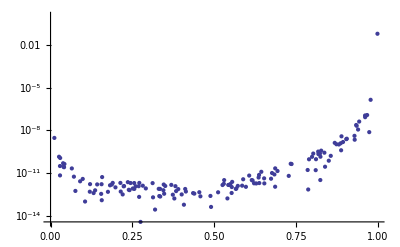

```mathematica
Module[{tP,etP,norm,fϵ,xs,exs,t1s,et1s,l,el,err},
tP={μ2-> m2,m2-> 1,s-> 5,q2-> -50};
(* prepare function *)
norm={zeta2-> Zeta[2],ln[z_]:> Log[z],Li2[z_]:> PolyLog[2,z],χ-> (1-β)/(1+β),β-> Sqrt[1-ρ],ρ-> 4m2/s,χq-> (βq-1)/(βq+1),βq-> Sqrt[1-ρq],ρq-> 4m2/q2,sp-> -t1-u1,u1-> q2-s-t1};
fϵ=Coefficient[virtualRes[G]["box1"]//.norm,ϵ,{-1,0}];
(* prepare data *)
etP=(First@#->(Rationalize[Last@#/.tP,0]))&/@tP;
AppendTo[etP,sp-> s-q2];
AppendTo[etP,β-> Sqrt[1-4m2/s]];
etP=(First@#->(Last@#/.etP))&/@etP;
tP=(First@#->N@(Last@#))&/@etP;
xs=RandomReal[{0,1},150];
exs=Rationalize[#,0]&/@xs;
t1s=((-sp/2(1+β(1-2#)))/.tP)&/@xs;
et1s=((-sp/2(1+β(1-2#)))/.etP)&/@exs;
(* compute *)
l=Re@N[fϵ/.Join[tP,{t1-> t1s}]];
el=N[fϵ/.Join[etP,{t1-> et1s}],20];
err=N[Abs[(l-el)/el]];
Print@ListLogPlot[Transpose[{xs,Last@err}]];
]
```

### Vertex corrections

```mathematica
virtualRes[G]["e"]=getVirtual[G][meNLOV["e"],meNLOVDens["e"],"~/Physik/PhD/MMa/data/Virt/repE.m"];
```

DiracTr[(GI √m2+Gs[p1]).Ga[ν].(GI √m2+Gs[-k1+p1])/u1.Ga[$1713].(GI √m2+Gs[l-p2+q]).Ga[μ].(GI √m2+Gs[l-p2]).Ga[$1714].(-GI Eta[$1713,$1714]).(-GI √m2+Gs[p2]).Ga[νp].(GI √m2+Gs[k1-p2])/t1.Ga[μp]] Eta[μ,μp] Eta[ν,νp]

1/(t1 u1)2 (64 m2^3+16 m2^2 (t1+2 u1+q2 (-2+ϵ))+2 (2+ϵ) (2 (q2-t1-u1) (q2^2-(q2+t1) u1)+t1 (q2-u1) u1 ϵ)-2 m2 (8 q2^2 (1+ϵ)-2 q2 (3 u1 ϵ+2 t1 (1+ϵ))+u1 (t1 (-6+ϵ) (2+ϵ)+u1 (-8+ϵ^2)))+4 (2+ϵ) (4 m2+(q2-t1-u1) ϵ) SDot[k1,l]^2+8 t1 (2+ϵ) SDot[l,p1]^2-64 m2^2 SDot[l,p2]+16 q2^2 SDot[l,p2]+24 m2 t1 SDot[l,p2]-16 q2 t1 SDot[l,p2]+8 m2 u1 SDot[l,p2]-16 q2 u1 SDot[l,p2]+8 t1 u1 SDot[l,p2]-16 m2^2 ϵ SDot[l,p2]-16 m2 q2 ϵ SDot[l,p2]+12 q2^2 ϵ SDot[l,p2]-4 m2 t1 ϵ SDot[l,p2]-12 q2 t1 ϵ SDot[l,p2]-4 m2 u1 ϵ SDot[l,p2]-12 q2 u1 ϵ SDot[l,p2]+4 t1 u1 ϵ SDot[l,p2]-4 m2 q2 ϵ^2 SDot[l,p2]+2 q2^2 ϵ^2 SDot[l,p2]-2 q2 t1 ϵ^2 SDot[l,p2]+4 m2 u1 ϵ^2 SDot[l,p2]-6 q2 u1 ϵ^2 SDot[l,p2]+10 t1 u1 ϵ^2 SDot[l,p2]+2 u1^2 ϵ^2 SDot[l,p2]+t1 u1 ϵ^3 SDot[l,p2]-u1^2 ϵ^3 SDot[l,p2]+16 u1 SDot[l,p2]^2+8 u1 ϵ SDot[l,p2]^2+2 SDot[l,p1] (-8 m2^2 ϵ+q2^2 (-4+ϵ) (2+ϵ)+q2 (8 u1+2 (t1+u1) ϵ-(t1+u1) ϵ^2)+2 t1 (4 u1+t1 (2+ϵ))+2 m2 (-t1 (-6+ϵ)+u1 (-2+ϵ) (-1+ϵ)+q2 (8-(-4+ϵ) ϵ))+4 (4 m2-2 q2+t1+u1) (2+ϵ) SDot[l,p2])+SDot[k1,l] (-8 t1 (-q2+t1+u1)+4 (q2-t1) (q2+t1-u1) ϵ-2 (q2^2+u1^2-q2 (t1+2 u1)) ϵ^2+u1 (-q2+u1) ϵ^3+16 m2^2 (4+ϵ)+4 m2 (q2 (-2+ϵ)^2-t1 (10+ϵ)-u1 (6+ϵ (3+2 ϵ)))+4 (2+ϵ) ((-4 m2+2 q2-2 (t1+u1)+t1 ϵ) SDot[l,p1]+(-4 m2+2 q2-2 (t1+u1)+u1 ϵ) SDot[l,p2]))+32 m2^2 SDot[l,q]-16 m2 q2 SDot[l,q]+8 m2 t1 SDot[l,q]+8 m2 u1 SDot[l,q]+16 m2^2 ϵ SDot[l,q]-4 q2^2 ϵ SDot[l,q]+4 m2 t1 ϵ SDot[l,q]+4 q2 t1 ϵ SDot[l,q]+4 m2 u1 ϵ SDot[l,q]+4 q2 u1 ϵ SDot[l,q]+4 m2 q2 ϵ^2 SDot[l,q]-2 q2^2 ϵ^2 SDot[l,q]+2 q2 t1 ϵ^2 SDot[l,q]+2 q2 u1 ϵ^2 SDot[l,q]-2 t1 u1 ϵ^2 SDot[l,q]-t1 u1 ϵ^3 SDot[l,q]+(2+ϵ) (4 m2 (4 m2-2 q2+t1+u1)+2 q2 (2 m2-q2+t1+u1) ϵ-t1 u1 ϵ^2) Sqr[l])

Div: (8 Div (4 m2^2+m2 (t1+u1)+q2 (-q2+t1+u1)))/(t1 u1)+(4 Div (4 m2^2-3 q2^2-t1 u1+3 q2 (t1+u1)+m2 (4 q2+t1+u1)) ϵ)/(t1 u1)+(Div (8 m2 q2-4 q2^2-6 t1 u1+4 q2 (t1+u1)) ϵ^2)/(t1 u1)-2 Div ϵ^3

DiracTr[(GI √m2+Gs[p1]).Ga[ν].(GI √m2+Gs[-k1+p1])/u1.Ga[$1792].(GI √m2+Gs[l-p2+q]).Ga[μ].(GI √m2+Gs[l-p2]).Ga[$1793].(-GI Eta[$1792,$1793]).(-GI √m2+Gs[p2]).Ga[μp].(GI √m2+Gs[-k1+p1])/u1.Ga[νp]] Eta[μ,μp] Eta[ν,νp]

1/u1^2 2 (64 m2^3-8 m2 (2 q2^2-2 q2 u1+u1^2)-4 m2 (2 q2^2-3 q2 u1+u1 (t1+3 u1)) ϵ-2 m2 u1 (t1+u1) ϵ^2+2 t1 (q2-u1) u1 (2+ϵ)^2+16 m2^2 (3 u1+q2 ϵ)-64 m2^2 SDot[l,p2]-32 m2 q2 SDot[l,p2]-32 m2 u1 SDot[l,p2]+16 t1 u1 SDot[l,p2]-16 m2^2 ϵ SDot[l,p2]-24 m2 q2 ϵ SDot[l,p2]+20 t1 u1 ϵ SDot[l,p2]-4 u1^2 ϵ SDot[l,p2]-4 m2 q2 ϵ^2 SDot[l,p2]+4 m2 u1 ϵ^2 SDot[l,p2]+8 t1 u1 ϵ^2 SDot[l,p2]-4 u1^2 ϵ^2 SDot[l,p2]+t1 u1 ϵ^3 SDot[l,p2]-u1^2 ϵ^3 SDot[l,p2]+(4 m2-u1 (2+ϵ)) SDot[k1,l] (4 m2 ϵ+q2 (-4+ϵ) (2+ϵ)-u1 (-4+ϵ) (2+ϵ)-8 (2+ϵ) SDot[l,p2])-4 m2 SDot[l,p1] (4 m2 ϵ+q2 (-4+ϵ) (2+ϵ)-u1 (-4+ϵ) (2+ϵ)-8 (2+ϵ) SDot[l,p2])+32 m2^2 SDot[l,q]+16 m2 u1 SDot[l,q]+16 m2^2 ϵ SDot[l,q]+8 m2 q2 ϵ SDot[l,q]+8 m2 u1 ϵ SDot[l,q]-4 t1 u1 ϵ SDot[l,q]+4 m2 q2 ϵ^2 SDot[l,q]-4 t1 u1 ϵ^2 SDot[l,q]-t1 u1 ϵ^3 SDot[l,q]+(2+ϵ) (16 m2^2-t1 u1 ϵ (2+ϵ)+4 m2 (2 u1+q2 ϵ)) Sqr[l])

Div: (8 Div (4 m2^2-t1 u1+2 m2 (q2+u1)))/u1^2+(8 Div (2 m2^2-2 t1 u1+m2 (3 q2+u1)) ϵ)/u1^2+(2 Div (4 m2 q2-5 t1 u1) ϵ^2)/u1^2-(2 Div t1 ϵ^3)/u1

```mathematica
virtualRes[L]["e"]=getVirtual[L][meNLOV["e"],meNLOVDens["e"],"~/Physik/PhD/MMa/data/Virt/repE.m"];
```

(4 q2 DiracTr[(GI √m2+Gs[p1]).Ga[ν].(GI √m2+Gs[-k1+p1])/u1.Ga[$1839].(GI √m2+Gs[l-p2+q]).Ga[μ].(GI √m2+Gs[l-p2]).Ga[$1840].(-GI Eta[$1839,$1840]).(-GI √m2+Gs[p2]).Ga[νp].(GI √m2+Gs[k1-p2])/t1.Ga[μp]] Eta[ν,νp] k1[μ] k1[μp])/sp^2

-1/(t1 u1 (t1+u1)^2)16 q2 (2 (2 m2 (q2-t1)-(q2-u1) (q2-t1-u1)) (2+ϵ) SDot[k1,l]^2+t1 (2 m2-q2+u1) (2 t1-u1 ϵ) SDot[l,p1]+2 SDot[k1,l] (4 m2^2 (-t1+u1)+(q2-u1) (q2-t1-u1) (-t1+u1)+2 m2 (-t1^2+2 q2 (t1-u1)+t1 u1+u1^2)+m2 (t1-u1) u1 ϵ+(2+ϵ) (t1 (2 m2-q2+u1) SDot[l,p1]+u1 (2 m2-q2+2 t1+u1) SDot[l,p2]))+u1 (2 t1 ((2 m2-q2) (2 m2-q2+t1)+(3 m2-2 q2+t1) u1+u1^2)-(2 (t1 (4 m2-2 q2+t1)+(2 m2-q2+3 t1) u1+u1^2)+t1 (2 m2-q2+t1+2 u1) ϵ) SDot[l,p2]+t1 (2 m2-q2+t1+u1) (2+ϵ) (SDot[l,q]+Sqr[l])))

Div: -(16 Div q2 (2 m2-q2+t1+u1))/(t1+u1)^2-(8 Div q2 (2 m2-q2+t1+u1) ϵ)/(t1+u1)^2

(4 q2 DiracTr[(GI √m2+Gs[p1]).Ga[ν].(GI √m2+Gs[-k1+p1])/u1.Ga[$1866].(GI √m2+Gs[l-p2+q]).Ga[μ].(GI √m2+Gs[l-p2]).Ga[$1867].(-GI Eta[$1866,$1867]).(-GI √m2+Gs[p2]).Ga[μp].(GI √m2+Gs[-k1+p1])/u1.Ga[νp]] Eta[ν,νp] k1[μ] k1[μp])/sp^2

-1/(u1^2 (t1+u1)^2)32 m2 q2 (2 (q2-t1) (2+ϵ) SDot[k1,l]^2+t1 (2 t1-u1 ϵ) SDot[l,p1]+SDot[k1,l] (-2 (2 m2 t1-q2 t1+t1^2-2 m2 u1+q2 u1)+(t1-u1) u1 ϵ+2 t1 (2+ϵ) SDot[l,p1]+2 u1 (2+ϵ) SDot[l,p2])+u1 (t1 (4 m2-2 q2+t1+2 u1)-(2 u1+t1 (4+ϵ)) SDot[l,p2]+t1 (2+ϵ) (SDot[l,q]+Sqr[l])))

Div: -(32 Div m2 q2 t1)/(u1 (t1+u1)^2)-(16 Div m2 q2 t1 ϵ)/(u1 (t1+u1)^2)

```mathematica
virtualRes[P]["e"]=getVirtual[P][meNLOV["e"],meNLOVDens["e"],"~/Physik/PhD/MMa/data/Virt/repE.m"];
```

-1/sp^2 2 DiracTr[(GI √m2+Gs[p1]).Ga[ν].(GI √m2+Gs[-k1+p1])/u1.Ga[$1895].(GI √m2+Gs[l-p2+q]).Ga[μ].(GI √m2+Gs[l-p2]).Ga[$1896].(-GI Eta[$1895,$1896]).(-GI √m2+Gs[p2]).Ga[νp].(GI √m2+Gs[k1-p2])/t1.Ga[μp]] Eps[μ,μp,$1897,$1898] Eps[ν,νp,$1899,$1900] k1[$1898] k1[$1899] q[$1897] q[$1900]

1/(t1 u1 (t1+u1)^2)4 (2 (m2 (t1+u1)^2+t1 u1 (-q2+t1+u1)) (t1 (-q2+u1)+2 m2 (t1+2 u1))+2 t1 (-4 m2 q2+q2^2+t1^2+t1 u1+u1^2-2 q2 (t1+u1)) (2+ϵ) SDot[k1,l]^2-2 (2 m2 (t1+u1)^2+t1 (-t1^2+u1 (-2 q2+u1))) (2+ϵ) SDot[l,p1]^2+16 m2^2 t1^2 SDot[l,p2]+8 m2 q2 t1^2 SDot[l,p2]-4 m2 t1^3 SDot[l,p2]+32 m2^2 t1 u1 SDot[l,p2]-8 q2^2 t1 u1 SDot[l,p2]+8 q2 t1^2 u1 SDot[l,p2]+16 m2^2 u1^2 SDot[l,p2]+8 m2 q2 u1^2 SDot[l,p2]-4 m2 t1 u1^2 SDot[l,p2]+10 q2 t1 u1^2 SDot[l,p2]-2 t1^2 u1^2 SDot[l,p2]-8 m2 u1^3 SDot[l,p2]-2 q2 u1^3 SDot[l,p2]+2 u1^4 SDot[l,p2]+m2 t1^3 ϵ SDot[l,p2]+m2 t1^2 u1 ϵ SDot[l,p2]-q2 t1^2 u1 ϵ SDot[l,p2]+t1^3 u1 ϵ SDot[l,p2]-m2 t1 u1^2 ϵ SDot[l,p2]+q2 t1 u1^2 ϵ SDot[l,p2]-m2 u1^3 ϵ SDot[l,p2]-t1 u1^3 ϵ SDot[l,p2]+8 m2 t1^2 SDot[l,p2]^2+16 m2 t1 u1 SDot[l,p2]^2-8 q2 t1 u1 SDot[l,p2]^2+4 t1^2 u1 SDot[l,p2]^2+8 m2 u1^2 SDot[l,p2]^2-4 u1^3 SDot[l,p2]^2+4 m2 t1^2 ϵ SDot[l,p2]^2+8 m2 t1 u1 ϵ SDot[l,p2]^2-4 q2 t1 u1 ϵ SDot[l,p2]^2+2 t1^2 u1 ϵ SDot[l,p2]^2+4 m2 u1^2 ϵ SDot[l,p2]^2-2 u1^3 ϵ SDot[l,p2]^2-16 m2^2 t1^2 SDot[l,q]-8 m2 q2 t1^2 SDot[l,q]-32 m2^2 t1 u1 SDot[l,q]+8 q2^2 t1 u1 SDot[l,q]-8 m2 t1^2 u1 SDot[l,q]-4 q2 t1^2 u1 SDot[l,q]-4 t1^3 u1 SDot[l,q]-16 m2^2 u1^2 SDot[l,q]-8 m2 q2 u1^2 SDot[l,q]-4 m2 t1 u1^2 SDot[l,q]-12 q2 t1 u1^2 SDot[l,q]+4 m2 u1^3 SDot[l,q]+4 t1 u1^3 SDot[l,q]-m2 t1^3 ϵ SDot[l,q]+m2 t1^2 u1 ϵ SDot[l,q]+q2 t1^2 u1 ϵ SDot[l,q]-t1^3 u1 ϵ SDot[l,q]+5 m2 t1 u1^2 ϵ SDot[l,q]-3 q2 t1 u1^2 ϵ SDot[l,q]+t1^2 u1^2 ϵ SDot[l,q]+3 m2 u1^3 ϵ SDot[l,q]+2 t1 u1^3 ϵ SDot[l,q]-8 m2 t1^2 SDot[l,p2] SDot[l,q]-16 m2 t1 u1 SDot[l,p2] SDot[l,q]+8 q2 t1 u1 SDot[l,p2] SDot[l,q]-8 m2 u1^2 SDot[l,p2] SDot[l,q]-4 m2 t1^2 ϵ SDot[l,p2] SDot[l,q]-8 m2 t1 u1 ϵ SDot[l,p2] SDot[l,q]+4 q2 t1 u1 ϵ SDot[l,p2] SDot[l,q]-4 m2 u1^2 ϵ SDot[l,p2] SDot[l,q]-4 t1^2 u1 SDot[l,q]^2-2 t1^2 u1 ϵ SDot[l,q]^2+SDot[l,p1] (16 m2^2 (t1+u1)^2+4 m2 (t1 (t1+u1) (t1+5 u1)+2 q2 (t1^2+u1^2))+m2 (t1-3 u1) (t1+u1)^2 ϵ+t1 u1 (-8 q2^2+2 (t1+u1) (-u1 (1+ϵ)+t1 (3+ϵ))+q2 (-t1 (-2+ϵ)+u1 (10+3 ϵ)))+2 (2 m2 (t1+u1)^2+t1 u1 (-2 q2+t1+u1)) (2+ϵ) SDot[l,q])-SDot[k1,l] (2 (8 m2^2 (t1+u1)^2+u1 (-q2+t1+u1) (t1 (5 q2+3 t1)-(q2+2 t1) u1+u1^2)+2 m2 ((t1+u1) (t1^2+4 t1 u1-2 u1^2)+q2 (2 t1^2-t1 u1+3 u1^2)))+(m2 (t1-u1) (t1+u1)^2+t1 u1 (2 q2 (-t1+u1)+(2 t1-u1) (t1+u1))) ϵ+2 (2+ϵ) (-(2 m2 (t1+u1)^2+t1 (2 (q2-t1) t1-(2 q2+t1) u1+u1^2)) SDot[l,p1]+(2 m2 (t1+u1)^2+u1 (q2 (-5 t1+u1)+(3 t1-u1) (t1+u1))) SDot[l,p2]+2 t1 (t1 u1+2 m2 (t1+u1)) SDot[l,q]))-(t1-u1) (m2 (t1+u1)^2+t1 u1 (-q2+t1+u1)) (2+ϵ) Sqr[l])

Div: 4 Div (1+m2 (1/t1+1/u1)-q2/(t1+u1))+2 Div (1+m2 (1/t1+1/u1)-q2/(t1+u1)) ϵ

-1/sp^2 2 DiracTr[(GI √m2+Gs[p1]).Ga[ν].(GI √m2+Gs[-k1+p1])/u1.Ga[$2023].(GI √m2+Gs[l-p2+q]).Ga[μ].(GI √m2+Gs[l-p2]).Ga[$2024].(-GI Eta[$2023,$2024]).(-GI √m2+Gs[p2]).Ga[μp].(GI √m2+Gs[-k1+p1])/u1.Ga[νp]] Eps[μ,μp,$2025,$2026] Eps[ν,νp,$2027,$2028] k1[$2026] k1[$2027] q[$2025] q[$2028]

1/(u1^2 (t1+u1)^2)4 (2 (2 m2^2 (t1+u1)^2 (2 t1+u1)-m2 (2 q2 t1^3+(7 q2-4 t1) t1^2 u1+(2 q2-5 t1) t1 u1^2-q2 u1^3+u1^4)-t1 u1 (q2^2 (-2 t1+u1)+u1^2 (t1+u1)+q2 (t1^2-2 u1^2)))-2 (-q2^2 u1+u1^3+m2 (4 q2 t1-2 (t1+u1)^2)) (2+ϵ) SDot[k1,l]^2-(2 m2 (t1+u1)^2+u1 (-2 q2 t1+t1^2-u1^2)) (2 t1-u1 ϵ) SDot[l,p2]-(t1+u1) (4 m2 (t1^2+3 t1 u1+u1^2)+u1 (2 t1^2-2 u1^2+2 q2 (-2 t1+u1)+t1 u1 ϵ)) SDot[l,q]+2 t1 u1^2 (2+ϵ) SDot[l,q]^2+2 (t1+u1) SDot[l,p1] (2 m2 (t1+u1) (2 t1+u1)-u1 (q2 (t1-u1)+u1 (t1+u1))-t1 u1 (2+ϵ) SDot[l,q])-SDot[k1,l] (2 u1 (q2^2 (-5 t1+u1)-2 t1 u1 (t1+u1)+q2 (2 t1^2+3 t1 u1-u1^2))+4 m2 (t1 (t1+u1) (2 t1+u1)+q2 (t1^2+5 t1 u1+2 u1^2))+u1 (t1+u1) ((q2-u1) u1+2 m2 (t1+u1)) ϵ+2 (2+ϵ) ((t1+u1) ((q2-u1) u1+2 m2 (t1+u1)) SDot[l,p1]+(2 m2 (t1+u1)^2+u1 (-2 q2 t1+t1^2-u1^2)) SDot[l,p2]+(2 m2 t1^2-q2 t1 u1-(2 m2+q2+t1) u1^2+u1^3) SDot[l,q])))

Div: (4 Div t1 (2 m2 (t1+u1)^2+u1 (-2 q2 t1+t1^2-u1^2)))/(u1^2 (t1+u1)^2)+(2 Div t1 (2 m2 (t1+u1)^2+u1 (-2 q2 t1+t1^2-u1^2)) ϵ)/(u1^2 (t1+u1)^2)

```mathematica
virtualRes[G]["g1"]=getVirtual[G][meNLOV["g1"],meNLOVDens["g1"],"~/Physik/PhD/MMa/data/Virt/repG1.m"];
```

DiracTr[(GI √m2+Gs[p1]).Ga[$24264].(GI √m2+Gs[l+p1]).Ga[ν].(GI √m2+Gs[-k1+l+p1]).Ga[$24265].(GI √m2+Gs[-p2+q])/u1.Ga[μ].(-GI Eta[$24264,$24265]).(-GI √m2+Gs[p2]).Ga[νp].(GI √m2+Gs[k1-p2])/t1.Ga[μp]] Eta[μ,μp] Eta[ν,νp]

1/(t1 u1)2 (64 m2^3+16 m2^2 (t1+2 u1+q2 ϵ)-2 t1 u1 (2+ϵ) (2 q2-2 (t1+u1)+u1 ϵ)+2 m2 (-4 q2^2 (2+ϵ)+u1 (12 t1+8 u1+4 t1 ϵ-(t1+u1) ϵ^2)+2 q2 (u1 ϵ+2 t1 (2+ϵ)))-32 m2^2 SDot[l,p2]-32 m2 q2 SDot[l,p2]-8 q2^2 SDot[l,p2]+16 q2 t1 SDot[l,p2]-8 t1^2 SDot[l,p2]+8 m2 u1 SDot[l,p2]+8 q2 u1 SDot[l,p2]-16 t1 u1 SDot[l,p2]+16 m2^2 ϵ SDot[l,p2]-8 m2 q2 ϵ SDot[l,p2]-8 q2^2 ϵ SDot[l,p2]+12 q2 t1 ϵ SDot[l,p2]-4 t1^2 ϵ SDot[l,p2]+24 m2 u1 ϵ SDot[l,p2]+8 q2 u1 ϵ SDot[l,p2]-4 t1 u1 ϵ SDot[l,p2]+4 m2 q2 ϵ^2 SDot[l,p2]-2 q2^2 ϵ^2 SDot[l,p2]+2 q2 t1 ϵ^2 SDot[l,p2]+4 m2 u1 ϵ^2 SDot[l,p2]+2 q2 u1 ϵ^2 SDot[l,p2]+2 t1 u1 ϵ^2 SDot[l,p2]+2 u1^2 ϵ^2 SDot[l,p2]-t1 u1 ϵ^3 SDot[l,p2]-u1^2 ϵ^3 SDot[l,p2]-32 m2 SDot[l,p2]^2-16 q2 SDot[l,p2]^2+16 t1 SDot[l,p2]^2-16 u1 SDot[l,p2]^2-16 m2 ϵ SDot[l,p2]^2-16 q2 ϵ SDot[l,p2]^2+16 t1 ϵ SDot[l,p2]^2-8 u1 ϵ SDot[l,p2]^2-4 q2 ϵ^2 SDot[l,p2]^2+4 t1 ϵ^2 SDot[l,p2]^2-32 m2^2 SDot[l,q]+8 q2^2 SDot[l,q]+16 m2 t1 SDot[l,q]-16 q2 t1 SDot[l,q]+8 t1^2 SDot[l,q]+8 m2 u1 SDot[l,q]-8 q2 u1 SDot[l,q]+8 t1 u1 SDot[l,q]-16 m2^2 ϵ SDot[l,q]-8 m2 q2 ϵ SDot[l,q]+8 q2^2 ϵ SDot[l,q]+8 m2 t1 ϵ SDot[l,q]-12 q2 t1 ϵ SDot[l,q]+4 t1^2 ϵ SDot[l,q]-8 q2 u1 ϵ SDot[l,q]-4 m2 q2 ϵ^2 SDot[l,q]+2 q2^2 ϵ^2 SDot[l,q]-2 q2 t1 ϵ^2 SDot[l,q]-2 q2 u1 ϵ^2 SDot[l,q]-2 t1 u1 ϵ^2 SDot[l,q]+t1 u1 ϵ^3 SDot[l,q]+32 m2 SDot[l,p2] SDot[l,q]+16 q2 SDot[l,p2] SDot[l,q]-16 t1 SDot[l,p2] SDot[l,q]+16 m2 ϵ SDot[l,p2] SDot[l,q]+16 q2 ϵ SDot[l,p2] SDot[l,q]-16 t1 ϵ SDot[l,p2] SDot[l,q]-8 u1 ϵ SDot[l,p2] SDot[l,q]+4 q2 ϵ^2 SDot[l,p2] SDot[l,q]-4 t1 ϵ^2 SDot[l,p2] SDot[l,q]-4 u1 ϵ^2 SDot[l,p2] SDot[l,q]+2 SDot[l,p1] (8 m2^2 (2+ϵ)-q2^2 (2+ϵ)^2-t1 u1 (4+ϵ (2+ϵ)^2)+q2 (2+ϵ) (u1 (2+ϵ)+t1 (4+ϵ))+2 m2 (q2 ϵ (2+ϵ)+u1 (2+ϵ (4+ϵ)))+2 (2+ϵ) ((4 m2+2 (q2+t1-u1)+(q2+t1) ϵ) SDot[l,p2]-t1 (2+ϵ) SDot[l,q]))-SDot[k1,l] (8 (q2 (-q2+t1+u1)+m2 (-2 q2+4 t1+3 u1))+4 (4 m2^2-2 q2^2+4 m2 u1-t1 u1+2 q2 (t1+u1)) ϵ+2 (q2 (2 m2-q2+t1)+4 m2 u1+u1^2) ϵ^2+(q2-2 t1-u1) u1 ϵ^3+8 (q2-u1) (2+ϵ) SDot[l,p1]+4 (2+ϵ) (-(4 m2+2 u1+q2 ϵ-t1 ϵ) SDot[l,p2]+(4 m2+(q2-t1-u1) ϵ) SDot[l,q]))+(2+ϵ) (16 m2^2-t1 u1 ϵ^2-2 q2^2 (2+ϵ)+2 q2 (t1+u1) (2+ϵ)+4 m2 (t1+u1+q2 ϵ)) Sqr[l])

Loop-Minkowski: 1

(1 | (16 (8 m2^3+t1 u1 (-q2+t1+u1)+2 m2^2 (t1+2 u1)+m2 (-2 q2^2+2 q2 t1+u1 (3 t1+2 u1))))/(t1 u1)+((16 m2 q2 (2 m2-q2+t1)+8 (t1 (-q2+t1)+m2 (q2+2 t1)) u1) ϵ)/(t1 u1)-(4 (t1 u1+m2 (t1+u1)) ϵ^2)/t1 | (16 (8 m2^3+t1 u1 (t1+u1)+2 m2^2 (t1+2 u1)+m2 u1 (3 t1+2 u1)))/(t1 u1)+8 (2 m2+t1) ϵ-(4 (t1 u1+m2 (t1+u1)) ϵ^2)/t1)

Loop-Minkowski: l[$24484]

p1[$24484]

(-(16 (q2 (-q2+t1+u1)+m2 (-2 q2+4 t1+3 u1)))/(t1 u1)-(8 (4 m2^2-2 q2^2+4 m2 u1-t1 u1+2 q2 (t1+u1)) ϵ)/(t1 u1)-(4 (q2 (2 m2-q2+t1)+4 m2 u1+u1^2) ϵ^2)/(t1 u1)+(2 (-q2+2 t1+u1) ϵ^3)/t1) k1[$24484]+((16 (4 m2^2-q2^2+2 q2 t1+(m2+q2-t1) u1))/(t1 u1)+(8 (4 m2^2+2 m2 q2-2 q2^2+3 q2 t1+2 (2 m2+q2-t1) u1) ϵ)/(t1 u1)+(4 (-q2^2-4 t1 u1+2 m2 (q2+u1)+q2 (t1+u1)) ϵ^2)/(t1 u1)-4 ϵ^3) p1[$24484]+((16 (-(2 m2+q2)^2+2 q2 t1-t1^2+(m2+q2-2 t1) u1))/(t1 u1)-(8 (-4 m2^2+2 m2 (q2-3 u1)+(2 q2-t1) (q2-t1-u1)) ϵ)/(t1 u1)+(4 (-q2^2+2 m2 (q2+u1)+q2 (t1+u1)+u1 (t1+u1)) ϵ^2)/(t1 u1)-(2 (t1+u1) ϵ^3)/t1) p2[$24484]+((16 (-4 m2^2+(q2-t1) (q2-t1-u1)+m2 (2 t1+u1)))/(t1 u1)+(8 (-4 m2^2+2 q2^2-3 q2 t1+t1^2+2 m2 (-q2+t1)-2 q2 u1) ϵ)/(t1 u1)-(4 (q2 (2 m2-q2+t1)+(q2+t1) u1) ϵ^2)/(t1 u1)+2 ϵ^3) q[$24484]

1/(t1 u1)2 (64 m2^3+2 t1 u1 (2+ϵ) (-2 q2+2 t1+2 u1-u1 ϵ)+8 m2^2 (4 t1+2 u1+2 q2 ϵ-u1 ϵ)+m2 (-8 q2^2 (2+ϵ)+2 q2 (6 t1 (2+ϵ)+u1 (8+8 ϵ+ϵ^2))+u1 (u1 (8-4 ϵ+ϵ^3)-t1 (-16+16 ϵ+12 ϵ^2+ϵ^3))))

(k1[$24484] | -(16 (q2 (-q2+t1+u1)+m2 (-2 q2+4 t1+3 u1)))/(t1 u1)-(8 (4 m2^2-2 q2^2+4 m2 u1-t1 u1+2 q2 (t1+u1)) ϵ)/(t1 u1)-(4 (q2 (2 m2-q2+t1)+4 m2 u1+u1^2) ϵ^2)/(t1 u1)+(2 (-q2+2 t1+u1) ϵ^3)/t1 | m2 (-48/t1-64/u1)+(8 (-4 m2^2-4 m2 u1+t1 u1) ϵ)/(t1 u1)-(4 (4 m2+u1) ϵ^2)/t1+(4+(2 u1)/t1) ϵ^3
p1[$24484] | (16 (4 m2^2-q2^2+2 q2 t1+(m2+q2-t1) u1))/(t1 u1)+(8 (4 m2^2+2 m2 q2-2 q2^2+3 q2 t1+2 (2 m2+q2-t1) u1) ϵ)/(t1 u1)+(4 (-q2^2-4 t1 u1+2 m2 (q2+u1)+q2 (t1+u1)) ϵ^2)/(t1 u1)-4 ϵ^3 | (16 (4 m2^2+m2 u1-t1 u1))/(t1 u1)+(16 (2 m2^2+2 m2 u1-t1 u1) ϵ)/(t1 u1)+(-16+(8 m2)/t1) ϵ^2-4 ϵ^3
p2[$24484] | (16 (-(2 m2+q2)^2+2 q2 t1-t1^2+(m2+q2-2 t1) u1))/(t1 u1)-(8 (-4 m2^2+2 m2 (q2-3 u1)+(2 q2-t1) (q2-t1-u1)) ϵ)/(t1 u1)+(4 (-q2^2+2 m2 (q2+u1)+q2 (t1+u1)+u1 (t1+u1)) ϵ^2)/(t1 u1)-(2 (t1+u1) ϵ^3)/t1 | -(16 (4 m2^2-m2 u1+t1 (t1+2 u1)))/(t1 u1)+(8 (4 m2^2+6 m2 u1-t1 (t1+u1)) ϵ)/(t1 u1)+(4 (2 m2+t1+u1) ϵ^2)/t1-(2 (t1+u1) ϵ^3)/t1
q[$24484] | (16 (-4 m2^2+(q2-t1) (q2-t1-u1)+m2 (2 t1+u1)))/(t1 u1)+(8 (-4 m2^2+2 q2^2-3 q2 t1+t1^2+2 m2 (-q2+t1)-2 q2 u1) ϵ)/(t1 u1)-(4 (q2 (2 m2-q2+t1)+(q2+t1) u1) ϵ^2)/(t1 u1)+2 ϵ^3 | (16 (-4 m2^2+t1 (t1+u1)+m2 (2 t1+u1)))/(t1 u1)+(8 (-4 m2^2+2 m2 t1+t1^2) ϵ)/(t1 u1)-4 ϵ^2+2 ϵ^3)

Loop-Minkowski: l[$24485] l[$24486]

(k1[$24485] p1[$24486] | (32 (-q2+u1))/(t1 u1)+(16 (-q2+u1) ϵ)/(t1 u1) | 32/t1+(16 ϵ)/t1
k1[$24485] p2[$24486] | (32 (2 m2+u1))/(t1 u1)+(16 (2 m2+q2-t1+u1) ϵ)/(t1 u1)+(8 (q2-t1) ϵ^2)/(t1 u1) | (32 (2 m2+u1))/(t1 u1)+(16 (2 m2-t1+u1) ϵ)/(t1 u1)-(8 ϵ^2)/u1
p1[$24485] p2[$24486] | (32 (2 m2+q2+t1-u1))/(t1 u1)+((32 (m2+q2+t1)-16 u1) ϵ)/(t1 u1)+(8 (q2+t1) ϵ^2)/(t1 u1) | (32 (2 m2+t1-u1))/(t1 u1)+((32 (m2+t1)-16 u1) ϵ)/(t1 u1)+(8 ϵ^2)/u1
p2[$24485] p2[$24486] | -(32 (2 m2+q2-t1+u1))/(t1 u1)-(16 (2 (m2+q2-t1)+u1) ϵ)/(t1 u1)-(8 (q2-t1) ϵ^2)/(t1 u1) | -(32 (2 m2-t1+u1))/(t1 u1)-(16 (2 m2-2 t1+u1) ϵ)/(t1 u1)+(8 ϵ^2)/u1
k1[$24485] q[$24486] | -(64 m2)/(t1 u1)+(16 (-2 m2-q2+t1+u1) ϵ)/(t1 u1)+(8 (-q2+t1+u1) ϵ^2)/(t1 u1) | -(64 m2)/(t1 u1)+(16 (-2 m2+t1+u1) ϵ)/(t1 u1)+8 (1/t1+1/u1) ϵ^2
p1[$24485] q[$24486] | -32/u1-(32 ϵ)/u1-(8 ϵ^2)/u1 | -32/u1-(32 ϵ)/u1-(8 ϵ^2)/u1
p2[$24485] q[$24486] | (32 (2 m2+q2-t1))/(t1 u1)-(16 (-2 (m2+q2-t1)+u1) ϵ)/(t1 u1)-(8 (-q2+t1+u1) ϵ^2)/(t1 u1) | (64 m2-32 t1)/(t1 u1)-(16 (-2 m2+2 t1+u1) ϵ)/(t1 u1)-(8 (t1+u1) ϵ^2)/(t1 u1))

Loop-Minkowski: l[$24483]^2

(1 | (16 (4 m2^2+m2 (t1+u1)+q2 (-q2+t1+u1)))/(t1 u1)+(8 (4 m2^2+2 q2 (-q2+t1+u1)+m2 (2 q2+t1+u1)) ϵ)/(t1 u1)+((8 m2 q2-4 (q2-t1) (q2-u1)) ϵ^2)/(t1 u1)-2 ϵ^3 | (16 m2 (4 m2+t1+u1))/(t1 u1)+(8 m2 (4 m2+t1+u1) ϵ)/(t1 u1)-4 ϵ^2-2 ϵ^3)

Div: (8 Div (4 m2^2+m2 (t1+u1)+q2 (-q2+t1+u1)))/(t1 u1)+(4 Div (4 m2^2-2 q2^2-t1 u1+2 q2 (t1+u1)+m2 (2 q2+t1+u1)) ϵ)/(t1 u1)+(2 Div (q2 (2 m2-q2+t1)+(q2-3 t1) u1) ϵ^2)/(t1 u1)-2 Div ϵ^3

DiracTr[(GI √m2+Gs[p1]).Ga[$24598].(GI √m2+Gs[l+p1]).Ga[ν].(GI √m2+Gs[-k1+l+p1]).Ga[$24599].(GI √m2+Gs[-p2+q])/u1.Ga[μ].(-GI Eta[$24598,$24599]).(-GI √m2+Gs[p2]).Ga[μp].(GI √m2+Gs[-k1+p1])/u1.Ga[νp]] Eta[μ,μp] Eta[ν,νp]

1/u1^2 2 (64 m2^3-2 t1 u1^2 (2+ϵ)^2+16 m2^2 (3 u1+q2 (2+ϵ))-2 m2 u1 (-2 q2 (2+ϵ)+t1 ϵ (2+ϵ)+u1 (4+ϵ (6+ϵ)))-4 (2+ϵ) (4 m2+(q2-u1) (2+ϵ)) SDot[l,p1]^2+SDot[k1,l] (-16 m2^2 (4+ϵ)-4 m2 (-3 t1 (2+ϵ)+q2 (2+ϵ) (4+ϵ)+u1 ϵ (3+2 ϵ))+u1 (q2 (8+8 ϵ-ϵ^3)+(2+ϵ) (2 t1 ϵ^2+u1 (-4+(-2+ϵ) ϵ)))+4 (2+ϵ) (4 m2+(q2-u1) (2+ϵ)) SDot[l,p1])+32 m2^2 SDot[l,p2]+16 m2 q2 SDot[l,p2]-24 m2 t1 SDot[l,p2]+16 m2 u1 SDot[l,p2]+8 q2 u1 SDot[l,p2]+8 u1^2 SDot[l,p2]+16 m2^2 ϵ SDot[l,p2]+16 m2 q2 ϵ SDot[l,p2]-12 m2 t1 ϵ SDot[l,p2]+12 m2 u1 ϵ SDot[l,p2]+4 q2 u1 ϵ SDot[l,p2]+4 t1 u1 ϵ SDot[l,p2]+8 u1^2 ϵ SDot[l,p2]+4 m2 q2 ϵ^2 SDot[l,p2]+4 m2 u1 ϵ^2 SDot[l,p2]-t1 u1 ϵ^3 SDot[l,p2]-u1^2 ϵ^3 SDot[l,p2]-32 m2^2 SDot[l,q]-16 m2 q2 SDot[l,q]+24 m2 t1 SDot[l,q]-16 m2 u1 SDot[l,q]-8 q2 u1 SDot[l,q]+8 u1^2 SDot[l,q]-16 m2^2 ϵ SDot[l,q]-16 m2 q2 ϵ SDot[l,q]+12 m2 t1 ϵ SDot[l,q]-4 m2 u1 ϵ SDot[l,q]-4 q2 u1 ϵ SDot[l,q]-4 t1 u1 ϵ SDot[l,q]+4 u1^2 ϵ SDot[l,q]-4 m2 q2 ϵ^2 SDot[l,q]+t1 u1 ϵ^3 SDot[l,q]+2 SDot[l,p1] (8 m2^2 (6+ϵ)+2 m2 (-3 t1 (2+ϵ)+q2 (2+ϵ) (6+ϵ)+u1 (4+ϵ+ϵ^2))-u1 (2+ϵ) (2 q2 (1+ϵ)-2 u1 (1+ϵ)+t1 (4+ϵ (2+ϵ)))+2 (2+ϵ) ((4 m2+(q2+u1) (2+ϵ)) SDot[l,p2]+(-4 m2-(q2-u1) (2+ϵ)) SDot[l,q]))+(2+ϵ) (16 m2^2+8 m2 (q2+u1)+4 m2 q2 ϵ-t1 u1 ϵ (2+ϵ)) Sqr[l])

Loop-Minkowski: 1

(1 | (16 (4 m2^2 (2 m2+q2)+m2 (6 m2+q2) u1-(m2+t1) u1^2))/u1^2+(8 (4 m2^2 q2+m2 (q2-t1-3 u1) u1-2 t1 u1^2) ϵ)/u1^2-(4 (t1 u1+m2 (t1+u1)) ϵ^2)/u1 | (16 (8 m2^3+6 m2^2 u1-(m2+t1) u1^2))/u1^2-(8 (2 t1 u1+m2 (t1+3 u1)) ϵ)/u1-(4 (t1 u1+m2 (t1+u1)) ϵ^2)/u1)

Loop-Minkowski: l[$24750]

p1[$24750]

(-(16 (m2 (8 m2+4 q2-3 t1)-q2 u1+u1^2))/u1^2-(8 (4 m2^2+2 u1 (-q2+u1)+3 m2 (2 q2-t1+u1)) ϵ)/u1^2+(8 (t1 u1-m2 (q2+2 u1)) ϵ^2)/u1^2+(2 (-q2+2 t1+u1) ϵ^3)/u1) k1[$24750]+((16 (12 m2^2+u1 (-q2-2 t1+u1)+m2 (6 q2-3 t1+2 u1)))/u1^2+(8 (4 m2^2+m2 (8 q2-3 t1+u1)+u1 (-3 q2-4 t1+3 u1)) ϵ)/u1^2+(8 (m2 (q2+u1)+u1 (-q2-2 t1+u1)) ϵ^2)/u1^2-(4 t1 ϵ^3)/u1) p1[$24750]+((16 (4 m2^2+u1 (q2+u1)+m2 (2 q2-3 t1+2 u1)))/u1^2+(8 (4 m2 (m2+q2)-3 m2 t1+(3 m2+q2+t1) u1+2 u1^2) ϵ)/u1^2+(8 m2 (q2+u1) ϵ^2)/u1^2-(2 (t1+u1) ϵ^3)/u1) p2[$24750]+(-(16 (4 m2^2+(q2-u1) u1+m2 (2 q2-3 t1+2 u1)))/u1^2+(8 (-4 m2 (m2+q2)+3 m2 t1-(m2+q2+t1) u1+u1^2) ϵ)/u1^2-(8 m2 q2 ϵ^2)/u1^2+(2 t1 ϵ^3)/u1) q[$24750]

1/u1^2 2 (64 m2^3-2 t1 u1^2 (2+ϵ)^2+8 m2^2 (-u1 (-2+ϵ)+2 q2 (2+ϵ))-m2 u1 (2+ϵ) (2 q2 (2+ϵ)-u1 (-4+4 ϵ+ϵ^2)+t1 (8+8 ϵ+ϵ^2)))

(k1[$24750] | -(16 (m2 (8 m2+4 q2-3 t1)-q2 u1+u1^2))/u1^2-(8 (4 m2^2+2 u1 (-q2+u1)+3 m2 (2 q2-t1+u1)) ϵ)/u1^2+(8 (t1 u1-m2 (q2+2 u1)) ϵ^2)/u1^2+(2 (-q2+2 t1+u1) ϵ^3)/u1 | -(16 (8 m2^2-3 m2 t1+u1^2))/u1^2-(8 (4 m2^2+2 u1^2+3 m2 (-t1+u1)) ϵ)/u1^2+(8 (-2 m2+t1) ϵ^2)/u1+(2+(4 t1)/u1) ϵ^3
p1[$24750] | (16 (12 m2^2+u1 (-q2-2 t1+u1)+m2 (6 q2-3 t1+2 u1)))/u1^2+(8 (4 m2^2+m2 (8 q2-3 t1+u1)+u1 (-3 q2-4 t1+3 u1)) ϵ)/u1^2+(8 (m2 (q2+u1)+u1 (-q2-2 t1+u1)) ϵ^2)/u1^2-(4 t1 ϵ^3)/u1 | (16 (12 m2^2-3 m2 t1+2 m2 u1-2 t1 u1+u1^2))/u1^2+(8 (4 m2^2+m2 (-3 t1+u1)+u1 (-4 t1+3 u1)) ϵ)/u1^2+(8 (m2-2 t1+u1) ϵ^2)/u1-(4 t1 ϵ^3)/u1
p2[$24750] | (16 (4 m2^2+u1 (q2+u1)+m2 (2 q2-3 t1+2 u1)))/u1^2+(8 (4 m2 (m2+q2)-3 m2 t1+(3 m2+q2+t1) u1+2 u1^2) ϵ)/u1^2+(8 m2 (q2+u1) ϵ^2)/u1^2-(2 (t1+u1) ϵ^3)/u1 | (16 (4 m2^2-3 m2 t1+2 m2 u1+u1^2))/u1^2+(8 (4 m2^2+3 m2 (-t1+u1)+u1 (t1+2 u1)) ϵ)/u1^2+(8 m2 ϵ^2)/u1-(2 (t1+u1) ϵ^3)/u1
q[$24750] | -(16 (4 m2^2+(q2-u1) u1+m2 (2 q2-3 t1+2 u1)))/u1^2+(8 (-4 m2 (m2+q2)+3 m2 t1-(m2+q2+t1) u1+u1^2) ϵ)/u1^2-(8 m2 q2 ϵ^2)/u1^2+(2 t1 ϵ^3)/u1 | (16 (-4 m2^2+3 m2 t1-2 m2 u1+u1^2))/u1^2+(8 (-4 m2^2+3 m2 t1-(m2+t1) u1+u1^2) ϵ)/u1^2+(2 t1 ϵ^3)/u1)

Loop-Minkowski: l[$24751] l[$24752]

(k1[$24751] p1[$24752] | (32 (2 m2+q2-u1))/u1^2+(32 (m2+q2-u1) ϵ)/u1^2+(8 (q2-u1) ϵ^2)/u1^2 | (64 m2-32 u1)/u1^2+(32 (m2-u1) ϵ)/u1^2-(8 ϵ^2)/u1
p1[$24751] p1[$24752] | -(32 (2 m2+q2-u1))/u1^2-(32 (m2+q2-u1) ϵ)/u1^2-(8 (q2-u1) ϵ^2)/u1^2 | (32 (-2 m2+u1))/u1^2+(32 (-m2+u1) ϵ)/u1^2+(8 ϵ^2)/u1
p1[$24751] p2[$24752] | (32 (2 m2+q2+u1))/u1^2+(32 (m2+q2+u1) ϵ)/u1^2+(8 (q2+u1) ϵ^2)/u1^2 | (32 (2 m2+u1))/u1^2+(32 (m2+u1) ϵ)/u1^2+(8 ϵ^2)/u1
p1[$24751] q[$24752] | -(32 (2 m2+q2-u1))/u1^2-(32 (m2+q2-u1) ϵ)/u1^2-(8 (q2-u1) ϵ^2)/u1^2 | (32 (-2 m2+u1))/u1^2+(32 (-m2+u1) ϵ)/u1^2+(8 ϵ^2)/u1)

Loop-Minkowski: l[$24749]^2

(1 | (32 m2 (2 m2+q2+u1))/u1^2+((32 m2 (m2+q2)+8 (2 m2-t1) u1) ϵ)/u1^2+((8 m2 q2-8 t1 u1) ϵ^2)/u1^2-(2 t1 ϵ^3)/u1 | (32 m2 (2 m2+u1))/u1^2+(8 (4 m2^2+2 m2 u1-t1 u1) ϵ)/u1^2-(8 t1 ϵ^2)/u1-(2 t1 ϵ^3)/u1)

Div: (8 Div (4 m2^2-t1 u1+2 m2 (q2+u1)))/u1^2+(8 Div (2 m2 (m2+q2)+(m2-2 t1) u1) ϵ)/u1^2+(2 Div (2 m2 q2-5 t1 u1) ϵ^2)/u1^2-(2 Div t1 ϵ^3)/u1

```mathematica
Collect[Get["~/Physik/PhD/Marco/Virt/VTX1/ve11-raw.m"]/.{eps-> ϵ,m-> Sqrt[m2]},{c0,c1,c2,c11,c12,c21,c22,c23,c24,zvertex,ϵ},FullSimplify]
Collect[Get["~/Physik/PhD/Marco/Virt/VTX1/ve12-raw.m"]/.{eps-> ϵ,m-> Sqrt[m2]},{c0,c1,c2,c11,c12,c21,c22,c23,c24,zvertex,ϵ},FullSimplify]
```

c22 (-16 ⅈ (2 m2-t1-u1)-16 ⅈ (m2-t1-u1) ϵ)+zvertex ((8 (4 m2^2+2 m2 u1-t1 u1))/u1^2-(8 t1 ϵ)/u1)+c24 ((32 ⅈ (4 m2^2+2 m2 u1-t1 u1))/u1^2+(64 ⅈ (2 m2^2+m2 u1-t1 u1) ϵ)/u1^2)+c11 (-(16 ⅈ (2 m2+u1) (-4 m2^2+(m2+t1) u1))/u1^2-(8 ⅈ (2 m2^2+6 m2 t1-m2 u1+2 t1 u1) ϵ)/u1)+c21 (-(32 ⅈ m2 (2 m2^2+(m2+t1) u1))/u1^2-(8 ⅈ m2 (4 m2^2+2 m2 u1+5 t1 u1) ϵ)/u1^2)+c23 (-(16 ⅈ (2 m2-t1) (2 m2-u1))/u1-(8 ⅈ (4 m2^2+3 t1 u1-4 m2 (t1+u1)) ϵ)/u1)+c12 ((16 ⅈ (4 m2^2+u1^2))/u1+(8 ⅈ (m2 t1+u1 (-t1+2 u1)) ϵ)/u1)+c0 ((16 ⅈ (8 m2^3+6 m2^2 u1-(m2+t1) u1^2))/u1^2-(8 ⅈ (2 t1 u1+m2 (t1+3 u1)) ϵ)/u1)

zvertex ((8 m2 (4 m2+t1+u1))/(t1 u1)-4 ϵ)+c0 ((16 ⅈ (8 m2^3+t1 u1 (t1+u1)+2 m2^2 (t1+2 u1)+m2 u1 (3 t1+2 u1)))/(t1 u1)+8 ⅈ (2 m2+t1) ϵ)+c22 (16 ⅈ (2 m2-t1-u1)+16 ⅈ (m2-t1-u1) ϵ)+c24 ((32 ⅈ m2 (4 m2+t1+u1))/(t1 u1)+(16 ⅈ (8 m2^2-t1 u1+2 m2 (t1+u1)) ϵ)/(t1 u1))+c21 (-(16 ⅈ m2 (4 m2^2-t1^2+t1 u1+u1^2+3 m2 (t1+u1)))/(t1 u1)-(8 ⅈ m2 (4 m2^2-2 t1^2+2 t1 u1+u1^2+3 m2 (t1+u1)) ϵ)/(t1 u1))+c11 ((16 ⅈ (8 m2^3+t1 u1 (t1+u1)+2 m2^2 (2 t1+u1)+m2 u1 (2 t1+u1)))/(t1 u1)+(8 ⅈ (-2 m2^2+t1^2-m2 (4 t1+u1)) ϵ)/t1)+c12 (-(16 ⅈ m2 (4 m2 t1-(t1+u1)^2))/(t1 u1)+8 ⅈ (-u1+m2 (4+t1/u1+(2 u1)/t1)) ϵ)+c23 ((16 ⅈ (m2 (4 m2-t1) t1+t1^2 u1+(m2+t1) u1^2))/(t1 u1)+(8 ⅈ (4 m2^2 t1+t1 u1 (2 t1+u1)+2 m2 (-t1^2+u1^2)) ϵ)/(t1 u1))

```mathematica
virtualRes[L]["g1"]=getVirtual[L][meNLOV["g1"],meNLOVDens["g1"],"~/Physik/PhD/MMa/data/Virt/repG1.m"];
```

(4 q2 DiracTr[(GI √m2+Gs[p1]).Ga[$2238].(GI √m2+Gs[l+p1]).Ga[ν].(GI √m2+Gs[-k1+l+p1]).Ga[$2239].(GI √m2+Gs[-p2+q])/u1.Ga[μ].(-GI Eta[$2238,$2239]).(-GI √m2+Gs[p2]).Ga[νp].(GI √m2+Gs[k1-p2])/t1.Ga[μp]] Eta[ν,νp] k1[μ] k1[μp])/sp^2

-1/(t1+u1)^2 16 q2 (2 m2 (4 m2-2 q2+t1+2 u1)-2 (t1+2 u1+(t1+u1) ϵ+2 m2 (2+ϵ)-q2 (2+ϵ)) SDot[k1,l]-4 m2 SDot[l,p2]-2 q2 SDot[l,p2]+4 u1 SDot[l,p2]+2 m2 ϵ SDot[l,p2]-q2 ϵ SDot[l,p2]+t1 ϵ SDot[l,p2]+2 u1 ϵ SDot[l,p2]+2 (2+ϵ) SDot[k1,l] SDot[l,p2]-4 SDot[l,p2]^2-2 ϵ SDot[l,p2]^2+SDot[l,p1] (2 (t1+u1)+(2 t1+u1) ϵ+2 m2 (2+ϵ)-q2 (2+ϵ)+2 (2+ϵ) SDot[l,p2])-4 m2 SDot[l,q]+2 q2 SDot[l,q]-2 u1 SDot[l,q]-2 m2 ϵ SDot[l,q]+q2 ϵ SDot[l,q]-t1 ϵ SDot[l,q]-u1 ϵ SDot[l,q]+4 SDot[l,p2] SDot[l,q]+2 ϵ SDot[l,p2] SDot[l,q]+(2 m2-q2+t1+u1) (2+ϵ) Sqr[l])

Div: -(16 Div q2 (2 m2-q2+t1+u1))/(t1+u1)^2-(8 Div q2 (2 m2-q2+t1+u1) ϵ)/(t1+u1)^2

1/sp^2 4 q2 DiracTr[(GI √m2+Gs[p1]).Ga[$2283].(GI √m2+Gs[l+p1]).Ga[ν].(GI √m2+Gs[-k1+l+p1]).Ga[$2284].(GI √m2+Gs[-p2+q])/u1.Ga[μ].(-GI Eta[$2283,$2284]).(-GI √m2+Gs[p2]).Ga[μp].(GI √m2+Gs[-k1+p1])/u1.Ga[νp]] Eta[ν,νp] k1[μ] k1[μp]

-1/(u1 (t1+u1)^2)32 q2 t1 (m2 (4 m2+u1)-(2+ϵ) SDot[l,p1]^2-SDot[k1,l] (u1+2 m2 (2+ϵ)+(2+ϵ) SDot[l,p1])+(u1+m2 (2+ϵ)) (SDot[l,p2]-SDot[l,q])+SDot[l,p1] (-u1 (1+ϵ)+m2 (6+ϵ)+(2+ϵ) SDot[l,p2]-(2+ϵ) SDot[l,q])+m2 (2+ϵ) Sqr[l])

Div: -(32 Div m2 q2 t1)/(u1 (t1+u1)^2)-(16 Div m2 q2 t1 ϵ)/(u1 (t1+u1)^2)

```mathematica
virtualRes[P]["g1"]=getVirtual[P][meNLOV["g1"],meNLOVDens["g1"],"~/Physik/PhD/MMa/data/Virt/repG1.m"];
```

-1/sp^2 2 DiracTr[(GI √m2+Gs[p1]).Ga[$33412].(GI √m2+Gs[l+p1]).Ga[ν].(GI √m2+Gs[-k1+l+p1]).Ga[$33413].(GI √m2+Gs[-p2+q])/u1.Ga[μ].(-GI Eta[$33412,$33413]).(-GI √m2+Gs[p2]).Ga[νp].(GI √m2+Gs[k1-p2])/t1.Ga[μp]] Eps[μ,μp,$33414,$33415] Eps[ν,νp,$33416,$33417] k1[$33415] k1[$33416] q[$33414] q[$33417]

1/(t1 u1 (t1+u1)^2)4 (2 (m2 (t1+u1)^2+t1 u1 (-q2+t1+u1)) (t1 u1+2 m2 (t1+2 u1))-2 (m2 (4 q2 t1+(t1+u1)^2)+u1 (-q2^2+t1^2+q2 (2 t1+u1))) (2+ϵ) SDot[k1,l]^2-8 m2^2 t1^2 SDot[l,p2]-10 m2 t1^3 SDot[l,p2]-16 m2^2 t1 u1 SDot[l,p2]+8 m2 q2 t1 u1 SDot[l,p2]-34 m2 t1^2 u1 SDot[l,p2]+8 q2 t1^2 u1 SDot[l,p2]-8 t1^3 u1 SDot[l,p2]-8 m2^2 u1^2 SDot[l,p2]-30 m2 t1 u1^2 SDot[l,p2]-2 q2 t1 u1^2 SDot[l,p2]-6 t1^2 u1^2 SDot[l,p2]-6 m2 u1^3 SDot[l,p2]-2 q2 u1^3 SDot[l,p2]+4 t1 u1^3 SDot[l,p2]+2 u1^4 SDot[l,p2]-m2 t1^3 ϵ SDot[l,p2]+m2 t1^2 u1 ϵ SDot[l,p2]+2 q2 t1^2 u1 ϵ SDot[l,p2]-2 t1^3 u1 ϵ SDot[l,p2]+5 m2 t1 u1^2 ϵ SDot[l,p2]-q2 t1 u1^2 ϵ SDot[l,p2]+3 m2 u1^3 ϵ SDot[l,p2]+q2 u1^3 ϵ SDot[l,p2]+2 t1 u1^3 ϵ SDot[l,p2]-8 m2 t1^2 SDot[l,p2]^2-4 q2 t1^2 SDot[l,p2]^2+4 t1^3 SDot[l,p2]^2-16 m2 t1 u1 SDot[l,p2]^2-8 m2 u1^2 SDot[l,p2]^2-4 q2 u1^2 SDot[l,p2]^2-4 t1 u1^2 SDot[l,p2]^2-4 m2 t1^2 ϵ SDot[l,p2]^2-2 q2 t1^2 ϵ SDot[l,p2]^2+2 t1^3 ϵ SDot[l,p2]^2-8 m2 t1 u1 ϵ SDot[l,p2]^2-4 m2 u1^2 ϵ SDot[l,p2]^2-2 q2 u1^2 ϵ SDot[l,p2]^2-2 t1 u1^2 ϵ SDot[l,p2]^2+8 m2^2 t1^2 SDot[l,q]+10 m2 t1^3 SDot[l,q]+16 m2^2 t1 u1 SDot[l,q]-8 m2 q2 t1 u1 SDot[l,q]+30 m2 t1^2 u1 SDot[l,q]-8 q2 t1^2 u1 SDot[l,q]+8 t1^3 u1 SDot[l,q]+8 m2^2 u1^2 SDot[l,q]+18 m2 t1 u1^2 SDot[l,q]+4 q2 t1 u1^2 SDot[l,q]+4 t1^2 u1^2 SDot[l,q]-2 m2 u1^3 SDot[l,q]-4 t1 u1^3 SDot[l,q]+m2 t1^3 ϵ SDot[l,q]+m2 t1^2 u1 ϵ SDot[l,q]-2 q2 t1^2 u1 ϵ SDot[l,q]+2 t1^3 u1 ϵ SDot[l,q]-m2 t1 u1^2 ϵ SDot[l,q]+t1^2 u1^2 ϵ SDot[l,q]-m2 u1^3 ϵ SDot[l,q]-t1 u1^3 ϵ SDot[l,q]+8 m2 t1^2 SDot[l,p2] SDot[l,q]+8 q2 t1^2 SDot[l,p2] SDot[l,q]-8 t1^3 SDot[l,p2] SDot[l,q]+16 m2 t1 u1 SDot[l,p2] SDot[l,q]+4 q2 t1 u1 SDot[l,p2] SDot[l,q]+8 m2 u1^2 SDot[l,p2] SDot[l,q]+4 q2 u1^2 SDot[l,p2] SDot[l,q]+8 t1 u1^2 SDot[l,p2] SDot[l,q]+4 m2 t1^2 ϵ SDot[l,p2] SDot[l,q]+4 q2 t1^2 ϵ SDot[l,p2] SDot[l,q]-4 t1^3 ϵ SDot[l,p2] SDot[l,q]+8 m2 t1 u1 ϵ SDot[l,p2] SDot[l,q]+2 q2 t1 u1 ϵ SDot[l,p2] SDot[l,q]+4 m2 u1^2 ϵ SDot[l,p2] SDot[l,q]+2 q2 u1^2 ϵ SDot[l,p2] SDot[l,q]+4 t1 u1^2 ϵ SDot[l,p2] SDot[l,q]-4 q2 t1^2 SDot[l,q]^2+4 t1^3 SDot[l,q]^2-4 q2 t1 u1 SDot[l,q]^2-2 q2 t1^2 ϵ SDot[l,q]^2+2 t1^3 ϵ SDot[l,q]^2-2 q2 t1 u1 ϵ SDot[l,q]^2-SDot[l,p1] ((m2 (t1+u1)^2+t1 u1 (-q2+t1+u1)) (8 m2+(t1-u1) (2+ϵ))+2 (2+ϵ) (((t1-u1) u1 (t1+u1)+2 m2 (t1+u1)^2+q2 (t1^2+u1^2)) SDot[l,p2]-t1 (q2-u1) (t1+u1) SDot[l,q]))+SDot[k1,l] (2 (q2-3 t1-u1) (q2-t1-u1) (t1-u1) u1+8 m2^2 (t1+u1)^2+u1 (q2 (t1-u1) u1+q2^2 (-t1+u1)+t1 (t1-2 u1) (t1+u1)) ϵ+m2 (t1+u1) (u1 (-4 q2+u1 (2-3 ϵ))-2 t1 u1 (-6+ϵ)+t1^2 (6+ϵ))+2 (2+ϵ) ((q2^2 (t1-u1)+q2 u1 (-t1+2 u1)+(t1+u1) ((t1-u1) u1+m2 (t1+u1))) SDot[l,p1]+(q2^2 (t1-u1)+q2 (-t1^2+2 t1 u1+2 u1^2)+(t1+u1) (t1 u1+3 m2 (t1+u1))) SDot[l,p2]-(t1 (q2^2+5 m2 t1-q2 t1)+(-q2^2+q2 t1+3 t1 (2 m2+t1)) u1+(m2+q2+t1) u1^2) SDot[l,q]))-(t1-u1) (m2 (t1+u1)^2+t1 u1 (-q2+t1+u1)) (2+ϵ) Sqr[l])

Loop-Minkowski: 1

(1 | (8 (m2 (t1+u1)^2+t1 u1 (-q2+t1+u1)) (t1 u1+2 m2 (t1+2 u1)))/(t1 u1 (t1+u1)^2) | (8 (t1 u1+m2 (t1+u1)) (t1 u1+2 m2 (t1+2 u1)))/(t1 u1 (t1+u1)))

Loop-Minkowski: l[$33799]

p1[$33799]

(1/(t1 u1 (t1+u1)^2)8 ((q2-3 t1-u1) (q2-t1-u1) (t1-u1) u1+4 m2^2 (t1+u1)^2+m2 (t1+u1) (3 t1^2+6 t1 u1+u1 (-2 q2+u1)))+((4 m2 (t1-3 u1) (t1+u1)^2+4 u1 (q2 (t1-u1) u1+q2^2 (-t1+u1)+t1 (t1-2 u1) (t1+u1))) ϵ)/(t1 u1 (t1+u1)^2)) k1[$33799]+(-(8 (4 m2+t1-u1) (m2 (t1+u1)^2+t1 u1 (-q2+t1+u1)))/(t1 u1 (t1+u1)^2)-(4 (t1-u1) (m2 (t1+u1)^2+t1 u1 (-q2+t1+u1)) ϵ)/(t1 u1 (t1+u1)^2)) p1[$33799]+(8 (-(3 m2+q2)/t1-(m2 (4 m2+5 t1))/(t1 u1)+u1/t1+(4 q2 (m2+t1))/(t1+u1)^2+(-4 m2+q2-4 t1)/(t1+u1))+(8+(4 (3 m2+q2))/t1-(4 m2)/u1+(16 q2 t1)/(t1+u1)^2-(4 (3 q2+4 t1))/(t1+u1)) ϵ) p2[$33799]+(8 (-2-m2/t1+(m2 (4 m2+5 t1))/(t1 u1)-(2 q2 (2 m2+3 t1))/(t1+u1)^2+(2 (3 m2+q2+3 t1))/(t1+u1))+(-4+4 m2 (-1/t1+1/u1)+(4 t1 (-2 q2+3 (t1+u1)))/(t1+u1)^2) ϵ) q[$33799]

(8 (m2 (t1+u1)^2+t1 u1 (-q2+t1+u1)) (t1 u1+m2 (4 t1-u1 (-4+ϵ))))/(t1 u1 (t1+u1)^2)

(k1[$33799] | (8 ((q2-3 t1-u1) (q2-t1-u1) (t1-u1) u1+4 m2^2 (t1+u1)^2+m2 (t1+u1) (3 t1^2+6 t1 u1+u1 (-2 q2+u1))))/(t1 u1 (t1+u1)^2)+((4 m2 (t1-3 u1) (t1+u1)^2+4 u1 (q2 (t1-u1) u1+q2^2 (-t1+u1)+t1 (t1-2 u1) (t1+u1))) ϵ)/(t1 u1 (t1+u1)^2) | (8 (4 m2^2 (t1+u1)+(t1-u1) u1 (3 t1+u1)+m2 (3 t1^2+6 t1 u1+u1^2)))/(t1 u1 (t1+u1))+4 (-2+m2 (-3/t1+1/u1)+(3 t1)/(t1+u1)) ϵ
p1[$33799] | -(8 (4 m2+t1-u1) (m2 (t1+u1)^2+t1 u1 (-q2+t1+u1)))/(t1 u1 (t1+u1)^2)-(4 (t1-u1) (m2 (t1+u1)^2+t1 u1 (-q2+t1+u1)) ϵ)/(t1 u1 (t1+u1)^2) | -(8 (4 m2+t1-u1) (t1 u1+m2 (t1+u1)))/(t1 u1 (t1+u1))+(4+4 m2 (1/t1-1/u1)-(8 t1)/(t1+u1)) ϵ
p2[$33799] | 8 (-(3 m2+q2)/t1-(m2 (4 m2+5 t1))/(t1 u1)+u1/t1+(4 q2 (m2+t1))/(t1+u1)^2+(-4 m2+q2-4 t1)/(t1+u1))+(8+(4 (3 m2+q2))/t1-(4 m2)/u1+(16 q2 t1)/(t1+u1)^2-(4 (3 q2+4 t1))/(t1+u1)) ϵ | 8 (-(3 m2)/t1-(m2 (4 m2+5 t1))/(t1 u1)+u1/t1-(4 (m2+t1))/(t1+u1))+(8+(12 m2)/t1-(4 m2)/u1-(16 t1)/(t1+u1)) ϵ
q[$33799] | 8 (-2-m2/t1+(m2 (4 m2+5 t1))/(t1 u1)-(2 q2 (2 m2+3 t1))/(t1+u1)^2+(2 (3 m2+q2+3 t1))/(t1+u1))+(-4+4 m2 (-1/t1+1/u1)+(4 t1 (-2 q2+3 (t1+u1)))/(t1+u1)^2) ϵ | 8 (-2-m2/t1+(m2 (4 m2+5 t1))/(t1 u1)+(6 (m2+t1))/(t1+u1))+(-4+4 m2 (-1/t1+1/u1)+(12 t1)/(t1+u1)) ϵ)

Loop-Minkowski: l[$33800] l[$33801]

(k1[$33800] k1[$33801] | -(16 (m2 (4 q2 t1+(t1+u1)^2)+u1 (-q2^2+t1^2+q2 (2 t1+u1))))/(t1 u1 (t1+u1)^2)-(8 (m2 (4 q2 t1+(t1+u1)^2)+u1 (-q2^2+t1^2+q2 (2 t1+u1))) ϵ)/(t1 u1 (t1+u1)^2) | -(16 m2)/(t1 u1)-(16 t1)/(t1+u1)^2+(-(8 m2)/(t1 u1)-(8 t1)/(t1+u1)^2) ϵ
k1[$33800] p1[$33801] | (16 (q2^2 (t1-u1)+q2 u1 (-t1+2 u1)+(t1+u1) ((t1-u1) u1+m2 (t1+u1))))/(t1 u1 (t1+u1)^2)+(8 (q2^2 (t1-u1)+q2 u1 (-t1+2 u1)+(t1+u1) ((t1-u1) u1+m2 (t1+u1))) ϵ)/(t1 u1 (t1+u1)^2) | 16 ((-1+m2/u1)/t1+2/(t1+u1))+((-8+(8 m2)/u1)/t1+16/(t1+u1)) ϵ
k1[$33800] p2[$33801] | (16 (q2^2 (t1-u1)+q2 (-t1^2+2 t1 u1+2 u1^2)+(t1+u1) (t1 u1+3 m2 (t1+u1))))/(t1 u1 (t1+u1)^2)+(8 (q2^2 (t1-u1)+q2 (-t1^2+2 t1 u1+2 u1^2)+(t1+u1) (t1 u1+3 m2 (t1+u1))) ϵ)/(t1 u1 (t1+u1)^2) | 16 ((3 m2)/(t1 u1)+1/(t1+u1))+8 ((3 m2)/(t1 u1)+1/(t1+u1)) ϵ
p1[$33800] p2[$33801] | 16 ((-2 m2-q2+u1)/(t1 u1)+(2 (q2-t1-u1))/(t1+u1)^2)+8 ((-2 m2-q2+u1)/(t1 u1)+(2 (q2-t1-u1))/(t1+u1)^2) ϵ | 16 ((-2 m2+u1)/(t1 u1)-2/(t1+u1))+8 ((-2 m2+u1)/(t1 u1)-2/(t1+u1)) ϵ
p2[$33800] p2[$33801] | 16 ((-2 m2-q2+t1)/(t1 u1)+(2 (q2-t1-u1))/(t1+u1)^2)+8 ((-2 m2-q2+t1)/(t1 u1)+(2 (q2-t1-u1))/(t1+u1)^2) ϵ | (16-(32 m2)/t1)/u1-32/(t1+u1)+((8-(16 m2)/t1)/u1-16/(t1+u1)) ϵ
k1[$33800] q[$33801] | (16 (t1 (-5 m2 t1+q2 (-q2+t1))+(q2^2-q2 t1-3 t1 (2 m2+t1)) u1-(m2+q2+t1) u1^2))/(t1 u1 (t1+u1)^2)+((-8 t1 (q2^2+5 m2 t1-q2 t1)+8 (q2^2-q2 t1-3 t1 (2 m2+t1)) u1-8 (m2+q2+t1) u1^2) ϵ)/(t1 u1 (t1+u1)^2) | (-16 t1 u1 (3 t1+u1)-16 m2 (t1+u1) (5 t1+u1))/(t1 u1 (t1+u1)^2)+((-8 t1 u1 (3 t1+u1)-8 m2 (t1+u1) (5 t1+u1)) ϵ)/(t1 u1 (t1+u1)^2)
p1[$33800] q[$33801] | (16 (q2-u1))/(u1 (t1+u1))+(8 (q2-u1) ϵ)/(u1 (t1+u1)) | -16/(t1+u1)-(8 ϵ)/(t1+u1)
p2[$33800] q[$33801] | (16 (2 (q2-t1) t1^2+q2 t1 u1+(q2+2 t1) u1^2+2 m2 (t1+u1)^2))/(t1 u1 (t1+u1)^2)+(8 (2 (q2-t1) t1^2+q2 t1 u1+(q2+2 t1) u1^2+2 m2 (t1+u1)^2) ϵ)/(t1 u1 (t1+u1)^2) | (32 (m2-t1))/(t1 u1)+64/(t1+u1)+((16 (m2-t1))/(t1 u1)+32/(t1+u1)) ϵ
q[$33800] q[$33801] | -(16 (-t1^2+q2 (t1+u1)))/(u1 (t1+u1)^2)-(8 (-t1^2+q2 (t1+u1)) ϵ)/(u1 (t1+u1)^2) | (16 t1^2)/(u1 (t1+u1)^2)+(8 t1^2 ϵ)/(u1 (t1+u1)^2))

Loop-Minkowski: l[$33798]^2

(1 | -(8 (t1-u1) (m2 (t1+u1)^2+t1 u1 (-q2+t1+u1)))/(t1 u1 (t1+u1)^2)-(4 (t1-u1) (m2 (t1+u1)^2+t1 u1 (-q2+t1+u1)) ϵ)/(t1 u1 (t1+u1)^2) | 8+8 m2 (1/t1-1/u1)-(16 t1)/(t1+u1)+(4+4 m2 (1/t1-1/u1)-(8 t1)/(t1+u1)) ϵ)

Div: 4 Div (1+m2 (1/t1+1/u1)-q2/(t1+u1))+2 Div (1+m2 (1/t1+1/u1)-q2/(t1+u1)) ϵ

-1/sp^2 2 DiracTr[(GI √m2+Gs[p1]).Ga[$33946].(GI √m2+Gs[l+p1]).Ga[ν].(GI √m2+Gs[-k1+l+p1]).Ga[$33947].(GI √m2+Gs[-p2+q])/u1.Ga[μ].(-GI Eta[$33946,$33947]).(-GI √m2+Gs[p2]).Ga[μp].(GI √m2+Gs[-k1+p1])/u1.Ga[νp]] Eps[μ,μp,$33948,$33949] Eps[ν,νp,$33950,$33951] k1[$33949] k1[$33950] q[$33948] q[$33951]

1/(u1^2 (t1+u1)^2)4 (4 m2^2 (t1+u1)^2 (2 t1+u1)-2 t1 u1^2 (q2 t1+u1 (t1+u1))-2 m2 u1 (-4 t1^3-5 t1^2 u1+u1^3+2 q2 t1 (2 t1+u1))-2 (m2 t1 (4 q2+t1)-(q2^2+2 q2 t1-2 t1 (m2+t1)) u1+(m2+q2+t1) u1^2) (2+ϵ) SDot[k1,l]^2+2 (q2-u1) (t1+u1)^2 (2+ϵ) SDot[l,p1]^2-8 m2^2 t1^2 SDot[l,p2]-2 m2 t1^3 SDot[l,p2]-16 m2^2 t1 u1 SDot[l,p2]+8 m2 q2 t1 u1 SDot[l,p2]-10 m2 t1^2 u1 SDot[l,p2]+2 t1^3 u1 SDot[l,p2]-8 m2^2 u1^2 SDot[l,p2]-6 m2 t1 u1^2 SDot[l,p2]+4 t1^2 u1^2 SDot[l,p2]+2 m2 u1^3 SDot[l,p2]+2 t1 u1^3 SDot[l,p2]-8 m2 t1^2 SDot[l,p2]^2-16 m2 t1 u1 SDot[l,p2]^2+8 q2 t1 u1 SDot[l,p2]^2-8 t1^2 u1 SDot[l,p2]^2-8 m2 u1^2 SDot[l,p2]^2-8 t1 u1^2 SDot[l,p2]^2-4 m2 t1^2 ϵ SDot[l,p2]^2-8 m2 t1 u1 ϵ SDot[l,p2]^2+4 q2 t1 u1 ϵ SDot[l,p2]^2-4 t1^2 u1 ϵ SDot[l,p2]^2-4 m2 u1^2 ϵ SDot[l,p2]^2-4 t1 u1^2 ϵ SDot[l,p2]^2+(8 m2^2 (t1+u1)^2+2 m2 (t1^3+u1^3 (-3+ϵ)+t1^2 u1 (1+ϵ)+t1 u1 (-4 q2-3 u1+2 u1 ϵ))+u1 (-2 t1^3-6 t1^2 u1+(q2-u1) u1^2 (-2+ϵ)-t1 u1 (q2 (-2+ϵ)+u1 (2+ϵ)))+2 (2 m2 (t1+u1)^2-(q2-t1-u1) u1 (3 t1+u1)) (2+ϵ) SDot[l,p2]) SDot[l,q]-2 u1 (t1^2+t1 u1+u1^2-q2 (t1+u1)) (2+ϵ) SDot[l,q]^2-SDot[l,p1] (8 m2^2 (t1+u1)^2-2 m2 (5 t1^3+9 t1^2 u1+3 u1^3+t1 u1 (4 q2+7 u1))+2 m2 u1 (t1+u1)^2 ϵ+u1 (-(t1-u1) (t1+u1) (4 t1-u1 (-2+ϵ))+q2 (u1^2 (-2+ϵ)+t1^2 (6+ϵ)))+2 (2+ϵ) ((2 m2 (t1+u1)^2+u1 (t1+u1) (3 t1+u1)-q2 (t1^2+4 t1 u1+u1^2)) SDot[l,p2]+(q2-u1) (t1+u1) (t1+2 u1) SDot[l,q]))+SDot[k1,l] (8 m2^2 (t1+u1)^2+2 m2 (2 q2 t1 (t1-3 u1)-(t1+u1) (t1^2-4 t1 u1+u1^2))-u1 (q2 (t1-u1)+u1 (t1+u1)) (q2 (-2+ϵ)-t1 ϵ)+2 (2+ϵ) ((q2^2 (t1-u1)-q2 t1 (t1+4 u1)+(t1+u1) (m2 (t1+u1)+u1 (3 t1+u1))) SDot[l,p1]+(q2^2 (t1-u1)+q2 (-t1^2-3 t1 u1+u1^2)+3 (t1+u1) (t1 u1+m2 (t1+u1))) SDot[l,p2]-(q2^2 (t1-u1)+m2 (t1+u1) (5 t1+u1)-q2 t1 (t1+4 u1)+u1 (3 t1^2+2 t1 u1+u1^2)) SDot[l,q])))

Loop-Minkowski: 1

(1 | -(8 (-2 m2^2 (t1+u1)^2 (2 t1+u1)+t1 u1^2 (q2 t1+u1 (t1+u1))+m2 u1 (-4 t1^3-5 t1^2 u1+u1^3+2 q2 t1 (2 t1+u1))))/(u1^2 (t1+u1)^2) | (8 (t1 u1+m2 (t1+u1)) (-u1^2+2 m2 (2 t1+u1)))/(u1^2 (t1+u1)))

Loop-Minkowski: l[$34348]

p1[$34348]

(1/(u1^2 (t1+u1)^2)8 (4 m2^2 (t1+u1)^2+q2 u1 (q2 (t1-u1)+u1 (t1+u1))+m2 (2 q2 t1 (t1-3 u1)-(t1+u1) (t1^2-4 t1 u1+u1^2)))-(4 (q2-t1) (q2 (t1-u1)+u1 (t1+u1)) ϵ)/(u1 (t1+u1)^2)) k1[$34348]+(1/(u1^2 (t1+u1)^2)8 (-4 m2^2 (t1+u1)^2+m2 (5 t1^3+9 t1^2 u1+3 u1^3+t1 u1 (4 q2+7 u1))+u1 ((t1-u1) (t1+u1) (2 t1+u1)+q2 (-3 t1^2+u1^2)))+(4-(4 (2 m2+q2))/u1+(8 q2 t1)/(t1+u1)^2-(8 t1)/(t1+u1)) ϵ) p1[$34348]+(8 (-4 m2^2 (t1+u1)^2+t1 u1 (t1+u1)^2+m2 (-t1^3-5 t1^2 u1+t1 (4 q2-3 u1) u1+u1^3)) p2[$34348])/(u1^2 (t1+u1)^2)+(1/(u1^2 (t1+u1)^2)8 (4 m2^2 (t1+u1)^2+m2 (t1^3+t1 (-4 q2+t1) u1-3 t1 u1^2-3 u1^3)+u1 (-t1^3+(q2-3 t1) t1 u1-(q2+t1) u1^2+u1^3))+((8 m2)/u1-(4 (q2 (t1-u1)+u1 (t1+u1)))/(t1+u1)^2) ϵ) q[$34348]

-1/(u1^2 (t1+u1)^2)4 (2 t1 u1^2 (q2 t1+u1 (t1+u1))-2 m2^2 (t1+u1)^2 (6 t1-u1 (-2+ϵ))+m2 u1 (2 q2 t1 (6 t1-u1 (-2+ϵ))+(t1+u1) (t1^2 (-8+ϵ)-u1^2 (-2+ϵ)+2 t1 u1 (1+ϵ))))

(k1[$34348] | (8 (4 m2^2 (t1+u1)^2+q2 u1 (q2 (t1-u1)+u1 (t1+u1))+m2 (2 q2 t1 (t1-3 u1)-(t1+u1) (t1^2-4 t1 u1+u1^2))))/(u1^2 (t1+u1)^2)-(4 (q2-t1) (q2 (t1-u1)+u1 (t1+u1)) ϵ)/(u1 (t1+u1)^2) | (8 m2 (-t1^2+4 t1 u1-u1^2+4 m2 (t1+u1)))/(u1^2 (t1+u1))+(4 t1 ϵ)/(t1+u1)
p1[$34348] | (8 (-4 m2^2 (t1+u1)^2+m2 (5 t1^3+9 t1^2 u1+3 u1^3+t1 u1 (4 q2+7 u1))+u1 ((t1-u1) (t1+u1) (2 t1+u1)+q2 (-3 t1^2+u1^2))))/(u1^2 (t1+u1)^2)+(4-(4 (2 m2+q2))/u1+(8 q2 t1)/(t1+u1)^2-(8 t1)/(t1+u1)) ϵ | -8+(8 m2 (-4 m2+5 t1))/u1^2-(8 (m2-2 t1))/u1+(32 m2-16 t1)/(t1+u1)+(4-(8 m2)/u1-(8 t1)/(t1+u1)) ϵ
p2[$34348] | (8 (-4 m2^2 (t1+u1)^2+t1 u1 (t1+u1)^2+m2 (-t1^3-5 t1^2 u1+t1 (4 q2-3 u1) u1+u1^3)))/(u1^2 (t1+u1)^2) | -(8 m2 (4 m2+t1))/u1^2+(8 (-3 m2+t1))/u1+(32 m2)/(t1+u1)
q[$34348] | (8 (4 m2^2 (t1+u1)^2+m2 (t1^3+t1 (-4 q2+t1) u1-3 t1 u1^2-3 u1^3)+u1 (-t1^3+(q2-3 t1) t1 u1-(q2+t1) u1^2+u1^3)))/(u1^2 (t1+u1)^2)+((8 m2)/u1-(4 (q2 (t1-u1)+u1 (t1+u1)))/(t1+u1)^2) ϵ | 8+(8 m2 (4 m2+t1))/u1^2-(8 (m2+t1))/u1-(16 (m2+t1))/(t1+u1)+((8 m2)/u1-(4 u1)/(t1+u1)) ϵ)

Loop-Minkowski: l[$34349] l[$34350]

(k1[$34349] k1[$34350] | -(16 (m2 t1 (4 q2+t1)-(q2^2+2 q2 t1-2 t1 (m2+t1)) u1+(m2+q2+t1) u1^2))/(u1^2 (t1+u1)^2)-(8 (m2 t1 (4 q2+t1)-(q2^2+2 q2 t1-2 t1 (m2+t1)) u1+(m2+q2+t1) u1^2) ϵ)/(u1^2 (t1+u1)^2) | -(16 (m2 (t1+u1)^2+t1 u1 (2 t1+u1)))/(u1^2 (t1+u1)^2)-(8 (m2 (t1+u1)^2+t1 u1 (2 t1+u1)) ϵ)/(u1^2 (t1+u1)^2)
k1[$34349] p1[$34350] | (16 (q2^2 (t1-u1)-q2 t1 (t1+4 u1)+(t1+u1) (m2 (t1+u1)+u1 (3 t1+u1))))/(u1^2 (t1+u1)^2)+(8 (q2^2 (t1-u1)-q2 t1 (t1+4 u1)+(t1+u1) (m2 (t1+u1)+u1 (3 t1+u1))) ϵ)/(u1^2 (t1+u1)^2) | (16 (m2 (t1+u1)+u1 (3 t1+u1)))/(u1^2 (t1+u1))+(8 (m2 (t1+u1)+u1 (3 t1+u1)) ϵ)/(u1^2 (t1+u1))
p1[$34349] p1[$34350] | (16 (q2-u1))/u1^2+(8 (q2-u1) ϵ)/u1^2 | -16/u1-(8 ϵ)/u1
k1[$34349] p2[$34350] | (16 (q2^2 (t1-u1)+q2 (-t1^2-3 t1 u1+u1^2)+3 (t1+u1) (t1 u1+m2 (t1+u1))))/(u1^2 (t1+u1)^2)+(8 (q2^2 (t1-u1)+q2 (-t1^2-3 t1 u1+u1^2)+3 (t1+u1) (t1 u1+m2 (t1+u1))) ϵ)/(u1^2 (t1+u1)^2) | (48 (t1 u1+m2 (t1+u1)))/(u1^2 (t1+u1))+(24 (t1 u1+m2 (t1+u1)) ϵ)/(u1^2 (t1+u1))
p1[$34349] p2[$34350] | -(16 (2 m2 (t1+u1)^2+u1 (t1+u1) (3 t1+u1)-q2 (t1^2+4 t1 u1+u1^2)))/(u1^2 (t1+u1)^2)+(8 (-2 m2 (t1+u1)^2-u1 (t1+u1) (3 t1+u1)+q2 (t1^2+4 t1 u1+u1^2)) ϵ)/(u1^2 (t1+u1)^2) | 32/(t1+u1)-(16 (2 m2+3 u1))/u1^2-(8 (2 m2 (t1+u1)+u1 (3 t1+u1)) ϵ)/(u1^2 (t1+u1))
p2[$34349] p2[$34350] | -(32 (m2 (t1+u1)^2+t1 u1 (-q2+t1+u1)))/(u1^2 (t1+u1)^2)-(16 (m2 (t1+u1)^2+t1 u1 (-q2+t1+u1)) ϵ)/(u1^2 (t1+u1)^2) | -(32 (t1 u1+m2 (t1+u1)))/(u1^2 (t1+u1))-(16 (t1 u1+m2 (t1+u1)) ϵ)/(u1^2 (t1+u1))
k1[$34349] q[$34350] | -(16 (q2^2 (t1-u1)+m2 (t1+u1) (5 t1+u1)-q2 t1 (t1+4 u1)+u1 (3 t1^2+2 t1 u1+u1^2)))/(u1^2 (t1+u1)^2)+((8 q2^2 (-t1+u1)+8 q2 t1 (t1+4 u1)-8 (m2 (t1+u1) (5 t1+u1)+u1 (3 t1^2+2 t1 u1+u1^2))) ϵ)/(u1^2 (t1+u1)^2) | -(16 (m2 (t1+u1) (5 t1+u1)+u1 (3 t1^2+2 t1 u1+u1^2)))/(u1^2 (t1+u1)^2)-(8 (m2 (t1+u1) (5 t1+u1)+u1 (3 t1^2+2 t1 u1+u1^2)) ϵ)/(u1^2 (t1+u1)^2)
p1[$34349] q[$34350] | -(16 (q2-u1) (t1+2 u1))/(u1^2 (t1+u1))-(8 (q2-u1) (t1+2 u1) ϵ)/(u1^2 (t1+u1)) | 16 (1/u1+1/(t1+u1))+8 (1/u1+1/(t1+u1)) ϵ
p2[$34349] q[$34350] | (16 (2 m2 (t1+u1)^2-(q2-t1-u1) u1 (3 t1+u1)))/(u1^2 (t1+u1)^2)+(8 (2 m2 (t1+u1)^2-(q2-t1-u1) u1 (3 t1+u1)) ϵ)/(u1^2 (t1+u1)^2) | -32/(t1+u1)+(32 m2+48 u1)/u1^2+(8 (2 m2 (t1+u1)+u1 (3 t1+u1)) ϵ)/(u1^2 (t1+u1))
q[$34349] q[$34350] | -(16 (t1^2+t1 u1+u1^2-q2 (t1+u1)))/(u1 (t1+u1)^2)-(8 (t1^2+t1 u1+u1^2-q2 (t1+u1)) ϵ)/(u1 (t1+u1)^2) | -16/u1+(16 t1)/(t1+u1)^2+(-8/u1+(8 t1)/(t1+u1)^2) ϵ)

Div: (4 Div t1 (2 m2 (t1+u1)^2+u1 (-2 q2 t1+t1^2-u1^2)))/(u1^2 (t1+u1)^2)+(2 Div t1 (2 m2 (t1+u1)^2+u1 (-2 q2 t1+t1^2-u1^2)) ϵ)/(u1^2 (t1+u1)^2)

```mathematica
Collect[Get["~/Physik/PhD/Marco/Virt/VTX1/ve11pol-raw.m"]/.{eps-> ϵ,m-> Sqrt[m2]},{c0,c1,c2,c11,c12,c21,c22,c23,c24,zvertex,ϵ},FullSimplify]
```

(16 ⅈ c0 (t1 u1+m2 (t1+u1)) (-u1^2+2 m2 (2 t1+u1)))/(u1^2 (t1+u1))+(8 t1 ((t1-u1) u1+2 m2 (t1+u1)) zvertex)/(u1^2 (t1+u1))+c21 (-(16 ⅈ m2 t1)/u1-(8 ⅈ m2 t1 ϵ)/u1)+c11 ((16 ⅈ (-t1 u1^3+2 m2^2 (t1+u1) (3 t1+u1)-m2 u1 (-4 t1^2+t1 u1+u1^2)))/(u1^2 (t1+u1))+8 ⅈ m2 (1-(2 m2+t1)/u1-(2 t1)/(t1+u1)) ϵ)+c12 ((16 ⅈ t1 (-u1^2+m2 (t1+u1)))/(u1 (t1+u1))+(8 ⅈ t1 (-u1^2+m2 (t1+u1)) ϵ)/(u1 (t1+u1)))+c23 ((16 ⅈ t1 (-u1^2+m2 (t1+u1)))/(u1 (t1+u1))+(8 ⅈ t1 (-u1^2+m2 (t1+u1)) ϵ)/(u1 (t1+u1)))+c24 ((32 ⅈ t1 ((t1-u1) u1+2 m2 (t1+u1)))/(u1^2 (t1+u1))+(32 ⅈ t1 ((t1-u1) u1+2 m2 (t1+u1)) ϵ)/(u1^2 (t1+u1)))

```mathematica
Collect[Get["~/Physik/PhD/Marco/Virt/VTX1/ve12pol-raw.m"]/.{eps-> ϵ,m-> Sqrt[m2]},{c0,c1,c2,c11,c12,c21,c22,c23,c24,zvertex,ϵ},FullSimplify]
```

(16 ⅈ c0 (t1 u1+m2 (t1+u1)) (t1 u1+2 m2 (t1+2 u1)))/(t1 u1 (t1+u1))+(8+(8 m2 (t1+u1))/(t1 u1)) zvertex+c24 ((32 ⅈ (t1 u1+m2 (t1+u1)))/(t1 u1)+(32 ⅈ (t1 u1+m2 (t1+u1)) ϵ)/(t1 u1))+c12 ((16 ⅈ (t1 u1+m2 (t1+u1)))/(t1+u1)+(8 ⅈ (t1 u1+m2 (t1+u1)) ϵ)/(t1+u1))+c23 ((16 ⅈ (t1 u1+m2 (t1+u1)))/(t1+u1)+(8 ⅈ (t1 u1+m2 (t1+u1)) ϵ)/(t1+u1))+c11 ((16 ⅈ (t1 u1+m2 (t1+u1)) (t1 u1+4 m2 (t1+u1)))/(t1 u1 (t1+u1))-(16 ⅈ m2 (t1 u1+m2 (t1+u1)) ϵ)/(t1 (t1+u1)))+c21 ((16 ⅈ m2 (t1-u1) (t1 u1+m2 (t1+u1)))/(t1 u1 (t1+u1))+(8 ⅈ m2 (t1-u1) (t1 u1+m2 (t1+u1)) ϵ)/(t1 u1 (t1+u1)))

```mathematica
virtualRes[G]["g2"]=getVirtual[G][meNLOV["g2"],meNLOVDens["g2"],"~/Physik/PhD/MMa/data/Virt/repG2.m"];
```

DiracTr[(GI √m2+Gs[p1]).Ga[$2552].(GI √m2+Gs[l+p1]).Ga[$2551].(GI √m2+Gs[-p2+q])/u1.Ga[μ].(GI (Eta[$2551,$2552] (-k1-2 l)[ν]+Eta[ν,$2552] (-k1+l)[$2551]+Eta[ν,$2551] (2 k1+l)[$2552])).(-GI √m2+Gs[p2]).Ga[νp].(GI √m2+Gs[k1-p2])/t1.Ga[μp]] Eta[μ,μp] Eta[ν,νp]

1/(t1 u1)2 (16 m2^2 (t1+u1)+4 m2 (2 q2 t1-(t1-2 u1) (t1+u1))+2 m2 (2 q2-t1+u1) (t1+u1) ϵ-2 u1 (2+ϵ) ((q2+t1) (q2-t1-u1)+t1 u1 ϵ)-48 m2^2 SDot[l,p2]-32 m2 q2 SDot[l,p2]-4 q2^2 SDot[l,p2]+4 m2 t1 SDot[l,p2]+16 q2 t1 SDot[l,p2]-12 t1^2 SDot[l,p2]-28 m2 u1 SDot[l,p2]-4 q2 u1 SDot[l,p2]-8 t1 u1 SDot[l,p2]-12 m2 q2 ϵ SDot[l,p2]-2 q2^2 ϵ SDot[l,p2]+10 q2 t1 ϵ SDot[l,p2]-8 t1^2 ϵ SDot[l,p2]-2 q2 u1 ϵ SDot[l,p2]-2 t1 u1 ϵ SDot[l,p2]-2 u1^2 ϵ SDot[l,p2]+q2 t1 ϵ^2 SDot[l,p2]-t1^2 ϵ^2 SDot[l,p2]+3 t1 u1 ϵ^2 SDot[l,p2]+3 u1^2 ϵ^2 SDot[l,p2]-32 m2 SDot[l,p2]^2-16 q2 SDot[l,p2]^2+16 t1 SDot[l,p2]^2-16 u1 SDot[l,p2]^2-16 m2 ϵ SDot[l,p2]^2-16 q2 ϵ SDot[l,p2]^2+16 t1 ϵ SDot[l,p2]^2-8 u1 ϵ SDot[l,p2]^2-4 q2 ϵ^2 SDot[l,p2]^2+4 t1 ϵ^2 SDot[l,p2]^2-16 m2^2 SDot[l,q]+4 q2^2 SDot[l,q]+12 m2 t1 SDot[l,q]-16 q2 t1 SDot[l,q]+12 t1^2 SDot[l,q]+12 m2 u1 SDot[l,q]-4 q2 u1 SDot[l,q]+12 t1 u1 SDot[l,q]-4 m2 q2 ϵ SDot[l,q]+2 q2^2 ϵ SDot[l,q]+8 m2 t1 ϵ SDot[l,q]-10 q2 t1 ϵ SDot[l,q]+8 t1^2 ϵ SDot[l,q]+4 m2 u1 ϵ SDot[l,q]-2 q2 u1 ϵ SDot[l,q]+6 t1 u1 ϵ SDot[l,q]-q2 t1 ϵ^2 SDot[l,q]+t1^2 ϵ^2 SDot[l,q]-2 t1 u1 ϵ^2 SDot[l,q]+32 m2 SDot[l,p2] SDot[l,q]+16 q2 SDot[l,p2] SDot[l,q]-16 t1 SDot[l,p2] SDot[l,q]+16 m2 ϵ SDot[l,p2] SDot[l,q]+16 q2 ϵ SDot[l,p2] SDot[l,q]-16 t1 ϵ SDot[l,p2] SDot[l,q]-8 u1 ϵ SDot[l,p2] SDot[l,q]+4 q2 ϵ^2 SDot[l,p2] SDot[l,q]-4 t1 ϵ^2 SDot[l,p2] SDot[l,q]-4 u1 ϵ^2 SDot[l,p2] SDot[l,q]-SDot[l,p1] (48 m2^2-6 q2^2 (2+ϵ)+q2 (2+ϵ) (6 u1+t1 (4+ϵ))-t1 u1 (4+3 ϵ (4+ϵ))+4 m2 (5 u1+3 q2 ϵ+t1 (7+2 ϵ))+4 (2+ϵ) (-(4 m2+2 (q2+t1-u1)+(q2+t1) ϵ) SDot[l,p2]+t1 (2+ϵ) SDot[l,q]))+SDot[k1,l] (16 m2^2+4 q2 (q2-t1-u1)+2 (q2^2+u1 (4 t1+u1)-q2 (t1+2 u1)) ϵ+(3 q2-2 t1-3 u1) u1 ϵ^2+4 m2 (4 q2-7 t1+u1+(q2+t1+3 u1) ϵ)-8 (q2-u1) (2+ϵ) SDot[l,p1]+4 (2+ϵ) ((4 m2+2 u1+q2 ϵ-t1 ϵ) SDot[l,p2]+(-4 m2+(-q2+t1+u1) ϵ) SDot[l,q]))-4 (8 m2^2+2 m2 (t1+u1+q2 ϵ)-(2+ϵ) (q2^2-q2 (t1+u1)+t1 u1 ϵ)) Sqr[l])

Div: -(24 Div (4 m2^2+m2 (t1+u1)+q2 (-q2+t1+u1)))/(t1 u1)-(4 Div (4 m2^2-4 q2^2-3 t1 u1+4 q2 (t1+u1)+m2 (6 q2+t1+u1)) ϵ)/(t1 u1)-(2 Div (q2 (2 m2-q2+t1)+(q2-3 t1) u1) ϵ^2)/(t1 u1)

DiracTr[(GI √m2+Gs[p1]).Ga[$2664].(GI √m2+Gs[l+p1]).Ga[$2663].(GI √m2+Gs[-p2+q])/u1.Ga[μ].(GI (Eta[$2663,$2664] (-k1-2 l)[ν]+Eta[ν,$2664] (-k1+l)[$2663]+Eta[ν,$2663] (2 k1+l)[$2664])).(-GI √m2+Gs[p2]).Ga[μp].(GI √m2+Gs[-k1+p1])/u1.Ga[νp]] Eta[μ,μp] Eta[ν,νp]

1/u1^2 2 (2 u1 (-t1 u1 (2+ϵ)^2+2 m2 (t1 (2+ϵ)+u1 (4+ϵ)))-4 (2+ϵ) (4 m2+(q2-u1) (2+ϵ)) SDot[l,p1]^2+SDot[k1,l] (-48 m2^2+u1 (2+ϵ) (-2 t1 (-2+ϵ)+q2 (2+3 ϵ)-u1 (2+3 ϵ))+4 m2 (-3 q2 (2+ϵ)+3 t1 (2+ϵ)+u1 (4+5 ϵ))+4 (2+ϵ) (4 m2+(q2-u1) (2+ϵ)) SDot[l,p1])+16 m2^2 SDot[l,p2]+8 m2 q2 SDot[l,p2]-24 m2 t1 SDot[l,p2]-8 m2 u1 SDot[l,p2]+4 q2 u1 SDot[l,p2]+4 u1^2 SDot[l,p2]+4 m2 q2 ϵ SDot[l,p2]-12 m2 t1 ϵ SDot[l,p2]-12 m2 u1 ϵ SDot[l,p2]+8 t1 u1 ϵ SDot[l,p2]+8 u1^2 ϵ SDot[l,p2]-q2 u1 ϵ^2 SDot[l,p2]+4 t1 u1 ϵ^2 SDot[l,p2]+3 u1^2 ϵ^2 SDot[l,p2]-16 m2^2 SDot[l,q]-8 m2 q2 SDot[l,q]+24 m2 t1 SDot[l,q]-4 q2 u1 SDot[l,q]+4 u1^2 SDot[l,q]-4 m2 q2 ϵ SDot[l,q]+12 m2 t1 ϵ SDot[l,q]+8 m2 u1 ϵ SDot[l,q]-8 t1 u1 ϵ SDot[l,q]+q2 u1 ϵ^2 SDot[l,q]-4 t1 u1 ϵ^2 SDot[l,q]-u1^2 ϵ^2 SDot[l,q]+SDot[l,p1] (16 m2^2+4 m2 (-u1 ϵ+q2 (2+ϵ)-3 t1 (2+ϵ))+u1 (2+ϵ) (2 t1 (-2+ϵ)+q2 (6+ϵ)-u1 (6+ϵ))+4 (2+ϵ) ((4 m2+(q2+u1) (2+ϵ)) SDot[l,p2]+(-4 m2-(q2-u1) (2+ϵ)) SDot[l,q]))-4 (8 m2^2+4 m2 (q2+u1)+2 m2 q2 ϵ-t1 u1 (2+ϵ)^2) Sqr[l])

Div: -(24 Div (4 m2^2-t1 u1+2 m2 (q2+u1)))/u1^2-(8 Div (2 m2 (m2+2 q2)+(m2-3 t1) u1) ϵ)/u1^2+(Div (-4 m2 q2+6 t1 u1) ϵ^2)/u1^2

```mathematica
virtualRes[L]["g2"]=getVirtual[L][meNLOV["g2"],meNLOVDens["g2"],"~/Physik/PhD/MMa/data/Virt/repG2.m"];
```

1/sp^2 4 q2 DiracTr[(GI √m2+Gs[p1]).Ga[$2717].(GI √m2+Gs[l+p1]).Ga[$2716].(GI √m2+Gs[-p2+q])/u1.Ga[μ].(GI (Eta[$2716,$2717] (-k1-2 l)[ν]+Eta[ν,$2717] (-k1+l)[$2716]+Eta[ν,$2716] (2 k1+l)[$2717])).(-GI √m2+Gs[p2]).Ga[νp].(GI √m2+Gs[k1-p2])/t1.Ga[μp]] Eta[ν,νp] k1[μ] k1[μp]

1/(t1+u1)^2 8 q2 (-2 (2 m2 (t1+u1)+u1 (-q2+t1+u1))+12 m2 SDot[l,p2]+2 q2 SDot[l,p2]-t1 ϵ SDot[l,p2]+8 SDot[l,p2]^2+4 ϵ SDot[l,p2]^2+SDot[k1,l] (8 m2-4 q2+4 u1+t1 (2+ϵ)-4 (2+ϵ) SDot[l,p2])+SDot[l,p1] (12 m2-6 q2+6 u1+t1 (10+ϵ)-4 (2+ϵ) SDot[l,p2])+4 m2 SDot[l,q]-2 q2 SDot[l,q]+2 u1 SDot[l,q]+t1 ϵ SDot[l,q]-8 SDot[l,p2] SDot[l,q]-4 ϵ SDot[l,p2] SDot[l,q]+4 (2 m2-q2+t1+u1) Sqr[l])

Div: (48 Div q2 (2 m2-q2+t1+u1))/(t1+u1)^2+(8 Div q2 (2 m2-q2+t1+u1) ϵ)/(t1+u1)^2

1/sp^2 4 q2 DiracTr[(GI √m2+Gs[p1]).Ga[$2757].(GI √m2+Gs[l+p1]).Ga[$2756].(GI √m2+Gs[-p2+q])/u1.Ga[μ].(GI (Eta[$2756,$2757] (-k1-2 l)[ν]+Eta[ν,$2757] (-k1+l)[$2756]+Eta[ν,$2756] (2 k1+l)[$2757])).(-GI √m2+Gs[p2]).Ga[μp].(GI √m2+Gs[-k1+p1])/u1.Ga[νp]] Eta[ν,νp] k1[μ] k1[μp]

(8 q2 t1 (4 (2+ϵ) SDot[l,p1]^2+SDot[k1,l] (8 m2+2 u1-u1 ϵ+4 (2+ϵ) SDot[l,p1])-(4 m2+2 u1-u1 ϵ) (SDot[l,p2]-SDot[l,q])+SDot[l,p1] (-4 m2-u1 (6+ϵ)-4 (2+ϵ) SDot[l,p2]+4 (2+ϵ) SDot[l,q])+8 m2 Sqr[l]))/(u1 (t1+u1)^2)

Div: (96 Div m2 q2 t1)/(u1 (t1+u1)^2)+(16 Div m2 q2 t1 ϵ)/(u1 (t1+u1)^2)

```mathematica
virtualRes[P]["g2"]=getVirtual[P][meNLOV["g2"],meNLOVDens["g2"],"~/Physik/PhD/MMa/data/Virt/repG2.m"];
```

-1/sp^2 2 DiracTr[(GI √m2+Gs[p1]).Ga[$2789].(GI √m2+Gs[l+p1]).Ga[$2788].(GI √m2+Gs[-p2+q])/u1.Ga[μ].(GI (Eta[$2788,$2789] (-k1-2 l)[ν]+Eta[ν,$2789] (-k1+l)[$2788]+Eta[ν,$2788] (2 k1+l)[$2789])).(-GI √m2+Gs[p2]).Ga[νp].(GI √m2+Gs[k1-p2])/t1.Ga[μp]] Eps[μ,μp,$2790,$2791] Eps[ν,νp,$2792,$2793] k1[$2791] k1[$2792] q[$2790] q[$2793]

1/(t1 u1 (t1+u1)^2)4 (u1 (2 t1+u1) (m2 (t1+u1)^2+t1 u1 (-q2+t1+u1))-2 (m2 (4 q2 t1+(t1+u1)^2)+u1 (-q2^2+t1^2+q2 (2 t1+u1))) (2+ϵ) SDot[k1,l]^2-8 m2^2 t1^2 SDot[l,p2]-7 m2 t1^3 SDot[l,p2]-16 m2^2 t1 u1 SDot[l,p2]+8 m2 q2 t1 u1 SDot[l,p2]-31 m2 t1^2 u1 SDot[l,p2]+4 q2 t1^2 u1 SDot[l,p2]-4 t1^3 u1 SDot[l,p2]-8 m2^2 u1^2 SDot[l,p2]-33 m2 t1 u1^2 SDot[l,p2]-q2 t1 u1^2 SDot[l,p2]-5 t1^2 u1^2 SDot[l,p2]-9 m2 u1^3 SDot[l,p2]-3 q2 u1^3 SDot[l,p2]+u1^4 SDot[l,p2]-8 m2 t1^2 SDot[l,p2]^2-4 q2 t1^2 SDot[l,p2]^2+4 t1^3 SDot[l,p2]^2-16 m2 t1 u1 SDot[l,p2]^2-8 m2 u1^2 SDot[l,p2]^2-4 q2 u1^2 SDot[l,p2]^2-4 t1 u1^2 SDot[l,p2]^2-4 m2 t1^2 ϵ SDot[l,p2]^2-2 q2 t1^2 ϵ SDot[l,p2]^2+2 t1^3 ϵ SDot[l,p2]^2-8 m2 t1 u1 ϵ SDot[l,p2]^2-4 m2 u1^2 ϵ SDot[l,p2]^2-2 q2 u1^2 ϵ SDot[l,p2]^2-2 t1 u1^2 ϵ SDot[l,p2]^2+8 m2^2 t1^2 SDot[l,q]+7 m2 t1^3 SDot[l,q]+16 m2^2 t1 u1 SDot[l,q]-8 m2 q2 t1 u1 SDot[l,q]+25 m2 t1^2 u1 SDot[l,q]-4 q2 t1^2 u1 SDot[l,q]+4 t1^3 u1 SDot[l,q]+8 m2^2 u1^2 SDot[l,q]+17 m2 t1 u1^2 SDot[l,q]+4 q2 t1 u1^2 SDot[l,q]+2 t1^2 u1^2 SDot[l,q]-m2 u1^3 SDot[l,q]-2 t1 u1^3 SDot[l,q]+8 m2 t1^2 SDot[l,p2] SDot[l,q]+8 q2 t1^2 SDot[l,p2] SDot[l,q]-8 t1^3 SDot[l,p2] SDot[l,q]+16 m2 t1 u1 SDot[l,p2] SDot[l,q]+4 q2 t1 u1 SDot[l,p2] SDot[l,q]+8 m2 u1^2 SDot[l,p2] SDot[l,q]+4 q2 u1^2 SDot[l,p2] SDot[l,q]+8 t1 u1^2 SDot[l,p2] SDot[l,q]+4 m2 t1^2 ϵ SDot[l,p2] SDot[l,q]+4 q2 t1^2 ϵ SDot[l,p2] SDot[l,q]-4 t1^3 ϵ SDot[l,p2] SDot[l,q]+8 m2 t1 u1 ϵ SDot[l,p2] SDot[l,q]+2 q2 t1 u1 ϵ SDot[l,p2] SDot[l,q]+4 m2 u1^2 ϵ SDot[l,p2] SDot[l,q]+2 q2 u1^2 ϵ SDot[l,p2] SDot[l,q]+4 t1 u1^2 ϵ SDot[l,p2] SDot[l,q]-4 q2 t1^2 SDot[l,q]^2+4 t1^3 SDot[l,q]^2-4 q2 t1 u1 SDot[l,q]^2-2 q2 t1^2 ϵ SDot[l,q]^2+2 t1^3 ϵ SDot[l,q]^2-2 q2 t1 u1 ϵ SDot[l,q]^2-SDot[l,p1] ((8 m2+3 (t1+u1)) (m2 (t1+u1)^2+t1 u1 (-q2+t1+u1))+2 (2+ϵ) (((t1-u1) u1 (t1+u1)+2 m2 (t1+u1)^2+q2 (t1^2+u1^2)) SDot[l,p2]-t1 (q2-u1) (t1+u1) SDot[l,q]))+SDot[k1,l] (8 m2^2 (t1+u1)^2+m2 (t1+u1) (3 t1^2+12 t1 u1+u1 (-4 q2+5 u1))+u1 (3 q2^2 (t1-u1)+(t1-u1) (t1+u1) (3 t1+u1)+q2 (-6 t1^2+4 t1 u1+4 u1^2))+2 (2+ϵ) ((q2^2 (t1-u1)+q2 u1 (-t1+2 u1)+(t1+u1) ((t1-u1) u1+m2 (t1+u1))) SDot[l,p1]+(q2^2 (t1-u1)+q2 (-t1^2+2 t1 u1+2 u1^2)+(t1+u1) (t1 u1+3 m2 (t1+u1))) SDot[l,p2]-(t1 (q2^2+5 m2 t1-q2 t1)+(-q2^2+q2 t1+3 t1 (2 m2+t1)) u1+(m2+q2+t1) u1^2) SDot[l,q]))-2 (m2 (t1+u1)^2+t1 u1 (-q2+t1+u1)) (u1+t1 (3+ϵ)) Sqr[l])

Div: 12 Div (-1+q2/(t1+u1)-(m2 (t1+u1))/(t1 u1))+2 Div (-1+q2/(t1+u1)-(m2 (t1+u1))/(t1 u1)) ϵ

-1/sp^2 2 DiracTr[(GI √m2+Gs[p1]).Ga[$2925].(GI √m2+Gs[l+p1]).Ga[$2924].(GI √m2+Gs[-p2+q])/u1.Ga[μ].(GI (Eta[$2924,$2925] (-k1-2 l)[ν]+Eta[ν,$2925] (-k1+l)[$2924]+Eta[ν,$2924] (2 k1+l)[$2925])).(-GI √m2+Gs[p2]).Ga[μp].(GI √m2+Gs[-k1+p1])/u1.Ga[νp]] Eps[μ,μp,$2926,$2927] Eps[ν,νp,$2928,$2929] k1[$2927] k1[$2928] q[$2926] q[$2929]

-1/(u1^2 (t1+u1)^2)4 (t1 u1 (-3 m2 (t1+u1)^2+u1 (3 q2 t1-(t1-2 u1) (t1+u1)))+2 (m2 t1 (4 q2+t1)-(q2^2+2 q2 t1-2 t1 (m2+t1)) u1+(m2+q2+t1) u1^2) (2+ϵ) SDot[k1,l]^2-2 (q2-u1) (t1+u1)^2 (2+ϵ) SDot[l,p1]^2+8 m2^2 t1^2 SDot[l,p2]+16 m2^2 t1 u1 SDot[l,p2]-8 m2 q2 t1 u1 SDot[l,p2]+6 m2 t1^2 u1 SDot[l,p2]+2 q2 t1^2 u1 SDot[l,p2]-3 t1^3 u1 SDot[l,p2]+8 m2^2 u1^2 SDot[l,p2]+4 m2 t1 u1^2 SDot[l,p2]-4 t1^2 u1^2 SDot[l,p2]-2 m2 u1^3 SDot[l,p2]-t1 u1^3 SDot[l,p2]+8 m2 t1^2 SDot[l,p2]^2+16 m2 t1 u1 SDot[l,p2]^2-8 q2 t1 u1 SDot[l,p2]^2+8 t1^2 u1 SDot[l,p2]^2+8 m2 u1^2 SDot[l,p2]^2+8 t1 u1^2 SDot[l,p2]^2+4 m2 t1^2 ϵ SDot[l,p2]^2+8 m2 t1 u1 ϵ SDot[l,p2]^2-4 q2 t1 u1 ϵ SDot[l,p2]^2+4 t1^2 u1 ϵ SDot[l,p2]^2+4 m2 u1^2 ϵ SDot[l,p2]^2+4 t1 u1^2 ϵ SDot[l,p2]^2-8 m2^2 t1^2 SDot[l,q]-16 m2^2 t1 u1 SDot[l,q]+8 m2 q2 t1 u1 SDot[l,q]+4 m2 t1^2 u1 SDot[l,q]-2 q2 t1^2 u1 SDot[l,q]+3 t1^3 u1 SDot[l,q]-8 m2^2 u1^2 SDot[l,q]+12 m2 t1 u1^2 SDot[l,q]-3 q2 t1 u1^2 SDot[l,q]+7 t1^2 u1^2 SDot[l,q]+8 m2 u1^3 SDot[l,q]+3 q2 u1^3 SDot[l,q]+t1 u1^3 SDot[l,q]-3 u1^4 SDot[l,q]-8 m2 t1^2 SDot[l,p2] SDot[l,q]-16 m2 t1 u1 SDot[l,p2] SDot[l,q]+12 q2 t1 u1 SDot[l,p2] SDot[l,q]-12 t1^2 u1 SDot[l,p2] SDot[l,q]-8 m2 u1^2 SDot[l,p2] SDot[l,q]+4 q2 u1^2 SDot[l,p2] SDot[l,q]-16 t1 u1^2 SDot[l,p2] SDot[l,q]-4 u1^3 SDot[l,p2] SDot[l,q]-4 m2 t1^2 ϵ SDot[l,p2] SDot[l,q]-8 m2 t1 u1 ϵ SDot[l,p2] SDot[l,q]+6 q2 t1 u1 ϵ SDot[l,p2] SDot[l,q]-6 t1^2 u1 ϵ SDot[l,p2] SDot[l,q]-4 m2 u1^2 ϵ SDot[l,p2] SDot[l,q]+2 q2 u1^2 ϵ SDot[l,p2] SDot[l,q]-8 t1 u1^2 ϵ SDot[l,p2] SDot[l,q]-2 u1^3 ϵ SDot[l,p2] SDot[l,q]-4 q2 t1 u1 SDot[l,q]^2+4 t1^2 u1 SDot[l,q]^2-4 q2 u1^2 SDot[l,q]^2+4 t1 u1^2 SDot[l,q]^2+4 u1^3 SDot[l,q]^2-2 q2 t1 u1 ϵ SDot[l,q]^2+2 t1^2 u1 ϵ SDot[l,q]^2-2 q2 u1^2 ϵ SDot[l,q]^2+2 t1 u1^2 ϵ SDot[l,q]^2+2 u1^3 ϵ SDot[l,q]^2+SDot[l,p1] (8 m2^2 (t1+u1)^2-4 m2 (t1^3+2 t1 (q2+t1) u1+3 t1 u1^2+2 u1^3)+u1 (-t1^2 (q2+2 t1)-5 t1^2 u1-3 q2 u1^2+3 u1^3)+2 (2+ϵ) ((2 m2 (t1+u1)^2+u1 (t1+u1) (3 t1+u1)-q2 (t1^2+4 t1 u1+u1^2)) SDot[l,p2]+(q2-u1) (t1+u1) (t1+2 u1) SDot[l,q]))-SDot[k1,l] (8 m2^2 (t1+u1)^2+2 m2 (2 q2 t1 (t1-3 u1)-(t1-u1) (2 t1-u1) (t1+u1))+u1 (3 q2^2 (t1-u1)-2 t1^2 (t1+u1)+q2 (2 t1^2+3 t1 u1+3 u1^2))+2 (2+ϵ) ((q2^2 (t1-u1)-q2 t1 (t1+4 u1)+(t1+u1) (m2 (t1+u1)+u1 (3 t1+u1))) SDot[l,p1]+(q2^2 (t1-u1)+q2 (-t1^2-3 t1 u1+u1^2)+3 (t1+u1) (t1 u1+m2 (t1+u1))) SDot[l,p2]-(q2^2 (t1-u1)+m2 (t1+u1) (5 t1+u1)-q2 t1 (t1+4 u1)+u1 (3 t1^2+2 t1 u1+u1^2)) SDot[l,q]))+t1 (2 m2 (t1+u1)^2+u1 (-2 q2 t1+t1^2-u1^2)) (4+ϵ) Sqr[l])

Div: -(12 Div t1 (2 m2 (t1+u1)^2+u1 (-2 q2 t1+t1^2-u1^2)))/(u1^2 (t1+u1)^2)-(2 Div t1 (2 m2 (t1+u1)^2+u1 (-2 q2 t1+t1^2-u1^2)) ϵ)/(u1^2 (t1+u1)^2)

```mathematica
virtualRes[G]["cνQ"]=getVirtualCounter[G][meNLOV["cνQ"]];
```

```mathematica
virtualRes[L]["cνQ"]=getVirtualCounter[L][meNLOV["cνQ"]];
```

```mathematica
virtualRes[P]["cνQ"]=getVirtualCounter[P][meNLOV["cνQ"]];
```

```mathematica
virtualRes[G]["ecr"]=getVirtual[G][meNLOV["ecr"],meNLOVDens["ecr"],"~/Physik/PhD/MMa/data/Virt/repEcr.m"];
virtualRes[G]["g1cr"]=getVirtual[G][meNLOV["g1cr"],meNLOVDens["g1cr"],"~/Physik/PhD/MMa/data/Virt/repG1cr.m"];
```

DiracTr[(GI √m2+Gs[p1]).Ga[$19931].(GI √m2+Gs[l+p1]).Ga[μ].(GI √m2+Gs[l+p1-q]).Ga[$19930].(GI √m2+Gs[k1-p2])/t1.Ga[ν].(-GI Eta[$19930,$19931]).(-GI √m2+Gs[p2]).Ga[νp].(GI √m2+Gs[k1-p2])/t1.Ga[μp]] Eta[μ,μp] Eta[ν,νp]

1/t1^2 2 (64 m2^3-8 m2 (2 q2^2-2 q2 t1+t1^2)-4 m2 (2 q2^2-3 q2 t1+t1 (3 t1+u1)) ϵ-2 m2 t1 (t1+u1) ϵ^2+2 (q2-t1) t1 u1 (2+ϵ)^2+16 m2^2 (3 t1+q2 ϵ)-(4 m2-t1 (2+ϵ)) SDot[k1,l] (4 m2 ϵ+q2 (-4+ϵ) (2+ϵ)-t1 (-4+ϵ) (2+ϵ)+8 (2+ϵ) SDot[l,p1])-32 m2 q2 SDot[l,p2]+32 m2 t1 SDot[l,p2]+16 m2^2 ϵ SDot[l,p2]-8 m2 q2 ϵ SDot[l,p2]+8 m2 t1 ϵ SDot[l,p2]+4 m2 q2 ϵ^2 SDot[l,p2]-4 m2 t1 ϵ^2 SDot[l,p2]+SDot[l,p1] (16 m2^2 (4+ϵ)+t1 (2+ϵ)^2 (t1 ϵ-u1 (4+ϵ))+4 m2 (q2 (2+ϵ) (4+ϵ)-t1 (-8+ϵ^2))+32 m2 (2+ϵ) SDot[l,p2])-32 m2^2 SDot[l,q]-16 m2 t1 SDot[l,q]-16 m2^2 ϵ SDot[l,q]-8 m2 q2 ϵ SDot[l,q]-8 m2 t1 ϵ SDot[l,q]+4 t1 u1 ϵ SDot[l,q]-4 m2 q2 ϵ^2 SDot[l,q]+4 t1 u1 ϵ^2 SDot[l,q]+t1 u1 ϵ^3 SDot[l,q]+(2+ϵ) (16 m2^2-t1 u1 ϵ (2+ϵ)+4 m2 (2 t1+q2 ϵ)) Sqr[l])

Loop-Minkowski: 1

(1 | (16 (m2 (8 m2^2-2 q2^2+6 m2 t1+2 q2 t1-t1^2)+(q2-t1) t1 u1))/t1^2+((8 m2 (4 m2 q2-2 q2^2+3 q2 t1-3 t1^2)-8 t1 (m2-2 q2+2 t1) u1) ϵ)/t1^2+(-4 m2-(4 (m2-q2+t1) u1)/t1) ϵ^2 | 16 (-m2+(8 m2^3)/t1^2+(6 m2^2)/t1-u1)-(8 (2 t1 u1+m2 (3 t1+u1)) ϵ)/t1+(-4 u1-(4 m2 (t1+u1))/t1) ϵ^2)

Loop-Minkowski: l[$20004]

(k1[$20004] | (32 (2 m2-t1) (q2-t1))/t1^2+(8 (-4 m2^2+2 m2 q2+3 t1 (-q2+t1)) ϵ)/t1^2-(8 m2 (q2-2 t1) ϵ^2)/t1^2+(-2+(2 q2)/t1) ϵ^3 | 32-(64 m2)/t1+(24-(32 m2^2)/t1^2) ϵ+(16 m2 ϵ^2)/t1-2 ϵ^3
p1[$20004] | (64 m2 (2 m2+q2+t1)-32 t1 u1)/t1^2+(8 (4 m2^2+6 m2 q2+t1 (t1-5 u1)) ϵ)/t1^2+(8 (m2 (q2-t1)+t1 (t1-2 u1)) ϵ^2)/t1^2+(2-(2 u1)/t1) ϵ^3 | (64 m2 (2 m2+t1)-32 t1 u1)/t1^2+(8 (4 m2^2+t1 (t1-5 u1)) ϵ)/t1^2-(8 (m2-t1+2 u1) ϵ^2)/t1+(2-(2 u1)/t1) ϵ^3
p2[$20004] | (64 m2 (-q2+t1))/t1^2+(16 m2 (2 m2-q2+t1) ϵ)/t1^2+(8 m2 (q2-t1) ϵ^2)/t1^2 | (64 m2)/t1+(16 m2 (2 m2+t1) ϵ)/t1^2-(8 m2 ϵ^2)/t1
q[$20004] | -(32 m2 (2 m2+t1))/t1^2+((-16 m2 (2 m2+q2+t1)+8 t1 u1) ϵ)/t1^2+((-8 m2 q2+8 t1 u1) ϵ^2)/t1^2+(2 u1 ϵ^3)/t1 | -(32 m2 (2 m2+t1))/t1^2+((-16 m2 (2 m2+t1)+8 t1 u1) ϵ)/t1^2+(8 u1 ϵ^2)/t1+(2 u1 ϵ^3)/t1)

Loop-Minkowski: l[$20005] l[$20006]

(k1[$20005] p1[$20006] | (64 (-2 m2+t1))/t1^2+(64 (-m2+t1) ϵ)/t1^2+(16 ϵ^2)/t1 | (64 (-2 m2+t1))/t1^2+(64 (-m2+t1) ϵ)/t1^2+(16 ϵ^2)/t1
p1[$20005] p2[$20006] | (128 m2)/t1^2+(64 m2 ϵ)/t1^2 | (128 m2)/t1^2+(64 m2 ϵ)/t1^2)

Loop-Minkowski: l[$20003]^2

(1 | (32 m2 (2 m2+t1))/t1^2+((16 m2 (2 m2+q2+t1)-8 t1 u1) ϵ)/t1^2+((8 m2 q2-8 t1 u1) ϵ^2)/t1^2-(2 u1 ϵ^3)/t1 | (32 m2 (2 m2+t1))/t1^2+((16 m2 (2 m2+t1)-8 t1 u1) ϵ)/t1^2-(8 u1 ϵ^2)/t1-(2 u1 ϵ^3)/t1)

Div: (16 Div m2 (2 m2+q2+t1)-8 Div t1 u1)/t1^2+(8 Div (m2 (2 m2+3 q2+t1)-2 t1 u1) ϵ)/t1^2+(2 Div (4 m2 q2-5 t1 u1) ϵ^2)/t1^2-(2 Div u1 ϵ^3)/t1

{{(32 m2 (2 m2+t1))/t1^2+((16 m2 (2 m2+q2+t1)-8 t1 u1) ϵ)/t1^2+((8 m2 q2-8 t1 u1) ϵ^2)/t1^2-(2 u1 ϵ^3)/t1,PaVe[2,muR,0][0][Sqr[-q],m2,m2]},{(16 (m2 (8 m2^2-2 q2^2+6 m2 t1+2 q2 t1-t1^2)+(q2-t1) t1 u1))/t1^2+((8 m2 (4 m2 q2-2 q2^2+3 q2 t1-3 t1^2)-8 t1 (m2-2 q2+2 t1) u1) ϵ)/t1^2+(-4 m2-(4 (m2-q2+t1) u1)/t1) ϵ^2,PaVe[3,muR,0][0][Sqr[p1],Sqr[-q],Sqr[p1-q],0,m2,m2]},{(16 (m2 (8 m2^2+6 m2 q2-2 q2^2+2 m2 t1+3 q2 t1-t1^2)+(-2 m2+q2-t1) t1 u1))/t1^2+((8 m2 (8 m2 q2-2 q2^2-2 m2 t1+2 q2 t1+t1^2)-16 t1 (3 m2-q2+t1) u1) ϵ)/t1^2-(4 ((-q2+t1) u1+m2 (q2-3 t1+5 u1)) ϵ^2)/t1+(2 m2 (t1-u1) ϵ^3)/t1,PaVe[3,muR,0][1][Sqr[p1],Sqr[-q],Sqr[p1-q],0,m2,m2]},{(16 (8 m2^3+6 m2^2 (q2+t1)-(q2-t1) t1 (t1-u1)-m2 (2 q2^2-5 q2 t1+t1 (t1+2 u1))))/t1^2+(8 (m2^2 (8 q2-2 t1)+m2 (-2 q2^2+7 q2 t1+t1 (t1-5 u1))+t1 (t1 (2 t1-3 u1)+2 q2 (-t1+u1))) ϵ)/t1^2+(4 (m2 (q2+4 t1-4 u1)+t1 (t1-3 u1)+q2 (-t1+u1)) ϵ^2)/t1+(2 m2-(2 (m2+t1) u1)/t1) ϵ^3,PaVe[3,muR,0][2][Sqr[p1],Sqr[-q],Sqr[p1-q],0,m2,m2]},{-(32 (2 m2 (2 m2-q2+t1)+t1 u1))/t1^2-(32 (m2 (2 m2-q2+t1)+t1 u1) ϵ)/t1^2-(8 u1 ϵ^2)/t1,PaVe[3,muR,0][0,0][Sqr[p1],Sqr[-q],Sqr[p1-q],0,m2,m2]},{-(32 m2 (2 m2 (2 m2-q2+t1)+t1 u1))/t1^2-(32 m2 (m2 (2 m2-q2+t1)+t1 u1) ϵ)/t1^2-(8 m2 u1 ϵ^2)/t1,PaVe[3,muR,0][1,1][Sqr[p1],Sqr[-q],Sqr[p1-q],0,m2,m2]},{(-32 m2 (8 m2^2-4 m2 q2+q2^2+8 m2 t1-2 q2 t1)-16 t1 (2 m2-q2+t1) u1)/t1^2+((-16 m2 (8 m2^2-4 m2 q2+q2^2+8 m2 t1-2 q2 t1-t1^2)-16 t1 (2 m2-q2+t1) u1) ϵ)/t1^2+(8 m2-(4 (2 m2-q2+t1) u1)/t1) ϵ^2,PaVe[3,muR,0][1,2][Sqr[p1],Sqr[-q],Sqr[p1-q],0,m2,m2]},{(16 (2 m2-q2+t1) (-4 m2^2-4 m2 t1+t1^2))/t1^2+(16 (2 m2-q2+t1) (-2 m2^2-2 m2 t1+t1^2) ϵ)/t1^2+4 (2 m2-q2+t1) ϵ^2,PaVe[3,muR,0][2,2][Sqr[p1],Sqr[-q],Sqr[p1-q],0,m2,m2]}}

DiracTr[(GI √m2+Gs[p1]).Ga[$20040].(GI √m2+Gs[l+p1]).Ga[μ].(GI √m2+Gs[l+p1-q]).Ga[$20039].(GI √m2+Gs[k1-p2])/t1.Ga[ν].(-GI Eta[$20039,$20040]).(-GI √m2+Gs[p2]).Ga[μp].(GI √m2+Gs[-k1+p1])/u1.Ga[νp]] Eta[μ,μp] Eta[ν,νp]

1/(t1 u1)2 (64 m2^3+16 m2^2 (2 t1+u1+q2 (-2+ϵ))+2 (2+ϵ) (2 (q2-t1-u1) (q2^2-q2 t1-t1 u1)+(q2-t1) t1 u1 ϵ)-2 m2 (8 q2^2 (1+ϵ)-2 q2 (3 t1 ϵ+2 u1 (1+ϵ))+t1 (u1 (-6+ϵ) (2+ϵ)+t1 (-8+ϵ^2)))+4 (2+ϵ) (4 m2+(q2-t1-u1) ϵ) SDot[k1,l]^2+8 t1 (2+ϵ) SDot[l,p1]^2-32 m2 q2 SDot[l,p2]+16 q2^2 SDot[l,p2]-8 m2 t1 SDot[l,p2]-16 q2 t1 SDot[l,p2]-24 m2 u1 SDot[l,p2]-16 t1 u1 SDot[l,p2]-8 u1^2 SDot[l,p2]+16 m2^2 ϵ SDot[l,p2]-16 m2 q2 ϵ SDot[l,p2]+4 q2^2 ϵ SDot[l,p2]+12 m2 t1 ϵ SDot[l,p2]-4 q2 t1 ϵ SDot[l,p2]+4 m2 u1 ϵ SDot[l,p2]-4 q2 u1 ϵ SDot[l,p2]-4 u1^2 ϵ SDot[l,p2]+4 m2 q2 ϵ^2 SDot[l,p2]-2 q2^2 ϵ^2 SDot[l,p2]-4 m2 t1 ϵ^2 SDot[l,p2]+2 q2 t1 ϵ^2 SDot[l,p2]+2 q2 u1 ϵ^2 SDot[l,p2]+16 u1 SDot[l,p2]^2+8 u1 ϵ SDot[l,p2]^2+SDot[l,p1] (16 m2^2 (4+ϵ)-2 q2^2 (2+ϵ) (4+ϵ)+4 m2 (u1 (-6+ϵ)+q2 ϵ (4+ϵ)+t1 (-2+ϵ-ϵ^2))+2 q2 (u1 (2+ϵ) (4+ϵ)+t1 (8+3 ϵ (2+ϵ)))+t1 (t1 (-2+ϵ) ϵ^2-u1 (8+ϵ (4+ϵ (10+ϵ))))+8 (4 m2-2 q2+t1+u1) (2+ϵ) SDot[l,p2])+SDot[k1,l] (8 u1 (-q2+t1+u1)-4 (q2-u1) (q2-t1+u1) ϵ+2 ((q2-t1)^2-q2 u1) ϵ^2+(q2-t1) t1 ϵ^3-16 m2^2 (4+ϵ)+4 m2 (-q2 (-2+ϵ)^2+u1 (10+ϵ)+t1 (6+ϵ (3+2 ϵ)))+4 (2+ϵ) ((-4 m2+2 q2-2 (t1+u1)+t1 ϵ) SDot[l,p1]+(-4 m2+2 q2-2 (t1+u1)+u1 ϵ) SDot[l,p2]))-32 m2^2 SDot[l,q]+16 m2 q2 SDot[l,q]-8 m2 t1 SDot[l,q]-8 m2 u1 SDot[l,q]-16 m2^2 ϵ SDot[l,q]+4 q2^2 ϵ SDot[l,q]-4 m2 t1 ϵ SDot[l,q]-4 q2 t1 ϵ SDot[l,q]-4 m2 u1 ϵ SDot[l,q]-4 q2 u1 ϵ SDot[l,q]-4 m2 q2 ϵ^2 SDot[l,q]+2 q2^2 ϵ^2 SDot[l,q]-2 q2 t1 ϵ^2 SDot[l,q]-2 q2 u1 ϵ^2 SDot[l,q]+2 t1 u1 ϵ^2 SDot[l,q]+t1 u1 ϵ^3 SDot[l,q]+(2+ϵ) (4 m2 (4 m2-2 q2+t1+u1)+2 q2 (2 m2-q2+t1+u1) ϵ-t1 u1 ϵ^2) Sqr[l])

Loop-Minkowski: 1

(1 | (16 (8 m2^3+2 m2^2 (-2 q2+2 t1+u1)+(q2-t1-u1) (q2^2-q2 t1-t1 u1)+m2 (-2 q2^2+q2 u1+t1 (2 t1+3 u1))))/(t1 u1)+(8 (q2 ((-2 m2+q2)^2+(3 m2-2 q2) t1+t1^2)+(q2 (-q2+t1)+2 m2 (q2+t1)) u1+t1 u1^2) ϵ)/(t1 u1)+4 (q2-t1-(m2 (t1+u1))/u1) ϵ^2 | (16 (8 m2^3+t1 u1 (t1+u1)+2 m2^2 (2 t1+u1)+m2 t1 (2 t1+3 u1)))/(t1 u1)+8 (2 m2+u1) ϵ-(4 (t1 u1+m2 (t1+u1)) ϵ^2)/u1)

Loop-Minkowski: l[$20219]

(k1[$20219] | (16 (-8 m2^2+u1 (-q2+t1+u1)+m2 (-2 q2+3 t1+5 u1)))/(t1 u1)-(8 (4 m2^2+(q2-u1) (q2-t1+u1)-m2 (4 q2+3 t1+u1)) ϵ)/(t1 u1)+(4 (-2 m2 (q2-2 t1)+(q2-t1)^2-q2 u1) ϵ^2)/(t1 u1)+(2 (q2-t1) ϵ^3)/u1 | (16 (-8 m2^2+u1 (t1+u1)+m2 (3 t1+5 u1)))/(t1 u1)+(8 (-4 m2^2+u1 (-t1+u1)+m2 (3 t1+u1)) ϵ)/(t1 u1)+(4 (4 m2+t1) ϵ^2)/u1-(2 t1 ϵ^3)/u1
p1[$20219] | -(16 (-8 m2^2+2 q2^2+t1 u1-2 q2 (t1+u1)+m2 (t1+3 u1)))/(t1 u1)+(8 (4 m2^2-3 q2^2-t1 u1+3 q2 (t1+u1)+m2 (4 q2+t1+u1)) ϵ)/(t1 u1)-(4 (q2^2+2 m2 (-q2+t1)-q2 (3 t1+u1)+t1 (t1+5 u1)) ϵ^2)/(t1 u1)+(-2+(2 t1)/u1) ϵ^3 | -(16 (-8 m2^2+t1 u1+m2 (t1+3 u1)))/(t1 u1)+(8 (4 m2^2-t1 u1+m2 (t1+u1)) ϵ)/(t1 u1)-(4 (2 m2+t1+5 u1) ϵ^2)/u1+(-2+(2 t1)/u1) ϵ^3
p2[$20219] | -(16 (-2 q2^2+2 q2 t1+u1 (2 t1+u1)+m2 (4 q2+t1+3 u1)))/(t1 u1)+(8 (4 m2^2+q2^2-u1^2-q2 (t1+u1)+m2 (-4 q2+3 t1+u1)) ϵ)/(t1 u1)+(4 (2 m2 (q2-t1)+q2 (-q2+t1+u1)) ϵ^2)/(t1 u1) | -(16 (u1 (2 t1+u1)+m2 (t1+3 u1)))/(t1 u1)+(8 (4 m2^2-u1^2+m2 (3 t1+u1)) ϵ)/(t1 u1)-(8 m2 ϵ^2)/u1
q[$20219] | -(16 m2 (4 m2-2 q2+t1+u1))/(t1 u1)-(8 (4 m2^2+m2 (t1+u1)+q2 (-q2+t1+u1)) ϵ)/(t1 u1)+(4 (-2 m2 q2+(q2-t1) (q2-u1)) ϵ^2)/(t1 u1)+2 ϵ^3 | -(16 m2 (4 m2+t1+u1))/(t1 u1)-(8 m2 (4 m2+t1+u1) ϵ)/(t1 u1)+4 ϵ^2+2 ϵ^3)

Loop-Minkowski: l[$20220] l[$20221]

(k1[$20220] k1[$20221] | (64 m2)/(t1 u1)-(16 (-2 m2-q2+t1+u1) ϵ)/(t1 u1)-(8 (-q2+t1+u1) ϵ^2)/(t1 u1) | (64 m2)/(t1 u1)-(16 (-2 m2+t1+u1) ϵ)/(t1 u1)-(8 (t1+u1) ϵ^2)/(t1 u1)
k1[$20220] p1[$20221] | -(32 (2 m2-q2+t1+u1))/(t1 u1)-(16 (2 m2-q2+u1) ϵ)/(t1 u1)+(8 ϵ^2)/u1 | -(32 (2 m2+t1+u1))/(t1 u1)-(16 (2 m2+u1) ϵ)/(t1 u1)+(8 ϵ^2)/u1
p1[$20220] p1[$20221] | 32/u1+(16 ϵ)/u1 | 32/u1+(16 ϵ)/u1
k1[$20220] p2[$20221] | -(32 (2 m2-q2+t1+u1))/(t1 u1)-(16 (2 m2-q2+t1) ϵ)/(t1 u1)+(8 ϵ^2)/t1 | -(32 (2 m2+t1+u1))/(t1 u1)-(16 (2 m2+t1) ϵ)/(t1 u1)+(8 ϵ^2)/t1
p1[$20220] p2[$20221] | (32 (4 m2-2 q2+t1+u1))/(t1 u1)+(16 (4 m2-2 q2+t1+u1) ϵ)/(t1 u1) | (32 (4 m2+t1+u1))/(t1 u1)+(16 (4 m2+t1+u1) ϵ)/(t1 u1)
p2[$20220] p2[$20221] | 32/t1+(16 ϵ)/t1 | 32/t1+(16 ϵ)/t1)

Loop-Minkowski: l[$20218]^2

(1 | (16 m2 (4 m2-2 q2+t1+u1))/(t1 u1)+(8 (4 m2^2+m2 (t1+u1)+q2 (-q2+t1+u1)) ϵ)/(t1 u1)+((8 m2 q2-4 (q2-t1) (q2-u1)) ϵ^2)/(t1 u1)-2 ϵ^3 | (16 m2 (4 m2+t1+u1))/(t1 u1)+(8 m2 (4 m2+t1+u1) ϵ)/(t1 u1)-4 ϵ^2-2 ϵ^3)

Div: (8 Div (4 m2^2+m2 (t1+u1)+q2 (-q2+t1+u1)))/(t1 u1)+(4 Div (4 m2^2-3 q2^2-t1 u1+3 q2 (t1+u1)+m2 (4 q2+t1+u1)) ϵ)/(t1 u1)+(Div (8 m2 q2-4 q2^2-6 t1 u1+4 q2 (t1+u1)) ϵ^2)/(t1 u1)-2 Div ϵ^3

{{(16 m2 (4 m2-2 q2+t1+u1))/(t1 u1)+(8 (4 m2^2+m2 (t1+u1)+q2 (-q2+t1+u1)) ϵ)/(t1 u1)+((8 m2 q2-4 (q2-t1) (q2-u1)) ϵ^2)/(t1 u1)-2 ϵ^3,PaVe[2,muR,0][0][Sqr[-q],m2,m2]},{(16 (8 m2^3+2 m2^2 (-2 q2+2 t1+u1)+(q2-t1-u1) (q2^2-q2 t1-t1 u1)+m2 (-2 q2^2+q2 u1+t1 (2 t1+3 u1))))/(t1 u1)+(8 (q2 ((-2 m2+q2)^2+(3 m2-2 q2) t1+t1^2)+(q2 (-q2+t1)+2 m2 (q2+t1)) u1+t1 u1^2) ϵ)/(t1 u1)+4 (q2-t1-(m2 (t1+u1))/u1) ϵ^2,PaVe[3,muR,0][0][Sqr[p1],Sqr[-q],Sqr[p1-q],0,m2,m2]},{(16 (8 m2^3+2 m2^2 (q2+t1+2 u1)+(q2-t1-u1) (q2^2-q2 t1-t1 u1)+m2 (-5 q2^2+4 q2 t1+t1^2+3 q2 u1+2 t1 u1)))/(t1 u1)+(8 (m2^2 (8 q2-2 t1)+q2 (q2-t1)^2-m2 (q2-t1) (6 q2-t1-4 u1)+q2 (-q2+t1) u1+t1 u1^2) ϵ)/(t1 u1)+4 (q2-t1+m2 (-6+q2/u1)) ϵ^2+2 m2 (-1+t1/u1) ϵ^3,PaVe[3,muR,0][1][Sqr[p1],Sqr[-q],Sqr[p1-q],0,m2,m2]},{(16 (8 m2^3+2 m2^2 (q2+t1)+(q2-t1-u1) (q2^2-2 q2 t1-t1 u1)+m2 (-5 q2^2+5 q2 t1+2 t1^2+4 (q2+t1) u1+u1^2)))/(t1 u1)+(8 (q2^3+m2^2 (8 q2-2 t1)+t1 u1 (-t1+u1)+3 q2 t1 (t1+u1)-q2^2 (4 t1+u1)+m2 (-6 q2^2+10 q2 t1+t1^2+4 q2 u1+u1^2)) ϵ)/(t1 u1)+(4 (-q2^2+m2 (3 q2+t1-5 u1)-3 t1 u1+q2 (t1+2 u1)) ϵ^2)/u1+(-2 (m2+t1)+(2 m2 t1)/u1) ϵ^3,PaVe[3,muR,0][2][Sqr[p1],Sqr[-q],Sqr[p1-q],0,m2,m2]},{-(32 (4 m2^2+q2 (q2-t1-u1)+m2 (-4 q2+t1+u1)))/(t1 u1)-(16 (4 m2^2+(q2-t1) (q2-u1)+m2 (-4 q2+t1+u1)) ϵ)/(t1 u1)-8 ϵ^2,PaVe[3,muR,0][0,0][Sqr[p1],Sqr[-q],Sqr[p1-q],0,m2,m2]},{-(16 m2 (8 m2^2+2 q2^2-3 q2 t1+t1^2-2 q2 u1+t1 u1-u1^2+4 m2 (-2 q2+t1+u1)))/(t1 u1)-(8 m2 (8 m2^2+2 q2^2-3 q2 t1+t1^2-2 q2 u1+2 t1 u1-2 u1^2+4 m2 (-2 q2+t1+u1)) ϵ)/(t1 u1)+4 m2 (-1+u1/t1) ϵ^2,PaVe[3,muR,0][1,1][Sqr[p1],Sqr[-q],Sqr[p1-q],0,m2,m2]},{(16 (-16 m2^3+4 m2^2 (4 q2-3 t1-u1)+(q2-t1-u1) (q2^2-q2 t1-t1 u1)+m2 (-6 q2^2-2 t1^2-3 t1 u1+u1^2+3 q2 (3 t1+u1))))/(t1 u1)-(8 (16 m2^3-q2 (q2-t1)^2+(q2-t1) (q2+t1) u1-2 t1 u1^2+4 m2^2 (-4 q2+3 t1+u1)+m2 (6 q2^2+t1^2+5 t1 u1-2 u1^2-3 q2 (3 t1+u1))) ϵ)/(t1 u1)+4 (u1+m2 (-2+t1/u1+u1/t1)) ϵ^2,PaVe[3,muR,0][1,2][Sqr[p1],Sqr[-q],Sqr[p1-q],0,m2,m2]},{(16 (-8 m2^3+8 m2^2 (q2-t1)+q2 t1 (-q2+t1+u1)+m2 (-2 q2^2-t1^2+q2 (6 t1+u1))))/(t1 u1)-(8 (8 m2^3+8 m2^2 (-q2+t1)+(q2-t1) t1 (q2-u1)+m2 (2 q2^2+t1 u1-q2 (6 t1+u1))) ϵ)/(t1 u1)+(-4 (m2+t1)+(4 m2 t1)/u1) ϵ^2,PaVe[3,muR,0][2,2][Sqr[p1],Sqr[-q],Sqr[p1-q],0,m2,m2]}}

DiracTr[(GI √m2+Gs[p1]).Ga[μ].(GI √m2+Gs[p1-q])/t1.Ga[$20290].(GI √m2+Gs[k1+l-p2]).Ga[ν].(GI √m2+Gs[l-p2]).Ga[$20289].(-GI Eta[$20289,$20290]).(-GI √m2+Gs[p2]).Ga[νp].(GI √m2+Gs[k1-p2])/t1.Ga[μp]] Eta[μ,μp] Eta[ν,νp]

1/t1^2 2 (64 m2^3-2 t1^2 u1 (2+ϵ)^2+16 m2^2 (3 t1+q2 (2+ϵ))-2 m2 t1 (-2 q2 (2+ϵ)+u1 ϵ (2+ϵ)+t1 (4+ϵ (6+ϵ)))-96 m2^2 SDot[l,p2]-48 m2 q2 SDot[l,p2]-16 m2 t1 SDot[l,p2]+8 q2 t1 SDot[l,p2]-8 t1^2 SDot[l,p2]+24 m2 u1 SDot[l,p2]+16 t1 u1 SDot[l,p2]-16 m2^2 ϵ SDot[l,p2]-32 m2 q2 ϵ SDot[l,p2]-4 m2 t1 ϵ SDot[l,p2]+12 q2 t1 ϵ SDot[l,p2]-12 t1^2 ϵ SDot[l,p2]+12 m2 u1 ϵ SDot[l,p2]+16 t1 u1 ϵ SDot[l,p2]-4 m2 q2 ϵ^2 SDot[l,p2]-4 m2 t1 ϵ^2 SDot[l,p2]+4 q2 t1 ϵ^2 SDot[l,p2]-4 t1^2 ϵ^2 SDot[l,p2]+8 t1 u1 ϵ^2 SDot[l,p2]+2 t1 u1 ϵ^3 SDot[l,p2]-32 m2 SDot[l,p2]^2-16 q2 SDot[l,p2]^2+16 t1 SDot[l,p2]^2-16 m2 ϵ SDot[l,p2]^2-16 q2 ϵ SDot[l,p2]^2+16 t1 ϵ SDot[l,p2]^2-4 q2 ϵ^2 SDot[l,p2]^2+4 t1 ϵ^2 SDot[l,p2]^2+SDot[k1,l] (16 m2^2 (4+ϵ)+4 m2 (-3 u1 (2+ϵ)+q2 (2+ϵ) (4+ϵ)+t1 ϵ (3+2 ϵ))+t1 (2+ϵ) (4 t1+2 t1 ϵ-(t1+2 u1) ϵ^2+q2 (-4+(-2+ϵ) ϵ))+4 (2+ϵ) (4 m2+(q2-t1) (2+ϵ)) SDot[l,p2])+SDot[l,p1] (-16 m2^2 (2+ϵ)+t1 (-8 (q2+t1)-4 (q2+2 t1+u1) ϵ+(t1+u1) ϵ^3)-4 m2 (-3 u1 (2+ϵ)+q2 (2+ϵ)^2+t1 (4+ϵ (3+ϵ)))+4 (2+ϵ) (4 m2+(q2+t1) (2+ϵ)) SDot[l,p2])+32 m2^2 SDot[l,q]+16 m2 q2 SDot[l,q]+16 m2 t1 SDot[l,q]+8 q2 t1 SDot[l,q]-8 t1^2 SDot[l,q]-24 m2 u1 SDot[l,q]+16 m2^2 ϵ SDot[l,q]+16 m2 q2 ϵ SDot[l,q]+4 m2 t1 ϵ SDot[l,q]+4 q2 t1 ϵ SDot[l,q]-4 t1^2 ϵ SDot[l,q]-12 m2 u1 ϵ SDot[l,q]+4 t1 u1 ϵ SDot[l,q]+4 m2 q2 ϵ^2 SDot[l,q]-t1 u1 ϵ^3 SDot[l,q]-32 m2 SDot[l,p2] SDot[l,q]-16 q2 SDot[l,p2] SDot[l,q]+16 t1 SDot[l,p2] SDot[l,q]-16 m2 ϵ SDot[l,p2] SDot[l,q]-16 q2 ϵ SDot[l,p2] SDot[l,q]+16 t1 ϵ SDot[l,p2] SDot[l,q]-4 q2 ϵ^2 SDot[l,p2] SDot[l,q]+4 t1 ϵ^2 SDot[l,p2] SDot[l,q]+(2+ϵ) (16 m2^2+8 m2 (q2+t1)+4 m2 q2 ϵ-t1 u1 ϵ (2+ϵ)) Sqr[l])

Loop-Minkowski: 1

(1 | (16 (m2 (4 m2 (2 m2+q2)+(6 m2+q2) t1-t1^2)-t1^2 u1))/t1^2+((8 m2 (4 m2 q2+(q2-3 t1) t1)-8 t1 (m2+2 t1) u1) ϵ)/t1^2-(4 (t1 u1+m2 (t1+u1)) ϵ^2)/t1 | 16 (-m2+(8 m2^3)/t1^2+(6 m2^2)/t1-u1)-(8 (2 t1 u1+m2 (3 t1+u1)) ϵ)/t1-(4 (t1 u1+m2 (t1+u1)) ϵ^2)/t1)

Loop-Minkowski: l[$20441]

(k1[$20441] | (16 (8 m2^2+4 m2 q2-q2 t1+t1^2-3 m2 u1))/t1^2+(8 (4 m2^2+2 t1 (-q2+t1)+3 m2 (2 q2+t1-u1)) ϵ)/t1^2+(8 (m2 (q2+2 t1)-t1 u1) ϵ^2)/t1^2+(2 (q2-t1-2 u1) ϵ^3)/t1 | (16 (8 m2^2+t1^2-3 m2 u1))/t1^2+(8 (4 m2^2+2 t1^2+3 m2 (t1-u1)) ϵ)/t1^2+((16 m2-8 u1) ϵ^2)/t1+(-2-(4 u1)/t1) ϵ^3
p1[$20441] | -(16 (4 m2^2+2 m2 (q2+t1)+t1 (q2+t1)-3 m2 u1))/t1^2-(8 (4 m2^2+m2 (4 q2+3 t1-3 u1)+t1 (q2+2 t1+u1)) ϵ)/t1^2-(8 m2 (q2+t1) ϵ^2)/t1^2+(2 (t1+u1) ϵ^3)/t1 | -(16 (4 m2^2+2 m2 t1+t1^2-3 m2 u1))/t1^2-(8 (4 m2^2+3 m2 (t1-u1)+t1 (2 t1+u1)) ϵ)/t1^2-(8 m2 ϵ^2)/t1+(2 (t1+u1) ϵ^3)/t1
p2[$20441] | -(16 (12 m2^2+m2 (6 q2+2 t1-3 u1)+t1 (-q2+t1-2 u1)))/t1^2-(8 (4 m2^2+t1 (-3 q2+3 t1-4 u1)+m2 (8 q2+t1-3 u1)) ϵ)/t1^2-(8 (m2 (q2+t1)+t1 (-q2+t1-2 u1)) ϵ^2)/t1^2+(4 u1 ϵ^3)/t1 | -(16 (12 m2^2+2 m2 t1+t1^2-3 m2 u1-2 t1 u1))/t1^2-(8 (4 m2^2+t1 (3 t1-4 u1)+m2 (t1-3 u1)) ϵ)/t1^2-(8 (m2+t1-2 u1) ϵ^2)/t1+(4 u1 ϵ^3)/t1
q[$20441] | (16 (4 m2^2+(q2-t1) t1+2 m2 (q2+t1)-3 m2 u1))/t1^2+(8 (4 m2^2+m2 (4 q2+t1-3 u1)+t1 (q2-t1+u1)) ϵ)/t1^2+(8 m2 q2 ϵ^2)/t1^2-(2 u1 ϵ^3)/t1 | -(16 (-4 m2^2-2 m2 t1+t1^2+3 m2 u1))/t1^2+(8 (4 m2^2+m2 (t1-3 u1)+t1 (-t1+u1)) ϵ)/t1^2-(2 u1 ϵ^3)/t1)

Loop-Minkowski: l[$20442] l[$20443]

(k1[$20442] p2[$20443] | (32 (2 m2+q2-t1))/t1^2+(32 (m2+q2-t1) ϵ)/t1^2+(8 (q2-t1) ϵ^2)/t1^2 | (64 m2-32 t1)/t1^2+(32 (m2-t1) ϵ)/t1^2-(8 ϵ^2)/t1
p1[$20442] p2[$20443] | (32 (2 m2+q2+t1))/t1^2+(32 (m2+q2+t1) ϵ)/t1^2+(8 (q2+t1) ϵ^2)/t1^2 | (32 (2 m2+t1))/t1^2+(32 (m2+t1) ϵ)/t1^2+(8 ϵ^2)/t1
p2[$20442] p2[$20443] | -(32 (2 m2+q2-t1))/t1^2-(32 (m2+q2-t1) ϵ)/t1^2-(8 (q2-t1) ϵ^2)/t1^2 | (32 (-2 m2+t1))/t1^2+(32 (-m2+t1) ϵ)/t1^2+(8 ϵ^2)/t1
p2[$20442] q[$20443] | -(32 (2 m2+q2-t1))/t1^2-(32 (m2+q2-t1) ϵ)/t1^2-(8 (q2-t1) ϵ^2)/t1^2 | (32 (-2 m2+t1))/t1^2+(32 (-m2+t1) ϵ)/t1^2+(8 ϵ^2)/t1)

Loop-Minkowski: l[$20440]^2

(1 | (32 m2 (2 m2+q2+t1))/t1^2+((16 m2 (2 (m2+q2)+t1)-8 t1 u1) ϵ)/t1^2+((8 m2 q2-8 t1 u1) ϵ^2)/t1^2-(2 u1 ϵ^3)/t1 | (32 m2 (2 m2+t1))/t1^2+((16 m2 (2 m2+t1)-8 t1 u1) ϵ)/t1^2-(8 u1 ϵ^2)/t1-(2 u1 ϵ^3)/t1)

Div: (16 Div m2 (2 m2+q2+t1)-8 Div t1 u1)/t1^2+(8 Div (m2 (2 (m2+q2)+t1)-2 t1 u1) ϵ)/t1^2+(2 Div (2 m2 q2-5 t1 u1) ϵ^2)/t1^2-(2 Div u1 ϵ^3)/t1

{{(32 m2 (2 m2+q2+t1))/t1^2+((16 m2 (2 (m2+q2)+t1)-8 t1 u1) ϵ)/t1^2+((8 m2 q2-8 t1 u1) ϵ^2)/t1^2-(2 u1 ϵ^3)/t1,PaVe[2,muR,0][0][Sqr[k1],m2,m2]},{(16 (m2 (4 m2 (2 m2+q2)+(6 m2+q2) t1-t1^2)-t1^2 u1))/t1^2+((8 m2 (4 m2 q2+(q2-3 t1) t1)-8 t1 (m2+2 t1) u1) ϵ)/t1^2-(4 (t1 u1+m2 (t1+u1)) ϵ^2)/t1,PaVe[3,muR,0][0][Sqr[-p2],Sqr[k1],Sqr[k1-p2],0,m2,m2]},{(16 m2 (4 m2-t1) (2 m2+q2+t1)-16 t1 (2 m2+t1) u1)/t1^2+(8 (m2 (-2 m2+t1) (-2 q2+t1)-2 t1 (3 m2+t1) u1) ϵ)/t1^2-(4 (t1 u1+m2 (q2-3 t1+5 u1)) ϵ^2)/t1+(2 m2 (t1-u1) ϵ^3)/t1,PaVe[3,muR,0][1][Sqr[-p2],Sqr[k1],Sqr[k1-p2],0,m2,m2]},{(16 (8 m2^3+m2^2 (4 q2+6 t1)+m2 t1 (q2-t1-2 u1)+t1^2 (-q2+t1-u1)))/t1^2+(8 (m2^2 (4 q2-2 t1)+m2 t1 (t1-5 u1)+t1^2 (-2 q2+2 t1-3 u1)) ϵ)/t1^2-(4 (t1 (q2-t1+3 u1)+m2 (q2-4 t1+4 u1)) ϵ^2)/t1+(2 m2-(2 (m2+t1) u1)/t1) ϵ^3,PaVe[3,muR,0][2][Sqr[-p2],Sqr[k1],Sqr[k1-p2],0,m2,m2]},{-(32 (2 m2 (2 m2+q2+t1)+t1 u1))/t1^2-(32 (m2 (2 (m2+q2)+t1)+t1 u1) ϵ)/t1^2-(8 (2 m2 q2+t1 u1) ϵ^2)/t1^2,PaVe[3,muR,0][0,0][Sqr[-p2],Sqr[k1],Sqr[k1-p2],0,m2,m2]},{-(32 m2 (2 m2 (2 m2+q2+t1)+t1 u1))/t1^2-(32 m2 (m2 (2 (m2+q2)+t1)+t1 u1) ϵ)/t1^2-(8 m2 (2 m2 q2+t1 u1) ϵ^2)/t1^2,PaVe[3,muR,0][1,1][Sqr[-p2],Sqr[k1],Sqr[k1-p2],0,m2,m2]},{(-64 m2 (2 m2 (2 m2+q2)+(4 m2+q2) t1)-16 t1 (2 m2+t1) u1)/t1^2-(16 (m2 (8 m2 (m2+q2)+4 (2 m2+q2) t1-t1^2)+t1 (2 m2+t1) u1) ϵ)/t1^2-(4 (8 m2^2 q2+t1^2 u1+2 m2 t1 (2 q2-t1+u1)) ϵ^2)/t1^2,PaVe[3,muR,0][1,2][Sqr[-p2],Sqr[k1],Sqr[k1-p2],0,m2,m2]},{-(16 (2 m2+t1) (4 m2^2+(q2-t1) t1+2 m2 (q2+2 t1)))/t1^2-(16 (2 m2+t1) (2 m2^2+(q2-t1) t1+2 m2 (q2+t1)) ϵ)/t1^2+(4 (2 m2+t1) (-2 m2 q2+t1 (-q2+t1)) ϵ^2)/t1^2,PaVe[3,muR,0][2,2][Sqr[-p2],Sqr[k1],Sqr[k1-p2],0,m2,m2]}}

DiracTr[(GI √m2+Gs[p1]).Ga[μ].(GI √m2+Gs[p1-q])/t1.Ga[$20528].(GI √m2+Gs[k1+l-p2]).Ga[ν].(GI √m2+Gs[l-p2]).Ga[$20527].(-GI Eta[$20527,$20528]).(-GI √m2+Gs[p2]).Ga[μp].(GI √m2+Gs[-k1+p1])/u1.Ga[νp]] Eta[μ,μp] Eta[ν,νp]

1/(t1 u1)2 (64 m2^3+16 m2^2 (2 t1+u1+q2 ϵ)-2 t1 u1 (2+ϵ) (2 q2-2 (t1+u1)+t1 ϵ)+2 m2 (-4 q2^2 (2+ϵ)+2 q2 (t1 ϵ+2 u1 (2+ϵ))+t1 (8 t1-(t1+u1) ϵ^2+4 u1 (3+ϵ)))-4 (2+ϵ) (4 m2+2 t1+q2 (2+ϵ)-u1 (2+ϵ)) SDot[l,p1]^2-32 m2^2 SDot[l,p2]+8 q2^2 SDot[l,p2]-8 m2 t1 SDot[l,p2]-8 q2 t1 SDot[l,p2]-16 q2 u1 SDot[l,p2]+8 t1 u1 SDot[l,p2]-16 m2^2 ϵ SDot[l,p2]-8 m2 q2 ϵ SDot[l,p2]+8 q2^2 ϵ SDot[l,p2]-16 m2 t1 ϵ SDot[l,p2]-8 q2 t1 ϵ SDot[l,p2]-12 q2 u1 ϵ SDot[l,p2]+8 t1 u1 ϵ SDot[l,p2]-4 m2 q2 ϵ^2 SDot[l,p2]+2 q2^2 ϵ^2 SDot[l,p2]-4 m2 t1 ϵ^2 SDot[l,p2]-2 q2 t1 ϵ^2 SDot[l,p2]-2 q2 u1 ϵ^2 SDot[l,p2]+8 t1 u1 ϵ^2 SDot[l,p2]+2 t1 u1 ϵ^3 SDot[l,p2]+32 m2^2 SDot[l,q]-8 q2^2 SDot[l,q]-8 m2 t1 SDot[l,q]+8 q2 t1 SDot[l,q]-16 m2 u1 SDot[l,q]+16 q2 u1 SDot[l,q]-8 t1 u1 SDot[l,q]-8 u1^2 SDot[l,q]+16 m2^2 ϵ SDot[l,q]+8 m2 q2 ϵ SDot[l,q]-8 q2^2 ϵ SDot[l,q]+8 q2 t1 ϵ SDot[l,q]-8 m2 u1 ϵ SDot[l,q]+12 q2 u1 ϵ SDot[l,q]-4 u1^2 ϵ SDot[l,q]+4 m2 q2 ϵ^2 SDot[l,q]-2 q2^2 ϵ^2 SDot[l,q]+2 q2 t1 ϵ^2 SDot[l,q]+2 q2 u1 ϵ^2 SDot[l,q]+2 t1 u1 ϵ^2 SDot[l,q]-t1 u1 ϵ^3 SDot[l,q]-16 u1 SDot[l,p2] SDot[l,q]-16 u1 ϵ SDot[l,p2] SDot[l,q]-4 u1 ϵ^2 SDot[l,p2] SDot[l,q]+SDot[k1,l] (16 m2^2 ϵ-2 q2^2 (2+ϵ)^2-t1 ϵ (t1 (-2+ϵ) ϵ+2 u1 (2+ϵ^2))+q2 (2 u1 (2+ϵ)^2+t1 (8+8 ϵ+ϵ^3))+4 m2 (8 u1+q2 (-4+ϵ^2)+2 t1 (3+ϵ (2+ϵ)))+4 (2+ϵ) ((4 m2+2 t1+q2 ϵ-u1 ϵ) SDot[l,p1]+2 (-q2+t1) SDot[l,p2]+(-4 m2+(-q2+t1+u1) ϵ) SDot[l,q]))+SDot[l,p1] (8 u1 (2 t1+u1)-16 m2^2 (-2+ϵ)+4 u1 (t1+u1) ϵ-2 t1 (t1+u1) ϵ^2+t1 (t1+u1) ϵ^3+2 q2^2 (2+ϵ)^2-2 q2 (2+ϵ) (t1 (2+ϵ)+u1 (4+ϵ))-4 m2 (q2 (-4+ϵ) (2+ϵ)+t1 (2+ϵ (6+ϵ)))+4 (2+ϵ) ((4 m2+2 (q2-t1+u1)+(q2+u1) ϵ) SDot[l,p2]+(4 m2-2 u1-(t1+u1) ϵ+q2 (2+ϵ)) SDot[l,q]))+(2+ϵ) (16 m2^2-t1 u1 ϵ^2-2 q2^2 (2+ϵ)+2 q2 (t1+u1) (2+ϵ)+4 m2 (t1+u1+q2 ϵ)) Sqr[l])

Loop-Minkowski: 1

(1 | (16 (8 m2^3+t1 u1 (-q2+t1+u1)+2 m2^2 (2 t1+u1)+m2 (-2 q2^2+2 q2 u1+t1 (2 t1+3 u1))))/(t1 u1)+(8 (m2 q2 (4 m2-2 q2+t1)+(-q2 t1+2 m2 (q2+t1)) u1+t1 u1^2) ϵ)/(t1 u1)-(4 (t1 u1+m2 (t1+u1)) ϵ^2)/u1 | (16 (8 m2^3+t1 u1 (t1+u1)+2 m2^2 (2 t1+u1)+m2 t1 (2 t1+3 u1)))/(t1 u1)+8 (2 m2+u1) ϵ-(4 (t1 u1+m2 (t1+u1)) ϵ^2)/u1)

Loop-Minkowski: l[$20747]

(k1[$20747] | (16 (q2 (-q2+t1+u1)+m2 (-2 q2+3 t1+4 u1)))/(t1 u1)+(8 (4 m2^2-2 q2^2+4 m2 t1-t1 u1+2 q2 (t1+u1)) ϵ)/(t1 u1)+(4 (t1^2+2 m2 (q2+2 t1)+q2 (-q2+u1)) ϵ^2)/(t1 u1)+(-4+(2 (q2-t1))/u1) ϵ^3 | m2 (64/t1+48/u1)+(-8+(32 m2 (m2+t1))/(t1 u1)) ϵ+(4 (4 m2+t1) ϵ^2)/u1+(-4-(2 t1)/u1) ϵ^3
p1[$20747] | (16 (4 m2^2+q2^2+m2 (4 q2-t1)+u1 (2 t1+u1)-q2 (t1+2 u1)))/(t1 u1)+(8 (-4 m2^2+2 m2 (q2-3 t1)+(2 q2-u1) (q2-t1-u1)) ϵ)/(t1 u1)-(4 (-q2^2+2 m2 (q2+t1)+q2 (t1+u1)+t1 (t1+u1)) ϵ^2)/(t1 u1)+(2 (t1+u1) ϵ^3)/u1 | (16 (4 m2^2-m2 t1+u1 (2 t1+u1)))/(t1 u1)+(8 (-4 m2^2-6 m2 t1+u1 (t1+u1)) ϵ)/(t1 u1)-(4 (2 m2+t1+u1) ϵ^2)/u1+(2 (t1+u1) ϵ^3)/u1
p2[$20747] | (16 (-4 m2^2+q2^2-m2 t1+t1 u1-q2 (t1+2 u1)))/(t1 u1)-(8 (4 m2^2-2 q2^2+2 q2 t1+2 m2 (q2+2 t1)+3 q2 u1-2 t1 u1) ϵ)/(t1 u1)-(4 (-q2^2+2 m2 (q2+t1)-4 t1 u1+q2 (t1+u1)) ϵ^2)/(t1 u1)+4 ϵ^3 | 16-(16 m2 (4 m2+t1))/(t1 u1)+(16-(32 m2 (m2+t1))/(t1 u1)) ϵ+(16-(8 m2)/u1) ϵ^2+4 ϵ^3
q[$20747] | -(16 (-4 m2^2+(q2-u1) (q2-t1-u1)+m2 (t1+2 u1)))/(t1 u1)+(8 (4 m2^2-2 q2^2+2 q2 t1+2 m2 (q2-u1)+3 q2 u1-u1^2) ϵ)/(t1 u1)+((4 q2 (2 m2-q2+t1)+4 (q2+t1) u1) ϵ^2)/(t1 u1)-2 ϵ^3 | -(16 (-4 m2^2+u1 (t1+u1)+m2 (t1+2 u1)))/(t1 u1)-(8 (-4 m2^2+2 m2 u1+u1^2) ϵ)/(t1 u1)+4 ϵ^2-2 ϵ^3)

Loop-Minkowski: l[$20748] l[$20749]

(k1[$20748] p1[$20749] | (32 (2 m2+t1))/(t1 u1)+(16 (2 m2+q2+t1-u1) ϵ)/(t1 u1)+(8 (q2-u1) ϵ^2)/(t1 u1) | (32 (2 m2+t1))/(t1 u1)+(16 (2 m2+t1-u1) ϵ)/(t1 u1)-(8 ϵ^2)/t1
p1[$20748] p1[$20749] | -(32 (2 m2+q2+t1-u1))/(t1 u1)-(16 (2 m2+2 q2+t1-2 u1) ϵ)/(t1 u1)-(8 (q2-u1) ϵ^2)/(t1 u1) | -(32 (2 m2+t1-u1))/(t1 u1)-(16 (2 m2+t1-2 u1) ϵ)/(t1 u1)+(8 ϵ^2)/t1
k1[$20748] p2[$20749] | (32 (-q2+t1))/(t1 u1)+(16 (-q2+t1) ϵ)/(t1 u1) | 32/u1+(16 ϵ)/u1
p1[$20748] p2[$20749] | (32 (2 m2+q2-t1+u1))/(t1 u1)+(16 (2 m2+2 q2-t1+2 u1) ϵ)/(t1 u1)+(8 (q2+u1) ϵ^2)/(t1 u1) | (32 (2 m2-t1+u1))/(t1 u1)+(16 (2 m2-t1+2 u1) ϵ)/(t1 u1)+(8 ϵ^2)/t1
k1[$20748] q[$20749] | -(64 m2)/(t1 u1)+(16 (-2 m2-q2+t1+u1) ϵ)/(t1 u1)+(8 (-q2+t1+u1) ϵ^2)/(t1 u1) | -(64 m2)/(t1 u1)+(16 (-2 m2+t1+u1) ϵ)/(t1 u1)+8 (1/t1+1/u1) ϵ^2
p1[$20748] q[$20749] | (32 (2 m2+q2-u1))/(t1 u1)-(16 (-2 m2-2 q2+t1+2 u1) ϵ)/(t1 u1)-(8 (-q2+t1+u1) ϵ^2)/(t1 u1) | (64 m2-32 u1)/(t1 u1)-(16 (-2 m2+t1+2 u1) ϵ)/(t1 u1)-(8 (t1+u1) ϵ^2)/(t1 u1)
p2[$20748] q[$20749] | -32/t1-(32 ϵ)/t1-(8 ϵ^2)/t1 | -32/t1-(32 ϵ)/t1-(8 ϵ^2)/t1)

Loop-Minkowski: l[$20746]^2

(1 | (16 (4 m2^2+m2 (t1+u1)+q2 (-q2+t1+u1)))/(t1 u1)+(8 (4 m2^2+2 q2 (-q2+t1+u1)+m2 (2 q2+t1+u1)) ϵ)/(t1 u1)+((8 m2 q2-4 (q2-t1) (q2-u1)) ϵ^2)/(t1 u1)-2 ϵ^3 | (16 m2 (4 m2+t1+u1))/(t1 u1)+(8 m2 (4 m2+t1+u1) ϵ)/(t1 u1)-4 ϵ^2-2 ϵ^3)

Div: (8 Div (4 m2^2+m2 (t1+u1)+q2 (-q2+t1+u1)))/(t1 u1)+(4 Div (4 m2^2-2 q2^2-t1 u1+2 q2 (t1+u1)+m2 (2 q2+t1+u1)) ϵ)/(t1 u1)+(2 Div (q2 (2 m2-q2+t1)+(q2-3 t1) u1) ϵ^2)/(t1 u1)-2 Div ϵ^3

{{(16 (4 m2^2+m2 (t1+u1)+q2 (-q2+t1+u1)))/(t1 u1)+(8 (4 m2^2+2 q2 (-q2+t1+u1)+m2 (2 q2+t1+u1)) ϵ)/(t1 u1)+((8 m2 q2-4 (q2-t1) (q2-u1)) ϵ^2)/(t1 u1)-2 ϵ^3,PaVe[2,muR,0][0][Sqr[k1],m2,m2]},{(16 (8 m2^3+t1 u1 (-q2+t1+u1)+2 m2^2 (2 t1+u1)+m2 (-2 q2^2+2 q2 u1+t1 (2 t1+3 u1))))/(t1 u1)+(8 (m2 q2 (4 m2-2 q2+t1)+(-q2 t1+2 m2 (q2+t1)) u1+t1 u1^2) ϵ)/(t1 u1)-(4 (t1 u1+m2 (t1+u1)) ϵ^2)/u1,PaVe[3,muR,0][0][Sqr[-p2],Sqr[k1],Sqr[k1-p2],0,m2,m2]},{(16 (8 m2^3+t1 u1 (-q2+t1+u1)+2 m2^2 (t1+2 u1)+m2 (-2 q2^2+2 q2 t1+t1^2+3 q2 u1+2 t1 u1)))/(t1 u1)-(8 (2 m2^2 (-2 q2+t1)+t1 (q2-u1) u1+m2 (2 q2^2-4 q2 t1+t1^2-3 q2 u1+4 t1 u1)) ϵ)/(t1 u1)+(-4 (6 m2+t1)+(4 m2 q2)/u1) ϵ^2+2 m2 (-1+t1/u1) ϵ^3,PaVe[3,muR,0][1][Sqr[-p2],Sqr[k1],Sqr[k1-p2],0,m2,m2]},{(16 (2 m2 (4 m2^2-q2^2+(m2+q2) t1+t1^2)+(t1 (-q2+t1)+m2 (q2+4 t1)) u1+(m2+t1) u1^2))/(t1 u1)+(8 (m2 (4 m2 q2-2 q2^2-2 m2 t1+4 q2 t1+t1^2)+(m2 q2-t1 (q2+t1)) u1+(m2+t1) u1^2) ϵ)/(t1 u1)+(4 (m2 (q2+t1-5 u1)-3 t1 u1) ϵ^2)/u1+(-2 (m2+t1)+(2 m2 t1)/u1) ϵ^3,PaVe[3,muR,0][2][Sqr[-p2],Sqr[k1],Sqr[k1-p2],0,m2,m2]},{-(32 (4 m2^2+m2 (t1+u1)+q2 (-q2+t1+u1)))/(t1 u1)-(16 (4 m2^2-2 q2^2+t1 u1+2 q2 (t1+u1)+m2 (2 q2+t1+u1)) ϵ)/(t1 u1)-(8 (q2 (2 m2-q2+t1)+(q2+t1) u1) ϵ^2)/(t1 u1),PaVe[3,muR,0][0,0][Sqr[-p2],Sqr[k1],Sqr[k1-p2],0,m2,m2]},{-(16 m2 (8 m2^2-2 q2^2+t1^2+3 q2 u1+(t1-u1) u1+4 m2 (t1+u1)))/(t1 u1)-(8 m2 (8 m2^2-4 q2^2+t1^2+2 t1 u1-2 u1^2+4 m2 (q2+t1+u1)+q2 (t1+6 u1)) ϵ)/(t1 u1)-(4 m2 (q2 (4 m2-2 q2+t1)+(3 q2+t1) u1-u1^2) ϵ^2)/(t1 u1),PaVe[3,muR,0][1,1][Sqr[-p2],Sqr[k1],Sqr[k1-p2],0,m2,m2]},{-(16 (16 m2^3+t1 (q2-u1) (-q2+t1+u1)+4 m2^2 (3 t1+u1)+m2 (-4 q2^2+2 t1^2+4 q2 u1+3 t1 u1-u1^2)))/(t1 u1)-(8 (16 m2^3+4 m2^2 (2 q2+3 t1+u1)+m2 (-8 q2^2+t1^2+5 t1 u1-2 u1^2+4 q2 (t1+2 u1))+t1 (-2 q2^2+2 q2 (t1+2 u1)-u1 (t1+2 u1))) ϵ)/(t1 u1)+(4 (-8 m2^2 q2+m2 (4 q2^2+(t1-u1)^2-4 q2 (t1+u1))+t1 (q2^2+u1^2-q2 (t1+2 u1))) ϵ^2)/(t1 u1),PaVe[3,muR,0][1,2][Sqr[-p2],Sqr[k1],Sqr[k1-p2],0,m2,m2]},{-(16 (8 m2^3+8 m2^2 t1+q2 t1 (-q2+t1+u1)+m2 (t1^2+q2 (-2 q2+u1))))/(t1 u1)+((-8 (8 m2^3+2 q2 t1 (-q2+t1)+4 m2^2 (q2+2 t1)+m2 q2 (-4 q2+3 t1))-8 (m2+t1) (2 q2+t1) u1) ϵ)/(t1 u1)+(4 (-4 m2^2 q2+2 m2 q2^2-3 m2 q2 t1+q2^2 t1+m2 t1^2-q2 t1^2-(m2+t1) (q2+t1) u1) ϵ^2)/(t1 u1),PaVe[3,muR,0][2,2][Sqr[-p2],Sqr[k1],Sqr[k1-p2],0,m2,m2]}}

```mathematica
virtualRes[G]["g2cr"]=getVirtual[G][meNLOV["g2cr"],meNLOVDens["g2cr"],"~/Physik/PhD/MMa/data/Virt/repG2cr.m"];
virtualRes[G]["cνQcr"]=getVirtualCounter[G][meNLOV["cνQcr"]];
```

DiracTr[(GI √m2+Gs[p1]).Ga[μ].(GI √m2+Gs[p1-q])/t1.Ga[$21687].(GI √m2+Gs[l-p2]).Ga[$21688].(GI (Eta[ν,$21688] (-k1-l)[$21687]+Eta[ν,$21687] (2 k1-l)[$21688]+Eta[$21687,$21688] (-k1+2 l)[ν])).(-GI √m2+Gs[p2]).Ga[νp].(GI √m2+Gs[k1-p2])/t1.Ga[μp]] Eta[μ,μp] Eta[ν,νp]

-1/t1^2 2 (2 t1 (-t1 u1 (2+ϵ)^2+2 m2 (u1 (2+ϵ)+t1 (4+ϵ)))-16 m2^2 SDot[l,p2]-8 m2 q2 SDot[l,p2]-12 q2 t1 SDot[l,p2]+12 t1^2 SDot[l,p2]+24 m2 u1 SDot[l,p2]+8 t1 u1 SDot[l,p2]-4 m2 q2 ϵ SDot[l,p2]+4 m2 t1 ϵ SDot[l,p2]-8 q2 t1 ϵ SDot[l,p2]+8 t1^2 ϵ SDot[l,p2]+12 m2 u1 ϵ SDot[l,p2]-q2 t1 ϵ^2 SDot[l,p2]+t1^2 ϵ^2 SDot[l,p2]-2 t1 u1 ϵ^2 SDot[l,p2]-32 m2 SDot[l,p2]^2-16 q2 SDot[l,p2]^2+16 t1 SDot[l,p2]^2-16 m2 ϵ SDot[l,p2]^2-16 q2 ϵ SDot[l,p2]^2+16 t1 ϵ SDot[l,p2]^2-4 q2 ϵ^2 SDot[l,p2]^2+4 t1 ϵ^2 SDot[l,p2]^2+SDot[k1,l] (48 m2^2+t1 (2+ϵ) (2 u1 (-2+ϵ)-q2 (2+3 ϵ)+t1 (2+3 ϵ))-4 m2 (-3 q2 (2+ϵ)+3 u1 (2+ϵ)+t1 (4+5 ϵ))+4 (2+ϵ) (4 m2+(q2-t1) (2+ϵ)) SDot[l,p2])+SDot[l,p1] (-16 m2^2+t1 (2+ϵ) (-2 (q2+t1)+(q2-3 t1-4 u1) ϵ)+4 m2 (2 t1+6 u1+3 (t1+u1) ϵ-q2 (2+ϵ))+4 (2+ϵ) (4 m2+(q2+t1) (2+ϵ)) SDot[l,p2])+16 m2^2 SDot[l,q]+8 m2 q2 SDot[l,q]+4 q2 t1 SDot[l,q]-4 t1^2 SDot[l,q]-24 m2 u1 SDot[l,q]+4 m2 q2 ϵ SDot[l,q]-8 m2 t1 ϵ SDot[l,q]-12 m2 u1 ϵ SDot[l,q]+8 t1 u1 ϵ SDot[l,q]-q2 t1 ϵ^2 SDot[l,q]+t1^2 ϵ^2 SDot[l,q]+4 t1 u1 ϵ^2 SDot[l,q]-32 m2 SDot[l,p2] SDot[l,q]-16 q2 SDot[l,p2] SDot[l,q]+16 t1 SDot[l,p2] SDot[l,q]-16 m2 ϵ SDot[l,p2] SDot[l,q]-16 q2 ϵ SDot[l,p2] SDot[l,q]+16 t1 ϵ SDot[l,p2] SDot[l,q]-4 q2 ϵ^2 SDot[l,p2] SDot[l,q]+4 t1 ϵ^2 SDot[l,p2] SDot[l,q]-4 (8 m2^2+4 m2 (q2+t1)+2 m2 q2 ϵ-t1 u1 (2+ϵ)^2) Sqr[l])

Loop-Minkowski: 1

(1 | 16 (u1-(m2 (2 t1+u1))/t1)+(16 u1-(8 m2 (t1+u1))/t1) ϵ+4 u1 ϵ^2 | 16 (u1-(m2 (2 t1+u1))/t1)+(16 u1-(8 m2 (t1+u1))/t1) ϵ+4 u1 ϵ^2)

Loop-Minkowski: l[$21821]

(k1[$21821] | -(8 (12 m2^2+m2 (6 q2-4 t1-6 u1)+t1 (-q2+t1-2 u1)))/t1^2-(8 (2 t1 (-q2+t1)+m2 (3 q2-5 t1-3 u1)) ϵ)/t1^2+((6 q2-6 t1-4 u1) ϵ^2)/t1 | -(8 (12 m2^2-4 m2 t1+t1^2-2 (3 m2+t1) u1))/t1^2+8 (-2+(m2 (5 t1+3 u1))/t1^2) ϵ+(-6-(4 u1)/t1) ϵ^2
p1[$21821] | (8 (4 m2^2+t1 (q2+t1)+2 m2 (q2-t1-3 u1)))/t1^2+(8 (2 t1 (t1+u1)+m2 (q2-3 (t1+u1))) ϵ)/t1^2+((-2 q2+6 t1+8 u1) ϵ^2)/t1 | (8 (4 m2^2+t1^2-2 m2 (t1+3 u1)))/t1^2-(8 (3 m2-2 t1) (t1+u1) ϵ)/t1^2+(6+(8 u1)/t1) ϵ^2
p2[$21821] | (8 (4 m2^2+2 m2 (q2-3 u1)+t1 (3 q2-3 t1-2 u1)))/t1^2+((8 (q2-t1) (m2+2 t1)-24 m2 u1) ϵ)/t1^2+(2 (q2-t1+2 u1) ϵ^2)/t1 | -(8 (-4 m2^2+6 m2 u1+t1 (3 t1+2 u1)))/t1^2-(8 (t1 (m2+2 t1)+3 m2 u1) ϵ)/t1^2+(-2+(4 u1)/t1) ϵ^2
q[$21821] | (-8 (2 m2+q2-t1) (2 m2+t1)+48 m2 u1)/t1^2-(8 (m2 (q2-2 t1-3 u1)+2 t1 u1) ϵ)/t1^2+(2 (q2-t1-4 u1) ϵ^2)/t1 | (8 (-4 m2^2+t1^2+6 m2 u1))/t1^2+(8 (2 m2 t1+3 m2 u1-2 t1 u1) ϵ)/t1^2+(-2-(8 u1)/t1) ϵ^2)

Loop-Minkowski: l[$21822] l[$21823]

(k1[$21822] p2[$21823] | -(32 (2 m2+q2-t1))/t1^2-(32 (m2+q2-t1) ϵ)/t1^2-(8 (q2-t1) ϵ^2)/t1^2 | (32 (-2 m2+t1))/t1^2+(32 (-m2+t1) ϵ)/t1^2+(8 ϵ^2)/t1
p1[$21822] p2[$21823] | -(32 (2 m2+q2+t1))/t1^2-(32 (m2+q2+t1) ϵ)/t1^2-(8 (q2+t1) ϵ^2)/t1^2 | -(32 (2 m2+t1))/t1^2-(32 (m2+t1) ϵ)/t1^2-(8 ϵ^2)/t1
p2[$21822] p2[$21823] | (32 (2 m2+q2-t1))/t1^2+(32 (m2+q2-t1) ϵ)/t1^2+(8 (q2-t1) ϵ^2)/t1^2 | (64 m2-32 t1)/t1^2+(32 (m2-t1) ϵ)/t1^2-(8 ϵ^2)/t1
p2[$21822] q[$21823] | (32 (2 m2+q2-t1))/t1^2+(32 (m2+q2-t1) ϵ)/t1^2+(8 (q2-t1) ϵ^2)/t1^2 | (64 m2-32 t1)/t1^2+(32 (m2-t1) ϵ)/t1^2-(8 ϵ^2)/t1)

Loop-Minkowski: l[$21820]^2

(1 | (32 m2 (2 m2+q2+t1)-32 t1 u1)/t1^2+(16 (m2 q2-2 t1 u1) ϵ)/t1^2-(8 u1 ϵ^2)/t1 | (32 (m2 (2 m2+t1)-t1 u1))/t1^2-(32 u1 ϵ)/t1-(8 u1 ϵ^2)/t1)

Div: (48 Div m2 (2 m2+q2+t1)-24 Div t1 u1)/t1^2+(8 Div (m2 (2 m2+4 q2+t1)-3 t1 u1) ϵ)/t1^2+(Div (4 m2 q2-6 t1 u1) ϵ^2)/t1^2

{{(32 m2 (2 m2+q2+t1)-32 t1 u1)/t1^2+(16 (m2 q2-2 t1 u1) ϵ)/t1^2-(8 u1 ϵ^2)/t1,PaVe[2,muR,0][0][Sqr[k1-p2],0,m2]},{16 (u1-(m2 (2 t1+u1))/t1)+(16 u1-(8 m2 (t1+u1))/t1) ϵ+4 u1 ϵ^2,PaVe[3,muR,0][0][Sqr[-k1],Sqr[k1-p2],Sqr[-p2],0,0,m2]},{8 q2-8 t1-(8 m2 u1)/t1+(4 m2+8 q2-8 t1-(4 m2 u1)/t1) ϵ+2 (q2-t1) ϵ^2,PaVe[3,muR,0][1][Sqr[-k1],Sqr[k1-p2],Sqr[-p2],0,0,m2]},{(8 (-6 m2^2+2 t1 u1+m2 (-3 q2+5 t1+u1)))/t1+(4 (-4 m2^2+4 t1 u1+m2 (-5 q2+10 t1+3 u1)) ϵ)/t1+(4 (t1 u1+m2 (-q2+2 t1+u1)) ϵ^2)/t1,PaVe[3,muR,0][2][Sqr[-k1],Sqr[k1-p2],Sqr[-p2],0,0,m2]},{(64 m2 (2 m2+q2+t1)+32 t1 u1)/t1^2+(32 (m2 (2 (m2+q2)+t1)+t1 u1) ϵ)/t1^2+(8 (2 m2 q2+t1 u1) ϵ^2)/t1^2,PaVe[3,muR,0][0,0][Sqr[-k1],Sqr[k1-p2],Sqr[-p2],0,0,m2]},{16 (2 m2+q2-t1-u1)+16 (m2+q2-t1-u1) ϵ+4 (q2-t1-u1) ϵ^2,PaVe[3,muR,0][1,1][Sqr[-k1],Sqr[k1-p2],Sqr[-p2],0,0,m2]},{-(16 (8 m2^2+4 m2 q2-2 m2 u1+t1 u1))/t1+(16 (-4 m2^2-t1 u1+m2 (-4 q2+t1+2 u1)) ϵ)/t1+((-4 t1 u1+8 m2 (-2 q2+t1+u1)) ϵ^2)/t1,PaVe[3,muR,0][1,2][Sqr[-k1],Sqr[k1-p2],Sqr[-p2],0,0,m2]},{(32 m2 (2 m2 (2 m2+q2+t1)+t1 u1))/t1^2+(32 m2 (m2 (2 (m2+q2)+t1)+t1 u1) ϵ)/t1^2+(8 m2 (2 m2 q2+t1 u1) ϵ^2)/t1^2,PaVe[3,muR,0][2,2][Sqr[-k1],Sqr[k1-p2],Sqr[-p2],0,0,m2]}}

DiracTr[(GI √m2+Gs[p1]).Ga[μ].(GI √m2+Gs[p1-q])/t1.Ga[$21898].(GI √m2+Gs[l-p2]).Ga[$21899].(GI (Eta[ν,$21899] (-k1-l)[$21898]+Eta[ν,$21898] (2 k1-l)[$21899]+Eta[$21898,$21899] (-k1+2 l)[ν])).(-GI √m2+Gs[p2]).Ga[μp].(GI √m2+Gs[-k1+p1])/u1.Ga[νp]] Eta[μ,μp] Eta[ν,νp]

-1/(t1 u1)2 (16 m2^2 (t1+u1)+4 m2 (2 q2 u1+(2 t1-u1) (t1+u1))+2 m2 (2 q2+t1-u1) (t1+u1) ϵ-2 t1 (2+ϵ) ((q2-t1-u1) (q2+u1)+t1 u1 ϵ)-4 (2+ϵ) (4 m2+2 t1+q2 (2+ϵ)-u1 (2+ϵ)) SDot[l,p1]^2+48 m2^2 SDot[l,p2]-12 q2^2 SDot[l,p2]+20 m2 t1 SDot[l,p2]+12 q2 t1 SDot[l,p2]+28 m2 u1 SDot[l,p2]+8 q2 u1 SDot[l,p2]-4 t1 u1 SDot[l,p2]+12 m2 q2 ϵ SDot[l,p2]-6 q2^2 ϵ SDot[l,p2]+6 q2 t1 ϵ SDot[l,p2]+8 m2 u1 ϵ SDot[l,p2]+6 q2 u1 ϵ SDot[l,p2]-12 t1 u1 ϵ SDot[l,p2]+q2 u1 ϵ^2 SDot[l,p2]-3 t1 u1 ϵ^2 SDot[l,p2]+16 m2^2 SDot[l,q]-4 q2^2 SDot[l,q]-12 m2 t1 SDot[l,q]+4 q2 t1 SDot[l,q]-12 m2 u1 SDot[l,q]+16 q2 u1 SDot[l,q]-12 t1 u1 SDot[l,q]-12 u1^2 SDot[l,q]+4 m2 q2 ϵ SDot[l,q]-2 q2^2 ϵ SDot[l,q]-4 m2 t1 ϵ SDot[l,q]+2 q2 t1 ϵ SDot[l,q]-8 m2 u1 ϵ SDot[l,q]+10 q2 u1 ϵ SDot[l,q]-6 t1 u1 ϵ SDot[l,q]-8 u1^2 ϵ SDot[l,q]+q2 u1 ϵ^2 SDot[l,q]+2 t1 u1 ϵ^2 SDot[l,q]-u1^2 ϵ^2 SDot[l,q]-16 u1 SDot[l,p2] SDot[l,q]-16 u1 ϵ SDot[l,p2] SDot[l,q]-4 u1 ϵ^2 SDot[l,p2] SDot[l,q]+SDot[k1,l] (-4 (2 m2+q2)^2+4 (-m2+q2) t1+4 (7 m2+q2) u1-2 ((q2-t1)^2-(q2-4 t1) u1+2 m2 (q2+3 t1+u1)) ϵ+t1 (-3 q2+3 t1+2 u1) ϵ^2+4 (2+ϵ) ((4 m2+2 t1+q2 ϵ-u1 ϵ) SDot[l,p1]+2 (-q2+t1) SDot[l,p2]+(-4 m2+(-q2+t1+u1) ϵ) SDot[l,q]))+SDot[l,p1] (48 m2^2+4 u1 (2 t1+3 u1)+2 (t1^2+t1 u1+4 u1^2) ϵ+(-3 t1^2-3 t1 u1+u1^2) ϵ^2+2 q2^2 (2+ϵ)-q2 (2+ϵ) (-2 t1+u1 (8+ϵ))+4 m2 (7 t1-u1+q2 (8+3 ϵ))+4 (2+ϵ) ((4 m2+2 (q2-t1+u1)+(q2+u1) ϵ) SDot[l,p2]+(4 m2-2 u1-(t1+u1) ϵ+q2 (2+ϵ)) SDot[l,q]))-4 (8 m2^2+2 m2 (t1+u1+q2 ϵ)-(2+ϵ) (q2^2-q2 (t1+u1)+t1 u1 ϵ)) Sqr[l])

Loop-Minkowski: 1

(1 | -(8 (4 m2^2 (t1+u1)+t1 (q2+u1) (-q2+t1+u1)+m2 (2 q2 u1+(2 t1-u1) (t1+u1))))/(t1 u1)+((4 t1 (q2-u1) (q2-t1+u1)-4 m2 (2 q2+t1-u1) (t1+u1)) ϵ)/(t1 u1)+4 t1 ϵ^2 | -(8 (t1+u1) (4 m2^2+2 m2 t1-m2 u1+t1 u1))/(t1 u1)+4 (t1-(m2 t1)/u1-u1+(m2 u1)/t1) ϵ+4 t1 ϵ^2)

Loop-Minkowski: l[$22096]

(k1[$22096] | (8 (4 m2^2+m2 (4 q2+t1-7 u1)+q2 (q2-t1-u1)))/(t1 u1)+(4 ((q2-t1)^2-(q2-4 t1) u1+2 m2 (q2+3 t1+u1)) ϵ)/(t1 u1)+(-4+(6 (q2-t1))/u1) ϵ^2 | (8 m2 (4 m2+t1-7 u1))/(t1 u1)+(16+(8 m2)/t1+(4 (6 m2+t1))/u1) ϵ+(-4-(6 t1)/u1) ϵ^2
p1[$22096] | -(8 (12 m2^2+8 m2 q2+q2^2+7 m2 t1+q2 t1-(m2+4 q2-2 t1) u1+3 u1^2))/(t1 u1)-(4 (6 m2 q2+q2^2+t1^2+q2 (t1-5 u1)+t1 u1+4 u1^2) ϵ)/(t1 u1)+(6+(2 (q2+(3 t1^2)/u1-u1))/t1) ϵ^2 | -(8 (12 m2^2+7 m2 t1-m2 u1+2 t1 u1+3 u1^2))/(t1 u1)+(-4-(4 t1)/u1-(16 u1)/t1) ϵ+(6+(6 t1)/u1-(2 u1)/t1) ϵ^2
p2[$22096] | -(8 (12 m2^2-3 q2^2+5 m2 t1+3 q2 t1+7 m2 u1+2 q2 u1-t1 u1))/(t1 u1)-(4 (3 q2 (2 m2-q2+t1)+(4 m2+3 q2-6 t1) u1) ϵ)/(t1 u1)+(6-(2 q2)/t1) ϵ^2 | -(8 (12 m2^2+5 m2 t1+7 m2 u1-t1 u1))/(t1 u1)+(24-(16 m2)/t1) ϵ+6 ϵ^2
q[$22096] | (8 (-4 m2^2+(q2-3 u1) (q2-t1-u1)+3 m2 (t1+u1)))/(t1 u1)+(4 (q2^2+2 m2 (-q2+t1+2 u1)+u1 (3 t1+4 u1)-q2 (t1+5 u1)) ϵ)/(t1 u1)-(2 (q2+2 t1-u1) ϵ^2)/t1 | (8 (-4 m2^2+3 m2 (t1+u1)+3 u1 (t1+u1)))/(t1 u1)+4 (3+2 m2 (2/t1+1/u1)+(4 u1)/t1) ϵ+(-4+(2 u1)/t1) ϵ^2)

Loop-Minkowski: l[$22097] l[$22098]

(k1[$22097] p1[$22098] | -(32 (2 m2+t1))/(t1 u1)-(16 (2 m2+q2+t1-u1) ϵ)/(t1 u1)-(8 (q2-u1) ϵ^2)/(t1 u1) | -(32 (2 m2+t1))/(t1 u1)-(16 (2 m2+t1-u1) ϵ)/(t1 u1)+(8 ϵ^2)/t1
p1[$22097] p1[$22098] | (32 (2 m2+q2+t1-u1))/(t1 u1)+(16 (2 m2+2 q2+t1-2 u1) ϵ)/(t1 u1)+(8 (q2-u1) ϵ^2)/(t1 u1) | (32 (2 m2+t1-u1))/(t1 u1)+(16 (2 m2+t1-2 u1) ϵ)/(t1 u1)-(8 ϵ^2)/t1
k1[$22097] p2[$22098] | (32 (q2-t1))/(t1 u1)+(16 (q2-t1) ϵ)/(t1 u1) | -32/u1-(16 ϵ)/u1
p1[$22097] p2[$22098] | -(32 (2 m2+q2-t1+u1))/(t1 u1)+(16 (-2 m2-2 q2+t1-2 u1) ϵ)/(t1 u1)-(8 (q2+u1) ϵ^2)/(t1 u1) | -(32 (2 m2-t1+u1))/(t1 u1)+(16 (-2 m2+t1-2 u1) ϵ)/(t1 u1)-(8 ϵ^2)/t1
k1[$22097] q[$22098] | (64 m2)/(t1 u1)-(16 (-2 m2-q2+t1+u1) ϵ)/(t1 u1)-(8 (-q2+t1+u1) ϵ^2)/(t1 u1) | (64 m2)/(t1 u1)-(16 (-2 m2+t1+u1) ϵ)/(t1 u1)-(8 (t1+u1) ϵ^2)/(t1 u1)
p1[$22097] q[$22098] | -(32 (2 m2+q2-u1))/(t1 u1)+(16 (-2 m2-2 q2+t1+2 u1) ϵ)/(t1 u1)+(8 (-q2+t1+u1) ϵ^2)/(t1 u1) | (32 (-2 m2+u1))/(t1 u1)+(16 (-2 m2+t1+2 u1) ϵ)/(t1 u1)+8 (1/t1+1/u1) ϵ^2
p2[$22097] q[$22098] | 32/t1+(32 ϵ)/t1+(8 ϵ^2)/t1 | 32/t1+(32 ϵ)/t1+(8 ϵ^2)/t1)

Loop-Minkowski: l[$22095]^2

(1 | (16 (4 m2^2+m2 (t1+u1)+q2 (-q2+t1+u1)))/(t1 u1)+(8 (q2 (2 m2-q2+t1)+(q2-2 t1) u1) ϵ)/(t1 u1)-8 ϵ^2 | (16 m2 (4 m2+t1+u1))/(t1 u1)-16 ϵ-8 ϵ^2)

Div: (24 Div (4 m2^2+m2 (t1+u1)+q2 (-q2+t1+u1)))/(t1 u1)+(4 Div (4 m2^2-4 q2^2-3 t1 u1+4 q2 (t1+u1)+m2 (6 q2+t1+u1)) ϵ)/(t1 u1)+(2 Div (q2 (2 m2-q2+t1)+(q2-3 t1) u1) ϵ^2)/(t1 u1)

{{(16 (4 m2^2+m2 (t1+u1)+q2 (-q2+t1+u1)))/(t1 u1)+(8 (q2 (2 m2-q2+t1)+(q2-2 t1) u1) ϵ)/(t1 u1)-8 ϵ^2,PaVe[2,muR,0][0][Sqr[k1-p2],0,m2]},{-(8 (4 m2^2 (t1+u1)+t1 (q2+u1) (-q2+t1+u1)+m2 (2 q2 u1+(2 t1-u1) (t1+u1))))/(t1 u1)+((4 t1 (q2-u1) (q2-t1+u1)-4 m2 (2 q2+t1-u1) (t1+u1)) ϵ)/(t1 u1)+4 t1 ϵ^2,PaVe[3,muR,0][0][Sqr[-k1],Sqr[k1-p2],Sqr[-p2],0,0,m2]},{-(8 (8 m2^2 (t1+u1)+2 t1 (q2-u1) (-q2+t1+u1)+m2 (t1^2+4 (q2+t1) u1-2 u1^2)))/(t1 u1)+(4 (t1 (2 q2^2-2 q2 t1-5 q2 u1+4 t1 u1+3 u1^2)+m2 (t1^2+t1 u1+2 u1^2-4 q2 (t1+u1))) ϵ)/(t1 u1)+(-2 q2+4 t1+2 u1) ϵ^2,PaVe[3,muR,0][1][Sqr[-k1],Sqr[k1-p2],Sqr[-p2],0,0,m2]},{-(8 (6 m2^2 t1+t1 (q2+u1) (-q2+t1+u1)+m2 (-2 q2 t1+3 t1^2+8 t1 u1+u1^2)))/(t1 u1)+(4 (4 m2^2 u1+t1 (q2-u1) (q2-t1+u1)+m2 (-q2 t1+2 t1^2+2 q2 u1-5 t1 u1-2 u1^2)) ϵ)/(t1 u1)+(4 t1+(2 m2 (2 q2+(3 t1^2)/u1-u1))/t1) ϵ^2,PaVe[3,muR,0][2][Sqr[-k1],Sqr[k1-p2],Sqr[-p2],0,0,m2]},{(32 (4 m2^2+m2 (t1+u1)+q2 (-q2+t1+u1)))/(t1 u1)+(16 (4 m2^2-2 q2^2+t1 u1+2 q2 (t1+u1)+m2 (2 q2+t1+u1)) ϵ)/(t1 u1)+((8 q2 (2 m2-q2+t1)+8 (q2+t1) u1) ϵ^2)/(t1 u1),PaVe[3,muR,0][0,0][Sqr[-k1],Sqr[k1-p2],Sqr[-p2],0,0,m2]},{-16 (2 m2+q2-t1-u1)-16 (m2+q2-t1-u1) ϵ+4 (-q2+t1+u1) ϵ^2,PaVe[3,muR,0][1,1][Sqr[-k1],Sqr[k1-p2],Sqr[-p2],0,0,m2]},{-(16 (4 m2^2 (t1-u1)+m2 u1 (-2 q2+t1+u1)+t1 (q2-u1) (-q2+t1+u1)))/(t1 u1)+(8 (4 m2^2 (-t1+u1)+m2 (t1-2 u1) (-2 q2+t1+u1)+t1 (2 q2^2-2 q2 (t1+2 u1)+u1 (t1+2 u1))) ϵ)/(t1 u1)+(4 (m2 (-2 q2 t1+t1^2+2 q2 u1-u1^2)+t1 (q2^2+u1^2-q2 (t1+2 u1))) ϵ^2)/(t1 u1),PaVe[3,muR,0][1,2][Sqr[-k1],Sqr[k1-p2],Sqr[-p2],0,0,m2]},{(16 m2 (8 m2^2-2 q2^2+t1^2+3 q2 u1+(t1-u1) u1+4 m2 (t1+u1)))/(t1 u1)+(8 m2 (8 m2^2-4 q2^2+t1^2+2 t1 u1-2 u1^2+4 m2 (q2+t1+u1)+q2 (t1+6 u1)) ϵ)/(t1 u1)+(4 m2 (q2 (4 m2-2 q2+t1)+(3 q2+t1) u1-u1^2) ϵ^2)/(t1 u1),PaVe[3,muR,0][2,2][Sqr[-k1],Sqr[k1-p2],Sqr[-p2],0,0,m2]}}

```mathematica
virtualRes[L]["g2cr"]=getVirtual[L][meNLOV["g2cr"],meNLOVDens["g2cr"],"~/Physik/PhD/MMa/data/Virt/repG2cr.m"];
virtualRes[L]["cνQcr"]=getVirtualCounter[L][meNLOV["cνQcr"]];
```

1/sp^2 4 q2 DiracTr[(GI √m2+Gs[p1]).Ga[μ].(GI √m2+Gs[p1-q])/t1.Ga[$22316].(GI √m2+Gs[l-p2]).Ga[$22317].(GI (Eta[ν,$22317] (-k1-l)[$22316]+Eta[ν,$22316] (2 k1-l)[$22317]+Eta[$22316,$22317] (-k1+2 l)[ν])).(-GI √m2+Gs[p2]).Ga[νp].(GI √m2+Gs[k1-p2])/t1.Ga[μp]] Eta[ν,νp] k1[μ] k1[μp]

-1/(t1 (t1+u1)^2)8 q2 u1 (4 m2 SDot[l,p2]+6 t1 SDot[l,p2]+t1 ϵ SDot[l,p2]+8 SDot[l,p2]^2+4 ϵ SDot[l,p2]^2+SDot[l,p1] (4 m2+2 t1-t1 ϵ-4 (2+ϵ) SDot[l,p2])+SDot[k1,l] (-8 m2+t1 (-2+ϵ)+4 (2+ϵ) SDot[l,p2])-4 m2 SDot[l,q]-2 t1 SDot[l,q]+t1 ϵ SDot[l,q]+8 SDot[l,p2] SDot[l,q]+4 ϵ SDot[l,p2] SDot[l,q]+8 m2 Sqr[l])

Loop-Minkowski: l[$22353]

(k1[$22353] | (16 q2 (4 m2+t1) u1)/(t1 (t1+u1)^2)-(8 q2 u1 ϵ)/(t1+u1)^2 | 0
p1[$22353] | -(16 q2 (2 m2+t1) u1)/(t1 (t1+u1)^2)+(8 q2 u1 ϵ)/(t1+u1)^2 | 0
p2[$22353] | -(16 q2 (2 m2+3 t1) u1)/(t1 (t1+u1)^2)-(8 q2 u1 ϵ)/(t1+u1)^2 | 0
q[$22353] | (16 q2 (2 m2+t1) u1)/(t1 (t1+u1)^2)-(8 q2 u1 ϵ)/(t1+u1)^2 | 0)

Loop-Minkowski: l[$22354] l[$22355]

(k1[$22354] p2[$22355] | -(64 q2 u1)/(t1 (t1+u1)^2)-(32 q2 u1 ϵ)/(t1 (t1+u1)^2) | 0
p1[$22354] p2[$22355] | (64 q2 u1)/(t1 (t1+u1)^2)+(32 q2 u1 ϵ)/(t1 (t1+u1)^2) | 0
p2[$22354] p2[$22355] | -(64 q2 u1)/(t1 (t1+u1)^2)-(32 q2 u1 ϵ)/(t1 (t1+u1)^2) | 0
p2[$22354] q[$22355] | -(64 q2 u1)/(t1 (t1+u1)^2)-(32 q2 u1 ϵ)/(t1 (t1+u1)^2) | 0)

Loop-Minkowski: l[$22352]^2

(1 | -(64 m2 q2 u1)/(t1 (t1+u1)^2) | 0)

Div: -(96 Div m2 q2 u1)/(t1 (t1+u1)^2)-(16 Div m2 q2 u1 ϵ)/(t1 (t1+u1)^2)

{{-(64 m2 q2 u1)/(t1 (t1+u1)^2),PaVe[2,muR,0][0][Sqr[k1-p2],0,m2]},{-(16 q2 t1 u1)/(t1+u1)^2-(8 q2 t1 u1 ϵ)/(t1+u1)^2,PaVe[3,muR,0][1][Sqr[-k1],Sqr[k1-p2],Sqr[-p2],0,0,m2]},{(48 m2 q2 u1)/(t1+u1)^2+(16 m2 q2 u1 ϵ)/(t1+u1)^2,PaVe[3,muR,0][2][Sqr[-k1],Sqr[k1-p2],Sqr[-p2],0,0,m2]},{-(128 m2 q2 u1)/(t1 (t1+u1)^2)-(64 m2 q2 u1 ϵ)/(t1 (t1+u1)^2),PaVe[3,muR,0][0,0][Sqr[-k1],Sqr[k1-p2],Sqr[-p2],0,0,m2]},{-(32 q2 t1 u1)/(t1+u1)^2-(16 q2 t1 u1 ϵ)/(t1+u1)^2,PaVe[3,muR,0][1,1][Sqr[-k1],Sqr[k1-p2],Sqr[-p2],0,0,m2]},{(128 m2 q2 u1)/(t1+u1)^2+(64 m2 q2 u1 ϵ)/(t1+u1)^2,PaVe[3,muR,0][1,2][Sqr[-k1],Sqr[k1-p2],Sqr[-p2],0,0,m2]},{-(128 m2^2 q2 u1)/(t1 (t1+u1)^2)-(64 m2^2 q2 u1 ϵ)/(t1 (t1+u1)^2),PaVe[3,muR,0][2,2][Sqr[-k1],Sqr[k1-p2],Sqr[-p2],0,0,m2]}}

1/sp^2 4 q2 DiracTr[(GI √m2+Gs[p1]).Ga[μ].(GI √m2+Gs[p1-q])/t1.Ga[$22385].(GI √m2+Gs[l-p2]).Ga[$22386].(GI (Eta[ν,$22386] (-k1-l)[$22385]+Eta[ν,$22385] (2 k1-l)[$22386]+Eta[$22385,$22386] (-k1+2 l)[ν])).(-GI √m2+Gs[p2]).Ga[μp].(GI √m2+Gs[-k1+p1])/u1.Ga[νp]] Eta[ν,νp] k1[μ] k1[μp]

1/(t1+u1)^2 8 q2 (4 m2 (t1+u1)+2 t1 (-q2+t1+u1)-4 (2+ϵ) SDot[l,p1]^2+SDot[k1,l] (8 m2-4 q2+4 t1+u1 (2+ϵ)+4 (2+ϵ) SDot[l,p1])+12 m2 SDot[l,p2]-6 q2 SDot[l,p2]+6 t1 SDot[l,p2]+10 u1 SDot[l,p2]+u1 ϵ SDot[l,p2]+4 m2 SDot[l,q]-2 q2 SDot[l,q]+2 t1 SDot[l,q]+u1 ϵ SDot[l,q]+SDot[l,p1] (12 m2+2 q2-u1 ϵ+4 (2+ϵ) SDot[l,p2]+4 (2+ϵ) SDot[l,q])-4 (2 m2-q2+t1+u1) Sqr[l])

Loop-Minkowski: 1

(1 | (16 q2 (2 m2 (t1+u1)+t1 (-q2+t1+u1)))/(t1+u1)^2 | 0)

Loop-Minkowski: l[$22430]

(k1[$22430] | (16 q2 (4 m2-2 q2+2 t1+u1))/(t1+u1)^2+(8 q2 u1 ϵ)/(t1+u1)^2 | 0
p1[$22430] | (16 q2 (6 m2+q2))/(t1+u1)^2-(8 q2 u1 ϵ)/(t1+u1)^2 | 0
p2[$22430] | (16 q2 (6 m2-3 q2+3 t1+5 u1))/(t1+u1)^2+(8 q2 u1 ϵ)/(t1+u1)^2 | 0
q[$22430] | (16 q2 (2 m2-q2+t1))/(t1+u1)^2+(8 q2 u1 ϵ)/(t1+u1)^2 | 0)

Loop-Minkowski: l[$22431] l[$22432]

(k1[$22431] p1[$22432] | (64 q2)/(t1+u1)^2+(32 q2 ϵ)/(t1+u1)^2 | 0
p1[$22431] p1[$22432] | -(64 q2)/(t1+u1)^2-(32 q2 ϵ)/(t1+u1)^2 | 0
p1[$22431] p2[$22432] | (64 q2)/(t1+u1)^2+(32 q2 ϵ)/(t1+u1)^2 | 0
p1[$22431] q[$22432] | (64 q2)/(t1+u1)^2+(32 q2 ϵ)/(t1+u1)^2 | 0)

Loop-Minkowski: l[$22429]^2

(1 | -(32 q2 (2 m2-q2+t1+u1))/(t1+u1)^2 | 0)

Div: -(48 Div q2 (2 m2-q2+t1+u1))/(t1+u1)^2-(8 Div q2 (2 m2-q2+t1+u1) ϵ)/(t1+u1)^2

{{-(32 q2 (2 m2-q2+t1+u1))/(t1+u1)^2,PaVe[2,muR,0][0][Sqr[k1-p2],0,m2]},{(16 q2 (2 m2 (t1+u1)+t1 (-q2+t1+u1)))/(t1+u1)^2,PaVe[3,muR,0][0][Sqr[-k1],Sqr[k1-p2],Sqr[-p2],0,0,m2]},{(16 q2 (4 m2 (t1+u1)+t1 (-2 q2+2 t1+3 u1)))/(t1+u1)^2+(8 q2 t1 u1 ϵ)/(t1+u1)^2,PaVe[3,muR,0][1][Sqr[-k1],Sqr[k1-p2],Sqr[-p2],0,0,m2]},{(16 q2 (m2 (2 t1-u1)+t1 (-q2+t1+u1)))/(t1+u1)^2-(16 m2 q2 u1 ϵ)/(t1+u1)^2,PaVe[3,muR,0][2][Sqr[-k1],Sqr[k1-p2],Sqr[-p2],0,0,m2]},{-(64 q2 (2 m2-q2+t1+u1))/(t1+u1)^2-(32 q2 (2 m2-q2+t1+u1) ϵ)/(t1+u1)^2,PaVe[3,muR,0][0,0][Sqr[-k1],Sqr[k1-p2],Sqr[-p2],0,0,m2]},{(32 q2 t1 u1)/(t1+u1)^2+(16 q2 t1 u1 ϵ)/(t1+u1)^2,PaVe[3,muR,0][1,1][Sqr[-k1],Sqr[k1-p2],Sqr[-p2],0,0,m2]},{(32 q2 (2 m2 (t1-u1)+t1 (-q2+t1+u1)))/(t1+u1)^2+(16 q2 (2 m2 (t1-u1)+t1 (-q2+t1+u1)) ϵ)/(t1+u1)^2,PaVe[3,muR,0][1,2][Sqr[-k1],Sqr[k1-p2],Sqr[-p2],0,0,m2]},{-(64 m2 q2 (2 m2-q2+t1+u1))/(t1+u1)^2-(32 m2 q2 (2 m2-q2+t1+u1) ϵ)/(t1+u1)^2,PaVe[3,muR,0][2,2][Sqr[-k1],Sqr[k1-p2],Sqr[-p2],0,0,m2]}}

```mathematica
virtualRes[P]["ecr"]=getVirtual[P][meNLOV["ecr"],meNLOVDens["ecr"],"~/Physik/PhD/MMa/data/Virt/repEcr.m"];
```

-1/SDot[k1,q]^2 DiracTr[(GI √m2+Gs[p1]).Ga[$18628].(GI √m2+Gs[l+p1]).Ga[μ].(GI √m2+Gs[l+p1-q]).Ga[$18627].(GI √m2+Gs[k1-p2])/t1.Ga[ν].(-GI Eta[$18627,$18628]).(-GI √m2+Gs[p2]).Ga[νp].(GI √m2+Gs[k1-p2])/t1.Ga[μp]] Eps[μ,μp,$18629,$18630] Eps[ν,νp,$18631,$18632] k1[$18630] k1[$18631] q[$18629] q[$18632]

1/(t1^2 (t1+u1)^2)8 (4 m2^2 (t1+u1)^2 (t1+2 u1)-2 t1 u1 ((q2-t1)^2 t1+(-2 q2^2+t1^2) u1+q2 u1^2)+2 m2 ((q2-t1) t1^3-2 q2 t1^2 u1+t1 (-7 q2+5 t1) u1^2-2 (q2-2 t1) u1^3)+2 (q2^2 t1-t1^3-4 m2 q2 u1+2 m2 (t1+u1)^2) (2+ϵ) SDot[k1,l]^2-(2 m2 (t1+u1)^2+t1 (-t1^2+u1 (-2 q2+u1))) (-2 u1+t1 ϵ) SDot[l,p1]+2 (t1+u1) (-2 m2 (t1+u1) (t1+2 u1)+t1 (q2 (-t1+u1)+t1 (t1+u1))) SDot[l,p2]+(t1+u1) (4 m2 (t1^2+3 t1 u1+u1^2)+t1 (2 q2 t1-2 t1^2-4 q2 u1+2 u1^2+t1 u1 ϵ)-2 t1 u1 (2+ϵ) SDot[l,p2]) SDot[l,q]+2 t1^2 u1 (2+ϵ) SDot[l,q]^2+SDot[k1,l] (4 m2 (u1 (t1+u1) (t1+2 u1)+q2 (2 t1^2+5 t1 u1+u1^2))+2 m2 t1 (t1+u1)^2 ϵ+t1 (2 q2^2 (t1-5 u1)-t1 (t1+u1) (4 u1+t1 ϵ)+q2 (4 u1^2+t1^2 (-2+ϵ)+t1 u1 (6+ϵ)))+2 (2+ϵ) ((-2 m2 (t1+u1)^2+t1 (t1^2+2 q2 u1-u1^2)) SDot[l,p1]+(t1+u1) (t1 (-q2+t1)-2 m2 (t1+u1)) SDot[l,p2]+((2 m2+q2-t1) t1^2+t1 (q2+t1) u1-2 m2 u1^2) SDot[l,q])))

Loop-Minkowski: 1

(1 | (16 (2 m2^2 (t1+u1)^2 (t1+2 u1)-t1 u1 ((q2-t1)^2 t1+(-2 q2^2+t1^2) u1+q2 u1^2)+m2 ((q2-t1) t1^3-2 q2 t1^2 u1+t1 (-7 q2+5 t1) u1^2-2 (q2-2 t1) u1^3)))/(t1^2 (t1+u1)^2) | (16 (t1 u1+m2 (t1+u1)) (-t1^2+2 m2 (t1+2 u1)))/(t1^2 (t1+u1)))

Loop-Minkowski: l[$18806]

(k1[$18806] | (16 (2 m2 (u1 (t1+u1) (t1+2 u1)+q2 (2 t1^2+5 t1 u1+u1^2))+t1 (q2^2 (t1-5 u1)-2 t1 u1 (t1+u1)+q2 (-t1^2+3 t1 u1+2 u1^2))))/(t1^2 (t1+u1)^2)+((16 m2)/t1+(8 (q2-t1))/(t1+u1)) ϵ | (32 u1 ((m2-t1) t1+2 m2 u1))/(t1^2 (t1+u1))+((16 m2)/t1-(8 t1)/(t1+u1)) ϵ
p1[$18806] | (16 u1 (2 m2 (t1+u1)^2+t1 (-t1^2+u1 (-2 q2+u1))))/(t1^2 (t1+u1)^2)+(-(16 m2)/t1+(8 (t1^2+(2 q2-u1) u1))/(t1+u1)^2) ϵ | 16 (-2+((2 m2+t1) u1)/t1^2+(2 t1)/(t1+u1))+(-8-(16 m2)/t1+(16 t1)/(t1+u1)) ϵ
p2[$18806] | 16 (1-(2 m2 (t1+2 u1))/t1^2+q2 (1/t1-2/(t1+u1))) | 16 (1-(2 m2 (t1+2 u1))/t1^2)
q[$18806] | (16 (t1 ((q2-t1) t1-2 q2 u1+u1^2)+2 m2 (t1^2+3 t1 u1+u1^2)))/(t1^2 (t1+u1))+(8 u1 ϵ)/(t1+u1) | (16 (-t1^3+t1 u1^2+2 m2 (t1^2+3 t1 u1+u1^2)))/(t1^2 (t1+u1))+(8 u1 ϵ)/(t1+u1))

Loop-Minkowski: l[$18807] l[$18808]

(k1[$18807] k1[$18808] | -(32 (-q2^2 t1+t1^3+4 m2 q2 u1-2 m2 (t1+u1)^2))/(t1^2 (t1+u1)^2)-(16 (-q2^2 t1+t1^3+4 m2 q2 u1-2 m2 (t1+u1)^2) ϵ)/(t1^2 (t1+u1)^2) | (64 m2)/t1^2-(32 t1)/(t1+u1)^2+((32 m2)/t1^2-(16 t1)/(t1+u1)^2) ϵ
k1[$18807] p1[$18808] | -(32 (2 m2 (t1+u1)^2+t1 (-t1^2+u1 (-2 q2+u1))))/(t1^2 (t1+u1)^2)-(16 (2 m2 (t1+u1)^2+t1 (-t1^2+u1 (-2 q2+u1))) ϵ)/(t1^2 (t1+u1)^2) | -(32 (2 m2+t1))/t1^2+64/(t1+u1)+(-(16 (2 m2+t1))/t1^2+32/(t1+u1)) ϵ
k1[$18807] p2[$18808] | -(32 ((q2-t1) t1+2 m2 (t1+u1)))/(t1^2 (t1+u1))-(16 ((q2-t1) t1+2 m2 (t1+u1)) ϵ)/(t1^2 (t1+u1)) | 32 (-(2 m2)/t1^2+1/(t1+u1))+16 (-(2 m2)/t1^2+1/(t1+u1)) ϵ
k1[$18807] q[$18808] | (32 ((2 m2+q2-t1) t1^2+t1 (q2+t1) u1-2 m2 u1^2))/(t1^2 (t1+u1)^2)+(16 ((2 m2+q2-t1) t1^2+t1 (q2+t1) u1-2 m2 u1^2) ϵ)/(t1^2 (t1+u1)^2) | -(32 (t1-u1) (t1^2-2 m2 (t1+u1)))/(t1^2 (t1+u1)^2)-(16 (t1-u1) (t1^2-2 m2 (t1+u1)) ϵ)/(t1^2 (t1+u1)^2)
p2[$18807] q[$18808] | -(32 u1)/(t1^2+t1 u1)-(16 u1 ϵ)/(t1^2+t1 u1) | -(32 u1)/(t1^2+t1 u1)-(16 u1 ϵ)/(t1^2+t1 u1)
q[$18807] q[$18808] | (32 u1)/(t1+u1)^2+(16 u1 ϵ)/(t1+u1)^2 | (32 u1)/(t1+u1)^2+(16 u1 ϵ)/(t1+u1)^2)

Div: (8 Div u1 (2 m2 (t1+u1)^2+t1 (-t1^2+u1 (-2 q2+u1))))/(t1^2 (t1+u1)^2)+(4 Div u1 (2 m2 (t1+u1)^2+t1 (-t1^2+u1 (-2 q2+u1))) ϵ)/(t1^2 (t1+u1)^2)

{{(16 (2 m2^2 (t1+u1)^2 (t1+2 u1)-t1 u1 ((q2-t1)^2 t1+(-2 q2^2+t1^2) u1+q2 u1^2)+m2 ((q2-t1) t1^3-2 q2 t1^2 u1+t1 (-7 q2+5 t1) u1^2-2 (q2-2 t1) u1^3)))/(t1^2 (t1+u1)^2),PaVe[3,muR,0][0][Sqr[p1],Sqr[-q],Sqr[p1-q],0,m2,m2]},{(16 (2 m2^2 (t1+u1)^2 (t1+3 u1)-t1 u1 ((q2-t1)^2 t1+(-2 q2^2+t1^2) u1+q2 u1^2)+m2 (-t1 (t1+u1) (t1^2+t1 u1-4 u1^2)+q2 (t1+2 u1) (t1^2-4 t1 u1-u1^2))))/(t1^2 (t1+u1)^2)-(8 m2 (-t1^3+t1 (-2 q2+t1) u1+3 t1 u1^2+u1^3+2 m2 (t1+u1)^2) ϵ)/(t1 (t1+u1)^2),PaVe[3,muR,0][1][Sqr[p1],Sqr[-q],Sqr[p1-q],0,m2,m2]},{(16 (2 m2^2 (t1+u1)^2 (t1+3 u1)-t1 u1 (2 q2^2 (t1-u1)+2 t1^2 (t1+u1)+q2 (-3 t1^2+u1^2))+m2 (-t1 (t1+u1) (t1^2-5 u1^2)+2 q2 (t1^3-4 t1 u1^2-u1^3))))/(t1^2 (t1+u1)^2)-(8 (2 m2^2 (t1+u1)^2-m2 (t1^2 (q2+t1)+4 q2 t1 u1+(q2-t1) u1^2)+t1 u1 (q2^2-q2 t1+t1 (t1+u1))) ϵ)/(t1 (t1+u1)^2),PaVe[3,muR,0][2][Sqr[p1],Sqr[-q],Sqr[p1-q],0,m2,m2]},{(32 u1 (2 m2 (t1+u1)^2+t1 (-t1^2+u1 (-2 q2+u1))))/(t1^2 (t1+u1)^2)+(16 u1 (2 m2 (t1+u1)^2+t1 (-t1^2+u1 (-2 q2+u1))) ϵ)/(t1^2 (t1+u1)^2),PaVe[3,muR,0][0,0][Sqr[p1],Sqr[-q],Sqr[p1-q],0,m2,m2]},{-(16 m2 u1)/t1-(8 m2 u1 ϵ)/t1,PaVe[3,muR,0][1,1][Sqr[p1],Sqr[-q],Sqr[p1-q],0,m2,m2]},{(16 (m2 (t1+u1)^2 (q2 t1-(2 q2+t1) u1)-t1 u1 ((q2-t1)^2 t1+(-2 q2^2+t1^2) u1+q2 u1^2)))/(t1^2 (t1+u1)^2)-(8 (m2 (t1+u1)^2 (-q2 t1+2 q2 u1+t1 u1)+t1 u1 ((q2-t1)^2 t1+(-2 q2^2+t1^2) u1+q2 u1^2)) ϵ)/(t1^2 (t1+u1)^2),PaVe[3,muR,0][1,2][Sqr[p1],Sqr[-q],Sqr[p1-q],0,m2,m2]},{(16 (m2 q2 (t1+u1)^2-t1 u1 (q2^2-q2 t1+t1 (t1+u1))))/(t1 (t1+u1)^2)+(8 (m2 q2 (t1+u1)^2-t1 u1 (q2^2-q2 t1+t1 (t1+u1))) ϵ)/(t1 (t1+u1)^2),PaVe[3,muR,0][2,2][Sqr[p1],Sqr[-q],Sqr[p1-q],0,m2,m2]}}

-1/SDot[k1,q]^2 DiracTr[(GI √m2+Gs[p1]).Ga[$18838].(GI √m2+Gs[l+p1]).Ga[μ].(GI √m2+Gs[l+p1-q]).Ga[$18837].(GI √m2+Gs[k1-p2])/t1.Ga[ν].(-GI Eta[$18837,$18838]).(-GI √m2+Gs[p2]).Ga[μp].(GI √m2+Gs[-k1+p1])/u1.Ga[νp]] Eps[μ,μp,$18839,$18840] Eps[ν,νp,$18841,$18842] k1[$18840] k1[$18841] q[$18839] q[$18842]

1/(t1 u1 (t1+u1)^2)8 (2 (4 m2 t1+(2 m2-q2+t1) u1) (m2 (t1+u1)^2+t1 u1 (-q2+t1+u1))+2 u1 (-4 m2 q2+q2^2+t1^2+t1 u1+u1^2-2 q2 (t1+u1)) (2+ϵ) SDot[k1,l]^2+2 (2 m2 (t1+u1)^2+t1 (-t1^2+u1 (-2 q2+u1))) (2+ϵ) SDot[l,p1]^2-16 m2^2 t1^2 SDot[l,p2]-8 m2 q2 t1^2 SDot[l,p2]-32 m2^2 t1 u1 SDot[l,p2]+8 q2^2 t1 u1 SDot[l,p2]-20 m2 t1^2 u1 SDot[l,p2]-10 q2 t1^2 u1 SDot[l,p2]+2 t1^3 u1 SDot[l,p2]-16 m2^2 u1^2 SDot[l,p2]-8 m2 q2 u1^2 SDot[l,p2]-24 m2 t1 u1^2 SDot[l,p2]-2 q2 t1 u1^2 SDot[l,p2]-4 t1^2 u1^2 SDot[l,p2]-4 m2 u1^3 SDot[l,p2]-6 t1 u1^3 SDot[l,p2]+3 m2 t1^3 ϵ SDot[l,p2]+5 m2 t1^2 u1 ϵ SDot[l,p2]-3 q2 t1^2 u1 ϵ SDot[l,p2]+2 t1^3 u1 ϵ SDot[l,p2]+m2 t1 u1^2 ϵ SDot[l,p2]+q2 t1 u1^2 ϵ SDot[l,p2]-m2 u1^3 ϵ SDot[l,p2]-2 t1 u1^3 ϵ SDot[l,p2]-8 m2 t1^2 SDot[l,p2]^2-16 m2 t1 u1 SDot[l,p2]^2+8 q2 t1 u1 SDot[l,p2]^2-4 t1^2 u1 SDot[l,p2]^2-8 m2 u1^2 SDot[l,p2]^2+4 u1^3 SDot[l,p2]^2-4 m2 t1^2 ϵ SDot[l,p2]^2-8 m2 t1 u1 ϵ SDot[l,p2]^2+4 q2 t1 u1 ϵ SDot[l,p2]^2-2 t1^2 u1 ϵ SDot[l,p2]^2-4 m2 u1^2 ϵ SDot[l,p2]^2+2 u1^3 ϵ SDot[l,p2]^2+16 m2^2 t1^2 SDot[l,q]+8 m2 q2 t1^2 SDot[l,q]-4 m2 t1^3 SDot[l,q]+32 m2^2 t1 u1 SDot[l,q]-8 q2^2 t1 u1 SDot[l,q]+4 m2 t1^2 u1 SDot[l,q]+12 q2 t1^2 u1 SDot[l,q]-4 t1^3 u1 SDot[l,q]+16 m2^2 u1^2 SDot[l,q]+8 m2 q2 u1^2 SDot[l,q]+8 m2 t1 u1^2 SDot[l,q]+4 q2 t1 u1^2 SDot[l,q]+4 t1 u1^3 SDot[l,q]-3 m2 t1^3 ϵ SDot[l,q]-5 m2 t1^2 u1 ϵ SDot[l,q]+3 q2 t1^2 u1 ϵ SDot[l,q]-2 t1^3 u1 ϵ SDot[l,q]-m2 t1 u1^2 ϵ SDot[l,q]-q2 t1 u1^2 ϵ SDot[l,q]-t1^2 u1^2 ϵ SDot[l,q]+m2 u1^3 ϵ SDot[l,q]+t1 u1^3 ϵ SDot[l,q]+8 m2 t1^2 SDot[l,p2] SDot[l,q]+16 m2 t1 u1 SDot[l,p2] SDot[l,q]-8 q2 t1 u1 SDot[l,p2] SDot[l,q]+4 t1^2 u1 SDot[l,p2] SDot[l,q]+8 m2 u1^2 SDot[l,p2] SDot[l,q]+4 t1 u1^2 SDot[l,p2] SDot[l,q]+4 m2 t1^2 ϵ SDot[l,p2] SDot[l,q]+8 m2 t1 u1 ϵ SDot[l,p2] SDot[l,q]-4 q2 t1 u1 ϵ SDot[l,p2] SDot[l,q]+2 t1^2 u1 ϵ SDot[l,p2] SDot[l,q]+4 m2 u1^2 ϵ SDot[l,p2] SDot[l,q]+2 t1 u1^2 ϵ SDot[l,p2] SDot[l,q]-4 t1 u1^2 SDot[l,q]^2-2 t1 u1^2 ϵ SDot[l,q]^2-SDot[l,p1] (16 m2^2 (t1+u1)^2+4 m2 (2 (q2-t1) t1^2-t1^2 u1+2 q2 u1^2-u1^3)-m2 (t1-u1) (t1+u1)^2 ϵ+t1 (-q2+t1+u1) (8 q2 u1+(t1-u1) (2 t1-u1 ϵ))+4 (-q2 t1 u1+m2 (t1+u1)^2) (2+ϵ) SDot[l,q])+SDot[k1,l] (16 m2^2 (t1+u1)^2+2 t1 (-q2+t1+u1) (-q2 t1+t1^2+5 q2 u1-2 t1 u1+3 u1^2)+4 m2 ((3 q2-2 t1) t1^2-(q2-2 t1) t1 u1+(2 q2+5 t1) u1^2+u1^3)-m2 (t1-u1) (t1+u1)^2 ϵ+t1 u1 (2 q2 (t1-u1)-(t1-2 u1) (t1+u1)) ϵ+2 (2+ϵ) (-(2 m2 (t1+u1)^2+t1 (q2 (t1-5 u1)-(t1-3 u1) (t1+u1))) SDot[l,p1]+(2 m2 (t1+u1)^2+u1 (2 q2 (-t1+u1)+(t1-2 u1) (t1+u1))) SDot[l,p2]-2 u1 (t1 u1+2 m2 (t1+u1)) SDot[l,q]))+(t1-u1) (m2 (t1+u1)^2+t1 u1 (-q2+t1+u1)) (2+ϵ) Sqr[l])

Loop-Minkowski: 1

(1 | (16 (4 m2 t1+(2 m2-q2+t1) u1) (m2 (t1+u1)^2+t1 u1 (-q2+t1+u1)))/(t1 u1 (t1+u1)^2) | (16 (t1 u1+m2 (t1+u1)) (t1 u1+2 m2 (2 t1+u1)))/(t1 u1 (t1+u1)))

Loop-Minkowski: l[$19156]

(k1[$19156] | (16 (8 m2^2 (t1+u1)^2+t1 (-q2+t1+u1) (-q2 t1+t1^2+5 q2 u1-2 t1 u1+3 u1^2)+2 m2 ((3 q2-2 t1) t1^2-(q2-2 t1) t1 u1+(2 q2+5 t1) u1^2+u1^3)))/(t1 u1 (t1+u1)^2)+8 (2+m2 (1/t1-1/u1)+(2 q2 (t1-u1)-3 t1 (t1+u1))/(t1+u1)^2) ϵ | 16 (3+(2 m2)/t1+(8 m2^2-4 m2 t1+t1^2)/(t1 u1)+(10 m2-6 t1)/(t1+u1))+8 (2+m2 (1/t1-1/u1)-(3 t1)/(t1+u1)) ϵ
p1[$19156] | (16 (-8 m2^2 (t1+u1)^2-t1 (-q2+t1+u1) (t1^2+4 q2 u1-t1 u1)+2 m2 (2 t1^3+t1^2 u1+u1^3-2 q2 (t1^2+u1^2))))/(t1 u1 (t1+u1)^2)+(8 (t1-u1) (m2 (t1+u1)^2+t1 u1 (-q2+t1+u1)) ϵ)/(t1 u1 (t1+u1)^2) | (32 m2)/t1-(16 (8 m2^2-4 m2 t1+t1^2))/(t1 u1)+(32 (-4 m2+t1))/(t1+u1)+(-8+8 m2 (-1/t1+1/u1)+(16 t1)/(t1+u1)) ϵ
p2[$19156] | (16 (-8 m2^2 (t1+u1)^2+t1 (-4 q2+t1-3 u1) u1 (-q2+t1+u1)-2 m2 (u1 (t1+u1) (5 t1+u1)+2 q2 (t1^2+u1^2))))/(t1 u1 (t1+u1)^2)+8 (-2+m2 (-1/t1+3/u1)+(q2 (-3 t1+u1)+4 t1 (t1+u1))/(t1+u1)^2) ϵ | -(16 (-t1 (t1-3 u1) u1+8 m2^2 (t1+u1)+2 m2 u1 (5 t1+u1)))/(t1 u1 (t1+u1))+8 (-2-m2/t1+(3 m2)/u1+(4 t1)/(t1+u1)) ϵ
q[$19156] | (32 (4 m2^2 (t1+u1)^2-t1 (-2 q2+t1-u1) u1 (-q2+t1+u1)+m2 (-t1 (t1-2 u1) (t1+u1)+2 q2 (t1^2+u1^2))))/(t1 u1 (t1+u1)^2)+8 (1+m2 (1/t1-3/u1)+(4 q2 t1)/(t1+u1)^2-(q2+3 t1)/(t1+u1)) ϵ | 32-(32 m2 (-4 m2+t1))/(t1 u1)+(96 m2-64 t1)/(t1+u1)+8 (1+m2 (1/t1-3/u1)-(3 t1)/(t1+u1)) ϵ)

Loop-Minkowski: l[$19157] l[$19158]

(k1[$19157] k1[$19158] | (32 (-4 m2 q2+q2^2+t1^2+t1 u1+u1^2-2 q2 (t1+u1)))/(t1 (t1+u1)^2)+(16 (-4 m2 q2+q2^2+t1^2+t1 u1+u1^2-2 q2 (t1+u1)) ϵ)/(t1 (t1+u1)^2) | (32 (t1^2+t1 u1+u1^2))/(t1 (t1+u1)^2)+(16 (t1^2+t1 u1+u1^2) ϵ)/(t1 (t1+u1)^2)
k1[$19157] p1[$19158] | (-64 m2 (t1+u1)^2-32 t1 (q2 (t1-5 u1)-(t1-3 u1) (t1+u1)))/(t1 u1 (t1+u1)^2)+((-32 m2 (t1+u1)^2-16 t1 (q2 (t1-5 u1)-(t1-3 u1) (t1+u1))) ϵ)/(t1 u1 (t1+u1)^2) | 32 ((-2 m2+t1)/(t1 u1)-4/(t1+u1))+((16-(32 m2)/t1)/u1-64/(t1+u1)) ϵ
p1[$19157] p1[$19158] | (-32+(64 m2)/t1)/u1+(64 (-q2+t1+u1))/(t1+u1)^2+((-16+(32 m2)/t1)/u1+(32 (-q2+t1+u1))/(t1+u1)^2) ϵ | (-32+(64 m2)/t1)/u1+64/(t1+u1)+((-16+(32 m2)/t1)/u1+32/(t1+u1)) ϵ
k1[$19157] p2[$19158] | (32 (2 m2 (t1+u1)^2+u1 (2 q2 (-t1+u1)+(t1-2 u1) (t1+u1))))/(t1 u1 (t1+u1)^2)+(16 (2 m2 (t1+u1)^2+u1 (2 q2 (-t1+u1)+(t1-2 u1) (t1+u1))) ϵ)/(t1 u1 (t1+u1)^2) | (64 (m2-u1))/(t1 u1)+96/(t1+u1)+((32 (m2-u1))/(t1 u1)+48/(t1+u1)) ϵ
p2[$19157] p2[$19158] | (32 ((2 q2-t1) t1 u1+u1^3-2 m2 (t1+u1)^2))/(t1 u1 (t1+u1)^2)+(16 ((2 q2-t1) t1 u1+u1^3-2 m2 (t1+u1)^2) ϵ)/(t1 u1 (t1+u1)^2) | 32 ((-2 m2+u1)/(t1 u1)-2/(t1+u1))+16 ((-2 m2+u1)/(t1 u1)-2/(t1+u1)) ϵ
k1[$19157] q[$19158] | -(64 (t1 u1+2 m2 (t1+u1)))/(t1 (t1+u1)^2)-(32 (t1 u1+2 m2 (t1+u1)) ϵ)/(t1 (t1+u1)^2) | -(64 (t1 u1+2 m2 (t1+u1)))/(t1 (t1+u1)^2)-(32 (t1 u1+2 m2 (t1+u1)) ϵ)/(t1 (t1+u1)^2)
p1[$19157] q[$19158] | -(64 m2)/(t1 u1)+(64 q2)/(t1+u1)^2+(-(32 m2)/(t1 u1)+(32 q2)/(t1+u1)^2) ϵ | -(64 m2)/(t1 u1)-(32 m2 ϵ)/(t1 u1)
p2[$19157] q[$19158] | 32 ((2 m2)/(t1 u1)+(-2 q2+t1+u1)/(t1+u1)^2)+16 ((2 m2)/(t1 u1)+(-2 q2+t1+u1)/(t1+u1)^2) ϵ | 32 ((2 m2)/(t1 u1)+1/(t1+u1))+16 ((2 m2)/(t1 u1)+1/(t1+u1)) ϵ
q[$19157] q[$19158] | -(32 u1)/(t1+u1)^2-(16 u1 ϵ)/(t1+u1)^2 | -(32 u1)/(t1+u1)^2-(16 u1 ϵ)/(t1+u1)^2)

Loop-Minkowski: l[$19155]^2

(1 | (16 (t1-u1) (m2 (t1+u1)^2+t1 u1 (-q2+t1+u1)))/(t1 u1 (t1+u1)^2)+(8 (t1-u1) (m2 (t1+u1)^2+t1 u1 (-q2+t1+u1)) ϵ)/(t1 u1 (t1+u1)^2) | 16 (-1+m2 (-1/t1+1/u1)+(2 t1)/(t1+u1))+(-8+8 m2 (-1/t1+1/u1)+(16 t1)/(t1+u1)) ϵ)

Div: 8 Div (1+m2 (1/t1+1/u1)-q2/(t1+u1))+4 Div (1+m2 (1/t1+1/u1)-q2/(t1+u1)) ϵ

{{(16 (t1-u1) (m2 (t1+u1)^2+t1 u1 (-q2+t1+u1)))/(t1 u1 (t1+u1)^2)+(8 (t1-u1) (m2 (t1+u1)^2+t1 u1 (-q2+t1+u1)) ϵ)/(t1 u1 (t1+u1)^2),PaVe[2,muR,0][0][Sqr[-q],m2,m2]},{(16 (4 m2 t1+(2 m2-q2+t1) u1) (m2 (t1+u1)^2+t1 u1 (-q2+t1+u1)))/(t1 u1 (t1+u1)^2),PaVe[3,muR,0][0][Sqr[p1],Sqr[-q],Sqr[p1-q],0,m2,m2]},{(16 ((-q2+t1) u1+4 m2 (t1+u1)) (m2 (t1+u1)^2+t1 u1 (-q2+t1+u1)))/(t1 u1 (t1+u1)^2)-(16 m2 (m2 (t1+u1)^2+t1 u1 (-q2+t1+u1)) ϵ)/(u1 (t1+u1)^2),PaVe[3,muR,0][1][Sqr[p1],Sqr[-q],Sqr[p1-q],0,m2,m2]},{(16 (q2 (t1-u1)+2 t1 u1+4 m2 (t1+u1)) (m2 (t1+u1)^2+t1 u1 (-q2+t1+u1)))/(t1 u1 (t1+u1)^2)-(8 (2 m2-q2-u1) (m2 (t1+u1)^2+t1 u1 (-q2+t1+u1)) ϵ)/(u1 (t1+u1)^2),PaVe[3,muR,0][2][Sqr[p1],Sqr[-q],Sqr[p1-q],0,m2,m2]},{-(32 (t1-3 u1) (m2 (t1+u1)^2+t1 u1 (-q2+t1+u1)))/(t1 u1 (t1+u1)^2)-(16 (t1-3 u1) (m2 (t1+u1)^2+t1 u1 (-q2+t1+u1)) ϵ)/(t1 u1 (t1+u1)^2),PaVe[3,muR,0][0,0][Sqr[p1],Sqr[-q],Sqr[p1-q],0,m2,m2]},{-(32 m2 (t1-u1) (m2 (t1+u1)^2+t1 u1 (-q2+t1+u1)))/(t1 u1 (t1+u1)^2)-(16 m2 (t1-u1) (m2 (t1+u1)^2+t1 u1 (-q2+t1+u1)) ϵ)/(t1 u1 (t1+u1)^2),PaVe[3,muR,0][1,1][Sqr[p1],Sqr[-q],Sqr[p1-q],0,m2,m2]},{-(16 (-(q2-t1) (t1-2 u1)+4 m2 (t1-u1)) (m2 (t1+u1)^2+t1 u1 (-q2+t1+u1)))/(t1 u1 (t1+u1)^2)-(8 (-(q2-t1) (t1-2 u1)+4 m2 (t1-u1)) (m2 (t1+u1)^2+t1 u1 (-q2+t1+u1)) ϵ)/(t1 u1 (t1+u1)^2),PaVe[3,muR,0][1,2][Sqr[p1],Sqr[-q],Sqr[p1-q],0,m2,m2]},{-(16 (t1 (2 m2-q2+t1)-2 (m2+t1) u1) (m2 (t1+u1)^2+t1 u1 (-q2+t1+u1)))/(t1 u1 (t1+u1)^2)-(8 (t1 (2 m2-q2+t1)-2 (m2+t1) u1) (m2 (t1+u1)^2+t1 u1 (-q2+t1+u1)) ϵ)/(t1 u1 (t1+u1)^2),PaVe[3,muR,0][2,2][Sqr[p1],Sqr[-q],Sqr[p1-q],0,m2,m2]}}

```mathematica
virtualRes[P]["g1cr"]=getVirtual[P][meNLOV["g1cr"],meNLOVDens["g1cr"],"~/Physik/PhD/MMa/data/Virt/repG1cr.m"];
```

-1/SDot[k1,q]^2 DiracTr[(GI √m2+Gs[p1]).Ga[μ].(GI √m2+Gs[p1-q])/t1.Ga[$17650].(GI √m2+Gs[k1+l-p2]).Ga[ν].(GI √m2+Gs[l-p2]).Ga[$17649].(-GI Eta[$17649,$17650]).(-GI √m2+Gs[p2]).Ga[νp].(GI √m2+Gs[k1-p2])/t1.Ga[μp]] Eps[μ,μp,$17651,$17652] Eps[ν,νp,$17653,$17654] k1[$17652] k1[$17653] q[$17651] q[$17654]

1/(t1^2 (t1+u1)^2)8 (4 m2^2 (t1+u1)^2 (t1+2 u1)-2 t1^2 u1 (t1^2+(q2+t1) u1)-2 m2 t1 (t1^3+t1 (2 q2-5 u1) u1+4 (q2-u1) u1^2)+2 (q2^2 t1-m2 (t1+u1)^2-t1 u1 (t1+2 u1)-q2 (t1^2+4 m2 u1-2 t1 u1)) (2+ϵ) SDot[k1,l]^2-4 (m2 (t1+u1)^2+t1 u1 (-q2+t1+u1)) (2+ϵ) SDot[l,p1]^2+8 m2^2 t1^2 SDot[l,p2]-6 m2 t1^3 SDot[l,p2]-2 q2 t1^3 SDot[l,p2]+2 t1^4 SDot[l,p2]+16 m2^2 t1 u1 SDot[l,p2]-8 m2 q2 t1 u1 SDot[l,p2]-14 m2 t1^2 u1 SDot[l,p2]+4 t1^3 u1 SDot[l,p2]+8 m2^2 u1^2 SDot[l,p2]-18 m2 t1 u1^2 SDot[l,p2]+6 q2 t1 u1^2 SDot[l,p2]-2 t1^2 u1^2 SDot[l,p2]-10 m2 u1^3 SDot[l,p2]-4 t1 u1^3 SDot[l,p2]+2 m2 t1^3 ϵ SDot[l,p2]+q2 t1^3 ϵ SDot[l,p2]-t1^4 ϵ SDot[l,p2]+4 m2 t1^2 u1 ϵ SDot[l,p2]+2 m2 t1 u1^2 ϵ SDot[l,p2]+q2 t1 u1^2 ϵ SDot[l,p2]+t1^2 u1^2 ϵ SDot[l,p2]+4 q2 t1^2 SDot[l,p2]^2-4 t1^3 SDot[l,p2]^2+8 q2 t1 u1 SDot[l,p2]^2-8 t1^2 u1 SDot[l,p2]^2+4 q2 u1^2 SDot[l,p2]^2-4 t1 u1^2 SDot[l,p2]^2+2 q2 t1^2 ϵ SDot[l,p2]^2-2 t1^3 ϵ SDot[l,p2]^2+4 q2 t1 u1 ϵ SDot[l,p2]^2-4 t1^2 u1 ϵ SDot[l,p2]^2+2 q2 u1^2 ϵ SDot[l,p2]^2-2 t1 u1^2 ϵ SDot[l,p2]^2+(-8 m2^2 (t1+u1)^2+t1 ((t1+u1) (4 t1 u1+2 u1^2+t1^2 (-2+ϵ))-q2 t1 (t1-u1) (-2+ϵ))+2 m2 (3 t1^3+4 q2 t1 u1+3 t1^2 u1-t1 u1^2-u1^3-t1 (t1+u1)^2 ϵ)-2 (q2-t1) (t1+u1) (2 t1+u1) (2+ϵ) SDot[l,p2]) SDot[l,q]-2 t1 (t1^2+t1 u1+u1^2-q2 (t1+u1)) (2+ϵ) SDot[l,q]^2+2 SDot[l,p1] (4 m2^2 (t1+u1)^2-t1 u1 (t1+u1)^2+m2 (-t1^3+3 t1^2 u1+u1^3+t1 u1 (-4 q2+5 u1))+(2+ϵ) (-(2 m2 (t1+u1)^2+t1 (t1+u1) (t1+3 u1)-q2 (t1^2+4 t1 u1+u1^2)) SDot[l,p2]+(2 m2 (t1+u1)^2+t1 (-q2+t1+u1) (t1+3 u1)) SDot[l,q]))+SDot[k1,l] (-8 m2^2 (t1+u1)^2+2 m2 (t1^3-3 t1 (-2 q2+t1) u1-(2 q2+3 t1) u1^2+u1^3)+t1 (q2 (-t1+u1)+t1 (t1+u1)) (q2 (-2+ϵ)-u1 ϵ)-2 (2+ϵ) ((q2^2 (t1-u1)+q2 (-t1^2+3 t1 u1+u1^2)-3 (t1+u1) (t1 u1+m2 (t1+u1))) SDot[l,p1]+(q2^2 (t1-u1)+q2 u1 (4 t1+u1)-(t1+u1) (m2 (t1+u1)+t1 (t1+3 u1))) SDot[l,p2]+(q2^2 (-t1+u1)-q2 u1 (4 t1+u1)+m2 (t1+u1) (t1+5 u1)+t1 (t1^2+2 t1 u1+3 u1^2)) SDot[l,q])))

Loop-Minkowski: 1

(1 | -(16 (-2 m2^2 (t1+u1)^2 (t1+2 u1)+t1^2 u1 (t1^2+(q2+t1) u1)+m2 t1 (t1^3+t1 (2 q2-5 u1) u1+4 (q2-u1) u1^2)))/(t1^2 (t1+u1)^2) | (16 (t1 u1+m2 (t1+u1)) (-t1^2+2 m2 (t1+2 u1)))/(t1^2 (t1+u1)))

Loop-Minkowski: l[$18051]

(k1[$18051] | (16 (-4 m2^2 (t1+u1)^2+m2 (t1^3-3 t1 (-2 q2+t1) u1-(2 q2+3 t1) u1^2+u1^3)+q2 t1 (q2 (t1-u1)-t1 (t1+u1))))/(t1^2 (t1+u1)^2)+(8 (q2-u1) (q2 (-t1+u1)+t1 (t1+u1)) ϵ)/(t1 (t1+u1)^2) | (16 m2 (t1^2-4 t1 u1+u1^2-4 m2 (t1+u1)))/(t1^2 (t1+u1))-(8 u1 ϵ)/(t1+u1)
p1[$18051] | (16 (4 m2^2 (t1+u1)^2-t1 u1 (t1+u1)^2+m2 (-t1^3+3 t1^2 u1+u1^3+t1 u1 (-4 q2+5 u1))))/(t1^2 (t1+u1)^2) | 16 ((m2 (4 m2+3 t1))/t1^2+((m2-t1) u1)/t1^2-(4 m2)/(t1+u1))
p2[$18051] | (16 (4 m2^2 (t1+u1)^2+t1 (t1-u1) (t1+u1) (t1+2 u1)-q2 (t1^3-3 t1 u1^2)-m2 (3 t1^3+7 t1^2 u1+5 u1^3+t1 u1 (4 q2+9 u1))))/(t1^2 (t1+u1)^2)+8 ((2 m2+q2+t1)/t1+(2 q2 t1)/(t1+u1)^2-(2 (q2+t1))/(t1+u1)) ϵ | (16 (t1 (4 m2^2-3 m2 t1+t1^2)+(-2 m2+t1)^2 u1-(5 m2+2 t1) u1^2))/(t1^2 (t1+u1))+(8+(16 m2)/t1-(16 t1)/(t1+u1)) ϵ
q[$18051] | 16 (1+(m2 (-4 m2+t1))/t1^2+((-m2+t1) u1)/t1^2+(2 q2 (-2 m2+t1))/(t1+u1)^2+(2 m2 (2 q2+t1)-t1 (q2+2 t1))/(t1 (t1+u1)))+8 (-(2 m2)/t1+(q2 (-t1+u1)+t1 (t1+u1))/(t1+u1)^2) ϵ | 16 (1+(m2 (-4 m2+t1))/t1^2+((-m2+t1) u1)/t1^2+(2 (m2-t1))/(t1+u1))+8 (-(2 m2)/t1+t1/(t1+u1)) ϵ)

Loop-Minkowski: l[$18052] l[$18053]

(k1[$18052] k1[$18053] | -(32 (-q2^2 t1+m2 (t1+u1)^2+t1 u1 (t1+2 u1)+q2 (t1^2+4 m2 u1-2 t1 u1)))/(t1^2 (t1+u1)^2)-(16 (-q2^2 t1+m2 (t1+u1)^2+t1 u1 (t1+2 u1)+q2 (t1^2+4 m2 u1-2 t1 u1)) ϵ)/(t1^2 (t1+u1)^2) | -(32 (m2 (t1+u1)^2+t1 u1 (t1+2 u1)))/(t1^2 (t1+u1)^2)-(16 (m2 (t1+u1)^2+t1 u1 (t1+2 u1)) ϵ)/(t1^2 (t1+u1)^2)
k1[$18052] p1[$18053] | (32 (q2^2 (-t1+u1)+q2 (t1^2-3 t1 u1-u1^2)+3 (t1+u1) (t1 u1+m2 (t1+u1))))/(t1^2 (t1+u1)^2)+(16 (q2^2 (-t1+u1)+q2 (t1^2-3 t1 u1-u1^2)+3 (t1+u1) (t1 u1+m2 (t1+u1))) ϵ)/(t1^2 (t1+u1)^2) | (96 (m2+t1))/t1^2-96/(t1+u1)+((48 (m2+t1))/t1^2-48/(t1+u1)) ϵ
p1[$18052] p1[$18053] | -(64 (m2 (t1+u1)^2+t1 u1 (-q2+t1+u1)))/(t1^2 (t1+u1)^2)-(32 (m2 (t1+u1)^2+t1 u1 (-q2+t1+u1)) ϵ)/(t1^2 (t1+u1)^2) | 64 (-(m2+t1)/t1^2+1/(t1+u1))+32 (-(m2+t1)/t1^2+1/(t1+u1)) ϵ
k1[$18052] p2[$18053] | (32 (q2^2 (-t1+u1)-q2 u1 (4 t1+u1)+(t1+u1) (m2 (t1+u1)+t1 (t1+3 u1))))/(t1^2 (t1+u1)^2)+(16 (q2^2 (-t1+u1)-q2 u1 (4 t1+u1)+(t1+u1) (m2 (t1+u1)+t1 (t1+3 u1))) ϵ)/(t1^2 (t1+u1)^2) | (32 (m2+3 t1))/t1^2-64/(t1+u1)+((16 (m2+3 t1))/t1^2-32/(t1+u1)) ϵ
p1[$18052] p2[$18053] | 32 ((-2 m2+q2-3 t1)/t1^2-(2 q2)/(t1+u1)^2+(2 (q2+t1))/(t1 (t1+u1)))+16 ((-2 m2+q2-3 t1)/t1^2-(2 q2)/(t1+u1)^2+(2 (q2+t1))/(t1 (t1+u1))) ϵ | -(32 (2 m2+3 t1))/t1^2+64/(t1+u1)+(-(16 (2 m2+3 t1))/t1^2+32/(t1+u1)) ϵ
p2[$18052] p2[$18053] | (32 (q2-t1))/t1^2+(16 (q2-t1) ϵ)/t1^2 | -32/t1-(16 ϵ)/t1
k1[$18052] q[$18053] | (32 (q2^2 (t1-u1)+q2 u1 (4 t1+u1)-m2 (t1+u1) (t1+5 u1)-t1 (t1^2+2 t1 u1+3 u1^2)))/(t1^2 (t1+u1)^2)+(16 (q2^2 (t1-u1)+q2 u1 (4 t1+u1)-m2 (t1+u1) (t1+5 u1)-t1 (t1^2+2 t1 u1+3 u1^2)) ϵ)/(t1^2 (t1+u1)^2) | -(32 (m2 (t1+u1) (t1+5 u1)+t1 (t1^2+2 t1 u1+3 u1^2)))/(t1^2 (t1+u1)^2)-(16 (m2 (t1+u1) (t1+5 u1)+t1 (t1^2+2 t1 u1+3 u1^2)) ϵ)/(t1^2 (t1+u1)^2)
p1[$18052] q[$18053] | (32 (2 m2 (t1+u1)^2+t1 (-q2+t1+u1) (t1+3 u1)))/(t1^2 (t1+u1)^2)+(16 (2 m2 (t1+u1)^2+t1 (-q2+t1+u1) (t1+3 u1)) ϵ)/(t1^2 (t1+u1)^2) | (64 m2+96 t1)/t1^2-64/(t1+u1)+((32 m2+48 t1)/t1^2-32/(t1+u1)) ϵ
p2[$18052] q[$18053] | -(32 (q2-t1) (2 t1+u1))/(t1^2 (t1+u1))-(16 (q2-t1) (2 t1+u1) ϵ)/(t1^2 (t1+u1)) | 32 (1/t1+1/(t1+u1))+16 (1/t1+1/(t1+u1)) ϵ
q[$18052] q[$18053] | -(32 (t1^2+t1 u1+u1^2-q2 (t1+u1)))/(t1 (t1+u1)^2)-(16 (t1^2+t1 u1+u1^2-q2 (t1+u1)) ϵ)/(t1 (t1+u1)^2) | -(32 (t1^2+t1 u1+u1^2))/(t1 (t1+u1)^2)-(16 (t1^2+t1 u1+u1^2) ϵ)/(t1 (t1+u1)^2))

Div: (8 Div u1 (2 m2 (t1+u1)^2+t1 (-t1^2+u1 (-2 q2+u1))))/(t1^2 (t1+u1)^2)+(4 Div u1 (2 m2 (t1+u1)^2+t1 (-t1^2+u1 (-2 q2+u1))) ϵ)/(t1^2 (t1+u1)^2)

{{(16 (2 m2^2 (t1+u1)^2 (t1+2 u1)-t1^2 u1 (t1^2+(q2+t1) u1)-m2 t1 (t1^3+t1 (2 q2-5 u1) u1+4 (q2-u1) u1^2)))/(t1^2 (t1+u1)^2),PaVe[3,muR,0][0][Sqr[-p2],Sqr[k1],Sqr[k1-p2],0,m2,m2]},{(16 (2 m2^2 (t1+u1)^2 (t1+3 u1)-t1^2 u1 (t1^2+(q2+t1) u1)-m2 t1 (t1^3+2 t1 (q2+t1) u1-3 (-2 q2+t1) u1^2-4 u1^3)))/(t1^2 (t1+u1)^2)-(8 m2 (-t1^3+t1 (-2 q2+t1) u1+3 t1 u1^2+u1^3+2 m2 (t1+u1)^2) ϵ)/(t1 (t1+u1)^2),PaVe[3,muR,0][1][Sqr[-p2],Sqr[k1],Sqr[k1-p2],0,m2,m2]},{(16 (2 m2^2 (t1+u1)^2 (t1+3 u1)-2 t1^2 u1 (t1^2+(q2+t1) u1)-m2 t1 (t1^3+t1 (2 q2+t1) u1+(6 q2-5 t1) u1^2-5 u1^3)))/(t1^2 (t1+u1)^2)-(8 (2 m2^2 (t1+u1)^2+t1 u1 (t1^2+(q2+t1) u1)+m2 t1 (-t1^2+u1 (-2 q2+u1))) ϵ)/(t1 (t1+u1)^2),PaVe[3,muR,0][2][Sqr[-p2],Sqr[k1],Sqr[k1-p2],0,m2,m2]},{(32 u1 (2 m2 (t1+u1)^2+t1 (-t1^2+u1 (-2 q2+u1))))/(t1^2 (t1+u1)^2)+(16 u1 (2 m2 (t1+u1)^2+t1 (-t1^2+u1 (-2 q2+u1))) ϵ)/(t1^2 (t1+u1)^2),PaVe[3,muR,0][0,0][Sqr[-p2],Sqr[k1],Sqr[k1-p2],0,m2,m2]},{-(16 m2 u1)/t1-(8 m2 u1 ϵ)/t1,PaVe[3,muR,0][1,1][Sqr[-p2],Sqr[k1],Sqr[k1-p2],0,m2,m2]},{-(16 u1 (t1^3+t1 (q2+t1) u1+m2 (t1+u1)^2))/(t1 (t1+u1)^2)-(8 u1 (t1^3+t1 (q2+t1) u1+m2 (t1+u1)^2) ϵ)/(t1 (t1+u1)^2),PaVe[3,muR,0][1,2][Sqr[-p2],Sqr[k1],Sqr[k1-p2],0,m2,m2]},{-(16 u1 (t1^2+(q2+t1) u1))/(t1+u1)^2-(8 u1 (t1^2+(q2+t1) u1) ϵ)/(t1+u1)^2,PaVe[3,muR,0][2,2][Sqr[-p2],Sqr[k1],Sqr[k1-p2],0,m2,m2]}}

-1/SDot[k1,q]^2 DiracTr[(GI √m2+Gs[p1]).Ga[μ].(GI √m2+Gs[p1-q])/t1.Ga[$18136].(GI √m2+Gs[k1+l-p2]).Ga[ν].(GI √m2+Gs[l-p2]).Ga[$18135].(-GI Eta[$18135,$18136]).(-GI √m2+Gs[p2]).Ga[μp].(GI √m2+Gs[-k1+p1])/u1.Ga[νp]] Eps[μ,μp,$18137,$18138] Eps[ν,νp,$18139,$18140] k1[$18138] k1[$18139] q[$18137] q[$18140]

1/(t1 u1 (t1+u1)^2)8 (2 (m2 (t1+u1)^2+t1 u1 (-q2+t1+u1)) (t1 u1+2 m2 (2 t1+u1))+2 (t1 (q2^2-(m2+q2) t1)-2 (2 m2 q2+(m2+q2) t1) u1-(m2+t1) u1^2) (2+ϵ) SDot[k1,l]^2-2 ((t1-u1) u1 (t1+u1)+2 m2 (t1+u1)^2+q2 (t1^2+u1^2)) (2+ϵ) SDot[l,p1]^2+8 m2^2 t1^2 SDot[l,p2]-2 m2 t1^3 SDot[l,p2]+16 m2^2 t1 u1 SDot[l,p2]-8 m2 q2 t1 u1 SDot[l,p2]+6 m2 t1^2 u1 SDot[l,p2]+2 q2 t1^2 u1 SDot[l,p2]-2 t1^3 u1 SDot[l,p2]+8 m2^2 u1^2 SDot[l,p2]+10 m2 t1 u1^2 SDot[l,p2]-2 q2 t1 u1^2 SDot[l,p2]+2 m2 u1^3 SDot[l,p2]+2 t1 u1^3 SDot[l,p2]-m2 t1^3 ϵ SDot[l,p2]-m2 t1^2 u1 ϵ SDot[l,p2]+q2 t1^2 u1 ϵ SDot[l,p2]-t1^3 u1 ϵ SDot[l,p2]+m2 t1 u1^2 ϵ SDot[l,p2]-q2 t1 u1^2 ϵ SDot[l,p2]+m2 u1^3 ϵ SDot[l,p2]+t1 u1^3 ϵ SDot[l,p2]-8 m2^2 t1^2 SDot[l,q]+2 m2 t1^3 SDot[l,q]-16 m2^2 t1 u1 SDot[l,q]+8 m2 q2 t1 u1 SDot[l,q]-18 m2 t1^2 u1 SDot[l,q]-4 q2 t1^2 u1 SDot[l,q]+4 t1^3 u1 SDot[l,q]-8 m2^2 u1^2 SDot[l,q]-30 m2 t1 u1^2 SDot[l,q]+8 q2 t1 u1^2 SDot[l,q]-4 t1^2 u1^2 SDot[l,q]-10 m2 u1^3 SDot[l,q]-8 t1 u1^3 SDot[l,q]+m2 t1^3 ϵ SDot[l,q]+m2 t1^2 u1 ϵ SDot[l,q]+t1^3 u1 ϵ SDot[l,q]-m2 t1 u1^2 ϵ SDot[l,q]+2 q2 t1 u1^2 ϵ SDot[l,q]-t1^2 u1^2 ϵ SDot[l,q]-m2 u1^3 ϵ SDot[l,q]-2 t1 u1^3 ϵ SDot[l,q]+4 q2 t1 u1 SDot[l,p2] SDot[l,q]-4 t1^2 u1 SDot[l,p2] SDot[l,q]+4 q2 u1^2 SDot[l,p2] SDot[l,q]-4 t1 u1^2 SDot[l,p2] SDot[l,q]+2 q2 t1 u1 ϵ SDot[l,p2] SDot[l,q]-2 t1^2 u1 ϵ SDot[l,p2] SDot[l,q]+2 q2 u1^2 ϵ SDot[l,p2] SDot[l,q]-2 t1 u1^2 ϵ SDot[l,p2] SDot[l,q]-4 q2 t1 u1 SDot[l,q]^2-4 q2 u1^2 SDot[l,q]^2+4 u1^3 SDot[l,q]^2-2 q2 t1 u1 ϵ SDot[l,q]^2-2 q2 u1^2 ϵ SDot[l,q]^2+2 u1^3 ϵ SDot[l,q]^2+SDot[l,p1] (8 m2^2 (t1+u1)^2-2 t1 (-q2+t1+u1) (t1^2+t1 u1-4 u1^2)+2 m2 (3 t1^3+15 t1^2 u1+5 u1^3+t1 u1 (-4 q2+17 u1))-m2 (3 t1-u1) (t1+u1)^2 ϵ+t1 (-q2 t1^2+(q2-2 t1) t1 u1-2 q2 u1^2+2 u1^3) ϵ+2 (2+ϵ) (-((q2-t1) t1^2+(q2+t1) u1^2+2 m2 (t1+u1)^2) SDot[l,p2]+(q2 t1^2+t1 (q2+2 t1) u1+2 q2 u1^2-2 u1^3+2 m2 (t1+u1)^2) SDot[l,q]))+SDot[k1,l] (-8 m2^2 (t1+u1)^2+2 t1 (t1-u1) (-q2+t1+u1) (-q2+t1+3 u1)+t1 (q2 t1 (t1-u1)+q2^2 (-t1+u1)+(2 t1-u1) u1 (t1+u1)) ϵ+m2 (t1+u1) (4 q2 t1+2 t1 u1 (-6+ϵ)-u1^2 (6+ϵ)+t1^2 (-2+3 ϵ))-2 (2+ϵ) ((q2^2 (t1-u1)+q2 (-2 t1^2-2 t1 u1+u1^2)-(t1+u1) (t1 u1+3 m2 (t1+u1))) SDot[l,p1]+(q2^2 (t1-u1)+q2 t1 (-2 t1+u1)-(t1+u1) (t1 (-t1+u1)+m2 (t1+u1))) SDot[l,p2]+(q2^2 (-t1+u1)+t1 u1 (t1+3 u1)+m2 (t1+u1) (t1+5 u1)+q2 (t1^2+t1 u1-u1^2)) SDot[l,q]))+(t1-u1) (m2 (t1+u1)^2+t1 u1 (-q2+t1+u1)) (2+ϵ) Sqr[l])

Loop-Minkowski: 1

(1 | (16 (m2 (t1+u1)^2+t1 u1 (-q2+t1+u1)) (t1 u1+2 m2 (2 t1+u1)))/(t1 u1 (t1+u1)^2) | (16 (t1 u1+m2 (t1+u1)) (t1 u1+2 m2 (2 t1+u1)))/(t1 u1 (t1+u1)))

Loop-Minkowski: l[$18522]

(k1[$18522] | (16 (-4 m2^2 (t1+u1)^2+t1 (t1-u1) (-q2+t1+u1) (-q2+t1+3 u1)-m2 (t1+u1) (-2 q2 t1+t1^2+6 t1 u1+3 u1^2)))/(t1 u1 (t1+u1)^2)+(8 (q2 t1^2 (t1-u1)+q2^2 t1 (-t1+u1)+(t1+u1) (3 m2 t1^2+2 t1 (m2+t1) u1-(m2+t1) u1^2)) ϵ)/(t1 u1 (t1+u1)^2) | 16 (-(3 (m2+t1))/t1+(-4 m2^2-m2 t1+t1^2)/(t1 u1)-(2 (m2-2 t1))/(t1+u1))+(-(8 (m2+t1))/t1+(24 m2)/u1+(24 t1)/(t1+u1)) ϵ
p1[$18522] | (16 (4 m2^2 (t1+u1)^2-t1 (-q2+t1+u1) (t1^2+t1 u1-4 u1^2)+m2 (3 t1^3+15 t1^2 u1+5 u1^3+t1 u1 (-4 q2+17 u1))))/(t1 u1 (t1+u1)^2)+8 (2+m2/t1-(3 m2+q2)/u1+(4 q2 t1)/(t1+u1)^2-(q2+4 t1)/(t1+u1)) ϵ | 16 (4+(5 m2)/t1-((-4 m2+t1) (m2+t1))/(t1 u1)+(4 (m2-t1))/(t1+u1))+8 (2+m2 (1/t1-3/u1)-(4 t1)/(t1+u1)) ϵ
p2[$18522] | (16 (4 m2-t1+u1) (m2 (t1+u1)^2+t1 u1 (-q2+t1+u1)))/(t1 u1 (t1+u1)^2)-(8 (t1-u1) (m2 (t1+u1)^2+t1 u1 (-q2+t1+u1)) ϵ)/(t1 u1 (t1+u1)^2) | (16 (4 m2-t1+u1) (t1 u1+m2 (t1+u1)))/(t1 u1 (t1+u1))+(8+8 m2 (1/t1-1/u1)-(16 t1)/(t1+u1)) ϵ
q[$18522] | (16 (-4 m2^2 (t1+u1)^2+2 t1 (t1-2 u1) u1 (-q2+t1+u1)+m2 (t1^3-9 t1^2 u1+t1 (4 q2-15 u1) u1-5 u1^3)))/(t1 u1 (t1+u1)^2)+8 (m2 (-1/t1+1/u1)+(2 q2 u1+(t1-2 u1) (t1+u1))/(t1+u1)^2) ϵ | 16 (-4-(5 m2)/t1+(m2 (-4 m2+t1))/(t1 u1)+(6 (-m2+t1))/(t1+u1))+8 (-2+m2 (-1/t1+1/u1)+(3 t1)/(t1+u1)) ϵ)

Loop-Minkowski: l[$18523] l[$18524]

(k1[$18523] k1[$18524] | -(32 (-q2^2 t1+t1 u1^2+m2 (t1+u1)^2+q2 (t1^2+4 m2 u1+2 t1 u1)))/(t1 u1 (t1+u1)^2)-(16 (-q2^2 t1+t1 u1^2+m2 (t1+u1)^2+q2 (t1^2+4 m2 u1+2 t1 u1)) ϵ)/(t1 u1 (t1+u1)^2) | -(32 (t1 u1^2+m2 (t1+u1)^2))/(t1 u1 (t1+u1)^2)-(16 (t1 u1^2+m2 (t1+u1)^2) ϵ)/(t1 u1 (t1+u1)^2)
k1[$18523] p1[$18524] | (32 (q2^2 (-t1+u1)+q2 (2 t1^2+2 t1 u1-u1^2)+(t1+u1) (t1 u1+3 m2 (t1+u1))))/(t1 u1 (t1+u1)^2)+(16 (q2^2 (-t1+u1)+q2 (2 t1^2+2 t1 u1-u1^2)+(t1+u1) (t1 u1+3 m2 (t1+u1))) ϵ)/(t1 u1 (t1+u1)^2) | 32 ((3 m2)/(t1 u1)+1/(t1+u1))+16 ((3 m2)/(t1 u1)+1/(t1+u1)) ϵ
p1[$18523] p1[$18524] | 32 ((-2 m2-q2+u1)/(t1 u1)+(2 (q2-t1-u1))/(t1+u1)^2)+16 ((-2 m2-q2+u1)/(t1 u1)+(2 (q2-t1-u1))/(t1+u1)^2) ϵ | 32 ((-2 m2+u1)/(t1 u1)-2/(t1+u1))+16 ((-2 m2+u1)/(t1 u1)-2/(t1+u1)) ϵ
k1[$18523] p2[$18524] | (32 (q2 t1 (2 t1-u1)+q2^2 (-t1+u1)+(t1+u1) (t1 (-t1+u1)+m2 (t1+u1))))/(t1 u1 (t1+u1)^2)+(16 (q2 t1 (2 t1-u1)+q2^2 (-t1+u1)+(t1+u1) (t1 (-t1+u1)+m2 (t1+u1))) ϵ)/(t1 u1 (t1+u1)^2) | (32 (m2-t1))/(t1 u1)+64/(t1+u1)+((16 (m2-t1))/(t1 u1)+32/(t1+u1)) ϵ
p1[$18523] p2[$18524] | 32 ((-2 m2-q2+t1)/(t1 u1)+(2 (q2-t1-u1))/(t1+u1)^2)+16 ((-2 m2-q2+t1)/(t1 u1)+(2 (q2-t1-u1))/(t1+u1)^2) ϵ | (32-(64 m2)/t1)/u1-64/(t1+u1)+((16-(32 m2)/t1)/u1-32/(t1+u1)) ϵ
k1[$18523] q[$18524] | (32 (t1 (q2^2-(m2+q2) t1)-(q2^2+q2 t1+t1 (6 m2+t1)) u1+(-5 m2+q2-3 t1) u1^2))/(t1 u1 (t1+u1)^2)+(16 (t1 (q2^2-(m2+q2) t1)-(q2^2+q2 t1+t1 (6 m2+t1)) u1+(-5 m2+q2-3 t1) u1^2) ϵ)/(t1 u1 (t1+u1)^2) | -(32 (t1 u1 (t1+3 u1)+m2 (t1+u1) (t1+5 u1)))/(t1 u1 (t1+u1)^2)-(16 (t1 u1 (t1+3 u1)+m2 (t1+u1) (t1+5 u1)) ϵ)/(t1 u1 (t1+u1)^2)
p1[$18523] q[$18524] | (32 (q2 t1^2+t1 (q2+2 t1) u1+2 q2 u1^2-2 u1^3+2 m2 (t1+u1)^2))/(t1 u1 (t1+u1)^2)+(16 (q2 t1^2+t1 (q2+2 t1) u1+2 q2 u1^2-2 u1^3+2 m2 (t1+u1)^2) ϵ)/(t1 u1 (t1+u1)^2) | (64 ((t1-u1) u1+m2 (t1+u1)))/(t1 u1 (t1+u1))+32 ((-1+m2/u1)/t1+2/(t1+u1)) ϵ
p2[$18523] q[$18524] | (32 (q2-t1))/(t1 (t1+u1))+(16 (q2-t1) ϵ)/(t1 (t1+u1)) | -32/(t1+u1)-(16 ϵ)/(t1+u1)
q[$18523] q[$18524] | -(32 (-u1^2+q2 (t1+u1)))/(t1 (t1+u1)^2)-(16 (-u1^2+q2 (t1+u1)) ϵ)/(t1 (t1+u1)^2) | (32 u1^2)/(t1 (t1+u1)^2)+(16 u1^2 ϵ)/(t1 (t1+u1)^2))

Loop-Minkowski: l[$18521]^2

(1 | (16 (t1-u1) (m2 (t1+u1)^2+t1 u1 (-q2+t1+u1)))/(t1 u1 (t1+u1)^2)+(8 (t1-u1) (m2 (t1+u1)^2+t1 u1 (-q2+t1+u1)) ϵ)/(t1 u1 (t1+u1)^2) | 16 (-1+m2 (-1/t1+1/u1)+(2 t1)/(t1+u1))+(-8+8 m2 (-1/t1+1/u1)+(16 t1)/(t1+u1)) ϵ)

Div: 8 Div (1+m2 (1/t1+1/u1)-q2/(t1+u1))+4 Div (1+m2 (1/t1+1/u1)-q2/(t1+u1)) ϵ

{{(16 (t1-u1) (m2 (t1+u1)^2+t1 u1 (-q2+t1+u1)))/(t1 u1 (t1+u1)^2)+(8 (t1-u1) (m2 (t1+u1)^2+t1 u1 (-q2+t1+u1)) ϵ)/(t1 u1 (t1+u1)^2),PaVe[2,muR,0][0][Sqr[k1],m2,m2]},{(16 (m2 (t1+u1)^2+t1 u1 (-q2+t1+u1)) (t1 u1+2 m2 (2 t1+u1)))/(t1 u1 (t1+u1)^2),PaVe[3,muR,0][0][Sqr[-p2],Sqr[k1],Sqr[k1-p2],0,m2,m2]},{(16 (t1 u1+4 m2 (t1+u1)) (m2 (t1+u1)^2+t1 u1 (-q2+t1+u1)))/(t1 u1 (t1+u1)^2)-(16 m2 (m2 (t1+u1)^2+t1 u1 (-q2+t1+u1)) ϵ)/(u1 (t1+u1)^2),PaVe[3,muR,0][1][Sqr[-p2],Sqr[k1],Sqr[k1-p2],0,m2,m2]},{(32 (t1 u1+2 m2 (t1+u1)) (m2 (t1+u1)^2+t1 u1 (-q2+t1+u1)))/(t1 u1 (t1+u1)^2)-(8 (2 m2-u1) (m2 (t1+u1)^2+t1 u1 (-q2+t1+u1)) ϵ)/(u1 (t1+u1)^2),PaVe[3,muR,0][2][Sqr[-p2],Sqr[k1],Sqr[k1-p2],0,m2,m2]},{-(32 (t1-3 u1) (m2 (t1+u1)^2+t1 u1 (-q2+t1+u1)))/(t1 u1 (t1+u1)^2)-(16 (t1-3 u1) (m2 (t1+u1)^2+t1 u1 (-q2+t1+u1)) ϵ)/(t1 u1 (t1+u1)^2),PaVe[3,muR,0][0,0][Sqr[-p2],Sqr[k1],Sqr[k1-p2],0,m2,m2]},{-(32 m2 (t1-u1) (m2 (t1+u1)^2+t1 u1 (-q2+t1+u1)))/(t1 u1 (t1+u1)^2)-(16 m2 (t1-u1) (m2 (t1+u1)^2+t1 u1 (-q2+t1+u1)) ϵ)/(t1 u1 (t1+u1)^2),PaVe[3,muR,0][1,1][Sqr[-p2],Sqr[k1],Sqr[k1-p2],0,m2,m2]},{-(16 (t1 (4 m2+t1)-2 (2 m2+t1) u1) (m2 (t1+u1)^2+t1 u1 (-q2+t1+u1)))/(t1 u1 (t1+u1)^2)-(8 (t1 (4 m2+t1)-2 (2 m2+t1) u1) (m2 (t1+u1)^2+t1 u1 (-q2+t1+u1)) ϵ)/(t1 u1 (t1+u1)^2),PaVe[3,muR,0][1,2][Sqr[-p2],Sqr[k1],Sqr[k1-p2],0,m2,m2]},{-(16 (t1 (2 m2+t1)-2 (m2+t1) u1) (m2 (t1+u1)^2+t1 u1 (-q2+t1+u1)))/(t1 u1 (t1+u1)^2)-(8 (t1 (2 m2+t1)-2 (m2+t1) u1) (m2 (t1+u1)^2+t1 u1 (-q2+t1+u1)) ϵ)/(t1 u1 (t1+u1)^2),PaVe[3,muR,0][2,2][Sqr[-p2],Sqr[k1],Sqr[k1-p2],0,m2,m2]}}

#### Check e+g1 to Marcos vtx1

```mathematica
virtualFakeRes[G]["g1"]=getVirtual[G][meNLOV["g1"],meNLOVDens["g1"],"~/Physik/PhD/MMa/data/Virt/repG1fake.m"];
```

DiracTr[(GI √m2+Gs[p1]).Ga[$17104].(GI √m2+Gs[l+p1]).Ga[ν].(GI √m2+Gs[-k1+l+p1]).Ga[$17105].(GI √m2+Gs[-p2+q])/u1.Ga[μ].(-GI Eta[$17104,$17105]).(-GI √m2+Gs[p2]).Ga[νp].(GI √m2+Gs[k1-p2])/t1.Ga[μp]] Eta[μ,μp] Eta[ν,νp]

1/(t1 u1)2 (64 m2^3+16 m2^2 (t1+2 u1+q2 ϵ)-2 t1 u1 (2+ϵ) (2 q2-2 (t1+u1)+u1 ϵ)+2 m2 (-4 q2^2 (2+ϵ)+u1 (12 t1+8 u1+4 t1 ϵ-(t1+u1) ϵ^2)+2 q2 (u1 ϵ+2 t1 (2+ϵ)))-32 m2^2 SDot[l,p2]-32 m2 q2 SDot[l,p2]-8 q2^2 SDot[l,p2]+16 q2 t1 SDot[l,p2]-8 t1^2 SDot[l,p2]+8 m2 u1 SDot[l,p2]+8 q2 u1 SDot[l,p2]-16 t1 u1 SDot[l,p2]+16 m2^2 ϵ SDot[l,p2]-8 m2 q2 ϵ SDot[l,p2]-8 q2^2 ϵ SDot[l,p2]+12 q2 t1 ϵ SDot[l,p2]-4 t1^2 ϵ SDot[l,p2]+24 m2 u1 ϵ SDot[l,p2]+8 q2 u1 ϵ SDot[l,p2]-4 t1 u1 ϵ SDot[l,p2]+4 m2 q2 ϵ^2 SDot[l,p2]-2 q2^2 ϵ^2 SDot[l,p2]+2 q2 t1 ϵ^2 SDot[l,p2]+4 m2 u1 ϵ^2 SDot[l,p2]+2 q2 u1 ϵ^2 SDot[l,p2]+2 t1 u1 ϵ^2 SDot[l,p2]+2 u1^2 ϵ^2 SDot[l,p2]-t1 u1 ϵ^3 SDot[l,p2]-u1^2 ϵ^3 SDot[l,p2]-32 m2 SDot[l,p2]^2-16 q2 SDot[l,p2]^2+16 t1 SDot[l,p2]^2-16 u1 SDot[l,p2]^2-16 m2 ϵ SDot[l,p2]^2-16 q2 ϵ SDot[l,p2]^2+16 t1 ϵ SDot[l,p2]^2-8 u1 ϵ SDot[l,p2]^2-4 q2 ϵ^2 SDot[l,p2]^2+4 t1 ϵ^2 SDot[l,p2]^2-32 m2^2 SDot[l,q]+8 q2^2 SDot[l,q]+16 m2 t1 SDot[l,q]-16 q2 t1 SDot[l,q]+8 t1^2 SDot[l,q]+8 m2 u1 SDot[l,q]-8 q2 u1 SDot[l,q]+8 t1 u1 SDot[l,q]-16 m2^2 ϵ SDot[l,q]-8 m2 q2 ϵ SDot[l,q]+8 q2^2 ϵ SDot[l,q]+8 m2 t1 ϵ SDot[l,q]-12 q2 t1 ϵ SDot[l,q]+4 t1^2 ϵ SDot[l,q]-8 q2 u1 ϵ SDot[l,q]-4 m2 q2 ϵ^2 SDot[l,q]+2 q2^2 ϵ^2 SDot[l,q]-2 q2 t1 ϵ^2 SDot[l,q]-2 q2 u1 ϵ^2 SDot[l,q]-2 t1 u1 ϵ^2 SDot[l,q]+t1 u1 ϵ^3 SDot[l,q]+32 m2 SDot[l,p2] SDot[l,q]+16 q2 SDot[l,p2] SDot[l,q]-16 t1 SDot[l,p2] SDot[l,q]+16 m2 ϵ SDot[l,p2] SDot[l,q]+16 q2 ϵ SDot[l,p2] SDot[l,q]-16 t1 ϵ SDot[l,p2] SDot[l,q]-8 u1 ϵ SDot[l,p2] SDot[l,q]+4 q2 ϵ^2 SDot[l,p2] SDot[l,q]-4 t1 ϵ^2 SDot[l,p2] SDot[l,q]-4 u1 ϵ^2 SDot[l,p2] SDot[l,q]+2 SDot[l,p1] (8 m2^2 (2+ϵ)-q2^2 (2+ϵ)^2-t1 u1 (4+ϵ (2+ϵ)^2)+q2 (2+ϵ) (u1 (2+ϵ)+t1 (4+ϵ))+2 m2 (q2 ϵ (2+ϵ)+u1 (2+ϵ (4+ϵ)))+2 (2+ϵ) ((4 m2+2 (q2+t1-u1)+(q2+t1) ϵ) SDot[l,p2]-t1 (2+ϵ) SDot[l,q]))-SDot[k1,l] (8 (q2 (-q2+t1+u1)+m2 (-2 q2+4 t1+3 u1))+4 (4 m2^2-2 q2^2+4 m2 u1-t1 u1+2 q2 (t1+u1)) ϵ+2 (q2 (2 m2-q2+t1)+4 m2 u1+u1^2) ϵ^2+(q2-2 t1-u1) u1 ϵ^3+8 (q2-u1) (2+ϵ) SDot[l,p1]+4 (2+ϵ) (-(4 m2+2 u1+q2 ϵ-t1 ϵ) SDot[l,p2]+(4 m2+(q2-t1-u1) ϵ) SDot[l,q]))+(2+ϵ) (16 m2^2-t1 u1 ϵ^2-2 q2^2 (2+ϵ)+2 q2 (t1+u1) (2+ϵ)+4 m2 (t1+u1+q2 ϵ)) Sqr[l])

Loop-Minkowski: 1

(1 | (16 (8 m2^3+t1 u1 (-q2+t1+u1)+2 m2^2 (t1+2 u1)+m2 (-2 q2^2+2 q2 t1+u1 (3 t1+2 u1))))/(t1 u1)+((16 m2 q2 (2 m2-q2+t1)+8 (t1 (-q2+t1)+m2 (q2+2 t1)) u1) ϵ)/(t1 u1)-(4 (t1 u1+m2 (t1+u1)) ϵ^2)/t1 | (16 (8 m2^3+t1 u1 (t1+u1)+2 m2^2 (t1+2 u1)+m2 u1 (3 t1+2 u1)))/(t1 u1)+8 (2 m2+t1) ϵ-(4 (t1 u1+m2 (t1+u1)) ϵ^2)/t1)

Loop-Minkowski: l[$17324]

(k1[$17324] | -(16 (q2 (-q2+t1+u1)+m2 (-2 q2+4 t1+3 u1)))/(t1 u1)-(8 (4 m2^2-2 q2^2+4 m2 u1-t1 u1+2 q2 (t1+u1)) ϵ)/(t1 u1)-(4 (q2 (2 m2-q2+t1)+4 m2 u1+u1^2) ϵ^2)/(t1 u1)+(2 (-q2+2 t1+u1) ϵ^3)/t1 | m2 (-48/t1-64/u1)+(8 (-4 m2^2-4 m2 u1+t1 u1) ϵ)/(t1 u1)-(4 (4 m2+u1) ϵ^2)/t1+(4+(2 u1)/t1) ϵ^3
p1[$17324] | (16 (4 m2^2-q2^2+2 q2 t1+(m2+q2-t1) u1))/(t1 u1)+(8 (4 m2^2+2 m2 q2-2 q2^2+3 q2 t1+2 (2 m2+q2-t1) u1) ϵ)/(t1 u1)+(4 (-q2^2-4 t1 u1+2 m2 (q2+u1)+q2 (t1+u1)) ϵ^2)/(t1 u1)-4 ϵ^3 | (16 (4 m2^2+m2 u1-t1 u1))/(t1 u1)+(16 (2 m2^2+2 m2 u1-t1 u1) ϵ)/(t1 u1)+(-16+(8 m2)/t1) ϵ^2-4 ϵ^3
p2[$17324] | (16 (-(2 m2+q2)^2+2 q2 t1-t1^2+(m2+q2-2 t1) u1))/(t1 u1)-(8 (-4 m2^2+2 m2 (q2-3 u1)+(2 q2-t1) (q2-t1-u1)) ϵ)/(t1 u1)+(4 (-q2^2+2 m2 (q2+u1)+q2 (t1+u1)+u1 (t1+u1)) ϵ^2)/(t1 u1)-(2 (t1+u1) ϵ^3)/t1 | -(16 (4 m2^2-m2 u1+t1 (t1+2 u1)))/(t1 u1)+(8 (4 m2^2+6 m2 u1-t1 (t1+u1)) ϵ)/(t1 u1)+(4 (2 m2+t1+u1) ϵ^2)/t1-(2 (t1+u1) ϵ^3)/t1
q[$17324] | (16 (-4 m2^2+(q2-t1) (q2-t1-u1)+m2 (2 t1+u1)))/(t1 u1)+(8 (-4 m2^2+2 q2^2-3 q2 t1+t1^2+2 m2 (-q2+t1)-2 q2 u1) ϵ)/(t1 u1)-(4 (q2 (2 m2-q2+t1)+(q2+t1) u1) ϵ^2)/(t1 u1)+2 ϵ^3 | (16 (-4 m2^2+t1 (t1+u1)+m2 (2 t1+u1)))/(t1 u1)+(8 (-4 m2^2+2 m2 t1+t1^2) ϵ)/(t1 u1)-4 ϵ^2+2 ϵ^3)

Loop-Minkowski: l[$17325] l[$17326]

(k1[$17325] p1[$17326] | (32 (-q2+u1))/(t1 u1)+(16 (-q2+u1) ϵ)/(t1 u1) | 32/t1+(16 ϵ)/t1
k1[$17325] p2[$17326] | (32 (2 m2+u1))/(t1 u1)+(16 (2 m2+q2-t1+u1) ϵ)/(t1 u1)+(8 (q2-t1) ϵ^2)/(t1 u1) | (32 (2 m2+u1))/(t1 u1)+(16 (2 m2-t1+u1) ϵ)/(t1 u1)-(8 ϵ^2)/u1
p1[$17325] p2[$17326] | (32 (2 m2+q2+t1-u1))/(t1 u1)+((32 (m2+q2+t1)-16 u1) ϵ)/(t1 u1)+(8 (q2+t1) ϵ^2)/(t1 u1) | (32 (2 m2+t1-u1))/(t1 u1)+((32 (m2+t1)-16 u1) ϵ)/(t1 u1)+(8 ϵ^2)/u1
p2[$17325] p2[$17326] | -(32 (2 m2+q2-t1+u1))/(t1 u1)-(16 (2 (m2+q2-t1)+u1) ϵ)/(t1 u1)-(8 (q2-t1) ϵ^2)/(t1 u1) | -(32 (2 m2-t1+u1))/(t1 u1)-(16 (2 m2-2 t1+u1) ϵ)/(t1 u1)+(8 ϵ^2)/u1
k1[$17325] q[$17326] | -(64 m2)/(t1 u1)+(16 (-2 m2-q2+t1+u1) ϵ)/(t1 u1)+(8 (-q2+t1+u1) ϵ^2)/(t1 u1) | -(64 m2)/(t1 u1)+(16 (-2 m2+t1+u1) ϵ)/(t1 u1)+8 (1/t1+1/u1) ϵ^2
p1[$17325] q[$17326] | -32/u1-(32 ϵ)/u1-(8 ϵ^2)/u1 | -32/u1-(32 ϵ)/u1-(8 ϵ^2)/u1
p2[$17325] q[$17326] | (32 (2 m2+q2-t1))/(t1 u1)-(16 (-2 (m2+q2-t1)+u1) ϵ)/(t1 u1)-(8 (-q2+t1+u1) ϵ^2)/(t1 u1) | (64 m2-32 t1)/(t1 u1)-(16 (-2 m2+2 t1+u1) ϵ)/(t1 u1)-(8 (t1+u1) ϵ^2)/(t1 u1))

Loop-Minkowski: l[$17323]^2

(1 | (16 (4 m2^2+m2 (t1+u1)+q2 (-q2+t1+u1)))/(t1 u1)+(8 (4 m2^2+2 q2 (-q2+t1+u1)+m2 (2 q2+t1+u1)) ϵ)/(t1 u1)+((8 m2 q2-4 (q2-t1) (q2-u1)) ϵ^2)/(t1 u1)-2 ϵ^3 | (16 m2 (4 m2+t1+u1))/(t1 u1)+(8 m2 (4 m2+t1+u1) ϵ)/(t1 u1)-4 ϵ^2-2 ϵ^3)

Div: (8 Div (4 m2^2+m2 (t1+u1)+q2 (-q2+t1+u1)))/(t1 u1)+(4 Div (4 m2^2-2 q2^2-t1 u1+2 q2 (t1+u1)+m2 (2 q2+t1+u1)) ϵ)/(t1 u1)+(2 Div (q2 (2 m2-q2+t1)+(q2-3 t1) u1) ϵ^2)/(t1 u1)-2 Div ϵ^3

{{(16 (4 m2^2+m2 (t1+u1)+q2 (-q2+t1+u1)))/(t1 u1)+(8 (4 m2^2+2 q2 (-q2+t1+u1)+m2 (2 q2+t1+u1)) ϵ)/(t1 u1)+((8 m2 q2-4 (q2-t1) (q2-u1)) ϵ^2)/(t1 u1)-2 ϵ^3,PaVe[2,muR,0][0][Sqr[-k1],m2,m2]},{(16 (8 m2^3+t1 u1 (-q2+t1+u1)+2 m2^2 (t1+2 u1)+m2 (-2 q2^2+2 q2 t1+u1 (3 t1+2 u1))))/(t1 u1)+((16 m2 q2 (2 m2-q2+t1)+8 (t1 (-q2+t1)+m2 (q2+2 t1)) u1) ϵ)/(t1 u1)-(4 (t1 u1+m2 (t1+u1)) ϵ^2)/t1,PaVe[3,muR,0][0][Sqr[p1],Sqr[-k1],Sqr[-k1+p1],0,m2,m2]},{(16 (8 m2^3+t1 u1 (-q2+t1+u1)+2 m2^2 (2 t1+u1)+m2 (-2 q2^2+3 q2 t1+2 q2 u1+2 t1 u1+u1^2)))/(t1 u1)+(8 (m2 q2 (4 m2-2 q2+3 t1)+(-2 m2 (m2-2 q2)-(4 m2+q2) t1+t1^2) u1-m2 u1^2) ϵ)/(t1 u1)+((4 m2 (q2-6 t1))/t1-4 u1) ϵ^2+2 m2 (-1+u1/t1) ϵ^3,PaVe[3,muR,0][1][Sqr[p1],Sqr[-k1],Sqr[-k1+p1],0,m2,m2]},{(16 (8 m2^3+2 m2^2 u1+t1 u1 (-q2+t1+u1)+m2 (-2 q2^2+t1^2+4 t1 u1+2 u1^2+q2 (t1+2 u1))))/(t1 u1)+(8 (m2^2 (4 q2-2 u1)+t1 (-q2+t1-u1) u1+m2 (-2 q2^2+t1^2+u1^2+q2 (t1+4 u1))) ϵ)/(t1 u1)+(4 (-3 t1 u1+m2 (q2-5 t1+u1)) ϵ^2)/t1+(-2 u1+m2 (-2+(2 u1)/t1)) ϵ^3,PaVe[3,muR,0][2][Sqr[p1],Sqr[-k1],Sqr[-k1+p1],0,m2,m2]},{-(32 (4 m2^2+m2 (t1+u1)+q2 (-q2+t1+u1)))/(t1 u1)-(16 (4 m2^2-2 q2^2+t1 u1+2 q2 (t1+u1)+m2 (2 q2+t1+u1)) ϵ)/(t1 u1)-(8 (q2 (2 m2-q2+t1)+(q2+t1) u1) ϵ^2)/(t1 u1),PaVe[3,muR,0][0,0][Sqr[p1],Sqr[-k1],Sqr[-k1+p1],0,m2,m2]},{-(16 m2 (8 m2^2-2 q2^2+3 q2 t1-t1^2+t1 u1+u1^2+4 m2 (t1+u1)))/(t1 u1)-(8 m2 (8 m2^2-4 q2^2-2 t1^2+2 t1 u1+u1^2+4 m2 (q2+t1+u1)+q2 (6 t1+u1)) ϵ)/(t1 u1)-(4 m2 (4 m2 q2-2 q2^2+t1 (-t1+u1)+q2 (3 t1+u1)) ϵ^2)/(t1 u1),PaVe[3,muR,0][1,1][Sqr[p1],Sqr[-k1],Sqr[-k1+p1],0,m2,m2]},{(16 (-16 m2^3+(q2-t1) (q2-t1-u1) u1-4 m2^2 (t1+3 u1)+m2 ((-2 q2+t1)^2-3 t1 u1-2 u1^2)))/(t1 u1)+(8 (-16 m2^3-4 m2^2 (2 q2+t1+3 u1)+u1 (2 (q2-t1)^2+(-2 q2+t1) u1)+m2 (2 (-2 q2+t1)^2-(4 q2+5 t1) u1-u1^2)) ϵ)/(t1 u1)+(4 (-8 m2^2 q2+u1 ((q2-t1)^2-q2 u1)+m2 (4 q2^2+(t1-u1)^2-4 q2 (t1+u1))) ϵ^2)/(t1 u1),PaVe[3,muR,0][1,2][Sqr[p1],Sqr[-k1],Sqr[-k1+p1],0,m2,m2]},{-(16 (8 m2^3+8 m2^2 u1+q2 u1 (-q2+t1+u1)+m2 (q2 (-2 q2+t1)+u1^2)))/(t1 u1)-(8 (8 m2^3+4 m2^2 (q2+2 u1)+m2 (-4 q2^2+2 q2 t1+3 q2 u1+t1 u1)+u1 (-2 q2^2+t1 u1+2 q2 (t1+u1))) ϵ)/(t1 u1)-(4 (m2 q2 (4 m2-2 q2+t1)+(q2 (-q2+t1)+m2 (3 q2+t1)) u1+(-m2+q2+t1) u1^2) ϵ^2)/(t1 u1),PaVe[3,muR,0][2,2][Sqr[p1],Sqr[-k1],Sqr[-k1+p1],0,m2,m2]}}

DiracTr[(GI √m2+Gs[p1]).Ga[$17438].(GI √m2+Gs[l+p1]).Ga[ν].(GI √m2+Gs[-k1+l+p1]).Ga[$17439].(GI √m2+Gs[-p2+q])/u1.Ga[μ].(-GI Eta[$17438,$17439]).(-GI √m2+Gs[p2]).Ga[μp].(GI √m2+Gs[-k1+p1])/u1.Ga[νp]] Eta[μ,μp] Eta[ν,νp]

1/u1^2 2 (64 m2^3-2 t1 u1^2 (2+ϵ)^2+16 m2^2 (3 u1+q2 (2+ϵ))-2 m2 u1 (-2 q2 (2+ϵ)+t1 ϵ (2+ϵ)+u1 (4+ϵ (6+ϵ)))-4 (2+ϵ) (4 m2+(q2-u1) (2+ϵ)) SDot[l,p1]^2+SDot[k1,l] (-16 m2^2 (4+ϵ)-4 m2 (-3 t1 (2+ϵ)+q2 (2+ϵ) (4+ϵ)+u1 ϵ (3+2 ϵ))+u1 (q2 (8+8 ϵ-ϵ^3)+(2+ϵ) (2 t1 ϵ^2+u1 (-4+(-2+ϵ) ϵ)))+4 (2+ϵ) (4 m2+(q2-u1) (2+ϵ)) SDot[l,p1])+32 m2^2 SDot[l,p2]+16 m2 q2 SDot[l,p2]-24 m2 t1 SDot[l,p2]+16 m2 u1 SDot[l,p2]+8 q2 u1 SDot[l,p2]+8 u1^2 SDot[l,p2]+16 m2^2 ϵ SDot[l,p2]+16 m2 q2 ϵ SDot[l,p2]-12 m2 t1 ϵ SDot[l,p2]+12 m2 u1 ϵ SDot[l,p2]+4 q2 u1 ϵ SDot[l,p2]+4 t1 u1 ϵ SDot[l,p2]+8 u1^2 ϵ SDot[l,p2]+4 m2 q2 ϵ^2 SDot[l,p2]+4 m2 u1 ϵ^2 SDot[l,p2]-t1 u1 ϵ^3 SDot[l,p2]-u1^2 ϵ^3 SDot[l,p2]-32 m2^2 SDot[l,q]-16 m2 q2 SDot[l,q]+24 m2 t1 SDot[l,q]-16 m2 u1 SDot[l,q]-8 q2 u1 SDot[l,q]+8 u1^2 SDot[l,q]-16 m2^2 ϵ SDot[l,q]-16 m2 q2 ϵ SDot[l,q]+12 m2 t1 ϵ SDot[l,q]-4 m2 u1 ϵ SDot[l,q]-4 q2 u1 ϵ SDot[l,q]-4 t1 u1 ϵ SDot[l,q]+4 u1^2 ϵ SDot[l,q]-4 m2 q2 ϵ^2 SDot[l,q]+t1 u1 ϵ^3 SDot[l,q]+2 SDot[l,p1] (8 m2^2 (6+ϵ)+2 m2 (-3 t1 (2+ϵ)+q2 (2+ϵ) (6+ϵ)+u1 (4+ϵ+ϵ^2))-u1 (2+ϵ) (2 q2 (1+ϵ)-2 u1 (1+ϵ)+t1 (4+ϵ (2+ϵ)))+2 (2+ϵ) ((4 m2+(q2+u1) (2+ϵ)) SDot[l,p2]+(-4 m2-(q2-u1) (2+ϵ)) SDot[l,q]))+(2+ϵ) (16 m2^2+8 m2 (q2+u1)+4 m2 q2 ϵ-t1 u1 ϵ (2+ϵ)) Sqr[l])

Loop-Minkowski: 1

(1 | (16 (4 m2^2 (2 m2+q2)+m2 (6 m2+q2) u1-(m2+t1) u1^2))/u1^2+(8 (4 m2^2 q2+m2 (q2-t1-3 u1) u1-2 t1 u1^2) ϵ)/u1^2-(4 (t1 u1+m2 (t1+u1)) ϵ^2)/u1 | (16 (8 m2^3+6 m2^2 u1-(m2+t1) u1^2))/u1^2-(8 (2 t1 u1+m2 (t1+3 u1)) ϵ)/u1-(4 (t1 u1+m2 (t1+u1)) ϵ^2)/u1)

Loop-Minkowski: l[$17590]

(k1[$17590] | -(16 (m2 (8 m2+4 q2-3 t1)-q2 u1+u1^2))/u1^2-(8 (4 m2^2+2 u1 (-q2+u1)+3 m2 (2 q2-t1+u1)) ϵ)/u1^2+(8 (t1 u1-m2 (q2+2 u1)) ϵ^2)/u1^2+(2 (-q2+2 t1+u1) ϵ^3)/u1 | -(16 (8 m2^2-3 m2 t1+u1^2))/u1^2-(8 (4 m2^2+2 u1^2+3 m2 (-t1+u1)) ϵ)/u1^2+(8 (-2 m2+t1) ϵ^2)/u1+(2+(4 t1)/u1) ϵ^3
p1[$17590] | (16 (12 m2^2+u1 (-q2-2 t1+u1)+m2 (6 q2-3 t1+2 u1)))/u1^2+(8 (4 m2^2+m2 (8 q2-3 t1+u1)+u1 (-3 q2-4 t1+3 u1)) ϵ)/u1^2+(8 (m2 (q2+u1)+u1 (-q2-2 t1+u1)) ϵ^2)/u1^2-(4 t1 ϵ^3)/u1 | (16 (12 m2^2-3 m2 t1+2 m2 u1-2 t1 u1+u1^2))/u1^2+(8 (4 m2^2+m2 (-3 t1+u1)+u1 (-4 t1+3 u1)) ϵ)/u1^2+(8 (m2-2 t1+u1) ϵ^2)/u1-(4 t1 ϵ^3)/u1
p2[$17590] | (16 (4 m2^2+u1 (q2+u1)+m2 (2 q2-3 t1+2 u1)))/u1^2+(8 (4 m2 (m2+q2)-3 m2 t1+(3 m2+q2+t1) u1+2 u1^2) ϵ)/u1^2+(8 m2 (q2+u1) ϵ^2)/u1^2-(2 (t1+u1) ϵ^3)/u1 | (16 (4 m2^2-3 m2 t1+2 m2 u1+u1^2))/u1^2+(8 (4 m2^2+3 m2 (-t1+u1)+u1 (t1+2 u1)) ϵ)/u1^2+(8 m2 ϵ^2)/u1-(2 (t1+u1) ϵ^3)/u1
q[$17590] | -(16 (4 m2^2+(q2-u1) u1+m2 (2 q2-3 t1+2 u1)))/u1^2+(8 (-4 m2 (m2+q2)+3 m2 t1-(m2+q2+t1) u1+u1^2) ϵ)/u1^2-(8 m2 q2 ϵ^2)/u1^2+(2 t1 ϵ^3)/u1 | (16 (-4 m2^2+3 m2 t1-2 m2 u1+u1^2))/u1^2+(8 (-4 m2^2+3 m2 t1-(m2+t1) u1+u1^2) ϵ)/u1^2+(2 t1 ϵ^3)/u1)

Loop-Minkowski: l[$17591] l[$17592]

(k1[$17591] p1[$17592] | (32 (2 m2+q2-u1))/u1^2+(32 (m2+q2-u1) ϵ)/u1^2+(8 (q2-u1) ϵ^2)/u1^2 | (64 m2-32 u1)/u1^2+(32 (m2-u1) ϵ)/u1^2-(8 ϵ^2)/u1
p1[$17591] p1[$17592] | -(32 (2 m2+q2-u1))/u1^2-(32 (m2+q2-u1) ϵ)/u1^2-(8 (q2-u1) ϵ^2)/u1^2 | (32 (-2 m2+u1))/u1^2+(32 (-m2+u1) ϵ)/u1^2+(8 ϵ^2)/u1
p1[$17591] p2[$17592] | (32 (2 m2+q2+u1))/u1^2+(32 (m2+q2+u1) ϵ)/u1^2+(8 (q2+u1) ϵ^2)/u1^2 | (32 (2 m2+u1))/u1^2+(32 (m2+u1) ϵ)/u1^2+(8 ϵ^2)/u1
p1[$17591] q[$17592] | -(32 (2 m2+q2-u1))/u1^2-(32 (m2+q2-u1) ϵ)/u1^2-(8 (q2-u1) ϵ^2)/u1^2 | (32 (-2 m2+u1))/u1^2+(32 (-m2+u1) ϵ)/u1^2+(8 ϵ^2)/u1)

Loop-Minkowski: l[$17589]^2

(1 | (32 m2 (2 m2+q2+u1))/u1^2+((32 m2 (m2+q2)+8 (2 m2-t1) u1) ϵ)/u1^2+((8 m2 q2-8 t1 u1) ϵ^2)/u1^2-(2 t1 ϵ^3)/u1 | (32 m2 (2 m2+u1))/u1^2+(8 (4 m2^2+2 m2 u1-t1 u1) ϵ)/u1^2-(8 t1 ϵ^2)/u1-(2 t1 ϵ^3)/u1)

Div: (8 Div (4 m2^2-t1 u1+2 m2 (q2+u1)))/u1^2+(8 Div (2 m2 (m2+q2)+(m2-2 t1) u1) ϵ)/u1^2+(2 Div (2 m2 q2-5 t1 u1) ϵ^2)/u1^2-(2 Div t1 ϵ^3)/u1

{{(32 m2 (2 m2+q2+u1))/u1^2+((32 m2 (m2+q2)+8 (2 m2-t1) u1) ϵ)/u1^2+((8 m2 q2-8 t1 u1) ϵ^2)/u1^2-(2 t1 ϵ^3)/u1,PaVe[2,muR,0][0][Sqr[-k1],m2,m2]},{(16 (4 m2^2 (2 m2+q2)+m2 (6 m2+q2) u1-(m2+t1) u1^2))/u1^2+(8 (4 m2^2 q2+m2 (q2-t1-3 u1) u1-2 t1 u1^2) ϵ)/u1^2-(4 (t1 u1+m2 (t1+u1)) ϵ^2)/u1,PaVe[3,muR,0][0][Sqr[p1],Sqr[-k1],Sqr[-k1+p1],0,m2,m2]},{-(16 (-4 m2^2 (2 m2+q2)+m2 (-2 m2+q2+2 t1) u1+(m2+t1) u1^2))/u1^2+(8 (4 m2^2 q2-2 m2 (m2+q2+3 t1) u1+(m2-2 t1) u1^2) ϵ)/u1^2-(4 (m2 (q2+5 t1-3 u1)+t1 u1) ϵ^2)/u1+(2 m2 (-t1+u1) ϵ^3)/u1,PaVe[3,muR,0][1][Sqr[p1],Sqr[-k1],Sqr[-k1+p1],0,m2,m2]},{(16 (4 m2^2 (2 m2+q2)+m2 (6 m2+q2-2 t1) u1-(m2+q2+t1) u1^2+u1^3))/u1^2+(8 (m2^2 (4 q2-2 u1)+m2 u1 (-5 t1+u1)+u1^2 (-2 q2-3 t1+2 u1)) ϵ)/u1^2-(4 (m2 (q2+4 t1-4 u1)+(q2+3 t1-u1) u1) ϵ^2)/u1+(-2 t1+m2 (2-(2 t1)/u1)) ϵ^3,PaVe[3,muR,0][2][Sqr[p1],Sqr[-k1],Sqr[-k1+p1],0,m2,m2]},{-(32 (4 m2^2+t1 u1+2 m2 (q2+u1)))/u1^2+((-64 m2 (m2+q2)-32 (m2+t1) u1) ϵ)/u1^2-(8 (2 m2 q2+t1 u1) ϵ^2)/u1^2,PaVe[3,muR,0][0,0][Sqr[p1],Sqr[-k1],Sqr[-k1+p1],0,m2,m2]},{-(32 m2 (4 m2^2+t1 u1+2 m2 (q2+u1)))/u1^2+(32 m2 (-2 m2 (m2+q2)-(m2+t1) u1) ϵ)/u1^2-(8 m2 (2 m2 q2+t1 u1) ϵ^2)/u1^2,PaVe[3,muR,0][1,1][Sqr[p1],Sqr[-k1],Sqr[-k1+p1],0,m2,m2]},{-(16 (8 m2^2 (2 m2+q2)+2 m2 (8 m2+2 q2+t1) u1+t1 u1^2))/u1^2+(16 (-8 m2^2 (m2+q2)-2 m2 (4 m2+2 q2+t1) u1+(m2-t1) u1^2) ϵ)/u1^2-(4 (8 m2^2 q2+2 m2 (2 q2+t1-u1) u1+t1 u1^2) ϵ^2)/u1^2,PaVe[3,muR,0][1,2][Sqr[p1],Sqr[-k1],Sqr[-k1+p1],0,m2,m2]},{-(16 (2 m2+u1) (4 m2^2+(q2-u1) u1+2 m2 (q2+2 u1)))/u1^2-(16 (2 m2+u1) (2 m2^2+(q2-u1) u1+2 m2 (q2+u1)) ϵ)/u1^2+(4 (2 m2+u1) (-2 m2 q2+u1 (-q2+u1)) ϵ^2)/u1^2,PaVe[3,muR,0][2,2][Sqr[p1],Sqr[-k1],Sqr[-k1+p1],0,m2,m2]}}

```mathematica
Module[{vs,meAll,me0,me0C,MarcoAll,MarcoC,c,v,me,Marco,diff},
meAll=(virtualFakeRes[G]["g1"]);
me0 = meAll/.{sp-> s-q2}/.{q2-> 0};
vs={c0,c11,c12,c21,c22,c23,c24};
me0C=CoefficientRules[me0/.{s-> -t1-u1},vs];
me0C=FullSimplify@me0C;
MarcoAll=Get["~/Physik/PhD/Marco/Virt/VTX1/vertex1-raw.m"]/.{eps-> ϵ,m-> Sqrt[m2]};
MarcoC=CoefficientRules[MarcoAll,vs];
MarcoC=FullSimplify[MarcoC];
Do[
c = First@e;
v=Inner[Power,vs,c,Times];
me=Last@e;
Marco=c/.MarcoC;
If[Marco === c,Print["Coefficient ",v," not found!"];Print[v,"@me: ",me];Continue[];];
diff=Collect[FullSimplify[me-y Marco],{y,ϵ}];
Print[v,": ",diff];
,{e,me0C}];
]
```

c0: (16 (t1 u1^3+8 m2^3 (t1+u1)+2 m2 u1^2 (t1+u1)+4 m2^2 u1 (2 t1+u1)))/(t1 u1^2)+y (-(32 ⅈ (t1 u1^3+8 m2^3 (t1+u1)+2 m2 u1^2 (t1+u1)+4 m2^2 u1 (2 t1+u1)))/(t1 u1^2)+(16 ⅈ (t1 u1+m2 (t1+u1)) ϵ)/u1)

c11: (16 (8 m2^3 t1+2 m2 (4 m2-t1) (m2+t1) u1+m2 (2 m2+t1) u1^2+(m2+t1) u1^3))/(t1 u1^2)+y (-(32 ⅈ (8 m2^3 t1+2 m2 (4 m2-t1) (m2+t1) u1+m2 (2 m2+t1) u1^2+(m2+t1) u1^3))/(t1 u1^2)+(16 ⅈ (2 m2 t1 (m2+3 t1)+(m2+t1) (2 m2+t1) u1+m2 u1^2) ϵ)/(t1 u1))

c12: (16 (2 t1 u1^3+8 m2^3 (t1+u1)+2 m2^2 u1 (3 t1+u1)+m2 u1 (-t1^2+3 t1 u1+2 u1^2)))/(t1 u1^2)+y ((16 (-2 ⅈ t1 u1^3-2 ⅈ m2 u1 (t1+u1)^2))/(t1 u1^2)+(16 (ⅈ t1^2 u1^2-ⅈ t1 u1^3-2 ⅈ m2 u1 (t1+u1)^2) ϵ)/(t1 u1^2))

c21: (16 ⅈ m2 (8 ⅈ m2 t1 u1+4 ⅈ m2 u1^2+8 ⅈ m2^2 (t1+u1)+ⅈ u1 (t1^2+t1 u1+u1^2)))/(t1 u1^2)+y ((16 ⅈ m2 (10 m2 t1 u1+6 m2 u1^2+8 m2^2 (t1+u1)+2 u1 (t1^2+t1 u1+u1^2)))/(t1 u1^2)+(16 ⅈ m2 (5 m2 t1 u1+3 m2 u1^2+4 m2^2 (t1+u1)+u1 (3 t1^2+2 t1 u1+u1^2)) ϵ)/(t1 u1^2))

Coefficient c22 not found!

c22@me: -(16 (-t1 u1^3+8 m2^3 (t1+u1)+m2 u1^2 (2 t1+u1)+4 m2^2 u1 (3 t1+2 u1)))/(t1 u1^2)

c23: -(16 (-t1 u1^3+16 m2^3 (t1+u1)+m2 t1 u1 (t1+u1)+2 m2 u1^2 (t1+u1)+4 m2^2 u1 (5 t1+3 u1)))/(t1 u1^2)+y (-(16 (2 ⅈ t1 u1^3+2 ⅈ m2 t1 u1 (t1+u1)+2 ⅈ m2 u1^2 (t1+u1)))/(t1 u1^2)-(16 (-ⅈ t1^2 u1^2+ⅈ t1 u1^3+2 ⅈ m2 t1 u1 (t1+u1)+2 ⅈ m2 u1^2 (t1+u1)) ϵ)/(t1 u1^2))

c24: (32 ⅈ (ⅈ t1^2 u1+4 ⅈ m2^2 (t1+u1)+ⅈ m2 u1 (3 t1+u1)))/(t1 u1^2)+y ((32 ⅈ (2 t1^2 u1-8 m2^2 (t1+u1)-2 m2 u1 (3 t1+u1)))/(t1 u1^2)+(32 ⅈ (4 t1^2 u1+t1 u1^2-8 m2^2 (t1+u1)-2 m2 u1 (3 t1+u1)) ϵ)/(t1 u1^2))

1: (16 b0 m2 (4 m2 (t1+u1)+u1 (3 t1+u1)))/(t1 u1^2)+y ((8 (2 t1^2 u1 zvertex-8 m2^2 (t1+u1) zvertex-2 m2 u1 (3 t1+u1) zvertex))/(t1 u1^2)+(8 (2 t1^2 u1 zvertex+t1 u1^2 zvertex) ϵ)/(t1 u1^2))

```mathematica
Module[{MarcoAll,args,Cc,realRep,rep,MarcoAtMyInts,meAll,me0,me,Marco,diff},
MarcoAll=Get["~/Physik/PhD/Marco/Virt/VTX1/vertex1-raw.m"]/.{eps-> ϵ,m-> Sqrt[m2]};
args={Sqr[p1],Sqr[-k1],Sqr[-k1+p1],0,m2,m2}/.{List->Sequence};
Cc[1]=Inverse[PaVeMomTrafo[3,1]].Table[PaVe[3,muR,0][j/.{List-> Sequence}][args],{j,getPaVeIndices[3,1]}];
Cc[2]=Inverse[PaVeMomTrafo[3,2]].Table[PaVe[3,muR,0][j/.{List-> Sequence}][args],{j,getPaVeIndices[3,2]}];
realRep=Get["~/Physik/PhD/MMa/data/Virt/repG1.m"];
rep={
c0-> I PaVe[3,muR,0][0][args],
c11-> I First@Cc[1],
c12-> I Last@Cc[1],
c24-> I Cc[2][[1]],
c21-> I Cc[2][[2]],
c23-> I Cc[2][[3]],
c22-> I Cc[2][[4]]
}//.realRep;
MarcoAtMyInts=Series[MarcoAll/.rep,{ϵ,0,1}];
MarcoAtMyInts=Collect[-1/2MarcoAtMyInts,{ϵ,ln[_],Li2[_],zeta2},FullSimplify];
meAll=virtualRes[G]["g1"]//.{sp->-t1-u1};
meAll=sortAndSim[meAll];
(*me=me/.{ln[z_]:> Log[z],Li2[z_]:>PolyLog[2,z],zeta2->Zeta[2]}//.showq2;*)
me0=meAll/.{q2-> 0};

(*Print@FullSimplify[me0-MarcoAtMyInts];*)
Do[
me=Coefficient[me0,v];
Marco=Limit[Coefficient[MarcoAtMyInts,v],ϵ-> 0];
diff=FullSimplify[me-Marco];
Print[v,": ",diff];
If[0===diff,Continue[]];
Print[v,"@me0: ",FullSimplify[me,Assumptions-> {t1<0,u1<0,m2>0}]];
Print[v,"@Marco: ",Marco];
,{v,{1/ϵ,Li2[(u1+m2)/m2],Li2[(t1+m2)/m2],ln[-u1/m2],ln[-t1/m2],zeta2}}];

MarcoAtMyInts=MarcoAtMyInts/.{1/ϵ-> 0,Li2[(u1+m2)/m2]-> 0,Li2[(t1+m2)/m2]->0,ln[-u1/m2]->0,ln[-t1/m2]->0,zeta2->0};
me0=me0/.{1/ϵ-> 0,Li2[(u1+m2)/m2]-> 0,Li2[(t1+m2)/m2]->0,ln[-u1/m2]->0,ln[-t1/m2]->0,zeta2->0};
Marco=Limit[FullSimplify@Coefficient[MarcoAtMyInts,zvertex,0],ϵ-> 0];
me=me0;
diff=FullSimplify[me-Marco];
Print[1,": ",diff];
If[Not[0===diff],
Print[1,"@me0: ",FullSimplify[me,Assumptions-> {t1<0,u1<0,m2>0}]];
Print[1,"@Marco: ",Marco];
];
Marco=Series[FullSimplify@Coefficient[MarcoAtMyInts,zvertex,1]*2/ϵ,{ϵ,0,1}];
me=virtualRes[G]["cνQ"]//.{sp->-t1-u1}/.{q2-> 0};
diff=FullSimplify[me-Marco];
Print[zvertex,": ",diff];
]
```

1/ϵ: 0

Li2[(m2+u1)/m2]: 0

Li2[(m2+t1)/m2]: 0

ln[-u1/m2]: 0

ln[-t1/m2]: 0

zeta2: 0

1: 0

zvertex: O[ϵ]^2

```mathematica
Module[{MarcoAll,args,Cc,realRep,rep,MarcoAtMyInts,meAll,me0,me,Marco,diff},
MarcoAll=Get["~/Physik/PhD/Marco/Virt/VTX1/vertex1pol-raw.m"]/.{eps-> ϵ,m-> Sqrt[m2]};
args={Sqr[p1],Sqr[-k1],Sqr[-k1+p1],0,m2,m2}/.{List->Sequence};
Cc[1]=Inverse[PaVeMomTrafo[3,1]].Table[PaVe[3,muR,0][j/.{List-> Sequence}][args],{j,getPaVeIndices[3,1]}];
Cc[2]=Inverse[PaVeMomTrafo[3,2]].Table[PaVe[3,muR,0][j/.{List-> Sequence}][args],{j,getPaVeIndices[3,2]}];
realRep=Get["~/Physik/PhD/MMa/data/Virt/repG1.m"];
rep={
c0-> I PaVe[3,muR,0][0][args],
c11-> I First@Cc[1],
c12-> I Last@Cc[1],
c24-> I Cc[2][[1]],
c21-> I Cc[2][[2]],
c23-> I Cc[2][[3]],
c22-> I Cc[2][[4]]
}//.realRep;
MarcoAtMyInts=Series[MarcoAll/.rep,{ϵ,0,1}];
MarcoAtMyInts=Collect[-1/2MarcoAtMyInts,{ϵ,ln[_],Li2[_],zeta2},FullSimplify];
meAll=virtualRes[P]["g1"]//.{sp->-t1-u1};
meAll=sortAndSim[meAll];
(*me=me/.{ln[z_]:> Log[z],Li2[z_]:>PolyLog[2,z],zeta2->Zeta[2]}//.showq2;*)
me0=meAll/.{q2-> 0};

Do[
me=Coefficient[me0,v];
Marco=Limit[Coefficient[MarcoAtMyInts,v],ϵ-> 0];
diff=FullSimplify[me-Marco];
Print[v,": ",diff];
If[0===diff,Continue[]];
Print[v,"@me0: ",FullSimplify[me,Assumptions-> {t1<0,u1<0,m2>0}]];
Print[v,"@Marco: ",Marco];
,{v,{1/ϵ,Li2[(u1+m2)/m2],Li2[(t1+m2)/m2],ln[-u1/m2],ln[-t1/m2],zeta2}}];

MarcoAtMyInts=MarcoAtMyInts/.{1/ϵ-> 0,Li2[(u1+m2)/m2]-> 0,Li2[(t1+m2)/m2]->0,ln[-u1/m2]->0,ln[-t1/m2]->0,zeta2->0};
me0=me0/.{1/ϵ-> 0,Li2[(u1+m2)/m2]-> 0,Li2[(t1+m2)/m2]->0,ln[-u1/m2]->0,ln[-t1/m2]->0,zeta2->0};
Marco=Limit[FullSimplify@Coefficient[MarcoAtMyInts,zvertex,0],ϵ-> 0];
me=me0;
diff=FullSimplify[me-Marco];
Print[1,": ",diff];
If[Not[0===diff],
Print[1,"@me0: ",FullSimplify[me,Assumptions-> {t1<0,u1<0,m2>0}]];
Print[1,"@Marco: ",Marco];
];
Marco=Series[FullSimplify@Coefficient[MarcoAtMyInts,zvertex,1]*2/ϵ,{ϵ,0,1}];
me=virtualRes[P]["cνQ"]//.{sp->-t1-u1}/.{q2-> 0};
diff=FullSimplify[me-Marco];
Print[zvertex,": ",diff];
]
```

1/ϵ: 0

Li2[(m2+u1)/m2]: 0

Li2[(m2+t1)/m2]: 0

ln[-u1/m2]: 0

ln[-t1/m2]: 0

zeta2: 0

1: (8 (t1 u1+2 m2 (t1+u1)))/u1^2

1@me0: (8 (2 m2^2 t1 (t1+u1)^2+t1 u1^2 (2 t1^2+t1 u1+u1^2)+m2 u1 (t1+u1) (4 t1^2+2 t1 u1+u1^2)))/(t1 u1^2 (m2+u1) (t1+u1))

1@Marco: (8 (t1^2+u1^2) (t1 u1+m2 (t1+u1)))/(t1 u1 (m2+u1) (t1+u1))

zvertex: O[ϵ]^2

```mathematica
swaptu[(8 (t1 u1+2 m2 (t1+u1)))/u1^2]
Simplify[(8 (t1 u1+2 m2 (t1+u1)))/u1^2+swaptu[(8 (t1 u1+2 m2 (t1+u1)))/u1^2]]
```

(8 (t1 u1+2 m2 (t1+u1)))/t1^2

(8 (t1^2+u1^2) (t1 u1+2 m2 (t1+u1)))/(t1^2 u1^2)

```mathematica
sortAndSim[(virtualRes[G]["e"])/.{sp-> -t1-u1}]
```

1/(t1 (-4 m2 q2+(q2-u1)^2) u1^2 (m2+u1))8 (8 m2^3 q2 (q2-u1) (t1+u1)+(q2-u1) u1^2 (q2^3-t1^2 u1-q2^2 (t1+2 u1)+q2 (2 t1^2+t1 u1+u1^2))-2 m2^2 (t1 u1^2 (t1+u1)+q2^3 (t1+3 u1)-q2^2 u1 (9 t1+11 u1)+q2 u1 (4 t1^2+9 t1 u1+3 u1^2))-m2 u1 (-q2^4+q2^3 (3 t1+10 u1)+u1^2 (t1^2+t1 u1+u1^2)+q2 u1 (11 t1^2+9 t1 u1+3 u1^2)-q2^2 (2 t1^2+13 t1 u1+13 u1^2)))+1/(t1 (-4 m2 q2+(q2-u1)^2)^3 u1^2)16 √(m2^2+(-m2+q2-u1)^2-2 m2 (m2+q2+u1)) (-128 m2^5 q2^2 (t1+u1)+32 m2^4 q2 (u1^2 (t1+u1)+2 q2^2 (t1+2 u1)-q2 u1 (7 t1+5 u1))-q2 (q2-u1)^3 u1 (q2^3+t1 u1^2-q2^2 (t1+2 u1)+q2 (t1^2+u1^2))+8 m2^3 q2 (q2^3 (3 t1-u1)+8 q2^2 u1 (t1+2 u1)-2 q2 u1^2 (10 t1+9 u1)+u1^2 (t1^2+7 t1 u1+4 u1^2))+m2 (q2-u1) (-t1 u1^5+2 q2^5 (t1+5 u1)-3 q2^4 u1 (5 t1+7 u1)-q2 u1^3 (5 t1^2+9 t1 u1+4 u1^2)+q2^2 u1^2 (-2 t1^2+16 t1 u1+7 u1^2)+q2^3 u1 (8 t1^2+7 t1 u1+8 u1^2))+m2^2 (u1^4 (t1+u1)^2-4 q2^5 (4 t1+7 u1)+2 q2^4 u1 (25 t1+11 u1)+q2 u1^3 (13 t1^2+28 t1 u1+19 u1^2)+2 q2^3 u1 (-8 t1^2+11 t1 u1+27 u1^2)-2 q2^2 u1^2 (5 t1^2+41 t1 u1+34 u1^2))) zeta2-(16 (4 m2^2 (t1+u1)+u1 (-q2^2-t1^2+q2 (t1+u1))+m2 (2 q2 t1+u1 (3 t1+u1))))/(t1 u1^2 ϵ)-1/(t1 (-4 m2 q2+(q2-u1)^2)^3 u1^2)16 √(m2^2+(-m2+q2-u1)^2-2 m2 (m2+q2+u1)) (-128 m2^5 q2^2 (t1+u1)+32 m2^4 q2 (u1^2 (t1+u1)+2 q2^2 (t1+2 u1)-q2 u1 (7 t1+5 u1))-q2 (q2-u1)^3 u1 (q2^3+t1 u1^2-q2^2 (t1+2 u1)+q2 (t1^2+u1^2))+8 m2^3 q2 (q2^3 (3 t1-u1)+8 q2^2 u1 (t1+2 u1)-2 q2 u1^2 (10 t1+9 u1)+u1^2 (t1^2+7 t1 u1+4 u1^2))+m2 (q2-u1) (-t1 u1^5+2 q2^5 (t1+5 u1)-3 q2^4 u1 (5 t1+7 u1)-q2 u1^3 (5 t1^2+9 t1 u1+4 u1^2)+q2^2 u1^2 (-2 t1^2+16 t1 u1+7 u1^2)+q2^3 u1 (8 t1^2+7 t1 u1+8 u1^2))+m2^2 (u1^4 (t1+u1)^2-4 q2^5 (4 t1+7 u1)+2 q2^4 u1 (25 t1+11 u1)+q2 u1^3 (13 t1^2+28 t1 u1+19 u1^2)+2 q2^3 u1 (-8 t1^2+11 t1 u1+27 u1^2)-2 q2^2 u1^2 (5 t1^2+41 t1 u1+34 u1^2))) Li2[(-2 m2+q2-u1+√(m2^2+(-m2+q2-u1)^2-2 m2 (m2+q2+u1)))/(-2 m2+q2-u1-√(m2^2+(-m2+q2-u1)^2-2 m2 (m2+q2+u1)))]-1/(t1 (-4 m2 q2+(q2-u1)^2)^3 u1^2)32 √(m2^2+(-m2+q2-u1)^2-2 m2 (m2+q2+u1)) (-128 m2^5 q2^2 (t1+u1)+32 m2^4 q2 (u1^2 (t1+u1)+2 q2^2 (t1+2 u1)-q2 u1 (7 t1+5 u1))-q2 (q2-u1)^3 u1 (q2^3+t1 u1^2-q2^2 (t1+2 u1)+q2 (t1^2+u1^2))+8 m2^3 q2 (q2^3 (3 t1-u1)+8 q2^2 u1 (t1+2 u1)-2 q2 u1^2 (10 t1+9 u1)+u1^2 (t1^2+7 t1 u1+4 u1^2))+m2 (q2-u1) (-t1 u1^5+2 q2^5 (t1+5 u1)-3 q2^4 u1 (5 t1+7 u1)-q2 u1^3 (5 t1^2+9 t1 u1+4 u1^2)+q2^2 u1^2 (-2 t1^2+16 t1 u1+7 u1^2)+q2^3 u1 (8 t1^2+7 t1 u1+8 u1^2))+m2^2 (u1^4 (t1+u1)^2-4 q2^5 (4 t1+7 u1)+2 q2^4 u1 (25 t1+11 u1)+q2 u1^3 (13 t1^2+28 t1 u1+19 u1^2)+2 q2^3 u1 (-8 t1^2+11 t1 u1+27 u1^2)-2 q2^2 u1^2 (5 t1^2+41 t1 u1+34 u1^2))) Li2[(u1+√(m2^2+(-m2+q2-u1)^2-2 m2 (m2+q2+u1)))/u1]+1/(t1 (-4 m2 q2+(q2-u1)^2)^3 u1^2)16 √(m2^2+(-m2+q2-u1)^2-2 m2 (m2+q2+u1)) (-128 m2^5 q2^2 (t1+u1)+32 m2^4 q2 (u1^2 (t1+u1)+2 q2^2 (t1+2 u1)-q2 u1 (7 t1+5 u1))-q2 (q2-u1)^3 u1 (q2^3+t1 u1^2-q2^2 (t1+2 u1)+q2 (t1^2+u1^2))+8 m2^3 q2 (q2^3 (3 t1-u1)+8 q2^2 u1 (t1+2 u1)-2 q2 u1^2 (10 t1+9 u1)+u1^2 (t1^2+7 t1 u1+4 u1^2))+m2 (q2-u1) (-t1 u1^5+2 q2^5 (t1+5 u1)-3 q2^4 u1 (5 t1+7 u1)-q2 u1^3 (5 t1^2+9 t1 u1+4 u1^2)+q2^2 u1^2 (-2 t1^2+16 t1 u1+7 u1^2)+q2^3 u1 (8 t1^2+7 t1 u1+8 u1^2))+m2^2 (u1^4 (t1+u1)^2-4 q2^5 (4 t1+7 u1)+2 q2^4 u1 (25 t1+11 u1)+q2 u1^3 (13 t1^2+28 t1 u1+19 u1^2)+2 q2^3 u1 (-8 t1^2+11 t1 u1+27 u1^2)-2 q2^2 u1^2 (5 t1^2+41 t1 u1+34 u1^2))) Li2[(-2 m2 √(m2^2+(-m2+q2-u1)^2-2 m2 (m2+q2+u1))+u1 (-2 m2+q2-u1-√(m2^2+(-m2+q2-u1)^2-2 m2 (m2+q2+u1))))/(u1 (-2 m2+q2-u1-√(m2^2+(-m2+q2-u1)^2-2 m2 (m2+q2+u1))))]+1/(t1 (-4 m2 q2+(q2-u1)^2)^3 u1^2)16 √(m2^2+(-m2+q2-u1)^2-2 m2 (m2+q2+u1)) (-128 m2^5 q2^2 (t1+u1)+32 m2^4 q2 (u1^2 (t1+u1)+2 q2^2 (t1+2 u1)-q2 u1 (7 t1+5 u1))-q2 (q2-u1)^3 u1 (q2^3+t1 u1^2-q2^2 (t1+2 u1)+q2 (t1^2+u1^2))+8 m2^3 q2 (q2^3 (3 t1-u1)+8 q2^2 u1 (t1+2 u1)-2 q2 u1^2 (10 t1+9 u1)+u1^2 (t1^2+7 t1 u1+4 u1^2))+m2 (q2-u1) (-t1 u1^5+2 q2^5 (t1+5 u1)-3 q2^4 u1 (5 t1+7 u1)-q2 u1^3 (5 t1^2+9 t1 u1+4 u1^2)+q2^2 u1^2 (-2 t1^2+16 t1 u1+7 u1^2)+q2^3 u1 (8 t1^2+7 t1 u1+8 u1^2))+m2^2 (u1^4 (t1+u1)^2-4 q2^5 (4 t1+7 u1)+2 q2^4 u1 (25 t1+11 u1)+q2 u1^3 (13 t1^2+28 t1 u1+19 u1^2)+2 q2^3 u1 (-8 t1^2+11 t1 u1+27 u1^2)-2 q2^2 u1^2 (5 t1^2+41 t1 u1+34 u1^2))) Li2[(-2 m2 √(m2^2+(-m2+q2-u1)^2-2 m2 (m2+q2+u1))+u1 (-2 m2+q2-u1-√(m2^2+(-m2+q2-u1)^2-2 m2 (m2+q2+u1))))/(u1 (-2 m2+q2-u1+√(m2^2+(-m2+q2-u1)^2-2 m2 (m2+q2+u1))))]+1/(t1 (-4 m2 q2+(q2-u1)^2)^3 u1^2)16 √(m2^2+(-m2+q2-u1)^2-2 m2 (m2+q2+u1)) (-128 m2^5 q2^2 (t1+u1)+32 m2^4 q2 (u1^2 (t1+u1)+2 q2^2 (t1+2 u1)-q2 u1 (7 t1+5 u1))-q2 (q2-u1)^3 u1 (q2^3+t1 u1^2-q2^2 (t1+2 u1)+q2 (t1^2+u1^2))+8 m2^3 q2 (q2^3 (3 t1-u1)+8 q2^2 u1 (t1+2 u1)-2 q2 u1^2 (10 t1+9 u1)+u1^2 (t1^2+7 t1 u1+4 u1^2))+m2 (q2-u1) (-t1 u1^5+2 q2^5 (t1+5 u1)-3 q2^4 u1 (5 t1+7 u1)-q2 u1^3 (5 t1^2+9 t1 u1+4 u1^2)+q2^2 u1^2 (-2 t1^2+16 t1 u1+7 u1^2)+q2^3 u1 (8 t1^2+7 t1 u1+8 u1^2))+m2^2 (u1^4 (t1+u1)^2-4 q2^5 (4 t1+7 u1)+2 q2^4 u1 (25 t1+11 u1)+q2 u1^3 (13 t1^2+28 t1 u1+19 u1^2)+2 q2^3 u1 (-8 t1^2+11 t1 u1+27 u1^2)-2 q2^2 u1^2 (5 t1^2+41 t1 u1+34 u1^2))) Li2[(u1-√(m2^2+(-m2+q2-u1)^2-2 m2 (m2+q2+u1))-q2 βq^2)/(u1+βq (√(m2^2+(-m2+q2-u1)^2-2 m2 (m2+q2+u1))-q2 βq))]-1/(t1 (-4 m2 q2+(q2-u1)^2)^3 u1^2)16 √(m2^2+(-m2+q2-u1)^2-2 m2 (m2+q2+u1)) (-128 m2^5 q2^2 (t1+u1)+32 m2^4 q2 (u1^2 (t1+u1)+2 q2^2 (t1+2 u1)-q2 u1 (7 t1+5 u1))-q2 (q2-u1)^3 u1 (q2^3+t1 u1^2-q2^2 (t1+2 u1)+q2 (t1^2+u1^2))+8 m2^3 q2 (q2^3 (3 t1-u1)+8 q2^2 u1 (t1+2 u1)-2 q2 u1^2 (10 t1+9 u1)+u1^2 (t1^2+7 t1 u1+4 u1^2))+m2 (q2-u1) (-t1 u1^5+2 q2^5 (t1+5 u1)-3 q2^4 u1 (5 t1+7 u1)-q2 u1^3 (5 t1^2+9 t1 u1+4 u1^2)+q2^2 u1^2 (-2 t1^2+16 t1 u1+7 u1^2)+q2^3 u1 (8 t1^2+7 t1 u1+8 u1^2))+m2^2 (u1^4 (t1+u1)^2-4 q2^5 (4 t1+7 u1)+2 q2^4 u1 (25 t1+11 u1)+q2 u1^3 (13 t1^2+28 t1 u1+19 u1^2)+2 q2^3 u1 (-8 t1^2+11 t1 u1+27 u1^2)-2 q2^2 u1^2 (5 t1^2+41 t1 u1+34 u1^2))) Li2[(u1+√(m2^2+(-m2+q2-u1)^2-2 m2 (m2+q2+u1))-q2 βq^2)/(u1+βq (√(m2^2+(-m2+q2-u1)^2-2 m2 (m2+q2+u1))-q2 βq))]+1/(t1 (-4 m2 q2+(q2-u1)^2)^3 u1^2)16 √(m2^2+(-m2+q2-u1)^2-2 m2 (m2+q2+u1)) (-128 m2^5 q2^2 (t1+u1)+32 m2^4 q2 (u1^2 (t1+u1)+2 q2^2 (t1+2 u1)-q2 u1 (7 t1+5 u1))-q2 (q2-u1)^3 u1 (q2^3+t1 u1^2-q2^2 (t1+2 u1)+q2 (t1^2+u1^2))+8 m2^3 q2 (q2^3 (3 t1-u1)+8 q2^2 u1 (t1+2 u1)-2 q2 u1^2 (10 t1+9 u1)+u1^2 (t1^2+7 t1 u1+4 u1^2))+m2 (q2-u1) (-t1 u1^5+2 q2^5 (t1+5 u1)-3 q2^4 u1 (5 t1+7 u1)-q2 u1^3 (5 t1^2+9 t1 u1+4 u1^2)+q2^2 u1^2 (-2 t1^2+16 t1 u1+7 u1^2)+q2^3 u1 (8 t1^2+7 t1 u1+8 u1^2))+m2^2 (u1^4 (t1+u1)^2-4 q2^5 (4 t1+7 u1)+2 q2^4 u1 (25 t1+11 u1)+q2 u1^3 (13 t1^2+28 t1 u1+19 u1^2)+2 q2^3 u1 (-8 t1^2+11 t1 u1+27 u1^2)-2 q2^2 u1^2 (5 t1^2+41 t1 u1+34 u1^2))) Li2[(u1-√(m2^2+(-m2+q2-u1)^2-2 m2 (m2+q2+u1))-q2 βq^2)/(u1-βq (√(m2^2+(-m2+q2-u1)^2-2 m2 (m2+q2+u1))+q2 βq))]-1/(t1 (-4 m2 q2+(q2-u1)^2)^3 u1^2)16 √(m2^2+(-m2+q2-u1)^2-2 m2 (m2+q2+u1)) (-128 m2^5 q2^2 (t1+u1)+32 m2^4 q2 (u1^2 (t1+u1)+2 q2^2 (t1+2 u1)-q2 u1 (7 t1+5 u1))-q2 (q2-u1)^3 u1 (q2^3+t1 u1^2-q2^2 (t1+2 u1)+q2 (t1^2+u1^2))+8 m2^3 q2 (q2^3 (3 t1-u1)+8 q2^2 u1 (t1+2 u1)-2 q2 u1^2 (10 t1+9 u1)+u1^2 (t1^2+7 t1 u1+4 u1^2))+m2 (q2-u1) (-t1 u1^5+2 q2^5 (t1+5 u1)-3 q2^4 u1 (5 t1+7 u1)-q2 u1^3 (5 t1^2+9 t1 u1+4 u1^2)+q2^2 u1^2 (-2 t1^2+16 t1 u1+7 u1^2)+q2^3 u1 (8 t1^2+7 t1 u1+8 u1^2))+m2^2 (u1^4 (t1+u1)^2-4 q2^5 (4 t1+7 u1)+2 q2^4 u1 (25 t1+11 u1)+q2 u1^3 (13 t1^2+28 t1 u1+19 u1^2)+2 q2^3 u1 (-8 t1^2+11 t1 u1+27 u1^2)-2 q2^2 u1^2 (5 t1^2+41 t1 u1+34 u1^2))) Li2[(u1+√(m2^2+(-m2+q2-u1)^2-2 m2 (m2+q2+u1))-q2 βq^2)/(u1-βq (√(m2^2+(-m2+q2-u1)^2-2 m2 (m2+q2+u1))+q2 βq))]+1/(t1 (-4 m2 q2+(q2-u1)^2)^2 u1 (m2+u1)^2)8 (-64 m2^5 q2 (q2+u1) (t1+u1)+(q2-u1)^2 u1^2 (2 q2^4+2 q2^2 t1 (t1-u1)+t1 u1^2 (t1+2 u1)-q2^3 (2 t1+3 u1)+q2 u1 (2 t1^2+2 t1 u1+u1^2))-16 m2^4 (2 q2^3 t1-u1^3 (t1+u1)+2 q2^2 u1 (6 t1+5 u1)+q2 u1 (-t1^2+7 t1 u1+6 u1^2))+2 m2^3 (2 q2^4 (7 t1+11 u1)+2 q2^2 u1 (t1^2-63 t1 u1-38 u1^2)+q2 u1^2 (25 t1^2-12 t1 u1-13 u1^2)+u1^3 (t1^2+18 t1 u1+13 u1^2)+q2^3 (-34 t1 u1+22 u1^2))+m2 u1 (2 q2^6-6 q2^5 (t1+4 u1)+q2 u1^3 (10 t1^2+12 t1 u1+3 u1^2)+u1^4 (2 t1^2+7 t1 u1+4 u1^2)+q2^3 u1 (-12 t1^2+10 t1 u1+7 u1^2)-2 q2^2 u1^2 (5 t1^2+25 t1 u1+13 u1^2)+q2^4 (2 t1^2+27 t1 u1+34 u1^2))+m2^2 (-2 q2^5 (2 t1+9 u1)+2 q2^4 u1 (27 t1+32 u1)+2 q2 u1^3 (22 t1^2+21 t1 u1+u1^2)+u1^4 (3 t1^2+26 t1 u1+13 u1^2)+2 q2^3 u1 (-5 t1^2-13 t1 u1+20 u1^2)-q2^2 u1^2 (5 t1^2+164 t1 u1+93 u1^2))) ln[-u1/m2]-1/(t1 (-4 m2 q2+(q2-u1)^2)^2 u1^2)8 q2 (128 m2^4 q2 (t1+u1)+32 m2^3 (q2^2 (t1-u1)-u1^2 (t1+u1)+2 q2 u1 (3 t1+2 u1))-(q2-u1)^2 u1 (3 q2^3-3 q2^2 (t1+2 u1)+t1 u1 (2 t1+5 u1)+q2 (3 t1^2-2 t1 u1+3 u1^2))-4 m2^2 (-20 q2^2 t1 u1+2 q2^3 (5 t1+7 u1)+q2 u1 (3 t1^2-20 t1 u1-19 u1^2)+u1^2 (3 t1^2+14 t1 u1+7 u1^2))+m2 (-4 q2^3 u1 (11 t1+14 u1)+q2^4 (6 t1+26 u1)+2 q2 u1^2 (t1^2+14 t1 u1+9 u1^2)-u1^3 (9 t1^2+20 t1 u1+11 u1^2)+q2^2 u1 (15 t1^2+30 t1 u1+23 u1^2))) βq ln[χq]

```mathematica
sortAndSim[virtualRes[G]["g1"]/.{sp-> -t1-u1}]
```

-(8 (-t1 (q2+t1) u1^2+2 m2^2 (q2+t1) (t1+u1)+m2 u1 (-q2^2+t1^2+q2 u1+t1 u1+u1^2)))/(t1 u1^2 (m2+u1))-(16 m2 (t1 u1 (-q2+u1)+m2 (t1+u1)^2) zeta2)/(t1 u1^3)-(16 (4 m2^2 (t1+u1)+u1 (-q2^2-t1^2+q2 (t1+u1))+m2 (2 q2 t1+u1 (3 t1+u1))))/(t1 u1^2 ϵ)+(16 m2 (t1 u1 (-q2+u1)+m2 (t1+u1)^2) Li2[(m2+u1)/m2])/(t1 u1^3)+(8 (16 m2^4 (t1+u1)+m2 u1^2 (-4 q2^2+2 t1^2-2 q2 u1+7 t1 u1+4 u1^2)+2 m2^3 (4 q2 t1+t1^2+18 t1 u1+13 u1^2)+m2^2 u1 (-4 q2^2+12 q2 t1+3 t1^2+26 t1 u1+13 u1^2)+u1^3 (q2^2-q2 (3 t1+u1)+t1 (t1+2 u1))) ln[-u1/m2])/(t1 u1^2 (m2+u1)^2)

```mathematica
Module[{showq2,me,me0,me0cr,pathMarco,f,g,h,nf,ng,lns,c,cf,cg},
showq2={χq-> -(1-βq)/(βq+1),βq-> Sqrt[1-ρq],ρq-> 4m2/q2,sp->s-q2};
me=virtualRes[G]["e"]//.{sp->-t1-u1};
me=sortAndSim@me;
me=me/.{ln[z_]:> Log[z],Li2[z_]:>PolyLog[2,z],zeta2->Zeta[2]}//.showq2;
me0=Limit[me,q2-> 0,Assumptions-> {t1<0,u1<0,q2<0,m2>0,0<ρ<1,0<β<1,0<χ<1}];
(*Print@me0;
me0>> "~/Physik/PhD/MMa/data/Virt/vtxeGAtq20.m";*)
(*me0=Get["~/Physik/PhD/MMa/data/Virt/vtxeGAtq20.m"];*)
me0=me0//.{PolyLog[2,z_]:> Li2[z],Log[z_]:> ln[z]};
me0=me0//.{ln[-t1]-> ln[-t1/m2]+ln[m2],ln[-u1]-> ln[-u1/m2]+ln[m2],ln[-m2/u1]-> -ln[-u1/m2],π^2-> 6zeta2};
me0=Collect[me0,{ϵ,Li2[_],ln[_],Sqrt[_],β,zeta2},Simplify[#,Assumptions-> {t1<0,u1<0,q2<0,m2>0}]&];
Print@me0;
me0>> "~/Physik/PhD/MMa/data/Virt/vtxeGAtq20clean.m";
]
```

-(8 (-t1^2 u1^2+2 m2^2 t1 (t1+u1)+m2 u1 (t1^2+t1 u1+u1^2)))/(t1 u1^2 (m2+u1))-(16 m2 (t1 u1^2+m2 (t1+u1)^2) zeta2)/(t1 u1^3)-(16 (-t1^2 u1+4 m2^2 (t1+u1)+m2 u1 (3 t1+u1)))/(t1 u1^2 ϵ)+(16 m2 (t1 u1^2+m2 (t1+u1)^2) Li2[(m2+u1)/m2])/(t1 u1^3)+(8 (16 m2^4 (t1+u1)+t1 u1^3 (t1+2 u1)+m2 u1^2 (2 t1^2+7 t1 u1+4 u1^2)+2 m2^3 (t1^2+18 t1 u1+13 u1^2)+m2^2 u1 (3 t1^2+26 t1 u1+13 u1^2)) ln[-u1/m2])/(t1 u1^2 (m2+u1)^2)

```mathematica
Module[{showq2,me,me0,me0cr,pathMarco,f,g,h,nf,ng,lns,c,cf,cg},
showq2={χq-> -(1-βq)/(βq+1),βq-> Sqrt[1-ρq],ρq-> 4m2/q2,sp->s-q2};
me=virtualRes[G]["g1"]//.{sp->-t1-u1};
me=sortAndSim@me;
(*me=me/.{ln[z_]:> Log[z],Li2[z_]:>PolyLog[2,z],zeta2->Zeta[2]}//.showq2;*)
me0=Limit[me,q2-> 0,Assumptions-> {t1<0,u1<0,q2<0,m2>0,0<ρ<1,0<β<1,0<χ<1}];
(*Print@me0;
me0>> "~/Physik/PhD/MMa/data/Virt/vtxg1GAtq20.m";*)
me0=Collect[me0,{ϵ,Li2[_],ln[_],zeta2,Sqrt[_],β,π},Simplify[#,Assumptions-> {t1<0,u1<0,q2<0,m2>0}]&];
Print@me0;
me0>> "~/Physik/PhD/MMa/data/Virt/vtxg1GAtq20clean.m";
]
```

-(8 (-t1^2 u1^2+2 m2^2 t1 (t1+u1)+m2 u1 (t1^2+t1 u1+u1^2)))/(t1 u1^2 (m2+u1))-(16 m2 (t1 u1^2+m2 (t1+u1)^2) zeta2)/(t1 u1^3)-(16 (-t1^2 u1+4 m2^2 (t1+u1)+m2 u1 (3 t1+u1)))/(t1 u1^2 ϵ)+(16 m2 (t1 u1^2+m2 (t1+u1)^2) Li2[(m2+u1)/m2])/(t1 u1^3)+(8 (16 m2^4 (t1+u1)+t1 u1^3 (t1+2 u1)+m2 u1^2 (2 t1^2+7 t1 u1+4 u1^2)+2 m2^3 (t1^2+18 t1 u1+13 u1^2)+m2^2 u1 (3 t1^2+26 t1 u1+13 u1^2)) ln[-u1/m2])/(t1 u1^2 (m2+u1)^2)

```mathematica
Module[{e,g1},
g1=Get["~/Physik/PhD/MMa/data/Virt/vtxg1GAtq20clean.m"];
e=Get["~/Physik/PhD/MMa/data/Virt/vtxeGAtq20clean.m"];
Simplify[e-g1]
]
```

0

```mathematica
Module[{me,me0a,me0b,me0c,me0,pathMarco,f,g,h,n,diff},
me0a=Get["~/Physik/PhD/MMa/data/Virt/vtxg1GAtq20clean.m"];(*me0b=Get["~/Physik/PhD/MMa/data/Virt/vtxeGAtq20clean.m"];*)
me0c=sortAndSim[Limit[virtualRes[G]["cνQ"],q2-> 0]];
me0=(me0a+me0c+swaptu@(me0a+me0c));
(*me0=(me0a+swaptu@(me0a));*)
pathMarco="~/Physik/PhD/Marco/Virt/SVOK/";
n[g_]:=-g/2//.{t-> t1+m2,u-> u1+m2,s-> -t1-u1,m-> Sqrt[m2],Log[z_]:> ln[z]};
f[1/ϵ]=Coefficient[me0,ϵ,-1];
g[1/ϵ]=Get[pathMarco<>"vtx1.eps1"];
(*g[1/ϵ]=Get[pathMarco<>"vtx1.eps1.bare"];*)
me0=me0/.{1/ϵ^2-> 0,1/ϵ-> 0};
Do[
diff=Simplify[f[c]- n@g[c],Assumptions-> {t1<0,u1<0,m2>0}];
Print[c,": ",diff];
If[0===diff,Continue[]];
Print[c,"@me0: ",FullSimplify[f[c],Assumptions-> {t1<0,u1<0,m2>0}]];
Print[c,"@Marco: ",g[c]];
,{c,{1/ϵ}}];

f[Li2[(t1+m2)/m2]]=Coefficient[me0,Li2[(t1+m2)/m2]];
g[Li2[(t1+m2)/m2]]=Get[pathMarco<>"vtx1.fin1"]/.{Li2[t/m^2]-> 1};
f[Li2[(u1+m2)/m2]]=Coefficient[me0,Li2[(u1+m2)/m2]];
g[Li2[(u1+m2)/m2]]=Get[pathMarco<>"vtx1.fin2"]/.{Li2[u/m^2]-> 1};
f[zeta2]=Coefficient[me0,zeta2];
g[zeta2]=Get[pathMarco<>"vtx1.fin3"]/.{zeta2-> 1};
me0=me0/.{Li2[z_]:> 0,zeta2->0};
Do[
diff=Simplify[f[c]- n@g[c],Assumptions-> {t1<0,u1<0,m2>0}];
Print[c,": ",diff];
If[0===diff,Continue[]];
Print[c,"@me0: ",FullSimplify[f[c],Assumptions-> {t1<0,u1<0,m2>0}]];
Print[c,"@Marco: ",g[c]];
,{c,{Li2[(t1+m2)/m2],Li2[(u1+m2)/m2],zeta2}}];

f[lns]=CoefficientList[me0,{ln[-t1/m2],ln[-u1/m2]}];
f[ln[-t1/m2]]=f[lns][[2,1]];
g[ln[-t1/m2]]=Get[pathMarco<>"vtx1.fin4"]/.{Log[z_]-> 1};
f[ln[-u1/m2]]=f[lns][[1,2]];
g[ln[-u1/m2]]=Get[pathMarco<>"vtx1.fin5"]/.{Log[z_]-> 1};
f[1]=Together@f[lns][[1,1]];
g[1]=Get[pathMarco<>"vtx1.rest"];
(*g[1]=Get[pathMarco<>"vtx1.rest.bare"];*)
Do[
diff=Simplify[f[c]- n@g[c],Assumptions-> {t1<0,u1<0,m2>0}];
Print[c,": ",diff];
If[0===diff,Continue[]];
Print[c,"@me0: ",Simplify@f[c]];
Print[c,"@Marco: ",g[c]];
,{c,{ln[-t1/m2],ln[-u1/m2],1}}];
]
```

1/ϵ: 0

Li2[(m2+t1)/m2]: 0

Li2[(m2+u1)/m2]: 0

zeta2: 0

ln[-t1/m2]: 0

ln[-u1/m2]: 0

1: 0

```mathematica
Module[{pathMarco,a,b},
pathMarco="~/Physik/PhD/Marco/Virt/SVOK/";
a=Get[pathMarco<>"vtx1.rest"];
b=Get[pathMarco<>"vtx1.rest.bare"];
Print@FullSimplify[(a-b)/.{s-> -t1-u1}];
Print[BGQED/.{q2-> 0}];
]
```

-(32 (t1^2+t1 u1+u1^2))/(t1 u1)

(-4 m2 t1 u1 (t1+u1)-4 m2^2 (t1+u1)^2+t1 u1 (t1^2+u1^2))/(t1^2 u1^2)+((t1^2+t1 u1+u1^2) ϵ)/(t1 u1)+((t1+u1)^2 ϵ^2)/(4 t1 u1)

```mathematica
Module[{pathMarco,a,b},
pathMarco="~/Physik/PhD/Marco/Virt/SVOK/";
a=Get[pathMarco<>"vtx1.eps1"];
b=Get[pathMarco<>"vtx1.eps1.bare"];
Print@Simplify[(a/b)/.{s-> -t1-u1}];
]
```

2

```mathematica
Module[{c,cϵ,c0},
c=virtualRes[G]["cνQ"]/.{q2-> 0};
c=c+swaptu@c;
cϵ=Coefficient[c,ϵ,-1];
c0=Coefficient[c,ϵ,0];
Print@FullSimplify@cϵ;
Print@Together@c0;
]
```

(16 (-4 m2 t1 u1 (t1+u1)-4 m2^2 (t1+u1)^2+t1 u1 (t1^2+u1^2)))/(t1^2 u1^2)

(16 (t1^2+t1 u1+u1^2))/(t1 u1)

```mathematica
Module[{showq2,me,me0,me0cr,pathMarco,f,g,h,nf,ng,lns,c,cf,cg},
showq2={χq-> -(1-βq)/(βq+1),βq-> Sqrt[1-ρq],ρq-> 4m2/q2,sp->s-q2};
me=virtualRes[P]["e"]//.{sp->-t1-u1};
me=sortAndSim@me;
me=me/.{ln[z_]:> Log[z],Li2[z_]:>PolyLog[2,z],zeta2->Zeta[2]}//.showq2;
me0=Limit[me,q2-> 0,Assumptions-> {t1<0,u1<0,q2<0,m2>0,0<ρ<1,0<β<1,0<χ<1}];
(*Print@me0;*)
(*me0>> "~/Physik/PhD/MMa/data/Virt/vtxePAtq20.m";*)
me0=me0//.{PolyLog[2,z_]:> Li2[z],Log[z_]:> ln[z]};
me0=me0//.{ln[-t1]-> ln[-t1/m2]+ln[m2],ln[-u1]-> ln[-u1/m2]+ln[m2],ln[-m2/u1]-> -ln[-u1/m2],π^2-> 6zeta2};
me0=Collect[me0,{ϵ,Li2[_],ln[_],Sqrt[_],β,zeta2},Simplify[#,Assumptions-> {t1<0,u1<0,q2<0,m2>0}]&];
Print@me0;
me0>> "~/Physik/PhD/MMa/data/Virt/vtxePAtq20clean.m";
]
```

(8 (2 m2^2 t1 (t1+u1)^2+t1 u1^2 (2 t1^2+t1 u1+u1^2)+m2 u1 (4 t1^3+6 t1^2 u1+3 t1 u1^2+u1^3)))/(t1 u1^2 (m2+u1) (t1+u1))-(16 m2^2 (t1+u1) zeta2)/u1^3-(16 (t1 u1 (t1^2+u1^2)+m2 (2 t1^3+3 t1^2 u1+2 t1 u1^2+u1^3)))/(t1 u1^2 (t1+u1) ϵ)+(16 m2^2 (t1+u1) Li2[(m2+u1)/m2])/u1^3+(8 (-t1 u1^3 (t1^2+u1^2)+m2 u1^2 (6 t1^3+5 t1^2 u1+6 t1 u1^2-u1^3)+2 m2^3 (5 t1^3+10 t1^2 u1+9 t1 u1^2+4 u1^3)+m2^2 u1 (17 t1^3+26 t1^2 u1+25 t1 u1^2+8 u1^3)) ln[-u1/m2])/(t1 u1^2 (m2+u1)^2 (t1+u1))

```mathematica
Module[{showq2,me,me0,me0cr,pathMarco,f,g,h,nf,ng,lns,c,cf,cg},
showq2={χq-> -(1-βq)/(βq+1),βq-> Sqrt[1-ρq],ρq-> 4m2/q2,sp->s-q2};
me=virtualRes[P]["g1"]//.{sp->-t1-u1};
me=sortAndSim@me;
(*me=me/.{ln[z_]:> Log[z],Li2[z_]:>PolyLog[2,z],zeta2->Zeta[2]}//.showq2;*)
me0=Limit[me,q2-> 0,Assumptions-> {t1<0,u1<0,q2<0,m2>0,0<ρ<1,0<β<1,0<χ<1}];
(*Print@me0;*)
(*me0>> "~/Physik/PhD/MMa/data/Virt/vtxg1PAtq20.m";*)
me0=Collect[me0,{ϵ,Li2[_],ln[_],zeta2,Sqrt[_],β},Simplify[#,Assumptions-> {t1<0,u1<0,q2<0,m2>0}]&];
Print@me0;
me0>> "~/Physik/PhD/MMa/data/Virt/vtxg1PAtq20clean.m";
]
```

(8 (2 m2^2 t1 (t1+u1)^2+t1 u1^2 (2 t1^2+t1 u1+u1^2)+m2 u1 (4 t1^3+6 t1^2 u1+3 t1 u1^2+u1^3)))/(t1 u1^2 (m2+u1) (t1+u1))-(16 m2^2 (t1+u1) zeta2)/u1^3-(16 (t1 u1 (t1^2+u1^2)+m2 (2 t1^3+3 t1^2 u1+2 t1 u1^2+u1^3)))/(t1 u1^2 (t1+u1) ϵ)+(16 m2^2 (t1+u1) Li2[(m2+u1)/m2])/u1^3+(8 (-t1 u1^3 (t1^2+u1^2)+m2 u1^2 (6 t1^3+5 t1^2 u1+6 t1 u1^2-u1^3)+2 m2^3 (5 t1^3+10 t1^2 u1+9 t1 u1^2+4 u1^3)+m2^2 u1 (17 t1^3+26 t1^2 u1+25 t1 u1^2+8 u1^3)) ln[-u1/m2])/(t1 u1^2 (m2+u1)^2 (t1+u1))

```mathematica
Module[{e,g1},
g1=Get["~/Physik/PhD/MMa/data/Virt/vtxg1PAtq20clean.m"];
e=Get["~/Physik/PhD/MMa/data/Virt/vtxePAtq20clean.m"];
Simplify[e-g1]
]
```

0

```mathematica
Module[{me,me0a,me0b,me0c,me0,pathMarco,f,g,h,n,diff},
me0a=Get["~/Physik/PhD/MMa/data/Virt/vtxg1PAtq20clean.m"];(*me0b=Get["~/Physik/PhD/MMa/data/Virt/vtxePAtq20clean.m"];*)
me0c=sortAndSim[Limit[virtualRes[P]["cνQ"],q2-> 0]];
me0=(me0a+me0c+swaptu@(me0a+me0c));
(*me0=(me0a+swaptu@(me0a));*)
pathMarco="~/Physik/PhD/Marco/Virt/SVOK/";
n[g_]:=-g/2//.{t-> t1+m2,u-> u1+m2,s-> -t1-u1,m-> Sqrt[m2],Log[z_]:> ln[z]};
f[1/ϵ]=Coefficient[me0,ϵ,-1];
g[1/ϵ]=Get[pathMarco<>"vtx1pol.eps1"];
(*g[1/ϵ]=Get[pathMarco<>"vtx1pol.eps1"]/2;*)
me0=me0/.{1/ϵ^2-> 0,1/ϵ-> 0};
Do[
diff=Simplify[f[c]- n@g[c],Assumptions-> {t1<0,u1<0,m2>0}];
Print[c,": ",diff];
If[0===diff,Continue[]];
Print[c,"@me0: ",FullSimplify[f[c],Assumptions-> {t1<0,u1<0,m2>0}]];
Print[c,"@Marco: ",g[c]];
,{c,{1/ϵ}}];

f[Li2[(t1+m2)/m2]]=Coefficient[me0,Li2[(t1+m2)/m2]];
g[Li2[(t1+m2)/m2]]=Get[pathMarco<>"vtx1pol.fin1"]/.{Li2[t/m^2]-> 1};
f[Li2[(u1+m2)/m2]]=Coefficient[me0,Li2[(u1+m2)/m2]];
g[Li2[(u1+m2)/m2]]=Get[pathMarco<>"vtx1pol.fin2"]/.{Li2[u/m^2]-> 1};
f[zeta2]=Coefficient[me0,zeta2];
g[zeta2]=Get[pathMarco<>"vtx1pol.fin3"]/.{zeta2-> 1};
me0=me0/.{Li2[z_]:> 0,zeta2->0};
Do[
diff=Simplify[f[c]- n@g[c],Assumptions-> {t1<0,u1<0,m2>0}];
Print[c,": ",diff];
If[0===diff,Continue[]];
Print[c,"@me0: ",FullSimplify[f[c],Assumptions-> {t1<0,u1<0,m2>0}]];
Print[c,"@Marco: ",g[c]];
,{c,{Li2[(t1+m2)/m2],Li2[(u1+m2)/m2],zeta2}}];

f[lns]=CoefficientList[me0,{ln[-t1/m2],ln[-u1/m2]}];
f[ln[-t1/m2]]=f[lns][[2,1]];
g[ln[-t1/m2]]=Get[pathMarco<>"vtx1pol.fin4"]/.{Log[z_]-> 1};
f[ln[-u1/m2]]=f[lns][[1,2]];
g[ln[-u1/m2]]=Get[pathMarco<>"vtx1pol.fin5"]/.{Log[z_]-> 1};
f[1]=Together@f[lns][[1,1]];
g[1]=Get[pathMarco<>"vtx1pol.rest"];
Do[
diff=Simplify[f[c]- n@g[c],Assumptions-> {t1<0,u1<0,m2>0}];
Print[c,": ",diff];
If[0===diff,Continue[]];
Print[c,"@me0: ",FullSimplify[f[c],Assumptions-> {t1<0,u1<0,m2>0}]];
Print[c,"@Marco: ",g[c]];
,{c,{ln[-t1/m2],ln[-u1/m2],1}}];
]
```

1/ϵ: 0

Li2[(m2+t1)/m2]: 0

Li2[(m2+u1)/m2]: 0

zeta2: 0

ln[-t1/m2]: 0

ln[-u1/m2]: 0

1: (8 (t1^2+u1^2) (t1 u1+2 m2 (t1+u1)))/(t1^2 u1^2)

1@me0: (8 (t1^2+u1^2) (2 t1^2 u1^2 (t1+u1)+2 m2^3 (t1+u1)^2+2 m2 t1 u1 (2 t1+u1) (t1+2 u1)+m2^2 (t1+u1) (2 t1^2+7 t1 u1+2 u1^2)))/(t1^2 (m2+t1) u1^2 (m2+u1) (t1+u1))

1@Marco: (16 (2 m^2-s) (-m^2 s+t1 u1) (t1^2+u1^2))/(s t1 (m^2+t1) u1 (m^2+u1))

#### Check g2 to Marcos vtx2

```mathematica
sortAndSim@virtualRes[G]["g2"]
```

-1/(t1 u1^3 (m2+u1))4 (8 m2^3 (t1+u1) (sp+t1+u1)+2 m2^2 (-t1^3+sp^2 (t1-u1)+2 t1^2 u1+19 t1 u1^2+16 u1^3+2 sp u1 (t1+6 u1)+q2 (t1^2+sp (t1-u1)-2 t1 u1-3 u1^2))-u1^2 (2 sp^3+t1^3+4 t1^2 u1+t1 u1^2+2 u1^3+2 q2^2 (sp+t1+u1)-sp^2 (t1+2 u1)+q2 (4 sp^2+sp t1-3 t1^2-3 t1 u1-4 u1^2)-2 sp (t1^2-t1 u1+u1^2))+m2 u1 (-sp^3-4 t1^3-q2^2 (sp+t1-u1)+sp^2 (4 t1-u1)-19 t1^2 u1+7 u1^3+sp (t1^2-18 t1 u1+3 u1^2)+q2 (-2 sp^2+3 sp t1+t1 (5 t1+u1))))+1/(2 t1 u1^3)(8 m2^2 (t1+u1) (sp+t1+3 u1)+4 m2 ((q2+sp-t1) t1 (sp+t1)+(3 q2-6 sp-7 t1) t1 u1-2 (sp+2 t1) u1^2)+u1 (-2 (q2+sp-t1) (sp+t1) (q2+sp+2 t1)-2 (3 q2^2+q2 sp-2 sp (sp+t1)) u1+2 (3 (q2+sp)+2 t1) u1^2)) zeta2+1/(t1 u1^3 ϵ^2)4 (8 m2^2 (t1+u1) (sp+t1+3 u1)+4 m2 ((q2+sp-t1) t1 (sp+t1)+(3 q2-6 sp-7 t1) t1 u1-2 (sp+2 t1) u1^2)+u1 (-2 (q2+sp-t1) (sp+t1) (q2+sp+2 t1)-2 (3 q2^2+q2 sp-2 sp (sp+t1)) u1+2 (3 (q2+sp)+2 t1) u1^2))+1/(t1 u1^3)2 (8 m2^2 (t1+u1) (sp+t1+3 u1)+4 m2 ((q2+sp-t1) t1 (sp+t1)+(3 q2-6 sp-7 t1) t1 u1-2 (sp+2 t1) u1^2)+u1 (-2 (q2+sp-t1) (sp+t1) (q2+sp+2 t1)-2 (3 q2^2+q2 sp-2 sp (sp+t1)) u1+2 (3 (q2+sp)+2 t1) u1^2)) Li2[(m2+u1)/m2]+1/(t1 u1^3 (m2+u1)^2)4 (8 m2^4 (sp+t1-3 u1) (t1+u1)+u1^3 (-sp^3+4 t1^3+3 t1^2 u1+4 t1 u1^2+u1^3+sp^2 (-4 t1+u1)-q2^2 (sp+t1+3 u1)-q2 (2 sp^2+5 sp t1+3 t1^2+2 sp u1+3 t1 u1-2 u1^2)+sp (t1^2+4 t1 u1+3 u1^2))-m2 u1^2 (3 sp^3+3 q2^2 (sp+t1-u1)+5 sp^2 (t1+2 u1)+q2 (6 sp^2+8 sp t1+2 t1^2+7 sp u1+15 t1 u1-5 u1^2)+t1 (-5 t1^2+8 t1 u1+5 u1^2)+sp (-3 t1^2+20 t1 u1+5 u1^2))+m2^2 u1 (-3 sp^3-4 t1^3+4 sp^2 (t1-2 u1)-3 q2^2 (sp+t1-u1)+6 t1^2 u1+10 t1 u1^2+16 u1^3+q2 (-6 sp^2+7 t1^2+sp (t1-5 u1)-18 t1 u1+7 u1^2)+sp (3 t1^2+2 t1 u1+25 u1^2))+2 m2^3 (-3 t1^3+7 t1^2 u1-9 t1 u1^2-11 u1^3+sp^2 (3 t1+u1)+sp u1 (11 t1+13 u1)+q2 (3 t1^2-2 t1 u1+3 u1^2+sp (3 t1+u1)))) ln[-u1/m2]+1/(t1 u1^3)2 (8 m2^2 (t1+u1) (sp+t1+3 u1)+4 m2 ((q2+sp-t1) t1 (sp+t1)+(3 q2-6 sp-7 t1) t1 u1-2 (sp+2 t1) u1^2)+u1 (-2 (q2+sp-t1) (sp+t1) (q2+sp+2 t1)-2 (3 q2^2+q2 sp-2 sp (sp+t1)) u1+2 (3 (q2+sp)+2 t1) u1^2)) ln[-u1/m2]^2+1/ϵ(1/(t1 u1^3)4 (8 m2^2 (t1+u1) (sp+t1+3 u1)+2 m2 (-3 t1^3-19 t1^2 u1-15 t1 u1^2-3 u1^3+sp^2 (3 t1+u1)+q2 (3 t1+u1) (sp+t1+3 u1)-sp u1 (15 t1+7 u1))+u1 (-3 sp^3+8 t1^3+3 t1^2 u1+8 t1 u1^2+u1^3-3 q2^2 (sp+t1+3 u1)+sp^2 (-8 t1+5 u1)-q2 (6 sp^2+11 sp t1+5 t1^2+4 sp u1+3 t1 u1-8 u1^2)+sp (3 t1^2+8 t1 u1+9 u1^2)))+1/(t1 u1^3)4 (8 m2^2 (t1+u1) (sp+t1+3 u1)+4 m2 ((q2+sp-t1) t1 (sp+t1)+(3 q2-6 sp-7 t1) t1 u1-2 (sp+2 t1) u1^2)+u1 (-2 (q2+sp-t1) (sp+t1) (q2+sp+2 t1)-2 (3 q2^2+q2 sp-2 sp (sp+t1)) u1+2 (3 (q2+sp)+2 t1) u1^2)) ln[-u1/m2])

```mathematica
Module[{showq2,me,me0,me0cr,pathMarco,f,g,h,nf,ng,lns,c,cf,cg},
showq2={χq-> -(1-βq)/(βq+1),βq-> Sqrt[1-ρq],ρq-> 4m2/q2,sp->s-q2};
me=virtualRes[G]["g2"]//.{sp->-t1-u1};
me=sortAndSim@me;
(*me=me/.{ln[z_]:> Log[z],Li2[z_]:>PolyLog[2,z],zeta2->Zeta[2]}//.showq2;*)
me0=Limit[me,q2-> 0,Assumptions-> {t1<0,u1<0,q2<0,m2>0}];
(*Print@me0;*)
(*me0>> "~/Physik/PhD/MMa/data/Virt/vtxg2GAtq20.m";*)
me0=Collect[me0,{ϵ,Li2[_],ln[_],Sqrt[_],β,zeta2},Simplify[#,Assumptions-> {t1<0,u1<0,q2<0,m2>0}]&];
Print@me0;
me0>> "~/Physik/PhD/MMa/data/Virt/vtxg2GAtq20clean.m";
]
```

-(8 (t1 u1^2 (3 t1+5 u1)+2 m2 u1 (2 t1^2+5 t1 u1+u1^2)+m2^2 (t1^2+4 t1 u1+3 u1^2)))/(t1 u1^2 (m2+u1))+(2 (t1 u1 (-t1+u1)+4 m2^2 (t1+u1)+m2 (t1^2+5 t1 u1+2 u1^2)) zeta2)/(t1 u1^2)+(16 (t1 u1 (-t1+u1)+4 m2^2 (t1+u1)+m2 (t1^2+5 t1 u1+2 u1^2)))/(t1 u1^2 ϵ^2)+(8 (t1 u1 (-t1+u1)+4 m2^2 (t1+u1)+m2 (t1^2+5 t1 u1+2 u1^2)) Li2[(m2+u1)/m2])/(t1 u1^2)-(8 (m2 (t1-u1)^2 u1^2+16 m2^4 (t1+u1)+t1 u1^3 (3 t1+u1)+m2^2 u1 (-5 t1^2+10 t1 u1+7 u1^2)+m2^3 (-3 t1^2+28 t1 u1+23 u1^2)) ln[-u1/m2])/(t1 u1^2 (m2+u1)^2)+(8 (t1 u1 (-t1+u1)+4 m2^2 (t1+u1)+m2 (t1^2+5 t1 u1+2 u1^2)) ln[-u1/m2]^2)/(t1 u1^2)+((8 (t1 u1 (-5 t1+u1)+8 m2^2 (t1+u1)+m2 (3 t1^2+12 t1 u1+5 u1^2)))/(t1 u1^2)+(16 (t1 u1 (-t1+u1)+4 m2^2 (t1+u1)+m2 (t1^2+5 t1 u1+2 u1^2)) ln[-u1/m2])/(t1 u1^2))/ϵ

```mathematica
Module[{me,me0,pathMarco,f,g,h,n,diff},
me0=Get["~/Physik/PhD/MMa/data/Virt/vtxg2GAtq20clean.m"];
me0=me0+swaptu@me0;
pathMarco="~/Physik/PhD/Marco/Virt/SVOK/";
n[g_]:=g/2//.{t-> t1+m2,u-> u1+m2,s-> -t1-u1,m-> Sqrt[m2],Log[z_]:> ln[z]};
f[1/ϵ^2]=Coefficient[me0,ϵ,-2];
g[1/ϵ^2]=Get[pathMarco<>"vtx2.eps2"];
f[1/ϵ]=Coefficient[me0,ϵ,-1];
g[1/ϵ]=Get[pathMarco<>"vtx2.eps1"];
me0=me0/.{1/ϵ^2-> 0,1/ϵ-> 0};
Do[
diff=Simplify[f[c]- n@g[c],Assumptions-> {t1<0,u1<0,m2>0}];
Print[c,": ",diff];
If[0===diff,Continue[]];
Print[c,"@me0: ",FullSimplify[f[c],Assumptions-> {t1<0,u1<0,m2>0}]];
Print[c,"@Marco: ",n@g[c]];
,{c,{1/ϵ^2,1/ϵ}}];

f[Li2[(t1+m2)/m2]]=Coefficient[me0,Li2[(t1+m2)/m2]];
g[Li2[(t1+m2)/m2]]=Get[pathMarco<>"vtx2.fin1"]/.{Li2[t/m^2]-> 1};
f[Li2[(u1+m2)/m2]]=Coefficient[me0,Li2[(u1+m2)/m2]];
g[Li2[(u1+m2)/m2]]=Get[pathMarco<>"vtx2.fin2"]/.{Li2[u/m^2]-> 1};
f[zeta2]=Coefficient[me0,zeta2];
g[zeta2]=Get[pathMarco<>"vtx2.fin3"]/.{zeta2-> 1};
me0=me0/.{Li2[z_]:> 0,zeta2->0};
Do[
diff=Simplify[f[c]- n@g[c],Assumptions-> {t1<0,u1<0,m2>0}];
Print[c,": ",diff];
If[0===diff,Continue[]];
Print[c,"@me0: ",FullSimplify[f[c],Assumptions-> {t1<0,u1<0,m2>0}]];
Print[c,"@Marco: ",n@g[c]];
,{c,{Li2[(t1+m2)/m2],Li2[(u1+m2)/m2],zeta2}}];

f[lns]=CoefficientList[me0,{ln[-t1/m2],ln[-u1/m2]}];
f[ln[-t1/m2]^2]=f[lns][[3,1]];
g[ln[-t1/m2]^2]=Get[pathMarco<>"vtx2.fin4"]/.{Log[z_]-> 1};
f[ln[-u1/m2]^2]=f[lns][[1,3]];
g[ln[-u1/m2]^2]=Get[pathMarco<>"vtx2.fin5"]/.{Log[z_]-> 1};
f[ln[-t1/m2]ln[-u1/m2]]=f[lns][[2,2]];
g[ln[-t1/m2]ln[-u1/m2]]=Get[pathMarco<>"vtx2.fin6"]/.{Log[z_]-> 1};
f[ln[-t1/m2]]=f[lns][[2,1]];
g[ln[-t1/m2]]=Get[pathMarco<>"vtx2.fin7"]/.{Log[z_]-> 1};
f[ln[-u1/m2]]=f[lns][[1,2]];
g[ln[-u1/m2]]=Get[pathMarco<>"vtx2.fin8"]/.{Log[z_]-> 1};
f[1]=Together@f[lns][[1,1]];
g[1]=Get[pathMarco<>"vtx2.rest"];
Do[
diff=Simplify[f[c]- n@g[c],Assumptions-> {t1<0,u1<0,m2>0}];
Print[c,": ",diff];
If[0===diff,Continue[]];
Print[c,"@me0: ",FullSimplify[f[c],Assumptions-> {t1<0,u1<0,m2>0}]];
Print[c,"@Marco: ",n@g[c]];
,{c,{ln[-t1/m2]^2,ln[-u1/m2]^2,ln[-t1/m2]ln[-u1/m2],ln[-t1/m2],ln[-u1/m2],1}}];
]
```

1/ϵ^2: 0

1/ϵ: 0

Li2[(m2+t1)/m2]: 0

Li2[(m2+u1)/m2]: 0

zeta2: 0

ln[-t1/m2]^2: 0

ln[-u1/m2]^2: 0

ln[-t1/m2] ln[-u1/m2]: 0

ln[-t1/m2]: 0

ln[-u1/m2]: 0

1: 0

```mathematica
Module[{showq2,me,me0,me0cr,pathMarco,f,g,h,nf,ng,lns,c,cf,cg},
showq2={χq-> -(1-βq)/(βq+1),βq-> Sqrt[1-ρq],ρq-> 4m2/q2,sp->s-q2};
me=virtualRes[P]["g2"]//.{sp->-t1-u1};
me=sortAndSim@me;
(*me=me/.{ln[z_]:> Log[z],Li2[z_]:>PolyLog[2,z],zeta2->Zeta[2]}//.showq2;*)
me0=Limit[me,q2-> 0,Assumptions-> {t1<0,u1<0,q2<0,m2>0}];
(*Print@me0;*)
(*me0>> "~/Physik/PhD/MMa/data/Virt/vtxg2PAtq20.m";*)
me0=Collect[me0,{ϵ,Li2[_],ln[_],Sqrt[_],β,zeta2},Simplify[#,Assumptions-> {t1<0,u1<0,q2<0,m2>0}]&];
Print@me0;
me0>> "~/Physik/PhD/MMa/data/Virt/vtxg2PAtq20clean.m";
]
```

-(8 (t1 u1^3 (-t1+u1)+2 m2^2 t1 (t1+u1)^2+m2 u1 (2 t1^3+4 t1^2 u1+3 t1 u1^2+u1^3)))/(t1 u1^2 (m2+u1) (t1+u1))+(2 (t1 u1 (t1^2+u1^2)+m2 (3 t1^3+5 t1^2 u1+3 t1 u1^2+u1^3)) zeta2)/(t1 u1^2 (t1+u1))+(16 (t1 u1 (t1^2+u1^2)+m2 (3 t1^3+5 t1^2 u1+3 t1 u1^2+u1^3)))/(t1 u1^2 (t1+u1) ϵ^2)+(8 (t1 u1 (t1^2+u1^2)+m2 (3 t1^3+5 t1^2 u1+3 t1 u1^2+u1^3)) Li2[(m2+u1)/m2])/(t1 u1^2 (t1+u1))-(8 m2 (2 t1 u1^2 (4 t1^2+3 t1 u1+4 u1^2)+2 m2^2 (5 t1^3+11 t1^2 u1+11 t1 u1^2+5 u1^3)+m2 u1 (18 t1^3+29 t1^2 u1+30 t1 u1^2+11 u1^3)) ln[-u1/m2])/(t1 u1^2 (m2+u1)^2 (t1+u1))+(8 (t1 u1 (t1^2+u1^2)+m2 (3 t1^3+5 t1^2 u1+3 t1 u1^2+u1^3)) ln[-u1/m2]^2)/(t1 u1^2 (t1+u1))+((16 (t1 u1 (t1^2+u1^2)+m2 (3 t1^3+5 t1^2 u1+3 t1 u1^2+u1^3)))/(t1 u1^2 (t1+u1))+(16 (t1 u1 (t1^2+u1^2)+m2 (3 t1^3+5 t1^2 u1+3 t1 u1^2+u1^3)) ln[-u1/m2])/(t1 u1^2 (t1+u1)))/ϵ

```mathematica
Module[{me,me0,pathMarco,f,g,h,n,diff},
me0=Get["~/Physik/PhD/MMa/data/Virt/vtxg2PAtq20clean.m"];
me0=me0+swaptu@me0;
pathMarco="~/Physik/PhD/Marco/Virt/SVOK/";
n[g_]:=g/2//.{t-> t1+m2,u-> u1+m2,s-> -t1-u1,m-> Sqrt[m2],Log[z_]:> ln[z]};
f[1/ϵ^2]=Coefficient[me0,ϵ,-2];
g[1/ϵ^2]=Get[pathMarco<>"vtx2pol.eps2"];
f[1/ϵ]=Coefficient[me0,ϵ,-1];
g[1/ϵ]=Get[pathMarco<>"vtx2pol.eps1"];
me0=me0/.{1/ϵ^2-> 0,1/ϵ-> 0};
Do[
diff=Simplify[f[c]- n@g[c],Assumptions-> {t1<0,u1<0,m2>0}];
Print[c,": ",diff];
If[0===diff,Continue[]];
Print[c,"@me0: ",FullSimplify[f[c],Assumptions-> {t1<0,u1<0,m2>0}]];
Print[c,"@Marco: ",g[c]];
,{c,{1/ϵ^2,1/ϵ}}];

f[Li2[(t1+m2)/m2]]=Coefficient[me0,Li2[(t1+m2)/m2]];
g[Li2[(t1+m2)/m2]]=Get[pathMarco<>"vtx2pol.fin1"]/.{Li2[t/m^2]-> 1};
f[Li2[(u1+m2)/m2]]=Coefficient[me0,Li2[(u1+m2)/m2]];
g[Li2[(u1+m2)/m2]]=Get[pathMarco<>"vtx2pol.fin2"]/.{Li2[u/m^2]-> 1};
f[zeta2]=Coefficient[me0,zeta2];
g[zeta2]=Get[pathMarco<>"vtx2pol.fin3"]/.{zeta2-> 1};
me0=me0/.{Li2[z_]:> 0,zeta2->0};
Do[
diff=Simplify[f[c]- n@g[c],Assumptions-> {t1<0,u1<0,m2>0}];
Print[c,": ",diff];
If[0===diff,Continue[]];
Print[c,"@me0: ",FullSimplify[f[c],Assumptions-> {t1<0,u1<0,m2>0}]];
Print[c,"@Marco: ",g[c]];
,{c,{Li2[(t1+m2)/m2],Li2[(u1+m2)/m2],zeta2}}];

f[lns]=CoefficientList[me0,{ln[-t1/m2],ln[-u1/m2]}];
f[ln[-t1/m2]^2]=f[lns][[3,1]];
g[ln[-t1/m2]^2]=Get[pathMarco<>"vtx2pol.fin4"]/.{Log[z_]-> 1};
f[ln[-u1/m2]^2]=f[lns][[1,3]];
g[ln[-u1/m2]^2]=Get[pathMarco<>"vtx2pol.fin5"]/.{Log[z_]-> 1};
f[ln[-t1/m2]ln[-u1/m2]]=f[lns][[2,2]];
g[ln[-t1/m2]ln[-u1/m2]]=Get[pathMarco<>"vtx2pol.fin6"]/.{Log[z_]-> 1};
f[ln[-t1/m2]]=f[lns][[2,1]];
g[ln[-t1/m2]]=Get[pathMarco<>"vtx2pol.fin7"]/.{Log[z_]-> 1};
f[ln[-u1/m2]]=f[lns][[1,2]];
g[ln[-u1/m2]]=Get[pathMarco<>"vtx2pol.fin8"]/.{Log[z_]-> 1};
f[1]=Together@f[lns][[1,1]];
g[1]=Get[pathMarco<>"vtx2pol.rest"];
Do[
diff=Simplify[f[c]- n@g[c],Assumptions-> {t1<0,u1<0,m2>0}];
Print[c,": ",diff];
If[0===diff,Continue[]];
Print[c,"@me0: ",FullSimplify[f[c],Assumptions-> {t1<0,u1<0,m2>0}]];
Print[c,"@Marco: ",g[c]];
,{c,{ln[-t1/m2]^2,ln[-u1/m2]^2,ln[-t1/m2]ln[-u1/m2],ln[-t1/m2],ln[-u1/m2],1}}];
]
```

1/ϵ^2: 0

1/ϵ: 0

Li2[(m2+t1)/m2]: 0

Li2[(m2+u1)/m2]: 0

zeta2: 0

ln[-t1/m2]^2: 0

ln[-u1/m2]^2: 0

ln[-t1/m2] ln[-u1/m2]: 0

ln[-t1/m2]: 0

ln[-u1/m2]: 0

1: (8 (t1^2+u1^2) (t1 u1+2 m2 (t1+u1)))/(t1^2 u1^2)

1@me0: -(8 m2 (t1^2+u1^2) (2 m2^2 (t1+u1)^2+m2 (t1+u1) (2 t1+u1) (t1+2 u1)+2 t1 u1 (t1^2+3 t1 u1+u1^2)))/(t1^2 (m2+t1) u1^2 (m2+u1) (t1+u1))

1@Marco: (16 (t1^2+u1^2) (4 m^6 s^2-s t1^2 u1^2-2 m^4 s (2 t1+u1) (t1+2 u1)+m^2 t1 u1 (5 t1^2+12 t1 u1+5 u1^2)))/(s t1^2 (m^2+t1) u1^2 (m^2+u1))

#### Check g2 to Ingos vtx2

```mathematica
Block[{nvus,nvps,n,me0,diff},
Get["~/Physik/PhD/Marco/Virt/ingo.vtx2"];
n[exp_]:=-exp/2//.{s-> -t1-u1,t-> t1+m2,u-> u1+m2,e-> ϵ,m-> Sqrt@m2,PolyLog[2,z_]:> Li2[z],Log[z_]:> ln[z],π^2-> 6 zeta2};
me0=Get["~/Physik/PhD/MMa/data/Virt/vtxg2GAtq20clean.m"];
me0=me0+swaptu@me0;
diff=FullSimplify[me0-n@nvus];
Print@diff;

me0=Get["~/Physik/PhD/MMa/data/Virt/vtxg2PAtq20clean.m"];
me0=me0+swaptu@me0;
diff=FullSimplify[me0-n@nvps];
Print@diff;
]
```

0

(8 (t1^2+u1^2) (t1 u1+2 m2 (t1+u1)))/(t1^2 u1^2)

#### Commets

```mathematica
FullSimplify@Coefficient[virtualRes[G]["e"]/.{sp-> -t1-u1},ϵ,-1]
FullSimplify@Coefficient[virtualRes[G]["ecr"]/.{sp-> -t1-u1},ϵ,-1]
```

(16 (-4 m2^2 (t1+u1)+u1 (q2^2+t1^2-q2 (t1+u1))-m2 (2 q2 t1+u1 (3 t1+u1))))/(t1 u1^2)

(16 (-4 m2^2 (t1+u1)-m2 (t1^2+2 q2 u1+3 t1 u1)+t1 (q2^2+u1^2-q2 (t1+u1))))/(t1^2 u1)

```mathematica
Collect[swaptu[virtualRes[G]["e"]/.{sp-> -t1-u1}]- Identity[virtualRes[G]["ecr"]/.{sp-> -t1-u1}],{ϵ,Li2[_],ln[_],Sqrt[_],zeta2},FullSimplify]
```

0

```mathematica
sortAndSim@virtualRes[P]["e"]
```

1/(t1 (-4 m2 q2+(q2-u1)^2) u1^2 (m2+u1) (t1+u1)^2)8 (-8 m2^3 q2 t1 (t1+u1)^3+2 m2^2 (t1+u1) (t1 u1^2 (t1+u1)^2+q2^2 t1 (t1^2+6 t1 u1+u1^2)-q2 u1 (9 t1^3+16 t1^2 u1+9 t1 u1^2+2 u1^3))+t1 u1^2 (-q2^3 (2 t1^2+3 t1 u1+u1^2)+u1^2 (2 t1^3+3 t1^2 u1+2 t1 u1^2+u1^3)-q2 u1 (3 t1^3+9 t1^2 u1+7 t1 u1^2+3 u1^3)+q2^2 (t1^3+8 t1^2 u1+8 t1 u1^2+3 u1^3))+m2 u1 (-2 q2^3 t1^2 (t1+u1)+u1^2 (t1+u1)^2 (4 t1^2+2 t1 u1+u1^2)+q2^2 (3 t1^4+23 t1^3 u1+24 t1^2 u1^2+9 t1 u1^3+u1^4)-q2 u1 (13 t1^4+33 t1^3 u1+31 t1^2 u1^2+13 t1 u1^3+2 u1^4)))+1/(t1 (-4 m2 q2+(q2-u1)^2)^(5/2) u1^2 (t1+u1)^2)16 (-q2^2 t1^3 (q2-u1)^3 (2 q2-t1-u1) u1-64 m2^4 q2^2 (t1+u1)^2 (t1^2+t1 u1+u1^2)+m2 q2 t1 (q2-u1) (2 q2^3 (t1^3+12 t1^2 u1+3 t1 u1^2+2 u1^3)-u1^3 (t1^3+5 t1^2 u1+6 t1 u1^2+2 u1^3)+2 q2 u1^2 (7 t1^3+10 t1^2 u1+8 t1 u1^2+4 u1^3)-2 q2^2 u1 (8 t1^3+19 t1^2 u1+8 t1 u1^2+5 u1^3))+4 m2^3 q2 (u1^2 (t1+u1)^2 (3 t1^2+3 t1 u1+4 u1^2)+8 q2^2 (2 t1^4+7 t1^3 u1+7 t1^2 u1^2+5 t1 u1^3+u1^4)-2 q2 u1 (13 t1^4+30 t1^3 u1+34 t1^2 u1^2+22 t1 u1^3+5 u1^4))+m2^2 (t1 u1^4 (t1+u1)^3-4 q2^4 (5 t1^4+27 t1^3 u1+16 t1^2 u1^2+11 t1 u1^3+u1^4)+q2 u1^3 (13 t1^4+27 t1^3 u1+33 t1^2 u1^2+21 t1 u1^3+2 u1^4)-2 q2^2 u1^2 (30 t1^4+65 t1^3 u1+62 t1^2 u1^2+39 t1 u1^3+4 u1^4)+2 q2^3 u1 (41 t1^4+98 t1^3 u1+78 t1^2 u1^2+50 t1 u1^3+5 u1^4))) zeta2-(16 (m2 (t1+u1)^2 (2 t1^2+t1 u1+u1^2)+t1 u1 (t1^3+t1^2 u1+t1 u1^2+u1^3-q2 (2 t1^2+t1 u1+u1^2))))/(t1 u1^2 (t1+u1)^2 ϵ)-1/(t1 (-4 m2 q2+(q2-u1)^2)^(5/2) u1^2 (t1+u1)^2)32 (-q2^2 t1^3 (q2-u1)^3 (2 q2-t1-u1) u1-64 m2^4 q2^2 (t1+u1)^2 (t1^2+t1 u1+u1^2)+m2 q2 t1 (q2-u1) (2 q2^3 (t1^3+12 t1^2 u1+3 t1 u1^2+2 u1^3)-u1^3 (t1^3+5 t1^2 u1+6 t1 u1^2+2 u1^3)+2 q2 u1^2 (7 t1^3+10 t1^2 u1+8 t1 u1^2+4 u1^3)-2 q2^2 u1 (8 t1^3+19 t1^2 u1+8 t1 u1^2+5 u1^3))+4 m2^3 q2 (u1^2 (t1+u1)^2 (3 t1^2+3 t1 u1+4 u1^2)+8 q2^2 (2 t1^4+7 t1^3 u1+7 t1^2 u1^2+5 t1 u1^3+u1^4)-2 q2 u1 (13 t1^4+30 t1^3 u1+34 t1^2 u1^2+22 t1 u1^3+5 u1^4))+m2^2 (t1 u1^4 (t1+u1)^3-4 q2^4 (5 t1^4+27 t1^3 u1+16 t1^2 u1^2+11 t1 u1^3+u1^4)+q2 u1^3 (13 t1^4+27 t1^3 u1+33 t1^2 u1^2+21 t1 u1^3+2 u1^4)-2 q2^2 u1^2 (30 t1^4+65 t1^3 u1+62 t1^2 u1^2+39 t1 u1^3+4 u1^4)+2 q2^3 u1 (41 t1^4+98 t1^3 u1+78 t1^2 u1^2+50 t1 u1^3+5 u1^4))) Li2[(√(-4 m2 q2+(q2-u1)^2)+u1)/u1]-1/(t1 (-4 m2 q2+(q2-u1)^2)^(5/2) u1^2 (t1+u1)^2)16 (-q2^2 t1^3 (q2-u1)^3 (2 q2-t1-u1) u1-64 m2^4 q2^2 (t1+u1)^2 (t1^2+t1 u1+u1^2)+m2 q2 t1 (q2-u1) (2 q2^3 (t1^3+12 t1^2 u1+3 t1 u1^2+2 u1^3)-u1^3 (t1^3+5 t1^2 u1+6 t1 u1^2+2 u1^3)+2 q2 u1^2 (7 t1^3+10 t1^2 u1+8 t1 u1^2+4 u1^3)-2 q2^2 u1 (8 t1^3+19 t1^2 u1+8 t1 u1^2+5 u1^3))+4 m2^3 q2 (u1^2 (t1+u1)^2 (3 t1^2+3 t1 u1+4 u1^2)+8 q2^2 (2 t1^4+7 t1^3 u1+7 t1^2 u1^2+5 t1 u1^3+u1^4)-2 q2 u1 (13 t1^4+30 t1^3 u1+34 t1^2 u1^2+22 t1 u1^3+5 u1^4))+m2^2 (t1 u1^4 (t1+u1)^3-4 q2^4 (5 t1^4+27 t1^3 u1+16 t1^2 u1^2+11 t1 u1^3+u1^4)+q2 u1^3 (13 t1^4+27 t1^3 u1+33 t1^2 u1^2+21 t1 u1^3+2 u1^4)-2 q2^2 u1^2 (30 t1^4+65 t1^3 u1+62 t1^2 u1^2+39 t1 u1^3+4 u1^4)+2 q2^3 u1 (41 t1^4+98 t1^3 u1+78 t1^2 u1^2+50 t1 u1^3+5 u1^4))) Li2[(2 m2-q2-√(-4 m2 q2+(q2-u1)^2)+u1)/(2 m2-q2+√(-4 m2 q2+(q2-u1)^2)+u1)]+1/(t1 (-4 m2 q2+(q2-u1)^2)^(5/2) u1^2 (t1+u1)^2)16 (-q2^2 t1^3 (q2-u1)^3 (2 q2-t1-u1) u1-64 m2^4 q2^2 (t1+u1)^2 (t1^2+t1 u1+u1^2)+m2 q2 t1 (q2-u1) (2 q2^3 (t1^3+12 t1^2 u1+3 t1 u1^2+2 u1^3)-u1^3 (t1^3+5 t1^2 u1+6 t1 u1^2+2 u1^3)+2 q2 u1^2 (7 t1^3+10 t1^2 u1+8 t1 u1^2+4 u1^3)-2 q2^2 u1 (8 t1^3+19 t1^2 u1+8 t1 u1^2+5 u1^3))+4 m2^3 q2 (u1^2 (t1+u1)^2 (3 t1^2+3 t1 u1+4 u1^2)+8 q2^2 (2 t1^4+7 t1^3 u1+7 t1^2 u1^2+5 t1 u1^3+u1^4)-2 q2 u1 (13 t1^4+30 t1^3 u1+34 t1^2 u1^2+22 t1 u1^3+5 u1^4))+m2^2 (t1 u1^4 (t1+u1)^3-4 q2^4 (5 t1^4+27 t1^3 u1+16 t1^2 u1^2+11 t1 u1^3+u1^4)+q2 u1^3 (13 t1^4+27 t1^3 u1+33 t1^2 u1^2+21 t1 u1^3+2 u1^4)-2 q2^2 u1^2 (30 t1^4+65 t1^3 u1+62 t1^2 u1^2+39 t1 u1^3+4 u1^4)+2 q2^3 u1 (41 t1^4+98 t1^3 u1+78 t1^2 u1^2+50 t1 u1^3+5 u1^4))) Li2[(2 m2 (√(-4 m2 q2+(q2-u1)^2)+u1)+u1 (-q2+√(-4 m2 q2+(q2-u1)^2)+u1))/(u1 (2 m2-q2-√(-4 m2 q2+(q2-u1)^2)+u1))]+1/(t1 (-4 m2 q2+(q2-u1)^2)^(5/2) u1^2 (t1+u1)^2)16 (-q2^2 t1^3 (q2-u1)^3 (2 q2-t1-u1) u1-64 m2^4 q2^2 (t1+u1)^2 (t1^2+t1 u1+u1^2)+m2 q2 t1 (q2-u1) (2 q2^3 (t1^3+12 t1^2 u1+3 t1 u1^2+2 u1^3)-u1^3 (t1^3+5 t1^2 u1+6 t1 u1^2+2 u1^3)+2 q2 u1^2 (7 t1^3+10 t1^2 u1+8 t1 u1^2+4 u1^3)-2 q2^2 u1 (8 t1^3+19 t1^2 u1+8 t1 u1^2+5 u1^3))+4 m2^3 q2 (u1^2 (t1+u1)^2 (3 t1^2+3 t1 u1+4 u1^2)+8 q2^2 (2 t1^4+7 t1^3 u1+7 t1^2 u1^2+5 t1 u1^3+u1^4)-2 q2 u1 (13 t1^4+30 t1^3 u1+34 t1^2 u1^2+22 t1 u1^3+5 u1^4))+m2^2 (t1 u1^4 (t1+u1)^3-4 q2^4 (5 t1^4+27 t1^3 u1+16 t1^2 u1^2+11 t1 u1^3+u1^4)+q2 u1^3 (13 t1^4+27 t1^3 u1+33 t1^2 u1^2+21 t1 u1^3+2 u1^4)-2 q2^2 u1^2 (30 t1^4+65 t1^3 u1+62 t1^2 u1^2+39 t1 u1^3+4 u1^4)+2 q2^3 u1 (41 t1^4+98 t1^3 u1+78 t1^2 u1^2+50 t1 u1^3+5 u1^4))) Li2[(2 m2 (√(-4 m2 q2+(q2-u1)^2)+u1)+u1 (-q2+√(-4 m2 q2+(q2-u1)^2)+u1))/(u1 (2 m2-q2+√(-4 m2 q2+(q2-u1)^2)+u1))]+1/(t1 (-4 m2 q2+(q2-u1)^2)^(5/2) u1^2 (t1+u1)^2)16 (-q2^2 t1^3 (q2-u1)^3 (2 q2-t1-u1) u1-64 m2^4 q2^2 (t1+u1)^2 (t1^2+t1 u1+u1^2)+m2 q2 t1 (q2-u1) (2 q2^3 (t1^3+12 t1^2 u1+3 t1 u1^2+2 u1^3)-u1^3 (t1^3+5 t1^2 u1+6 t1 u1^2+2 u1^3)+2 q2 u1^2 (7 t1^3+10 t1^2 u1+8 t1 u1^2+4 u1^3)-2 q2^2 u1 (8 t1^3+19 t1^2 u1+8 t1 u1^2+5 u1^3))+4 m2^3 q2 (u1^2 (t1+u1)^2 (3 t1^2+3 t1 u1+4 u1^2)+8 q2^2 (2 t1^4+7 t1^3 u1+7 t1^2 u1^2+5 t1 u1^3+u1^4)-2 q2 u1 (13 t1^4+30 t1^3 u1+34 t1^2 u1^2+22 t1 u1^3+5 u1^4))+m2^2 (t1 u1^4 (t1+u1)^3-4 q2^4 (5 t1^4+27 t1^3 u1+16 t1^2 u1^2+11 t1 u1^3+u1^4)+q2 u1^3 (13 t1^4+27 t1^3 u1+33 t1^2 u1^2+21 t1 u1^3+2 u1^4)-2 q2^2 u1^2 (30 t1^4+65 t1^3 u1+62 t1^2 u1^2+39 t1 u1^3+4 u1^4)+2 q2^3 u1 (41 t1^4+98 t1^3 u1+78 t1^2 u1^2+50 t1 u1^3+5 u1^4))) Li2[(-√(-4 m2 q2+(q2-u1)^2)+u1-q2 βq^2)/(u1+βq (√(-4 m2 q2+(q2-u1)^2)-q2 βq))]-1/(t1 (-4 m2 q2+(q2-u1)^2)^(5/2) u1^2 (t1+u1)^2)16 (-q2^2 t1^3 (q2-u1)^3 (2 q2-t1-u1) u1-64 m2^4 q2^2 (t1+u1)^2 (t1^2+t1 u1+u1^2)+m2 q2 t1 (q2-u1) (2 q2^3 (t1^3+12 t1^2 u1+3 t1 u1^2+2 u1^3)-u1^3 (t1^3+5 t1^2 u1+6 t1 u1^2+2 u1^3)+2 q2 u1^2 (7 t1^3+10 t1^2 u1+8 t1 u1^2+4 u1^3)-2 q2^2 u1 (8 t1^3+19 t1^2 u1+8 t1 u1^2+5 u1^3))+4 m2^3 q2 (u1^2 (t1+u1)^2 (3 t1^2+3 t1 u1+4 u1^2)+8 q2^2 (2 t1^4+7 t1^3 u1+7 t1^2 u1^2+5 t1 u1^3+u1^4)-2 q2 u1 (13 t1^4+30 t1^3 u1+34 t1^2 u1^2+22 t1 u1^3+5 u1^4))+m2^2 (t1 u1^4 (t1+u1)^3-4 q2^4 (5 t1^4+27 t1^3 u1+16 t1^2 u1^2+11 t1 u1^3+u1^4)+q2 u1^3 (13 t1^4+27 t1^3 u1+33 t1^2 u1^2+21 t1 u1^3+2 u1^4)-2 q2^2 u1^2 (30 t1^4+65 t1^3 u1+62 t1^2 u1^2+39 t1 u1^3+4 u1^4)+2 q2^3 u1 (41 t1^4+98 t1^3 u1+78 t1^2 u1^2+50 t1 u1^3+5 u1^4))) Li2[(√(-4 m2 q2+(q2-u1)^2)+u1-q2 βq^2)/(u1+βq (√(-4 m2 q2+(q2-u1)^2)-q2 βq))]-1/(t1 (-4 m2 q2+(q2-u1)^2)^(5/2) u1^2 (t1+u1)^2)16 (-q2^2 t1^3 (q2-u1)^3 (2 q2-t1-u1) u1-64 m2^4 q2^2 (t1+u1)^2 (t1^2+t1 u1+u1^2)+m2 q2 t1 (q2-u1) (2 q2^3 (t1^3+12 t1^2 u1+3 t1 u1^2+2 u1^3)-u1^3 (t1^3+5 t1^2 u1+6 t1 u1^2+2 u1^3)+2 q2 u1^2 (7 t1^3+10 t1^2 u1+8 t1 u1^2+4 u1^3)-2 q2^2 u1 (8 t1^3+19 t1^2 u1+8 t1 u1^2+5 u1^3))+4 m2^3 q2 (u1^2 (t1+u1)^2 (3 t1^2+3 t1 u1+4 u1^2)+8 q2^2 (2 t1^4+7 t1^3 u1+7 t1^2 u1^2+5 t1 u1^3+u1^4)-2 q2 u1 (13 t1^4+30 t1^3 u1+34 t1^2 u1^2+22 t1 u1^3+5 u1^4))+m2^2 (t1 u1^4 (t1+u1)^3-4 q2^4 (5 t1^4+27 t1^3 u1+16 t1^2 u1^2+11 t1 u1^3+u1^4)+q2 u1^3 (13 t1^4+27 t1^3 u1+33 t1^2 u1^2+21 t1 u1^3+2 u1^4)-2 q2^2 u1^2 (30 t1^4+65 t1^3 u1+62 t1^2 u1^2+39 t1 u1^3+4 u1^4)+2 q2^3 u1 (41 t1^4+98 t1^3 u1+78 t1^2 u1^2+50 t1 u1^3+5 u1^4))) Li2[-(√(-4 m2 q2+(q2-u1)^2)+u1-q2 βq^2)/(-u1+βq (√(-4 m2 q2+(q2-u1)^2)+q2 βq))]+1/(t1 (-4 m2 q2+(q2-u1)^2)^(5/2) u1^2 (t1+u1)^2)16 (-q2^2 t1^3 (q2-u1)^3 (2 q2-t1-u1) u1-64 m2^4 q2^2 (t1+u1)^2 (t1^2+t1 u1+u1^2)+m2 q2 t1 (q2-u1) (2 q2^3 (t1^3+12 t1^2 u1+3 t1 u1^2+2 u1^3)-u1^3 (t1^3+5 t1^2 u1+6 t1 u1^2+2 u1^3)+2 q2 u1^2 (7 t1^3+10 t1^2 u1+8 t1 u1^2+4 u1^3)-2 q2^2 u1 (8 t1^3+19 t1^2 u1+8 t1 u1^2+5 u1^3))+4 m2^3 q2 (u1^2 (t1+u1)^2 (3 t1^2+3 t1 u1+4 u1^2)+8 q2^2 (2 t1^4+7 t1^3 u1+7 t1^2 u1^2+5 t1 u1^3+u1^4)-2 q2 u1 (13 t1^4+30 t1^3 u1+34 t1^2 u1^2+22 t1 u1^3+5 u1^4))+m2^2 (t1 u1^4 (t1+u1)^3-4 q2^4 (5 t1^4+27 t1^3 u1+16 t1^2 u1^2+11 t1 u1^3+u1^4)+q2 u1^3 (13 t1^4+27 t1^3 u1+33 t1^2 u1^2+21 t1 u1^3+2 u1^4)-2 q2^2 u1^2 (30 t1^4+65 t1^3 u1+62 t1^2 u1^2+39 t1 u1^3+4 u1^4)+2 q2^3 u1 (41 t1^4+98 t1^3 u1+78 t1^2 u1^2+50 t1 u1^3+5 u1^4))) Li2[(√(-4 m2 q2+(q2-u1)^2)-u1+q2 βq^2)/(-u1+βq (√(-4 m2 q2+(q2-u1)^2)+q2 βq))]-1/(t1 (-4 m2 q2+(q2-u1)^2)^2 u1 (m2+u1)^2 (t1+u1)^2)8 (8 m2^4 q2 (t1+u1)^2 (2 q2 (3 t1^2+2 t1 u1+u1^2)+u1 (5 t1^2+5 t1 u1+4 u1^2))+t1 (q2-u1)^2 u1^2 (q2^3 (-4 t1^2+t1 u1+u1^2)+q2^2 (2 t1^3-2 t1^2 u1-t1 u1^2-u1^3)+u1^2 (t1^3+t1^2 u1+t1 u1^2+u1^3)+q2 (2 t1^3 u1-t1 u1^3-u1^4))+m2 u1 (2 q2^5 t1 (-2 t1^2+t1 u1+u1^2)+2 q2^2 t1 u1^2 (3 t1^3-2 t1^2 u1+t1 u1^2-u1^3)+q2 u1^3 (10 t1^4+20 t1^3 u1+11 t1^2 u1^2+7 t1 u1^3-2 u1^4)+q2^4 (6 t1^4+41 t1^3 u1-t1^2 u1^2-7 t1 u1^3-u1^4)+u1^4 (-6 t1^4-11 t1^3 u1-11 t1^2 u1^2-5 t1 u1^3+u1^4)+q2^3 u1 (-24 t1^4-34 t1^3 u1-3 t1^2 u1^2+5 t1 u1^3+2 u1^4))+m2^2 (2 q2^4 (2 t1^4+17 t1^3 u1-t1^2 u1^2-5 t1 u1^3-u1^4)+2 q2^3 u1 (-25 t1^4-71 t1^3 u1-34 t1^2 u1^2-9 t1 u1^3+u1^4)+q2^2 u1^2 (51 t1^4+31 t1^3 u1+21 t1^2 u1^2-9 t1 u1^3+2 u1^4)+2 q2 u1^3 (26 t1^4+52 t1^3 u1+50 t1^2 u1^2+31 t1 u1^3+3 u1^4)-u1^4 (17 t1^4+43 t1^3 u1+51 t1^2 u1^2+33 t1 u1^3+8 u1^4))-2 m2^3 (u1^3 (t1+u1)^2 (5 t1^2+5 t1 u1+4 u1^2)+2 q2^3 (7 t1^4+26 t1^3 u1+14 t1^2 u1^2+2 t1 u1^3-u1^4)-2 q2^2 u1 (23 t1^4+42 t1^3 u1+39 t1^2 u1^2+18 t1 u1^3+6 u1^4)-q2 u1^2 (41 t1^4+103 t1^3 u1+121 t1^2 u1^2+81 t1 u1^3+22 u1^4))) ln[-u1/m2]+1/(t1 (-4 m2 q2+(q2-u1)^2)^2 u1^2 (t1+u1)^2)8 q2 (-16 m2^3 q2 (t1+u1)^2 (5 t1^2+5 t1 u1+4 u1^2)-t1 (q2-u1)^2 u1 (2 q2^2 (-3 t1^2+t1 u1+u1^2)+q2 (3 t1^3-t1^2 u1-4 t1 u1^2-4 u1^3)+2 u1 (t1^3+t1^2 u1+t1 u1^2+u1^3))+m2 (q2^2 u1 (37 t1^4+93 t1^3 u1+37 t1^2 u1^2+15 t1 u1^3-6 u1^4)-2 q2 u1^2 (18 t1^4+36 t1^3 u1+25 t1^2 u1^2+12 t1 u1^3-3 u1^4)+u1^3 (13 t1^4+25 t1^3 u1+25 t1^2 u1^2+11 t1 u1^3-2 u1^4)-2 q2^3 (3 t1^4+27 t1^3 u1+6 t1^2 u1^2+t1 u1^3-u1^4))+4 m2^2 (u1^2 (t1+u1)^2 (5 t1^2+5 t1 u1+4 u1^2)+q2^2 (11 t1^4+45 t1^3 u1+39 t1^2 u1^2+23 t1 u1^3+2 u1^4)-2 q2 u1 (13 t1^4+29 t1^3 u1+30 t1^2 u1^2+17 t1 u1^3+3 u1^4))) βq ln[χq]

```mathematica
Collect[swaptu@Identity[virtualRes[P]["e"]/.{sp-> -t1-u1}]- Identity[virtualRes[P]["ecr"]/.{sp-> -t1-u1}],{ϵ,Li2[_],ln[_],zeta2},FullSimplify]
```

0

```mathematica
FullSimplify@Coefficient[virtualRes[G]["g1"]/.{sp-> -t1-u1},ϵ,-1]
FullSimplify@Coefficient[virtualRes[G]["g1cr"]/.{sp-> -t1-u1},ϵ,-1]
```

(16 (-4 m2^2 (t1+u1)+u1 (q2^2+t1^2-q2 (t1+u1))-m2 (2 q2 t1+u1 (3 t1+u1))))/(t1 u1^2)

(16 (-4 m2^2 (t1+u1)-m2 (t1^2+2 q2 u1+3 t1 u1)+t1 (q2^2+u1^2-q2 (t1+u1))))/(t1^2 u1)

```mathematica
Collect[swaptu@FullSimplify[virtualRes[G]["g1"]/.{sp-> -t1-u1}]-
FullSimplify[virtualRes[G]["g1cr"]/.{sp-> -t1-u1}],{ϵ,Li2[_],ln[_],zeta2},FullSimplify]
```

0

```mathematica
Collect[swaptu@FullSimplify[virtualRes[P]["g1"]/.{sp-> -t1-u1}]-FullSimplify[virtualRes[P]["g1cr"]/.{sp-> -t1-u1}],{ϵ,Li2[_],ln[_],zeta2},FullSimplify]
```

0

```mathematica
FullSimplify@Coefficient[virtualRes[G]["g2"]/.{sp-> -t1-u1},ϵ,-2]
FullSimplify@Coefficient[virtualRes[G]["g2cr"]/.{sp-> -t1-u1},ϵ,-2]
sortAndSim@Coefficient[virtualRes[G]["g2"]/.{sp-> -t1-u1},ϵ,-1]
sortAndSim@Coefficient[virtualRes[G]["g2cr"]/.{sp-> -t1-u1},ϵ,-1]
```

(16 (m2 t1 (4 m2+2 q2+t1)-(-4 m2^2+q2^2-5 m2 t1+t1^2) u1+(2 m2+q2+t1) u1^2))/(t1 u1^2)

-(16 ((2 m2+q2) t1 (2 m2-q2+t1)+(2 m2 (2 m2+q2)+5 m2 t1+t1^2) u1+(m2-t1) u1^2))/(t1^2 u1)

(8 (8 m2^2 (t1+u1)+u1 (-3 q2^2+3 q2 u1+t1 (-5 t1+u1))+m2 (3 t1^2+12 t1 u1+5 u1^2+2 q2 (3 t1+u1))))/(t1 u1^2)+(16 (4 m2^2 (t1+u1)+m2 (2 q2 t1+t1^2+5 t1 u1+2 u1^2)+u1 (-q2^2+q2 u1+t1 (-t1+u1))) ln[-u1/m2])/(t1 u1^2)

-(8 (8 m2^2 (t1+u1)+t1 (-3 q2^2+3 q2 t1+(t1-5 u1) u1)+m2 (5 t1^2+12 t1 u1+3 u1^2+2 q2 (t1+3 u1))))/(t1^2 u1)-(16 (4 m2^2 (t1+u1)+t1 (-q2^2+q2 t1+(t1-u1) u1)+m2 (2 t1^2+5 t1 u1+u1 (2 q2+u1))) ln[-t1/m2])/(t1^2 u1)

```mathematica
Simplify[swaptu@FullSimplify@Coefficient[virtualRes[G]["g2"]/.{sp-> -t1-u1},ϵ,-2]-
y FullSimplify@Coefficient[virtualRes[G]["g2cr"]/.{sp-> -t1-u1},ϵ,-2]]
```

(16 (4 m2^2 (t1+u1)+t1 (-q2^2+q2 t1+(t1-u1) u1)+m2 (2 t1^2+5 t1 u1+u1 (2 q2+u1))) (1+y))/(t1^2 u1)

```mathematica
Simplify[swaptu@FullSimplify@Coefficient[virtualRes[L]["g2"]/.{sp-> -t1-u1},ϵ,-2]-
y FullSimplify@Coefficient[virtualRes[L]["g2cr"]/.{sp-> -t1-u1},ϵ,-2]]
```

-(32 q2 (2 m2 (t1+u1)+t1 (-q2+t1+u1)) (1+y))/(t1 (t1+u1)^2)

```mathematica
Simplify[swaptu@FullSimplify@Coefficient[virtualRes[G]["g2"]/.{sp-> -t1-u1},ϵ,-1]-
y FullSimplify@Coefficient[virtualRes[G]["g2cr"]/.{sp-> -t1-u1},ϵ,-1]]
```

(8 (1+y) (8 m2^2 (t1+u1)+t1 (-3 q2^2+3 q2 t1+(t1-5 u1) u1)+m2 (5 t1^2+12 t1 u1+3 u1^2+2 q2 (t1+3 u1))+2 (4 m2^2 (t1+u1)+t1 (-q2^2+q2 t1+(t1-u1) u1)+m2 (2 t1^2+5 t1 u1+u1 (2 q2+u1))) ln[-t1/m2]))/(t1^2 u1)

```mathematica
Simplify[swaptu@FullSimplify@Coefficient[virtualRes[L]["g2"]/.{sp-> -t1-u1},ϵ,-1]-
y FullSimplify@Coefficient[virtualRes[L]["g2cr"]/.{sp-> -t1-u1},ϵ,-1]]
```

(32 q2 (-2 m2 (t1+u1)-t1 (-q2+t1+u1)) (1+y) (1+ln[-t1/m2]))/(t1 (t1+u1)^2)

```mathematica
sortAndSim[virtualRes[G]["g2"]/.{sp-> -t1-u1}]
```

-1/(t1 u1^2 (m2+u1))8 (-m2^2 (2 q2-t1-3 u1) (t1+u1)+t1 u1^2 (-2 q2+3 t1+5 u1)+m2 u1 (q2^2-q2 (3 t1+u1)+2 (2 t1^2+5 t1 u1+u1^2)))+(2 (4 m2^2 (t1+u1)+m2 (2 q2 t1+t1^2+5 t1 u1+2 u1^2)+u1 (-q2^2+q2 u1+t1 (-t1+u1))) zeta2)/(t1 u1^2)+(16 (4 m2^2 (t1+u1)+m2 (2 q2 t1+t1^2+5 t1 u1+2 u1^2)+u1 (-q2^2+q2 u1+t1 (-t1+u1))))/(t1 u1^2 ϵ^2)+(8 (4 m2^2 (t1+u1)+m2 (2 q2 t1+t1^2+5 t1 u1+2 u1^2)+u1 (-q2^2+q2 u1+t1 (-t1+u1))) Li2[(m2+u1)/m2])/(t1 u1^2)-1/(t1 u1^2 (m2+u1)^2)8 (m2 (-3 q2^2+q2 (6 t1-3 u1)+(t1-u1)^2) u1^2+16 m2^4 (t1+u1)+m2^2 u1 (-3 q2^2+13 q2 t1-5 t1^2-3 q2 u1+10 t1 u1+7 u1^2)+m2^3 (6 q2 t1-3 t1^2-2 q2 u1+28 t1 u1+23 u1^2)+u1^3 (q2^2-q2 u1+t1 (3 t1+u1))) ln[-u1/m2]+(8 (4 m2^2 (t1+u1)+m2 (2 q2 t1+t1^2+5 t1 u1+2 u1^2)+u1 (-q2^2+q2 u1+t1 (-t1+u1))) ln[-u1/m2]^2)/(t1 u1^2)+1/ϵ((8 (8 m2^2 (t1+u1)+u1 (-3 q2^2+3 q2 u1+t1 (-5 t1+u1))+m2 (3 t1^2+12 t1 u1+5 u1^2+2 q2 (3 t1+u1))))/(t1 u1^2)+(16 (4 m2^2 (t1+u1)+m2 (2 q2 t1+t1^2+5 t1 u1+2 u1^2)+u1 (-q2^2+q2 u1+t1 (-t1+u1))) ln[-u1/m2])/(t1 u1^2))

```mathematica
Collect[swaptu@FullSimplify[virtualRes[G]["g2"]/.{sp-> -t1-u1}]-(-1)FullSimplify[virtualRes[G]["g2cr"]/.{sp-> -t1-u1}],{ϵ,Li2[_],ln[_],zeta2},FullSimplify]
```

0

```mathematica
Collect[swaptu@FullSimplify[virtualRes[G]["g2"]/.{sp-> -t1-u1}]+FullSimplify[virtualRes[G]["g2"]/.{sp-> -t1-u1}],{ϵ,Li2[_],ln[_],zeta2},FullSimplify]
```

1/(t1^2 (m2+t1) u1^2 (m2+u1))(-8 m2^3 (t1+u1) (t1^2+6 t1 u1+u1^2-2 q2 (t1+u1))+8 t1^2 u1^2 (2 q2 (t1+u1)-(3 t1+u1) (t1+3 u1))-8 m2 t1 u1 (t1+u1) (q2^2-3 q2 (t1+u1)+4 (t1^2+4 t1 u1+u1^2))-8 m2^2 (2 q2^2 t1 u1-2 q2 (t1+u1)^3+(t1^2+4 t1 u1+u1^2) (t1^2+6 t1 u1+u1^2)))+(2 (4 m2^2 (t1+u1)^2-t1 u1 (2 q2^2+(t1-u1)^2-q2 (t1+u1))+m2 (2 q2 (t1^2+u1^2)+(t1+u1) (t1^2+6 t1 u1+u1^2))) zeta2)/(t1^2 u1^2)+(16 (4 m2^2 (t1+u1)^2-t1 u1 (2 q2^2+(t1-u1)^2-q2 (t1+u1))+m2 (2 q2 (t1^2+u1^2)+(t1+u1) (t1^2+6 t1 u1+u1^2))))/(t1^2 u1^2 ϵ^2)+(8 (t1^2 (2 m2+q2+u1)+m2 u1 (4 m2+2 q2+u1)-t1 (-4 m2^2+q2^2-5 m2 u1+u1^2)) Li2[(m2+t1)/m2])/(t1^2 u1)+(8 (m2 t1 (4 m2+2 q2+t1)-(-4 m2^2+q2^2-5 m2 t1+t1^2) u1+(2 m2+q2+t1) u1^2) Li2[(m2+u1)/m2])/(t1 u1^2)-(8 (m2 t1^2 (-3 q2^2-3 q2 (t1-2 u1)+(t1-u1)^2)+16 m2^4 (t1+u1)+m2^2 t1 (-3 q2^2-3 q2 t1+7 t1^2+13 q2 u1+10 t1 u1-5 u1^2)+m2^3 (-2 q2 t1+23 t1^2+6 q2 u1+28 t1 u1-3 u1^2)+t1^3 (q2^2-q2 t1+u1 (t1+3 u1))) ln[-t1/m2])/(t1^2 (m2+t1)^2 u1)+(8 (t1^2 (2 m2+q2+u1)+m2 u1 (4 m2+2 q2+u1)-t1 (-4 m2^2+q2^2-5 m2 u1+u1^2)) ln[-t1/m2]^2)/(t1^2 u1)-(8 (m2 (-3 q2^2+q2 (6 t1-3 u1)+(t1-u1)^2) u1^2+16 m2^4 (t1+u1)+m2^2 u1 (-3 q2^2+13 q2 t1-5 t1^2-3 q2 u1+10 t1 u1+7 u1^2)+m2^3 (6 q2 t1-3 t1^2-2 q2 u1+28 t1 u1+23 u1^2)+u1^3 (q2^2-q2 u1+t1 (3 t1+u1))) ln[-u1/m2])/(t1 u1^2 (m2+u1)^2)+(8 (m2 t1 (4 m2+2 q2+t1)-(-4 m2^2+q2^2-5 m2 t1+t1^2) u1+(2 m2+q2+t1) u1^2) ln[-u1/m2]^2)/(t1 u1^2)+((8 (8 m2^2 (t1+u1)^2+t1 u1 (-6 q2^2-5 t1^2+2 t1 u1-5 u1^2+3 q2 (t1+u1))+m2 ((t1+u1) (3 t1^2+14 t1 u1+3 u1^2)+q2 (6 t1^2+4 t1 u1+6 u1^2))))/(t1^2 u1^2)+(16 (t1^2 (2 m2+q2+u1)+m2 u1 (4 m2+2 q2+u1)-t1 (-4 m2^2+q2^2-5 m2 u1+u1^2)) ln[-t1/m2])/(t1^2 u1)+(16 (m2 t1 (4 m2+2 q2+t1)-(-4 m2^2+q2^2-5 m2 t1+t1^2) u1+(2 m2+q2+t1) u1^2) ln[-u1/m2])/(t1 u1^2))/ϵ

```mathematica
Collect[swaptu[virtualRes[G]["cνQ"]/.{sp-> -t1-u1}]-
y Identity[virtualRes[G]["cνQcr"]/.{sp-> -t1-u1}],{ϵ,Li2[_],ln[_],Sqrt[_],zeta2},FullSimplify]
```

(8 (2 m2 q2 (t1+u1)+t1 (-q2^2+q2 (t1+u1)-u1 (t1+2 u1))) (-1+y))/(t1^2 u1)+(16 (4 m2^2 (t1+u1)+m2 (t1^2+2 q2 u1+3 t1 u1)+t1 (-q2^2-u1^2+q2 (t1+u1))) (-1+y))/(t1^2 u1 ϵ)

### Mass corrections

```mathematica
virtualRes[G]["m1"]=getVirtual[G][meNLOV["m1"],meNLOVDens["m1"],"~/Physik/PhD/MMa/data/Virt/repM1.m"];
```

DiracTr[(GI √m2+Gs[p1]).Ga[ν].(GI √m2+Gs[-k1+p1])/u1.Ga[$3085].(GI √m2+Gs[l]).Ga[$3086].(GI √m2+Gs[-p2+q])/u1.Ga[μ].(-GI Eta[$3085,$3086]).(-GI √m2+Gs[p2]).Ga[νp].(GI √m2+Gs[k1-p2])/t1.Ga[μp]] Eta[μ,μp] Eta[ν,νp]

1/(t1 u1^2)2 (m2 (4+ϵ) (32 m2^2-4 q2^2 (2+ϵ)+8 m2 (t1+2 u1+q2 ϵ)+2 q2 (u1 ϵ+2 t1 (2+ϵ))+u1 (4 u1-u1 ϵ (2+ϵ)+t1 (12-(-2+ϵ) ϵ)))-(2+ϵ) ((-16 m2^2-4 m2 (t1-u1+q2 ϵ-2 u1 ϵ)+(2+ϵ) (2 (q2-2 u1) (q2-t1-u1)+(q2-u1) u1 ϵ)) SDot[k1,l]+2 (8 m2^2-q2 (q2-t1-u1) (2+ϵ)+2 m2 (t1+q2 ϵ-u1 (1+ϵ))) SDot[l,p1]-(16 m2^2+4 m2 (t1+u1+(q2+u1) ϵ)-(2+ϵ) (2 (q2-t1-u1) (q2+2 u1)+u1 (t1+u1) ϵ)) SDot[l,p2]+(16 m2^2+4 m2 (t1+u1+q2 ϵ)-(2+ϵ) (2 q2^2-2 q2 (t1+u1)+t1 u1 ϵ)) SDot[l,q]))

Div: (8 Div (24 m2^3+q2 (q2-t1-u1) u1+m2^2 (6 t1+8 u1)+2 m2 (-3 q2^2+3 q2 t1+u1 (4 t1+u1))))/(t1 u1^2)+(4 Div (2 m2 (4 m2^2+4 q2 (-q2+t1)+m2 (6 q2+t1))+(2 q2 (q2-t1)+m2 (q2+5 t1)) u1+(-3 m2-2 q2+t1) u1^2) ϵ)/(t1 u1^2)+(2 Div (2 m2 q2 (2 m2-q2+t1)-(q2 (-q2+t1)+m2 (q2+2 t1)) u1-(4 m2+q2-2 t1) u1^2) ϵ^2)/(t1 u1^2)+Div (1-(m2 (t1+u1))/(t1 u1)) ϵ^3

DiracTr[(GI √m2+Gs[p1]).Ga[ν].(GI √m2+Gs[-k1+p1])/u1.Ga[$3100].(GI √m2+Gs[l]).Ga[$3101].(GI √m2+Gs[-p2+q])/u1.Ga[μ].(-GI Eta[$3100,$3101]).(-GI √m2+Gs[p2]).Ga[μp].(GI √m2+Gs[-k1+p1])/u1.Ga[νp]] Eta[μ,μp] Eta[ν,νp]

1/u1^3 2 (m2 (4+ϵ) (32 m2^2+8 m2 (3 u1+q2 (2+ϵ))-u1 (2+ϵ) (-2 q2+t1 (2+ϵ)+u1 (6+ϵ)))-(2+ϵ) (-(4 m2+(q2-u1) (2+ϵ)) (4 m2-u1 (2+ϵ)) SDot[k1,l]+4 m2 (4 m2+(q2-u1) (2+ϵ)) SDot[l,p1]+(-16 m2^2+u1 (t1+u1) (2+ϵ)^2-4 m2 (q2 (2+ϵ)+u1 (4+ϵ))) SDot[l,p2]+(16 m2^2+8 m2 (q2+u1)+4 m2 q2 ϵ-t1 u1 (2+ϵ)^2) SDot[l,q]))

Div: (8 Div (12 m2^2 (2 m2+q2)+m2 (14 m2+q2-3 t1) u1+(-11 m2+t1) u1^2))/u1^3+(4 Div (8 m2^3+3 t1 u1^2+2 m2^2 (8 q2+u1)-m2 u1 (7 t1+17 u1)) ϵ)/u1^3-(2 Div (-4 m2^2 q2-3 t1 u1^2+m2 u1 (q2+5 t1+7 u1)) ϵ^2)/u1^3-(Div (-t1 u1+m2 (t1+u1)) ϵ^3)/u1^2

```mathematica
virtualRes[L]["m1"]=getVirtual[L][meNLOV["m1"],meNLOVDens["m1"],"~/Physik/PhD/MMa/data/Virt/repM1.m"];
```

(4 q2 DiracTr[(GI √m2+Gs[p1]).Ga[ν].(GI √m2+Gs[-k1+p1])/u1.Ga[$3115].(GI √m2+Gs[l]).Ga[$3116].(GI √m2+Gs[-p2+q])/u1.Ga[μ].(-GI Eta[$3115,$3116]).(-GI √m2+Gs[p2]).Ga[νp].(GI √m2+Gs[k1-p2])/t1.Ga[μp]] Eta[ν,νp] k1[μ] k1[μp])/sp^2

(16 q2 (-m2 (4 m2-2 q2+t1+2 u1) (4+ϵ)+(2+ϵ) ((2 m2-q2+u1) SDot[l,p1]+(-2 m2+q2-t1) SDot[l,p2]+(2 m2-q2+t1+u1) SDot[l,q])))/(u1 (t1+u1)^2)

Div: (16 Div q2 (-3 m2 (4 m2-2 q2+t1)+(-4 m2-q2+t1) u1+u1^2))/(u1 (t1+u1)^2)+(8 Div q2 (-4 m2^2+2 m2 q2-m2 t1+u1 (-q2+t1+u1)) ϵ)/(u1 (t1+u1)^2)

(4 q2 DiracTr[(GI √m2+Gs[p1]).Ga[ν].(GI √m2+Gs[-k1+p1])/u1.Ga[$3129].(GI √m2+Gs[l]).Ga[$3130].(GI √m2+Gs[-p2+q])/u1.Ga[μ].(-GI Eta[$3129,$3130]).(-GI √m2+Gs[p2]).Ga[μp].(GI √m2+Gs[-k1+p1])/u1.Ga[νp]] Eta[ν,νp] k1[μ] k1[μp])/sp^2

-(16 m2 q2 t1 ((4 m2+u1) (4+ϵ)-2 (2+ϵ) SDot[l,p1]+2 (2+ϵ) SDot[l,p2]-2 (2+ϵ) SDot[l,q]))/(u1^2 (t1+u1)^2)

Div: -(16 Div m2 q2 t1 (12 m2+u1))/(u1^2 (t1+u1)^2)+(8 Div m2 q2 t1 (-4 m2+u1) ϵ)/(u1^2 (t1+u1)^2)

```mathematica
virtualRes[P]["m1"]=getVirtual[P][meNLOV["m1"],meNLOVDens["m1"],"~/Physik/PhD/MMa/data/Virt/repM1.m"];
```

-1/sp^2 2 DiracTr[(GI √m2+Gs[p1]).Ga[ν].(GI √m2+Gs[-k1+p1])/u1.Ga[$3147].(GI √m2+Gs[l]).Ga[$3148].(GI √m2+Gs[-p2+q])/u1.Ga[μ].(-GI Eta[$3147,$3148]).(-GI √m2+Gs[p2]).Ga[νp].(GI √m2+Gs[k1-p2])/t1.Ga[μp]] Eps[μ,μp,$3149,$3150] Eps[ν,νp,$3151,$3152] k1[$3150] k1[$3151] q[$3149] q[$3152]

1/(t1 u1^2 (t1+u1)^2)4 (2 m2 (t1+2 u1) (m2 (t1+u1)^2+t1 u1 (-q2+t1+u1)) (4+ϵ)+(2+ϵ) ((m2 (t1-u1) (t1+u1)^2-(q2-t1-u1) u1 (t1 (q2+t1)-q2 u1+u1^2)) SDot[k1,l]-(t1+u1) (m2 (t1+u1)^2+t1 u1 (-q2+t1+u1)) SDot[l,p1]+(m2 (t1+u1)^2 (t1+3 u1)+u1^2 (-q2 t1+t1^2+q2 u1-u1^2)) SDot[l,p2]-m2 (t1+u1)^3 SDot[l,q]))

Div: -(4 Div (m2 (t1+u1)^2+t1 u1 (-q2+t1+u1)) (u1 (t1+u1)-6 m2 (t1+2 u1)))/(t1 u1^2 (t1+u1)^2)+(2 Div (m2 (t1+u1)^2+t1 u1 (-q2+t1+u1)) (-u1 (t1+u1)+2 m2 (t1+2 u1)) ϵ)/(t1 u1^2 (t1+u1)^2)

-1/sp^2 2 DiracTr[(GI √m2+Gs[p1]).Ga[ν].(GI √m2+Gs[-k1+p1])/u1.Ga[$3170].(GI √m2+Gs[l]).Ga[$3171].(GI √m2+Gs[-p2+q])/u1.Ga[μ].(-GI Eta[$3170,$3171]).(-GI √m2+Gs[p2]).Ga[μp].(GI √m2+Gs[-k1+p1])/u1.Ga[νp]] Eps[μ,μp,$3172,$3173] Eps[ν,νp,$3174,$3175] k1[$3173] k1[$3174] q[$3172] q[$3175]

1/(u1^3 (t1+u1)^2)4 (m2 (2 m2 (t1+u1)^2 (2 t1+u1)-u1 (2 q2 t1 (2 t1+u1)-(t1+u1) (3 t1^2-u1^2))) (4+ϵ)+(2+ϵ) ((2 m2 t1 (t1+u1)^2+q2 u1 (q2 (-t1+u1)-u1 (3 t1+u1))) SDot[k1,l]-(t1+u1) (2 m2 (t1+u1)^2-u1 (q2 (t1-u1)+u1 (t1+u1))) SDot[l,p1]+t1 (2 m2 (t1+u1)^2+u1 (-2 q2 t1+t1^2-u1^2)) SDot[l,p2]-(2 m2 (t1-u1) (t1+u1)^2+u1 ((t1+u1) (t1^2+u1^2)-q2 (2 t1^2-t1 u1+u1^2))) SDot[l,q]))

Div: (4 Div (6 m2^2 (t1+u1)^2 (2 t1+u1)+t1 u1^2 (2 q2 t1-t1^2+u1^2)-m2 u1 (6 q2 t1 (2 t1+u1)-(t1+u1) (7 t1^2-2 t1 u1-3 u1^2))))/(u1^3 (t1+u1)^2)+(2 Div (2 m2^2 (t1+u1)^2 (2 t1+u1)+t1 u1^2 (2 q2 t1-t1^2+u1^2)-m2 u1 ((4 q2-t1) t1^2+t1 (2 q2+t1) u1+3 t1 u1^2+u1^3)) ϵ)/(u1^3 (t1+u1)^2)

```mathematica
virtualRes[G]["cm"]=getVirtualCounter[G][meNLOV["cm"]];
```

```mathematica
virtualRes[L]["cm"]=getVirtualCounter[L][meNLOV["cm"]];
```

```mathematica
virtualRes[P]["cm"]=getVirtualCounter[P][meNLOV["cm"]];
```

```mathematica
virtualRes[G]["m1cr"]=getVirtual[G][meNLOV["m1cr"],meNLOVDens["m1cr"],"~/Physik/PhD/MMa/data/Virt/repM1cr.m"];
virtualRes[L]["m1cr"]=getVirtual[L][meNLOV["m1cr"],meNLOVDens["m1cr"],"~/Physik/PhD/MMa/data/Virt/repM1cr.m"];
virtualRes[G]["cmcr"]=getVirtualCounter[G][meNLOV["cmcr"]];
virtualRes[L]["cmcr"]=getVirtualCounter[L][meNLOV["cmcr"]];
```

#### Comments

```mathematica
sortAndSim[(virtualRes[G]["m1"]+virtualRes[G]["cm"])/.{sp-> -t1-u1}]
sortAndSim[(virtualRes[L]["m1"]+virtualRes[L]["cm"])/.{sp-> -t1-u1}]
sortAndSim[(virtualRes[P]["m1"]+virtualRes[P]["cm"])/.{sp-> -t1-u1}]
```

-(8 (2 m2^2 (t1+u1)+u1 (-q2^2-t1^2+q2 (t1+u1))+m2 (-t1 (t1-3 u1)+q2 (t1+2 u1))))/(t1 u1 (m2+u1))-(8 (16 m2^4 (t1+u1)-m2 u1^2 (4 q2^2-5 q2 t1+t1^2+2 q2 u1+3 t1 u1-2 u1^2)+2 m2^2 u1 (-2 q2^2+7 q2 t1-t1^2+7 t1 u1+4 u1^2)+u1^3 (q2^2+t1^2-q2 (t1+u1))+8 m2^3 (q2 t1+u1 (4 t1+3 u1))) ln[-u1/m2])/(t1 u1^2 (m2+u1)^2)

(16 q2 (2 m2 (t1+u1)+u1 (-q2+t1+u1)))/((m2+u1) (t1+u1)^2)+(16 q2 (4 m2^2+4 m2 u1-u1^2) (2 m2 (t1+u1)+u1 (-q2+t1+u1)) ln[-u1/m2])/(u1 (m2+u1)^2 (t1+u1)^2)

-(8 (-2 m2^2 (t1+u1)^3+m2 (t1+u1) (t1^3+t1^2 u1+u1^3+t1 u1 (2 q2+u1))+t1 u1 (t1^3+t1^2 u1+t1 u1^2+u1^3-q2 (2 t1^2+t1 u1+u1^2))))/(t1 u1 (m2+u1) (t1+u1)^2)-1/(t1 u1^2 (m2+u1)^2 (t1+u1)^2)8 (8 m2^3 (t1+u1)^2 (t1^2+t1 u1+u1^2)+2 m2^2 u1 (7 t1^4+18 t1^3 u1+24 t1^2 u1^2+18 t1 u1^3+5 u1^4-4 q2 t1 (t1^2+t1 u1+u1^2))-t1 u1^3 (t1^3+t1^2 u1+t1 u1^2+u1^3-q2 (2 t1^2+t1 u1+u1^2))-m2 u1^2 (-5 t1^4-8 t1^3 u1-8 t1^2 u1^2-4 t1 u1^3+u1^4+2 q2 t1 (4 t1^2+5 t1 u1+5 u1^2))) ln[-u1/m2]

```mathematica
BGQED
```

(-4 m2^2 (t1+u1)^2+t1 u1 (2 q2^2+t1^2+u1^2-2 q2 (t1+u1))-2 m2 (2 t1 u1 (t1+u1)+q2 (t1^2+u1^2)))/(t1^2 u1^2)+((-m2 q2 (t1+u1)^2+t1 u1 (q2^2+t1^2+t1 u1+u1^2-q2 (t1+u1))) ϵ)/(t1^2 u1^2)+((t1+u1)^2 ϵ^2)/(4 t1 u1)

```mathematica
sortAndSim[(virtualRes[G]["m1"]+swaptu@virtualRes[G]["m1"])/.{sp-> -t1-u1}]
```

1/(t1^3 (m2+t1) u1^3 (m2+u1))8 (-t1^3 u1^3 (t1+u1)^2+32 m2^5 (t1^3+t1^2 u1+t1 u1^2+u1^3)+m2 t1^2 u1^2 (t1^3+10 t1^2 u1+10 t1 u1^2+u1^3-3 q2^2 (t1+u1)+q2 (5 t1^2-4 t1 u1+5 u1^2))+m2^2 t1 u1 (2 t1^4+47 t1^3 u1+52 t1^2 u1^2+47 t1 u1^3+2 u1^4-2 q2^2 (t1^2+3 t1 u1+u1^2)+q2 (9 t1^3-10 t1^2 u1-10 t1 u1^2+9 u1^3))+4 m2^4 (q2 (t1^3-3 t1^2 u1-3 t1 u1^2+u1^3)+8 (t1^4+3 t1^3 u1+3 t1^2 u1^2+3 t1 u1^3+u1^4))+m2^3 (-2 q2^2 t1 u1 (t1+u1)+6 t1 u1 (11 t1^3+18 t1^2 u1+18 t1 u1^2+11 u1^3)+q2 (4 t1^4-3 t1^3 u1-26 t1^2 u1^2-3 t1 u1^3+4 u1^4)))-1/(t1^3 u1^3 ϵ)16 (24 m2^3 (t1^3+t1^2 u1+t1 u1^2+u1^3)+t1^2 u1^2 (2 q2^2+t1^2+u1^2-2 q2 (t1+u1))-m2 t1 u1 (3 t1^3+t1^2 u1+t1 u1^2+3 u1^3+6 q2^2 (t1+u1)-7 q2 (t1^2+u1^2))+4 m2^2 (t1 u1 (5 t1^2+4 t1 u1+5 u1^2)+3 q2 (t1^3+u1^3)))-1/(t1^2 (m2+t1)^2 u1)8 (16 m2^4 (t1+u1)+8 m2^3 (3 t1^2+q2 u1+4 t1 u1)+2 m2^2 t1 (-2 q2^2+4 t1^2+7 q2 u1+7 t1 u1-u1^2)-m2 t1^2 (4 q2^2+2 q2 t1-2 t1^2-5 q2 u1+3 t1 u1+u1^2)+t1^3 (q2^2+u1^2-q2 (t1+u1))) ln[-t1/m2]-1/(t1 u1^2 (m2+u1)^2)8 (16 m2^4 (t1+u1)-m2 u1^2 (4 q2^2-5 q2 t1+t1^2+2 q2 u1+3 t1 u1-2 u1^2)+2 m2^2 u1 (-2 q2^2+7 q2 t1-t1^2+7 t1 u1+4 u1^2)+u1^3 (q2^2+t1^2-q2 (t1+u1))+8 m2^3 (q2 t1+u1 (4 t1+3 u1))) ln[-u1/m2]

```mathematica
Collect[Series[BGQED/.{m2-> m2(1+2αSo(6/ϵ-4))},{αSo,0,1},{ϵ,0,0}]-BGQED,ϵ,FullSimplify]
```

(4 m2 (8 t1 u1 (t1+u1)+16 m2 (t1+u1)^2+q2 (t1^2-6 t1 u1+u1^2)) αSo)/(t1^2 u1^2)-(24 m2 (2 t1 u1 (t1+u1)+4 m2 (t1+u1)^2+q2 (t1^2+u1^2)) αSo)/(t1^2 u1^2 ϵ)

### Quark self energy

```mathematica
Module[{l,p,p2,line,i},
DeclareLorentzVectors[l,p];
line=Ga[ν].(Gs[l+p]+Sqrt[m2]GI).Ga[ν];
line=HEPExpand@ExplicitSlash[line];
line=line/.{
Ga[a_].GI.Ga[a_]:> Dim GI,
Ga[a_].Ga[b_].Ga[a_]:> (2-Dim)Ga[b]};
Print@line;
i=PaVeIntegrate[line Den[l,0] Den[l+p,Sqrt[m2]],l,muR,LoopFactor-> 1];
Print@i;
i=i/.{Div-> 0};
i=i/.{PaVe[2,muR,0][1][p2_,0,m2_]:> 1/(2p2)((m2-p2)PaVe[2,muR,0][0][p2,0,m2]-PaVe[1,muR,0][0][m2])};
i=i/.{
PaVe[1,muR,0][0][m2_]:> m2(-2/(Dim-4)+1),
PaVe[2,muR,0][0][p2_,0,m2_]:> 2/(4-Dim)+2+(m2-p2)/p2 Log[(m2-p2)/m2]
};
Print@Collect[Normal@Series[i/.{Dim-> 4+ϵ}//.{Sqr[p]-> p2}/.{Ga[mu_]p[mu_]:> (pSlashMm+Sqrt@m2)GI},{ϵ,0,0}],{pSlashMm,ϵ},Simplify];
]
```

Dim GI √m2+(2-Dim) Ga[$1574] l$314205[$1574]+(2-Dim) Ga[$1574] p$314205[$1574]

(Dim GI √m2+(2-Dim) Ga[$1574] p$314205[$1574]) (Div+PaVe[2,muR,0][0][Sqr[p$314205],0,m2])+(2-Dim) Ga[$1574] p$314205[$1574] (-Div/2+PaVe[2,muR,0][1][Sqr[p$314205],0,m2])

-(6 GI √m2)/ϵ-(GI √m2 ((m2-5 p2$314205) p2$314205+(m2^2-4 m2 p2$314205+3 p2$314205^2) Log[1-p2$314205/m2]))/p2$314205^2+pSlashMm ((2 GI)/ϵ-(GI (m2+p2$314205) (p2$314205+(m2-p2$314205) Log[1-p2$314205/m2]))/p2$314205^2)

```mathematica
Limit[(1-1/x)Log[1-x],x-> 1]
Limit[(3-4/x+1/x^2)Log[1-x],x-> 1]
```

0

0

```mathematica
Module[{n,pathMarco,Marco,me},
me=virtualRes[G]["m1"]+virtualRes[G]["cm"];
me=sortAndSim[Normal@Series[(me+swaptu[me]-16BQED[G] (6/ϵ-2))/.{sp-> -t1-u1,q2-> 0},{ϵ,0,0}]];
pathMarco="~/Physik/PhD/Marco/Virt/SVQED/";
n[e_]:= -e/2//.{m-> Sqrt[m2],s-> -t1- u1,Log[z_]:> ln[z]};
Marco=n@Get[pathMarco<>"se1.eps1"];
Print@Simplify[Coefficient[me,ϵ,-1]-Marco];
Marco=n@Get[pathMarco<>"se1.fin2"]/.{ln[_]:> 1};
Print@Simplify[Coefficient[me,ln[-u1/m2]]-Marco];
Marco=n@Get[pathMarco<>"se1.fin1"]/.{ln[_]:> 1};
Print@Simplify[Coefficient[me,ln[-t1/m2]]-Marco];
Marco=n@Get[pathMarco<>"se1.rest"];
Print@Simplify[(((me)/.{1/ϵ->0,ln[_]:> 0})-Marco)];
]
```

0

0

0

«1 more identical outputs»

```mathematica
Module[{n,pathMarco,Marco,me},
me=virtualRes[P]["m1"]+virtualRes[P]["cm"];
me=sortAndSim[Normal@Series[(me+swaptu[me]-16BQED[P] (6/ϵ-2))/.{sp-> -t1-u1,q2-> 0},{ϵ,0,0}]];
pathMarco="~/Physik/PhD/Marco/Virt/SVQED/";
n[e_]:= -e/2//.{m-> Sqrt[m2],s-> -t1- u1,Log[z_]:> ln[z]};
Marco=n@Get[pathMarco<>"se1pol.eps1"];
Print@Simplify[Coefficient[me,ϵ,-1]-Marco];
Marco=n@Get[pathMarco<>"se1pol.fin2"]/.{ln[_]:> 1};
Print@Simplify[Coefficient[me,ln[-u1/m2]]-Marco];
Marco=n@Get[pathMarco<>"se1pol.fin1"]/.{ln[_]:> 1};
Print@Simplify[Coefficient[me,ln[-t1/m2]]-Marco];
Marco=n@Get[pathMarco<>"se1pol.rest"];
Print@Simplify[(((me)/.{1/ϵ->0,ln[_]:> 0})-Marco)];
]
```

0

0

0

«1 more identical outputs»

### Gluon self energy

```mathematica
Module[{assum,Π,χk,βk,nf,β0,β0f,line,getME,me},
assum={CA>0,nlf>0,m2>0,μ2>0};
Π[4]=4/3(2/ϵ+Log[m2/μ2]);
nf=nlf+1;
β0=(11CA-2nlf)/3;
β0f=(11CA-2nf)/3;
Π[C]=-((2CA-β0f)(2/ϵ)+2/3Log[m2/μ2]);
Π[ν1_,ν2_]:=(k1[ν1]k1[ν2]-kk2 Eta[ν1,ν2])(*Π[4]+Π[C]*)Π[Σ];

line[G]=HEPMultiply[DiracTr[(Gs[p1]+GI Sqrt@m2).meLO[μ,νQ].(Gs[p2]-GI Sqrt@m2).meLOCC[μp,νp]],projG[μ,μp],Π[ν,νQ]/kk2,gluonTensor[ν,νp]];
line[L]=HEPMultiply[DiracTr[(Gs[p1]+GI Sqrt@m2).meLO[μ,νQ].(Gs[p2]-GI Sqrt@m2).meLOCC[μp,νp]],projL[k1][μ,μp],Π[ν,νQ]/kk2,gluonTensor[ν,νp]];

getME[ex_]:=Module[{fakeMassSub,e},
fakeMassSub={Sqr[p1]-> m2,Sqr[-p1]-> m2,Sqr[p2]-> m2,Sqr[-p2]-> m2,Sqr[q]-> q2,Sqr[-q]-> q2,Sqr[k1]-> kk2,Sqr[-k1]-> kk2};
e=ex;
e=LorentzContract@HEPExpand@CalcDiracTraces@e;
e=RemoveEpsDot@SortEps@e;
e=Simplify[e/.{Dim-> 4+ϵ}/.norm/.Join[fakeMassSub,BornVectorSDots]];
Collect[e/.{sp-> -t1-u1},ϵ,FullSimplify]
];
me=getME[line[G]];
Print@Simplify[Collect[Limit[me,kk2-> 0,Assumptions-> assum],ϵ,FullSimplify]/BGQED];
me=getME[line[L]];
Print@Simplify[Collect[Limit[me,kk2-> 0,Assumptions-> assum],ϵ,FullSimplify]/BLQED];
]
```

-8 Π$7039[Σ]

-8 Π$7039[Σ]

#### Comments

```mathematica
Module[{k,l,lineg,linegh},
DeclareLorentzVectors[l,k];
lineg=(Eta[ρ,σ](2l+k)[μ]+Eta[σ,μ](-l-2k)[ρ]+Eta[μ,ρ](k-l)[σ])*
(Eta[ρ,ν](k-l)[σ]+Eta[ν,σ](-l-2k)[ρ]+Eta[σ,ρ](2l+k)[ν])/(2!);
linegh=-l[μ](l+k)[ν];
Print@Simplify@LorentzContract@HEPExpand@lineg;
Print@Simplify[LorentzContract@HEPExpand[Eta[μ,ν](lineg+linegh)]/.{Dim-> 4+ϵ}];
]
```

1/2 ((-3+2 Dim) k$2399[ν] l$2399[μ]-6 l$2399[μ] l$2399[ν]+4 Dim l$2399[μ] l$2399[ν]+k$2399[μ] ((-6+Dim) k$2399[ν]+(-3+2 Dim) l$2399[ν])+2 Eta[μ,ν] SDot[k$2399,l$2399]+5 Eta[μ,ν] Sqr[k$2399]+2 Eta[μ,ν] Sqr[l$2399])

(8+3 ϵ) SDot[k$2399,l$2399]+3 (3+ϵ) Sqr[k$2399]+(8+3 ϵ) Sqr[l$2399]

```mathematica
Series[(10+3ϵ)/(2(3+ϵ))(-2/ϵ+ln+2),{ϵ,0,0}]
```

-10/(3 ϵ)+(31/9+(5 ln)/3)+O[ϵ]^1

```mathematica
Module[{k,l,line,a0,b0,b1},
DeclareLorentzVectors[l,k];
line=DiracTr[Ga[μ].(Gs[l]+GI Sqrt@m2).Ga[ν].(Gs[l+k]+GI Sqrt[m2])];
Print@Simplify@HEPExpand@CalcDiracTraces@line;
line=Simplify[LorentzContract@HEPExpand[Eta[μ,ν]CalcDiracTraces@line]/.{Dim-> 4+ϵ}];
Print@line;
a0=m2(-2/ϵ+1);
b0=(-2/ϵ+2+βk Log[χk]);
b1=-1/2b0;
line=1/((3+ϵ)k2)(2m2 b0-(2+ϵ)k2 b1-(2+ϵ)a0);
Print@Series[line,{ϵ,0,0}];
]
```

4 (k$65443[ν] l$65443[μ]+(k$65443[μ]+2 l$65443[μ]) l$65443[ν]+Eta[μ,ν] (m2-SDot[k$65443,l$65443]-Sqr[l$65443]))

4 (m2 (4+ϵ)-(2+ϵ) SDot[k$65443,l$65443]-(2+ϵ) Sqr[l$65443])

-2/(3 ϵ)+(5 k2+12 m2+3 k2 βk Log[χk]+6 m2 βk Log[χk])/(9 k2)+O[ϵ]^1

```mathematica
Module[{i,a,b},
i=Integrate[x(1-x)Log[kk2 x (1-x)-m2],x];
Print@i;
b=Limit[i,x-> 1];
a=Limit[i,x-> 0];
Print[{FullSimplify[b-a],b,a}]
]
```

1/(36 kk2^(3/2) √(-kk2+4 m2))(-6 (kk2^2-2 kk2 m2-8 m2^2) ArcTan[(√kk2 (-1+2 x))/(√(-kk2+4 m2))]-√kk2 √(-kk2+4 m2) (2 x (12 m2+kk2 (3+6 x-4 x^2))+6 kk2 x^2 (-3+2 x) Log[-m2-kk2 (-1+x) x]+3 kk2 Log[m2+kk2 (-1+x) x]))

{(-6 (kk2-4 m2) (kk2+2 m2) ArcTan[(√kk2)/(√(-kk2+4 m2))]+√kk2 √(-kk2+4 m2) (-5 kk2-12 m2+3 kk2 Log[-m2]))/(18 kk2^(3/2) √(-kk2+4 m2)),1/(36 kk2^(3/2) √(-kk2+4 m2))(-6 (kk2^2-2 kk2 m2-8 m2^2) ArcTan[(√kk2)/(√(-kk2+4 m2))]+√kk2 √(-kk2+4 m2) (-10 kk2-24 m2+6 kk2 Log[-m2]-3 kk2 Log[m2])),(2 (kk2^2-2 kk2 m2-8 m2^2) ArcTan[(√kk2)/(√(-kk2+4 m2))]-kk2^(3/2) √(-kk2+4 m2) Log[m2])/(12 kk2^(3/2) √(-kk2+4 m2))}

```mathematica
Module[{k,l,line,a0,b0,b1},
DeclareLorentzVectors[l,k];
line=DiracTr[Ga[μ].(Gs[l]).Ga[ν].(Gs[l+k])];
Print@Simplify@HEPExpand@CalcDiracTraces@line;
line=Simplify[LorentzContract@HEPExpand[Eta[μ,ν]CalcDiracTraces@line]/.{Dim-> 4+ϵ}];
Print@line;
(*a0=m2(-2/ϵ+1);
b0=(-2/ϵ+2+βk Log[χk]);
b1=-1/2b0;
line=1/((3+ϵ)k2)(2m2 b0-(2+ϵ)k2 b1-(2+ϵ)a0);
Print@Series[line,{ϵ,0,0}];*)
]
Series[(2+ϵ)/(3+ϵ)(-2/ϵ+2),{ϵ,0,0}]
```

4 (k$65439[ν] l$65439[μ]+k$65439[μ] l$65439[ν]+2 l$65439[μ] l$65439[ν]-Eta[μ,ν] SDot[k$65439,l$65439]-Eta[μ,ν] Sqr[l$65439])

-4 (2+ϵ) (SDot[k$65439,l$65439]+Sqr[l$65439])

-4/(3 ϵ)+10/9+O[ϵ]^1

```mathematica
Module[{k,Π,line},
DeclareLorentzVectors[k];
Π[ν1_,ν2_]:=(k[ν1]k[ν2]-kk2 Eta[ν1,ν2])Π[Σ];
line[G]=HEPMultiply[DiracTr[(Gs[p1]+GI Sqrt@m2).meLO[μ,νQ].(Gs[p2]-GI Sqrt@m2).meLOCC[μp,νp]],projG[μ,μp],Π[ν,νQ]/kk2,gluonTensor[ν,νp]];
Print@getBQED@line[G];
]
```

-((t1+u1)^2 ϵ^2 Π$55020[Σ])/(4 t1 u1)+1/(4 kk2 t1^2 u1^2)ϵ (4 kk2 (m2 q2 (t1+u1)^2-t1 u1 (q2^2+t1^2+t1 u1+u1^2-q2 (t1+u1)))+4 t1 (SDot[k1,k$55020]-SDot[k$55020,p1]) ((q2-t1-u1) u1 SDot[k1,k$55020]+q2 t1 SDot[k$55020,p1])+4 u1 ((q2 (-t1+u1)+t1 (t1+u1)) SDot[k1,k$55020]+2 q2 t1 SDot[k$55020,p1]) SDot[k$55020,p2]-4 q2 u1^2 SDot[k$55020,p2]^2+t1 u1 (t1+u1)^2 Sqr[k$55020]) Π$55020[Σ]+1/(2 kk2 t1^2 u1^2)(2 kk2 (4 m2^2 (t1+u1)^2-t1 u1 (2 q2^2+t1^2+u1^2-2 q2 (t1+u1))+2 m2 (2 t1 u1 (t1+u1)+q2 (t1^2+u1^2)))+8 m2 t1 u1 SDot[k1,k$55020]^2-4 (2 m2+q2) (t1 SDot[k$55020,p1]-u1 SDot[k$55020,p2])^2+4 SDot[k1,k$55020] (t1 ((2 m2+q2) t1-(2 m2+q2) u1+u1^2) SDot[k$55020,p1]+u1 (t1 (-2 m2-q2+t1)+(2 m2+q2) u1) SDot[k$55020,p2])+t1 u1 (t1^2+u1^2) Sqr[k$55020]) Π$55020[Σ]

```mathematica
BGQED
```

(-4 m2^2 (t1+u1)^2+t1 u1 (2 q2^2+t1^2+u1^2-2 q2 (t1+u1))-2 m2 (2 t1 u1 (t1+u1)+q2 (t1^2+u1^2)))/(t1^2 u1^2)+((-m2 q2 (t1+u1)^2+t1 u1 (q2^2+t1^2+t1 u1+u1^2-q2 (t1+u1))) ϵ)/(t1^2 u1^2)+((t1+u1)^2 ϵ^2)/(4 t1 u1)

```mathematica
Integrate[x(1-x),{x,0,1}]
```

1/6

```mathematica
Module[{I0},
I0=I (-π)^(n/2)/(2π)^n Gamma[2-n/2]/Gamma[2](μ2/(kk2 x (1-x)-m2))^(2-n/2);
Print@I0;
Print@Series[I0/.{n-> 4+ϵ},{ϵ,0,0}]
]
```

ⅈ ⅈ^n 2^-n π^(-n/2) (μ2/(-m2+kk2 (1-x) x))^(2-n/2) Gamma[2-n/2]

-ⅈ/(8 π^2 ϵ)-(ⅈ (EulerGamma+ⅈ π-2 Log[2]-Log[π]-Log[μ2/(-m2+kk2 (1-x) x)]))/(16 π^2)+O[ϵ]^1

```mathematica
Series[(1+αSo CA 1/2 p)/(1-αSo CA/2 p),{αSo,0,1}]
Series[(1+αSo CF pm)*(1+αSo CA 1/2 p)/(1-αSo CA/2p),{αSo,0,1}]
```

1+CA p αSo+O[αSo]^2

1+(CA p+CF pm) αSo+O[αSo]^2

### Join Elements

```mathematica
Save["~/Physik/PhD/MMa/data/Virt/res.m",
{virtualRes}
]
```

```mathematica
<<"~/Physik/PhD/MMa/data/Virt/res.m";
```

```mathematica
Module[{n,c,v,parallelCollect},
parallelCollect[e_]:=Module[{f,l,vs,cc},
f=e;
l=Reap[f//.{Li2[z_]:> Sow[Li2[z],Li2],ln[z_]:> Sow[ln[z],ln],Sqrt[z_]:> Sow[Sqrt[z],sqrt]}];
l=Last@l;
l=DeleteDuplicates/@l;
vs=Flatten[{l,zeta2}];
PrintTemporary["compute coeffs: "<>ToString@Length@vs];
cc=CoefficientRules[f,vs];
PrintTemporary["simplify coeffs: "<>ToString@Length@cc];
cc=ParallelMap[el↦(First@el-> Simplify[Last@el]),cc];
FromCoefficientRules[cc,vs]
];

n[e_]:=e/.{sp-> -t1-u1};
(* color factors divided by (NC CF) *)
c["box1"]=c["g1"]=-(CF-CA/2); (* TODO: -??? *)
c["box2"]=c["g2"]=CA/2;
c["e"]=c["m1"]=c["cm"]=- CF;(* TODO: -??? *)

Do[
v[proj]=c["box1"]*n@virtualRes[proj]["box1"]+c["box2"]*(n@virtualRes[proj]["box2"]/2(*!!!*))+
c["e"]*n@virtualRes[proj]["e"]+
c["g1"]*n@virtualRes[proj]["g1"]+c["g2"]*n@virtualRes[proj]["g2"]+
c["m1"]*n@virtualRes[proj]["m1"]+c["cm"]*n@virtualRes[proj]["cm"];
v[proj]=(v[proj]+swaptu@v[proj])/4;
PrintTemporary["VOK["<>ToString[proj]<>"]"];
VOK[proj]=Collect[Coefficient[v[proj],CA],ϵ,parallelCollect];
PrintTemporary["VQED["<>ToString[proj]<>"]"];
VQED[proj]=Collect[Coefficient[v[proj],CF]/2,ϵ,parallelCollect];
,{proj,{G,L,P}}]
]
```

```mathematica
Simplify@Coefficient[VOK[G]/(BQED[G]/.{ϵ-> 0}),ϵ,-2]
Simplify@Coefficient[VOK[L]/(BQED[L]),ϵ,-2]
Simplify@Coefficient[VOK[P]/(BQED[P]),ϵ,-2]
```

-8

-8

-8

```mathematica
Collect[(Coefficient[VOK[G],ϵ,-1]-Simplify@Coefficient[VOK[G]/(BQED[G]/.{ϵ-> 0}),ϵ,-2] Coefficient[BQED[G],ϵ,1])/(BQED[G]/.{ϵ-> 0}),ln[_],Simplify]
Collect[Coefficient[VOK[L],ϵ,-1]/(BQED[L]),ln[_],Simplify]
Collect[Coefficient[VOK[P],ϵ,-1]/(BQED[P]),ln[_],Simplify]
```

-4 ln[-t1/m2]-4 ln[-u1/m2]+(4 (2 m2-q2+t1+u1) ln[χ])/((q2-t1-u1) β)

-4 ln[-t1/m2]-4 ln[-u1/m2]+(4 (2 m2-q2+t1+u1) ln[χ])/((q2-t1-u1) β)

-4 ln[-t1/m2]-4 ln[-u1/m2]+(4 (2 m2-q2+t1+u1) ln[χ])/((q2-t1-u1) β)

```mathematica
FullSimplify@Coefficient[VQED[G]/(BQED[G]/.{ϵ-> 0}),ϵ,-1]
FullSimplify@Coefficient[VQED[L]/(BQED[L]),ϵ,-1]
FullSimplify@Coefficient[VQED[P]/(BQED[P]),ϵ,-1]
```

-4-(4 (2 m2-q2+t1+u1) ln[χ])/((q2-t1-u1) β)

-4-(4 (2 m2-q2+t1+u1) ln[χ])/((q2-t1-u1) β)

-4-(4 (2 m2-q2+t1+u1) ln[χ])/((q2-t1-u1) β)

## Export

```mathematica
Save["~/Physik/PhD/MMa/data/ElProduction.Me.Born.m",
{BQED}
]
```

```mathematica
Save["~/Physik/PhD/MMa/data/ElProduction.Me.Real.m",
{CoeffAG1,CoeffAL1,CoeffAP1k0,CoeffAP1k2,
CoeffAG2,CoeffAL2,CoeffAP2,
CoeffAG3,CoeffAL3,CoeffAP3}
]
```

```mathematica
Save["~/Physik/PhD/MMa/data/ElProduction.Me.Hard.m",
{CoeffRQED,CoeffROK1,CoeffROK2,CoeffRPOKk0,CoeffRPOKk2}
]
```

```mathematica
Save["~/Physik/PhD/MMa/data/ElProduction.Me.Soft.m",
{SQED,SOK,EikonalFactorQED,EikonalFactorOK}
]
```

```mathematica
Save["~/Physik/PhD/MMa/data/ElProduction.Me.Virt.m",
{VQED,VOK}
]
```